# Free undamped linear oscillations of a sagging cable and a discrete chain, uncut

It’s a story of differentiation and first-order approximations - again, and again, and again...

Rauan Kaldybayev

The current computational essay is the precursor of “Free undamped linear oscillations of a sagging cable and a discrete chain”. The uncut version was written by me in the process of research, while the shorter essay was written after the research. While the latter essay only gives the most essential information, the uncut version also features intermediate calculations and Wolfram Language code. Because the uncut essay was written earlier and contains much more material, the explanations given here are generally less comprehensive than those given in the shorter presentation of the work.

The work uses Newton’s second law to analyze small oscillations of a catenary cable. Rigidity, air resistance, friction, and stretching or compression due to axial stress are neglected. The aim was to compare the oscillations of a catenary cable to those of a tight straight string. It was expected to find dispersion and nonlocality, and these effects were indeed observed. One unexpected finding was that the partial differential equation governing in-plane oscillations is of fourth-order and includes mixed space and position derivatives. The work also studies the oscillations of a hanging discrete chain; it was found that a chain with a large number of elements oscillates like a continuous cable.
	To check the correctness of the work, the predicted natural frequencies were compared to those given by John Gregg Gale in his 1976 master’s thesis. The results matched, suggesting that the current computational essay is most likely correct.
	The work is useful primarily from the theoretical standpoint to better understand the physics of oscillations, as the systems explored here exhibit exotic behaviors like nonlocality. Empirical observations made here lead to a general conjecture regarding oscillatory systems, namely the existence of “natural coordinates” (explained later in the abstract). The essay can also be used to estimate the frequencies of conductor galloping, which is a major question in engineering.
	The first novelty of this essay is that it uses a unique approach that is based on curvilinear coordinates, as opposed to past works, which used a more visual approach. The present work is more formal: it starts with Newton’s second law and the incompressibility condition and transforms the equations in various ways using geometrical identities. The equations of motion yielded by this method are written in terms of the cable’s perpendicular displacement only, as opposed to other works, which also used quantities like angles. This can make the physical meaning of the equations more transparent.
	The two PDEs have variable coefficients and include second-order time derivatives. The first equation describes horizontal oscillations and includes second-order position derivatives. The second equation describes in-plane oscillations and involves fourth-order position derivatives and mixed derivatives. The PDEs are independent.
	Arc length, displacement of the cable from equilibrium, and Cartesian coordinates are the most intuitive coordinates for the problem. Turns out, they also have convenient mathematical properties. The normal modes of horizontal oscillations are orthogonal when arc length is used as the spatial coordinate. The equations of motion of the cable are independent when written in terms of the cable’s horizontal and in-plane displacement from equilibrium. The PDEs describing the cable’s oscillations have polynomial coefficients when the vertical coordinate z is used as the spatial coordinate. The PDE describing the normal mods of horizontal oscillations takes the simple form ψ''[χ] + ϖ^2 Cosh[χ] ψ[χ] = 0 when the horizontal coordinate x is used as the spatial coordinate. Maybe in general, every system has its own “natural coordinates”, which are most convenient when studying the system and can be guessed from physical intuition?
	Having derived the equations of motion, the work explores their behavior in the limiting cases, when the cable is hung very tightly (e.g. its ends are pulled far from each other and the cable straightens out) and when the cable has a large sag (e.g. when its endpoints are brought together, almost touching each other). While the equations are generally complicated and couldn’t be solved analytically, their behavior in these limiting cases is comparatively simple. For a lax cable, the normal modes can be expressed through Bessel functions. For a tight cable, an approximate algebraic formula for the natural frequencies and normal modes is given. The formula is quick to compute numerically but can be difficult to analyze due to the presence of hypergeometric functions. Saxon and Cahn’s 1953 article gives a different estimate for the natural frequencies.
	Empirically, it was observed that the normal modes have greater curvature and amplitude near the cable’s lowest point, and near the edges, they flatten out and decrease in amplitude. This is because tension is lowest at the bottom of the cable and increases from there.
	The equations of horizontal and in-plane oscillations of a sagging discrete chain are, respectively, d^2/dt^2 θ = -Y θ, d^2/dt^2 φ = - K φ, where θ and φ are vectors of dimension N and N - 1, respectively, for N ∈ Z^+, and Y and K are square matrices of corresponding dimensions. It was empirically observed that a chain with a large number of elements oscillates like a continuous cable – it has the same natural frequencies and normal modes, and the eigenvalues of the matrices Y and K converge to certain limits.
	In addition, the essay features many visualizations and illustrations (including interactive animations), which make the content more intuitive. It also includes Wolfram Language code, which can often give a clearer picture, for example, when illustrating a numerical method.
	To study the oscillations of a catenary cable, the essay starts by finding the cable’s equilibrium configuration; in addition to mathematical formulas, it presents Wolfram Language functions to automatically compute the cable’s shape. Curvilinear coordinates fitted to the cable’s equilibrium shape are defined. Two PDEs describing the cable’s small oscillations are derived from Newton’s second law, incompressibility condition, and geometrical identities. The PDEs are non-dimensionalized and solved as a superposition of their normal modes. The normal modes could not be found analytically, so an approach based on Frobenius’s method was used. The solution was calculated automatically using frobeniusDSolve, a Wolfram Language function was written as a part of the project. The function has many possible applications in other problems.
	To study the oscillations of a discrete chain, Newton’s second law is first written, and the equilibrium is found; Wolfram Language functions are presented alongside mathematical formulas. Newton’s 2nd law is linearized to explore small oscillations. Using boundary conditions, two independent ODEs of motion are then obtained: d^2/dt^2 θ = -Y θ, d^2/dt^2 φ = - K φ, where θ and φ are vectors and Y and K are square matrices. Natural frequencies and normal modes are computed through the eigenvalues and eigenvectors of these matrices. Empirically it is observed that the normal modes and natural frequencies of a discrete chain with a large number of elements are the same as those of a continuous cable.

```mathematica
SaveDefinitions -> True;
```

## Introduction

## Why is this interesting?

The original motivation for this work came from the YouTube video where a stay cable was hit with a wrench and produced awesome Star Wars blaster sounds. I looked up some articles on this topic and was immediately fascinated - not by the sound, however, but by the oscillations themselves.
	A vibrating string - a classic example of an oscillatory system. The system is governed by the wave equations (∂^2 y)/(∂t^2) = (∂^2 y)/(∂x^2), the normal modes of which are sine functions, and the dispersion relation is linear - simple. If we have two strings with different densities are connected to each other, things get more interesting. A pulse travelling from one string to another would partially reflect at the sewing point because of impedance mismatch. Things are even more interesting when a string is hung vertically and impedance changes continuously. The normal modes are then written through Bessel functions, and dispersion appears. We can see that from a simple string, we can get a wide range of fascinating behaviors.
	But what if we go a bit further and hang the string from two points that are not on the same vertical, such that the string would be sagging? How would the string oscillate then? There are many effects we would expect: dispersion due to variable tension, pulses “continuously reflecting” when travelling because of changing tension. We might even expect nonlocality - if we pick such a string at one point, the entire string will have to move immediately because otherwise its length would change. As for the normal modes of this system, even trying to imagine them is difficult.
	The problem discussed in here is interesting first of all from the theoretical standpoint. It can be curious to people interested in the physics of oscillations and to students learning about the topic. As mentioned above, the system features interesting phenomena like dispersion, “continuous reflection”, and nonlocality; in addition, as will be shown below, one of the PDEs describing the cable’s oscillations actually contains fourth-order position derivatives and mixed position and time derivatives, which is quite exotic for Newtonian mechanics. The results reached in this work can also be applied on practice to estimate the normal frequencies of conductor galloping, which is a very relevant issue in engineering. There exist more accurate models of conductor galloping, however, the model presented here is particularly simple because it’s linear; the theory can be helpful as a first introduction.

## A general picture

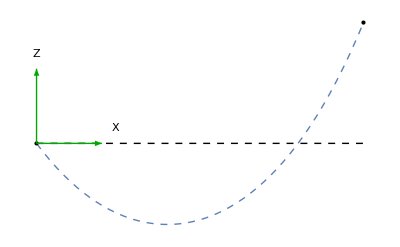

There are two main forces in this process: the force of gravity and the tension in the rope. Gravity pulls the cable down, while the force of tension prevents it from stretching over its length. As a result of these two forces’ confrontation, in equilibrium the cable takes a shape that is “as much down as possible” for a given length. If the cable is displaced by a small amount, it starts oscillating near the equilibrium.

#### Code used to generate the figure

```mathematica
Show[
	Plot[Cosh[x - 1] - Cosh[-1], {x, 0, 2.5}, Axes -> False, PlotStyle -> {Thick, Dashed}],
	Graphics[{
		{PointSize[Large], Point[{0, 0}]},
		{PointSize[Large], Point[{2.5, Cosh[1.5] - Cosh[-1]}]},
		{Thin, Dashed, Line[{{0, 0}, {2.5, 0}}]},
		{Darker[Green], Thin, Arrow[{{0, 0}, {0.5, 0}}]}, Text["X", {0.6, 0.1}],
		{Darker[Green], Thin, Arrow[{{0, 0}, {0, 0.5}}]}, Text["Z", {0, 0.6}]
	}]
]
```

-Graphics-

## Assumptions

### Stability

When physical systems are moved by a small amount from the equilibrium position they can either return to the equilibrium, in which case the equilibrium is called stable, or keep moving away from the equilibrium, in which case the equilibrium is called stable. This work assumes that the cable’s equilibrium configuration is stable, so that the cable only deviates by a small amount from equilibrium

Because the deviation is small, the functions describing the cable at any instant can be written as a sum of their equilibrium value and a small deviation. Quite importantly, when studying small oscillations we can regard this deviation term as being infinitely small compared to the equilibrium term. Mathematically, for some arbitrary function q we can write

q = q_e + O[ε]

where q_e is the equilibrium value of q and ε is a small number.

### Physical properties of the cable

In this work, I am looking at an idealized version of the problem. There are several undoubted assumptions, for example that the cable moves much slower than the speed of light; however, there are some assumptions that can, in some cases, be far from reality. These are:

Air resistance and other friction are negligible

The cable is infinitely thin (and hence has no stiffness)

Stretching and compression of the cable due to axial stresses are absent

From physical intuition we can guess that air resistance is negligible for massive cables, as the force of air drag is proportional to the velocity times length, while the force of inertia is proportional to mass times frequency, which is the same as density times length squared times velocity. We can see that for large cables, the force of inertia becomes dominant. It can also be seen intuitively: a small grain of dust is easily dragged by the air and can float for a while, while a large boulder, if thrown, falls almost like a free-falling object for quite a long time. Now, the stiffness of the cable can be neglected for large cables, too, and here is why. In the case of a paper clip, rigidity is very significant: if held horizontally, the clip does not even bend visibly. However, a piece of concrete reinforcement of the same proportions but three meters long gets strongly curved. Another example: when Titanic capsized and its nose rose up into the air, the stresses tore the ship apart; on the other hand, a smaller toy model of Titanic can easily remain in such position without breaking in half. What this shows is that for long cables, the forces of air resistance and stiffness can be neglected in comparison to the force of gravity.

-Graphics-

An illustration of Titanic breaking in half due to the mechanical stresses. Figure taken from https://www.planetminecraft.com/project/rms-titanic-sinking-at-218-am-breaking-in-half/

The third assumption that we can neglect the cable’s stretching and compression due to lateral stress, in contrast to the first two, holds for short cables. Since the two main forces are, by the two previous assumptions, gravity and tension inside the cable, the equation for the cable’s equilibrium can be very roughly approximated as mg = T, where m is the mass of the cable, g is the free fall acceleration, and T is the force of tension. We can use the approximation m = ρ L A, T = A E σ, where L is the length of the cable, A is its cross-section area, E is the Young modulus of the cable’s material, and σ is the relative change in length. Plugging in, we get σ = (ρ g L)/E, and for the third assumption to hold, this must be much less than 1. For steel, ρ ≈ 8000 kg/m^3, E ≈ 2 10^11 Pa, and on Earth g ≈ 10 m/s^2. If we take the maximal elongation to be σ < 0.001, then the length limit is roughly L ≈ 2500 m, which is a huge length for a cable. There is one more condition, though. We have shown that the cable does not stretch very much in static configuration, however, we also want to ensure that its stretching due to vibrations is much less than its displacement. This is true when the cable’s length divided by the speed of sound is much smaller than the period of its oscillations. Using the approximate formulas c = √(E/ρ), τ = √(L/g), where c is the speed of sound and τ is the characteristic time, we get that L << E/ρg, which is basically the same as the previous condition. Thus, we conclude that the three idealizations are valid for long cables.

## Coordinatizing the problem

### Defining a Cartesian coordinate system

-Graphics3D-

-Graphics-

Let us define a Cartesian coordinate system. Position the origin of coordinates at one of the cable’s attachment points and take the z axis to go vertically. Draw a line connecting the cable’s attachment points; take the projection of this line on the horizontal plane z = 0 to be the x axis. Let us now draw the y axis parallel to x and z in such direction that the coordinate system be right-handed.

#### Code used to generate the visualization

```mathematica
Legended[Show[{
	ParametricPlot3D[{x, 0, Cosh[x - 0.7] - Cosh[0.7]}, {x, 0, 2}, PlotStyle -> {Thick, Darker@Green}, Axes -> False],
	Graphics3D[{
		{Opacity[0.1], InfinitePlane[{{0, 0, 0}, {1, 0, 0}, {0, 0, 1}}]},
		{Arrow[{{0, 0, 0}, {0.5, 0, 0}}]}, {Text["X", {0.6, 0, 0}]},
		{Arrow[{{0, 0, 0}, {0, 0.5, 0}}]}, {Text["Y", {0, 0.6, 0}]},
		{Arrow[{{0, 0, 0}, {0, 0, 0.5}}]}, {Text["Z", {0, 0, 0.6}]}
	}]
}, ImageSize -> Large], LineLegend[{Darker@Green}, {"Cable in equilibrium"}]]
```

-Graphics3D-

### Using the coordinates to describe the rope’s shape

We are interested in studying the cable’s behavior near its equilibrium shape. From physical intuition, it is pretty obvious that in equilibrium, the rope does not bend back (as shown on the figure below), so we can describe its shape using the functions y[t, x] and z[t, x]. The meaning of this is that if a point lies on the rope, and its x coordinate has some value x_1, then its y and z coordinates are y[t, x_1]  and z[t, x_1], respectively. There is a t in the arguments because if the rope is vibrating, its shape changes with time.

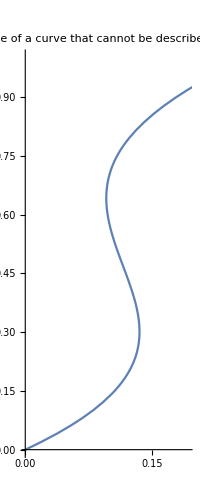

```mathematica
ParametricPlot[{t - 2 t^2 Exp[-t^2], t}, {t, 0, 1}, AspectRatio->Full, PlotLabel->"An example of a curve that cannot be described as z = z[x]"]
```

### Assumption of smoothness

Physical intuition tells us that the cable’s shape must be smooth and curvy, and that it can’t have any sudden bends or discontinuities of this type:

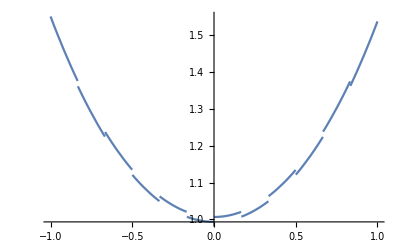

```mathematica
Plot[Cosh[x] + SquareWave[3 x]/150, {x, -1, 1}]
```

We can state this assumption mathematically. This work assumes that y[x] and z[x] are smooth (infinitely differentiable) functions.

### Formulating the boundary conditions

Since one end of the rope is held at the origin, we know that the point whose x coordinate equals zero also has its y and z coordinates equal to zero:

y[t, 0] = 0
z[t, 0] = 0

We can define P to be the cable’s second attachment point. The condition that the cable is fixed at the point P is written as

y[t, x_p] = y_p
z[t, x_p] = z_p

## A minute of high-school physics

### About length elements

By the Pythagorean theorem, the length of a small length of the rope is given by dl^2 = dx^2 + dy^2 + dz^2. Using the fact that dy = dy/dx dx and dz = dz/dx dx, we can write this as

dl = √(1 + (dy/dx)^2 + (dz/dx)^2)dx

### About linear density and mass

A section of length l of the rope has mass

m = ρ l

where ρ is the linear density of the cable, defined as mass per unit length. This work explores a cable with constant ρ.

### About the force of gravity

The force of gravity acting on an object of mass m is given by the formula

(F^–)_g = g^– m

Here g ≈ 9.81 m/s^2 is the absolute value of the free fall acceleration, and g^– is the free fall acceleration vector, whose horizontal components are zero and the vertical (z) component is -g, so that g^– = <0, 0, -g>.

The gravitational potential energy of an object with mass m at height z equals, up to an additive constant,

U_g = m g z

### About the force of tension

#### Introducing the tension scalar

We can describe the tension in the rope as a function T[t, x], which tells us that if at some moment t we look at the point with coordinate x that lies on the cable, the tension there will equal T[t, x] . Because the thin cable cannot transmit pressure (it would just curl up), tension is never negative: T ≥ 0.

#### Introducing the tension vector

If we formally split the cable in two sections, there would be a force between them, as shown in the figure below:

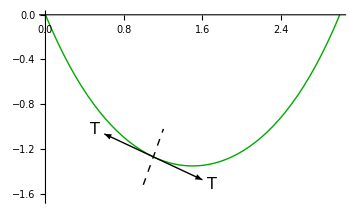

The force will be acting along the rope. It can be proven that, if the rope has no stiffness, any lateral stresses would cause it to twist or bend.

We can write the force that acts on the left section of the rope as T  l^–, where l^– is the unit-vector pointing along the cable in the +x direction and T is the tension at that point of the rope. Similarly, the force with which the right part of the cable is pulled by the left part is given as -T  l^–. Below is given an illustration of that:

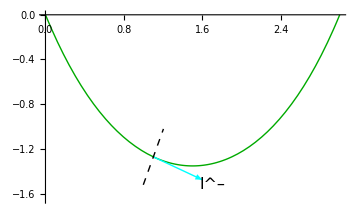

It is convenient to introduce a new vector T^–, which is defined as

T^– ≡ T l^–

The meaning of this vector is that if we divide the cable in two sections, the left side will experience a force T^– exerted by the right side, while the right side will feel a force -T^– from the left side.

It’s important to remember that it’s not completely valid to think of the tension force as a vector, as it acts in both sides; in reality, the force of tension is most correctly described by the stress tensor, which in this case happens to take a diagonal form.

#### Total tension force acting on a small piece of rope

Let’s look at a small piece of cable confined between x_0 and x_0 + dx, where dx is some small number. The force of tension acts on it from both sides:

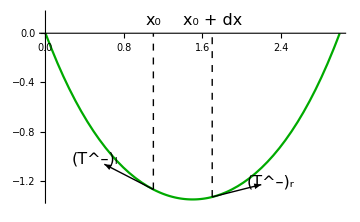
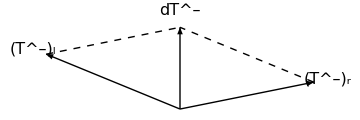

The total force that the rest of the rope exerts on this section equals (T^–)_l + (T^–)_r. We know that (T^–)_l = -T^–[t, x_0] ,   (T^–)_r = T^–[t, x + dx_0]. Since dx is very small, we can say that (T^–)_l + (T^–)_r = T^–[t, x_0 + dx] - T^–[t, x_0]= (∂T^–)/(∂x)dx. So, the total force is given as follows.

d T^– = (∂T^–)/(∂x)dx

We can show that this formula holds for arbitrary parametrization of the rope’s shape:

d T^– = (∂T^–)/(∂α)dα

What this means is that instead of describing the rope’s shape as y[x] and z[x], we could use some other parameter α (for example, arc length) and parametrize the shape of the cable as x[α], y[α], z[α]. And if we take a small piece of rope between α = α_0 and α = α_0 + dα, we could find the total force of tension acting on it using (9).

#### Code used to generate the visualizations

```mathematica
With[{x0 = 1.1},
	Show[{
			Plot[Cosh[x - 1.5] - Cosh[1.5], {x, 0, 3}, PlotStyle -> {Thick, Darker@Green}],
			Graphics[{
				{Thick, Arrow[{#, # - 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Thick, Arrow[{#, # + 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Text[Style["T", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} - 0.6{1, Sinh[x0 - 1.5]}]},
				{Text[Style["T", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} + 0.6{1, Sinh[x0 - 1.5]}]},
				{Dashed, Line[{# + 0.25{Sinh[x0 - 1.5], -1}, # - 0.25{Sinh[x0 - 1.5], -1}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]}
			}]
		},
		PlotRange -> {{0, 3}, {1 - Cosh[1.5] - 0.3, 0}},
		ImageSize -> Medium
	]
]
```

-Graphics-

```mathematica
With[{x0 =1.1},
	Show[{
			Plot[Cosh[x - 1.5] - Cosh[1.5], {x, 0, 3}, PlotStyle -> {Thick, Darker@Green}],
			Graphics[{
				{Thick, Cyan, Arrow[{#, # + 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Text[Style["l^–", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} + 0.6{1, Sinh[x0 - 1.5]}]},
				{Dashed, Line[{# + 0.25{Sinh[x0 - 1.5], -1}, # - 0.25{Sinh[x0 - 1.5], -1}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]}
			}]
		},
		PlotRange -> {{0, 3}, {1 - Cosh[1.5] - 0.3, 0}},
		ImageSize -> Medium
	]
]
```

-Graphics-

```mathematica
With[{x0 = 1.1, dx = 0.6},
	Row[{Show[{
			Plot[Cosh[x - 1.5] - Cosh[1.5], {x, 0, 3}, PlotStyle -> {Thick, Darker@Green}],
			Graphics[{
				{Thick, Arrow[{#, # - 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Thick, Arrow[{#, # + 0.5{1, Sinh[x0 + dx - 1.5]}}& @ {x0 + dx, Cosh[x0 + dx - 1.5] - Cosh[1.5]}]},
				{Dashed, Line[{{x0, Cosh[x0 - 1.5] - Cosh[1.5]}, {x0, 0}}]},
				{Dashed, Line[{{x0 + dx, Cosh[x0 + dx - 1.5] - Cosh[1.5]}, {x0 + dx, 0}}]},
				{Text[Style["x_0", 16], {x0, 0.1}]},
				{Text[Style["x_0 + dx", 16], {x0 + dx, 0.1}]},
				{Text[Style["(T^–)_l", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} - 0.6{1, Sinh[x0 - 1.5]}]},
				{Text[Style["(T^–)_r", 16], {x0 + dx, Cosh[x0 + dx - 1.5] - Cosh[1.5]} + 0.6{1, Sinh[x0 + dx - 1.5]}]}
			}]
		},
		PlotRange -> {{0, 3}, {1 - Cosh[1.5], 0.15}},
		ImageSize -> Medium
	],
	Graphics[{
		{Thick, Arrow[{{0, 0}, -0.5{1, Sinh[x0 - 1.5]}}]}, {Text[Style["(T^–)_l", 16], -0.55{1, Sinh[x0 - 1.5]}]},
		{Thick, Arrow[{{0, 0}, 0.5{1, Sinh[x0 + dx - 1.5]}}]}, {Text[Style["(T^–)_r", 16], 0.55{1, Sinh[x0 + dx - 1.5]}]},
		{Arrow[{{0, 0}, 0.5{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}}]}, {Text[Style["dT^–", 16], 0.6{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}]},
		{Dashed, Line[{-0.5{1, Sinh[x0 - 1.5]}, 0.5{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}}]},
		{Dashed, Line[{0.5{1, Sinh[x0 + dx - 1.5]}, 0.5{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}}]}
	}, ImageSize -> Medium]
	}]
]
```

-Graphics--Graphics-

## Finding the equilibrium

A rope is hung between two poles. What shape does it take in equilibrium? This is the question that this chapter is about - finding y_e[x] and z_e[x]. Since the cable remains in the vertical plane in equilibrium, y_e[x] = 0. As for z_e[x], the chapter gives the derivation in two ways: using Newton’s second law and calculus of variations. After that, some supplementary quantities, such as the tension in the cable, are calculated, and a method to fit the curve to match the boundary conditions is presented. Lastly, the chapter gives an interactive visualization of a catenary cable.

## A brief argument why y_e[x] = 0

Based on physical intuition, we would guess that y_e[x] = 0, which corresponds to the cable being in the vertical plane when in equilibrium. Let’s try to show more persuasively that y_e = 0. In equilibrium, the rope isn’t moving or accelerating: y[x] = const, z[x] = const. Let us look at a small piece of cable confined between x_0 and x_0 + dx. According to Newton’s second law, for the piece to not accelerate, the total force acting on it, which is the sum of the forces of tension and gravity, must be zero.

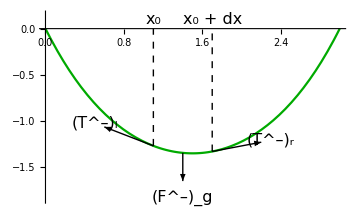
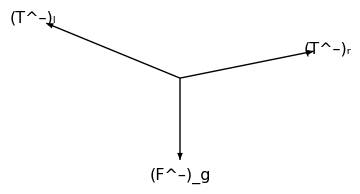

(T^–)_l + (T^–)_r + (F^–)_g = 0

According to (4), (6), and (9), this equals

d/dx[T l^̑] dx + ρ dl g^– = 0

Since the y component of g^– is zero, the y component of the first term in the above equation must be zero as well: d/dx[(T l^̑)_y] = 0. Integrating this, we get

T l_y =  const

where l_y is the y component of the unit tangent vector to the rope. Now, according to the dy/dx = 0 lemma (see proof below), dy_e/dx = 0 must be zero at a least at one point on the rope; and if dy_e/dx = 0 at some point, then l_y equals zero there as well, and so is T l_y. But because this expression is constant, its value is the same everywhere, and so it must be zero at all points. Since T is non-zero, the only way this can happen is if l_y = 0 everywhere. Thus, dy_e/dx = 0 for all x; integrating this expression, we get that y_e[x] = const, or, because y_e[0] = 0 (2),

y_e[x] = 0

#### dy/dx lemma

We know that y[t, 0] = y[t, x_p] = 0, according to the boundary conditions (1) and (2), and so (∫^x_p)_0 dy/dx dx = 0. One way to satisfy this condition is to makey[x] zero everywhere. Alternatively, if dy/dx is positive at some place, is has to be negative somewhere else, and conversely, if dy/dx is negative at some place, it has to be positive somewhere else. In other words, if dy/dx is non-zero at least one point, it has to flip sign at least once. Since dy/dx is a differentiable function, the intermediate value theorem tells us that if dy/dx goes from positive to negative (or the other way), it has to have at least one zero intersect. So, there must be at least one x_0 such that y[t, x_0] = 0. This is true for both the time-dependent y[t, x] and the equilibrium function y_e[x].

#### Code used to generate the visualization

```mathematica
With[{x0 = 1.1, dx = 0.6},
	Row[{Show[{
			Plot[Cosh[x - 1.5] - Cosh[1.5], {x, 0, 3}, PlotStyle -> {Thick, Darker@Green}],
			Graphics[{
				{Thick, Arrow[{#, # - 0.5{1, Sinh[x0 - 1.5]}}& @ {x0, Cosh[x0 - 1.5] - Cosh[1.5]}]},
				{Thick, Arrow[{#, # + 0.5{1, Sinh[x0 + dx - 1.5]}}& @ {x0 + dx, Cosh[x0 + dx - 1.5] - Cosh[1.5]}]},
				{Dashed, Line[{{x0, Cosh[x0 - 1.5] - Cosh[1.5]}, {x0, 0}}]},
				{Dashed, Line[{{x0 + dx, Cosh[x0 + dx - 1.5] - Cosh[1.5]}, {x0 + dx, 0}}]},
				{Text[Style["x_0", 16], {x0, 0.1}]},
				{Text[Style["x_0 + dx", 16], {x0 + dx, 0.1}]},
				{Text[Style["(T^–)_l", 16], {x0, Cosh[x0 - 1.5] - Cosh[1.5]} - 0.6{1, Sinh[x0 - 1.5]}]},
				{Text[Style["(T^–)_r", 16], {x0 + dx, Cosh[x0 + dx - 1.5] - Cosh[1.5]} + 0.6{1, Sinh[x0 + dx - 1.5]}]},
				{Thick, Arrow[{{x0 + dx/2, Cosh[x0 + dx/2 - 1.5] - Cosh[1.5]}, {x0 + dx/2, Cosh[x0 + dx/2 - 1.5] - Cosh[1.5] - 0.5(Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5])}}]},
				{Text[Style["(F^–)_g", 16], {x0 + dx/2, Cosh[x0 + dx/2 - 1.5] - Cosh[1.5]} - 0.8{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}]}
			}]
		},
		PlotRange -> {{0, 3}, {1 - Cosh[1.5] - 0.5, 0.15}},
		ImageSize -> Medium
	],
	Graphics[{
		{Thick, Arrow[{{0, 0}, -0.5{1, Sinh[x0 - 1.5]}}]}, {Text[Style["(T^–)_l", 16], -0.55{1, Sinh[x0 - 1.5]}]},
		{Thick, Arrow[{{0, 0}, 0.5{1, Sinh[x0 + dx - 1.5]}}]}, {Text[Style["(T^–)_r", 16], 0.55{1, Sinh[x0 + dx - 1.5]}]},
		{Thick, Arrow[{{0, 0}, -0.5{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}}]}, {Text[Style["(F^–)_g", 16], -0.6{0, Sinh[x0 + dx - 1.5] - Sinh[x0 - 1.5]}]}
	}, ImageSize -> Medium]
	}]
]
```

-Graphics--Graphics-

## Finding z_e[x]

### Using Newton’s second law

We can use the Newton’s second law to write the equilibrium condition for a small piece of cable. With the help of some algebra, this condition is turned into a differential equation, which we then can solve.

#### Formulating the equilibrium condition

Let’s write the equilibrium condition for the cable. If the cable is in equilibrium, then none of its parts experiences any acceleration, and hence the force acting upon each section of the cable is zero.

Let us look at a section of the rope that is confined between x and x + δx, where δx is some small number. There are three forces acting on this piece of rope: tension force acting from the left part of the rope (F^–)_l, tension force acting from the right part of the rope (F^–)_r, and the force of gravity (F^–)_g. By Newton’s second law, for the section to remain in equilibrium, the sum of these three forces must be zero:

(T^–)_l + (T^–)_r + (F^–)_g = 0

Here is a picture illustrating this (not drawn to scale; the section is actually much smaller):

-Graphics--Graphics-

We can use the formulas (4), (5), (6), and (10) to find (F^–)_g = ρ √(1 + (dz_e/dx)^2)dx. Also, according to (9), (T^–)_l + (T^–)_r  = (∂T^–)/(∂x)dx; because the system is in equilibrium, T^–[t, x] = (T^–)_e[x], and so (T^–)_l + (T^–)_r  = (d(T^–)_e)/dx dx. Substituting this into (11) and cancelling the dx, we get

(d(T^–)_e)/dx + ρ g^– √(1 + (dz_e/dx)^2) = 0

The horizontal component of the force of gravity is zero, so ((d(T_e))_x)/dx = 0, where (T_e)_x denotes the value of the x component of the vector T (8) in equilibrium. Integrating, we get

(T_e)_x = const

But we also know that the force of tension acts along the rope. We can write this condition as

((T_e)_z)/((T_e)_x) = dz_e/dx

Substituting this into (d(T^–)_e)/dx + ρ g^– √(1 + (dz_e/dx)^2) = 0, we get

(T_e)_x(d^2 z_e)/dx^2 - ρ g √(1 + (dz_e/dx)^2) = 0

This is the equation that allows us to determine the equilibrium shape of the cable.

#### Solving the equation

Denoting V ≡ dz_e/dx, we can write (13) as

dV/dx = (ρ g)/((T_e)_x)√(1 + V^2)

This is a separable differential equation, whose solution is

V[x] = Sinh[(ρ g)/((T_e)_x)(x - x_0)]

where x_0 is some constant. Remembering that V ≡ dz_e/dx, we can find z_e as a function of x:

z_e[x] = z_e[0] + (∫^x)_0 V[x'] dx'

Using the boundary conditions (2), we get the final answer:

z_e[x] = Λ (Cosh[(x - x_0)/Λ] - Cosh[x_0/Λ])

Here Λ = ((T_e)_x)/(ρ g) is the characteristic length. From this formula, we can see that z_e is minimal at x = x_0.

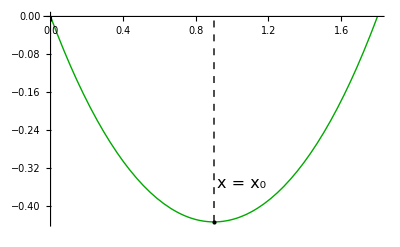

#### Code used to generate the illustration

```mathematica
With[{Λ = 1, x0 = 0.9, xp = 1.8},
	Show[{
		Plot[Λ(Cosh[(x - x0)/Λ] - Cosh[x0/Λ]), {x, 0, xp}, PlotStyle-> {Thick, Darker@Green}],
		Graphics[{
			{PointSize[Large], Point[{x0, Λ(Cosh[(x0 - x0)/Λ] - Cosh[x0/Λ])}]},
			{Dashed, Line[{{x0, Λ(Cosh[(x0 - x0)/Λ] - Cosh[x0/Λ])}, {x0, 0}}]},
			{Text[Style["x = x_0", 16], {x0 + 0.15, Λ(Cosh[(x0 - x0)/Λ] - Cosh[x0/Λ]) + 0.08}]}
		}]
	}]
]
```

-Graphics-

### Using calculus of variations

For a physical system to be in equilibrium, its potential energy must be minimal; in other words, if we distort the system from its equilibrium in any direction by some small amount, its potential energy will increase. If the cable was not attached to anything or could stretch effortlessly, it would simply fall down. However, since it has a certain fixed length, in equilibrium it will take the shape that minimizes potential energy for a fixed length. This is a classic minimization problem that we can solve using the Euler-Lagrange equation.
	This way, z_e[x] can be found in a much simpler and elegant way than using Newton’s second law, and the result is also more convincing because when using calculus of variations, we only postulate the minimum potential energy principle and the length constraint, and the rest is just math. On the other hand, using Newton’s second law is comparatively messy.

#### Deriving the modified Lagrange’s equation

We want to minimize the potential energy, which is in general given as

U = ∫ℒ[z_e, dz_e/dx] dx

while keeping the length of the rope, which is given below, constant.

L = ∫f[z_e, dz_e/dx]dx

Here f and ℒ are some known functions; we could have plugged in the expressions right away, but for now it’s more convenient to keep them as just f and ℒ.

The equilibrium shape of the cable can be described by some function z_e[x], which we don’t know yet (actually, we do know it from (14), but let’s pretend we don’t). The main property of z_e[x] is that it characterizes the state with minimum potential energy for a given length, and any small deviation from this state would result in an increase in potential energy. To make use of this property, suppose we change z_e[x] to z_e[x] + ε δ[x], where ε is some small number and δ[x] is a function of x that is zero at the boundaries to satisfy (2) and (3). The derivative of z_e then becomes dz_e/dx  + ε dδ/dx, and the potential energy equals

U = ∫ℒ[z_e + ε δ[x], dz_e/dx + ε dδ/dx] dx = ∫(ℒ[z_e, dz_e/dx] + (∂ℒ)/(∂z)δ[x] + (∂ℒ)/(∂(∂_x z_e))dδ/dx[x]) dx

where (∂ℒ)/(∂(∂_x z_e)) ≡ (∂ℒ)/(∂(dz_e/dx)).

Using integration by parts, we can write ∫(∂ℒ)/(∂(∂_x z_e))dδ/dx[x] dx = (∂ℒ)/(∂(∂_x z_e))δ[x] - ∫d/dx[(∂ℒ)/(∂(∂_x z_e))]δ[x] dx. Since δ[x] is zero at the boundaries, the first term on the right hand side is zero, and U becomes

U = ∫(ℒ[z_e, dz_e/dx] + ((∂ℒ)/(∂z_e) - d/dx(∂ℒ)/(∂(∂_x z_e)))δ[x]) dx

Since U must not change under this variation, it must still be ∫ℒ[z_e, dz_e/dx] dx.

0 = ∫((∂ℒ)/(∂z_e) - d/dx(∂ℒ)/(∂(∂_x z_e)))δ[x] dx

Now, we also know that the variation must conserve the length of the rope. The condition for that can be derived in an analogous way.

0 = ∫((∂f)/(∂z_e) - d/dx(∂f)/(∂(∂_x z_e)))δ[x] dx

We are allowed to make any variation δ[x] as long as it conserves the length of the rope, e.g. satisfies the latter equation. And, on the other hand, we know that if the rope is in equilibrium, the variation must not change the potential energy. Thus, any δ[x] that satisfies the length conservation criterion must also not change the potential energy. This is only possible if one of the equations is simply a constant multiple of the other, or

(∂ℒ)/(∂z_e) - d/dx(∂ℒ)/(∂(∂_x z_e)) = λ ((∂f)/(∂z_e) - d/dx(∂f)/(∂(∂_x z_e)))

where λ is a constant known as the Lagrange’s multiplier. The cool thing is that we can re-write the above equation as

(∂ℒ_ef)/(∂z_e) - d/dx(∂ℒ_ef)/(∂(∂_x z_e)) = 0

where ℒ_ef ≡ ℒ - λ f.

#### Deriving the equation for z_e[x]

The equation (14) is basically the Euler-Lagrange equation for our system. We could simply plug in the formulas for ℒ and f and get an expression for d^2/dx^2 z_e[x] in terms of d/dx z_e[x] and z_e[x]. But it’s easier utilize the law of conservation of energy, which is true because (∂ℒ_ef)/(∂x) = 0. The energy function is written as

E = (∂ℒ_ef)/(∂(∂_x z_e)) - ℒ_ef = const

Notice that this is not the “usual” kind of energy that is conserved with time in physical systems; what we are dealing with is a somewhat more abstract quantity that is conserved not in time but along the cable’s length.
	In this formula, ℒ_ef = ℒ - λf, where ℒ and f were defined in the previous subsubsection as potential energy per unit x and arc length per unit x. Substituting the formulas (4), (5), (7), we get

E = (λ - ρ g z_e)/(√(1 + (dz_e/dx)^2))

From here,

(dz_e/dx)^2 = ((ρ g z_e - λ)/E)^2 - 1

#### Solving the equation

Solving (16) is very easy, as it can be transformed to (Z')^2 = Z^2 - 1. Let’s make a change of variables Z ≡ (ρ g z_e - λ)/E, X = (ρ g)/E x; then, dZ/dX = dz/dx, and the equation takes the form

(dZ/dX)^2 = Z^2 - 1

Now, if we substitute Z = Cosh[X - X_0], we see that this is indeed the solution. Since this solution contains one arbitrary constant X_0 and the ODE is of order 1, we know that this is the general solution. Going back to our original variables, we get

z_e[x] =λ/(ρ g) + E/(ρ g) Cosh[(ρ g)/E(x - x_0)]

We can find λ from the condition z_e[0] = 0 (2).

z[x] = E/(ρ g) (Cosh[(x - x_0)/(E/ρg)] - Cosh[x_0/(E/ρg)])

For this formula to be compatible with (14), we get that E = (T_e)_x. In other words, conservation of this abstract energy basically told us that the horizontal tension is constant.

## Finding supplementary quantities

### Arc length

Substituting the formulas for y_e[x] (10) and z_e[x] (14) into dl = √(1 + (dy/dx)^2 + (dz/dx)^2)dx (4), we get

dl_e = Cosh[(x - x_0)/Λ]dx

where dl_e is the length of rope confined between x and x + dx; the index e is to specify that this formula is only valid when the cable is in equilibrium. Integrating this from 0 to x, we get that the length of cable confined between 0 and x is written as follows.

l_e[x] = Λ (Sinh[(x - x_0)/Λ] + Sinh[x_0/Λ])

What this means if that if a little bug would walk along the rope from the origin to a point with coordinate x, it would cover a distance l_e[x]. The inverse transformation is

x[l_e] = x_0 + Λ ArcSinh[(l_e - l_0)/Λ]

where l_0 ≡ Λ Sinh[x_0/Λ] is the value of l_e when x = x_0.

### Tension

We know that because the tension in the rope is directed along its length, ((T_e)_z)/((T_e)_x) = dz/dx, or (T_e)_z = (T_e)_x dz/dx. Knowing this, we can use the formula (14) for z_e[x] to get (T_e)_z:

(T_e)_z[x] = (T_e)_x Sinh[(x - x_0)/Λ]

The absolute value of T[x] can be found using the Pythagorean theorem:

T_e = √(((T_e)_x)^2 + ((T_e)_z)^2) = (T_e)_x Cosh[(x - x_0)/Λ]

Using the fact that in (14), Λ = ((T_e)_x)/(ρ g), we can write this as

T_e[x] = ρ g Λ Cosh[(x - x_0)/Λ]

We also want T_e as a function of l_e. Using the formula (18) and the identity Cosh[φ]^2 = 1 + Sinh[φ]^2, we get

T_e[l_e] = ρ g Λ √(1 + ((l_e - l_0)/Λ)^2)

### Curvature

Substituting (14) into the formula for curvature, we get

k_e[x] = 1/Λ 1/Cosh[(x - x_0)/Λ]^2

In terms of l_e, k can be expressed as

k_e[l] = 1/Λ 1/(1 + ((l - l_0)/Λ)^2)

## Fitting the constants

The cable has a certain fixed length, and its ends are attached at certain fixed points. These criteria dictate what the values of Λ and x_0 must be.

### Formulating the length criterion

We know that the total length of the rope equals L. Using (17), we can write this as l[x_p] = L, or

L = Λ (Sinh[(x_p - x_0)/Λ] + Sinh[x_0/Λ])

### Formulating the position criterion

We know that one end of the rope is attached to the point (0, 0). However, plugging it into the formula for z_e doesn’t give us any information: we just get zero equals zero:

0 = Λ (Cosh[(0 - x_0)/Λ] - Cosh[x_0/Λ])

This is because we have already utilized this fact when obtaining the formula (14) for z_e[x]. But we also know that at x = x_p, z = z_p (3):

z_p = Λ (Cosh[(x_p - x_0)/Λ] - Cosh[x_0/Λ])

This gives us one more equation that we can use to find Λ and x_0.

### Finding the equations for Λ and x_0

From the definitions of sinh and cosh, we can prove that

Cosh[A] - Cosh[B] = 2 Sinh[(A + B)/2] Sinh[(A - B)/2]
Sinh[A] + Sinh[B] = 2 Sinh[(A + B)/2] Cosh[(A - B)/2]

Using these identities, (23) and (24) can be re-written as

z_p/Λ = Cosh[(x_p - x_0)/Λ] - Cosh[x_0/Λ] = 2 Sinh[x_p/(2Λ)] Sinh[(x_p - 2 x_0)/(2Λ)]
L/Λ = Sinh[(x_p - x_0)/Λ] + Sinh[x_0/Λ] = 2 Sinh[x_p/(2Λ)] Cosh[(x_p - 2 x_0)/(2Λ)]

From here,

(L/Λ)^2 - (z_p/Λ)^2 = 4 Sinh^2[x_p/(2Λ)] (Cosh^2[(x_p - 2 x_0)/(2Λ)] - Sinh^2[(x_p - 2 x_0)/(2Λ)])

Using the fact that Cosh^2[A] - Sinh^2[A] = 1, we find the following equation.

√(L^2 - z_p^2) = 2Λ Sinh[x_p/(2 Λ)]

This trick has allowed us to eliminate x_0, and now we have an equation where the only unknown is Λ. This is a transcendental equation that is solved numerically in the next subsection.

We can use the same trick we have used to obtain (26) to find x_0. For that, let us divide the first line of (25) by the second: z_p/L = Tanh[(x_p - 2 x_0)/(2Λ)]. From here, we can find x_0 given L, x_p, z_p, and Λ:

x_0 = x_p/2 - Λ ArcTanh[z_p/L]

#### Bonus

Quite interestingly, for large Λ, Sinh[x_p/(2 Λ)] ≈ x_p/(2 Λ), and the formula basically becomes Pythagorean formula:

(L^2 - z_p^2)/4 ≈ Λ^2 (x_p/(2 Λ^2))^2
L^2 ≈ x_p^2 + z_p^2

We can also prove the inequality L^2 ≥  x_p^2 + z_p^2. If we write the former formula as

(√(L^2 - z_p^2))/(2 Λ) = Sinh[x_p/(2 Λ)]

and use the fact that A ≤ Sinh[A] for positive A, we find that

x_p/(2 Λ) ≤ Sinh[x_p/(2 Λ)]
x_p/(2 Λ) ≤ (√(L^2 - z_p^2))/(2 Λ)
x_p^2 ≤ L^2 - z_p^2
L^2 ≥ x_p^2 + z_p^2

This basically tells us that the cable’s other end cannot be taken from the first one on a distance larger than L. It was obvious from physical intuition, but it’s also fun to rediscover things like that.

### Numerically computing Λ and x_0

#### Computing Λ

We can find Λ from the equation (26) because the only unknown is Λ. For that, let’s introduce an auxiliary variable ϕ ≡ (|x_p|)/(2 Λ). The equation (26) can then be written as

Sinh[ϕ]/ϕ = (√(L^2 - z_p^2))/x_p

Now, when written this way, we can see that (26) is actually a very nice equation. First of all, it has no singularities: the value of the left hand side will remain finite for any finite ϕ, in particular lim_(ϕ → 0) Sinh[ϕ]/ϕ = 1. The function is also smooth, which makes it much easier to work with. As ϕ goes to infinity, the value of Sinh[ϕ]/ϕ goes to infinity as well, which means that we can solve the equation for arbitrarily large right hand side. Also, the right hand side monotonically increases with ϕ for ϕ > 0, as we can see from the figure below and from the formal proof beneath it. Combine these facts, and we’ve got to ourselves a nearly perfect equation for numerical solutions. We can solve it for 1 ≤ RHS < ∞, where RHS is the right hand side (by the way, the RHS cannot be less than 1 because of the inequality (27)). Because the function is smooth, virtually any numerical method would work nicely with it.
	Because the function Sinh[ϕ]/ϕ is even, if there is a solution ϕ, -ϕ would be a solution as well. However, since ϕ ≡ x_p/(2 Λ) and Λ ≡ ((T_e)_x)/(ρ g), and (T_e)_x > 0, Λ is positive as well, and hence so is ϕ. So, we basically only need the positive half of the solutions.
	Since Sinh[ϕ]/ϕ is a continuous function that increases monotonically for 0 < ϕ < ∞, if lim_(ϕ → 0) Sinh[ϕ]/ϕ = 1 ≤ RHS < ∞, according to the middle value theorem, the equation will have exactly one solution in that interval.

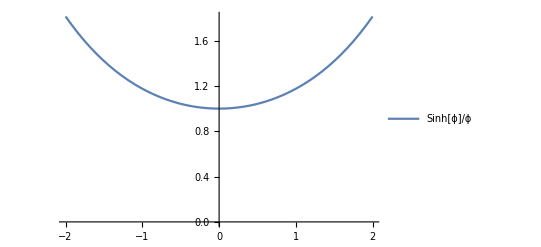

```mathematica
Plot[ Sinh[ϕ]/ϕ, {ϕ, -2, 2}, PlotLegends->{Style["Sinh[ϕ]/ϕ", 18]}, PlotRange->{0, Sinh[2]/2}]
```

To prove that Sinh[ϕ]/ϕ increases monotonically for ϕ > 0, we can take its derivative and show that it’s positive for ϕ > 0. d/dϕ[Sinh[ϕ]/ϕ] = (Cosh[ϕ] - Sinh[ϕ] / ϕ)/ϕ; it is greater than zero for positive ϕ, as the numerator Cosh[ϕ] - Sinh[ϕ]/ϕ = (∑^∞)_(n = 0)ϕ^(2n)/((2n)!) - 1/ϕ(∑^∞)_(n = 0)ϕ^(2n + 1)/((2n + 1)!) = (∑^∞)_(n = 0)(1/((2n)!) - 1/((2n + 1)!))ϕ^(2n) is positive because 1/((2n)!) is always larger than or equal to 1/((2n + 1)!) for n ≥ 0, and hence every term in the sum is nonnegative.

Now that we know all these sweet facts about the equation, we can write a function to solve it:

```mathematica
ClearAll[findLambda];
findLambda[L_, xp_, zp_] := With[
	{
		D = Sqrt[L^2 - zp^2] / xp
	},
	If[(!Element[D, Reals]) || (D < 1),
		$Failed,
		(If[#[[1, 2]] > 0, xp / (2 #[[1, 2]]), Nothing]& /@ 
			NSolve[D == Sinh[ϕ] / ϕ, ϕ, Reals, WorkingPrecision -> MachinePrecision])[[1]]
	]
];
```

Here is an example of how it works:

```mathematica
findLambda[2, 1, 1]
```

0.261327

```mathematica
findLambda[0, 1, 1]
```

$Failed

#### Computing x_0

Having found Λ, calculating x_0 is rather straightforward; we just have to plug in the values in the equation (26), and we get the answer:

```mathematica
ClearAll[findX0];
findX0[L_, xp_, zp_, Λ_] := xp / 2 - Λ ArcTanh[zp / L];
```

## Visualizing a hanging cable

```mathematica
hangingCableToy[]
```

### Drawing a cable given Λ, x_0, x_p

In this chapter, we have found the shape of the cable as a function of its parameters L, x_p, z_p. The code below is a practical implementation of that; the function drawCableHelper draws the cable given Λ, x_0, and x_p, and also displays its length and maximum and minimum tension in the cable. Here M ≡ ρ L is the total mass of the cable.

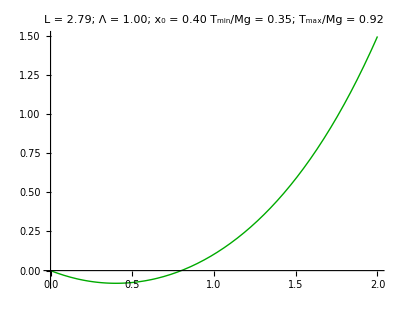

```mathematica
drawCableHelper[1, 0.4, 2]
```

```mathematica
ClearAll[drawCableHelper];
Options[drawCableHelper] = {PlotRange -> Automatic, AspectRatio -> Automatic, PlotStyle -> {Thick, Darker@Green}, ImageSize -> Automatic, Label -> True};
drawCableHelper[Λ_, x0_, xp_, OptionsPattern[]] := Block[
	{
		L = Λ(Sinh[(xp - x0)/Λ] + Sinh[x0/Λ]),
		disp = Function[x, StringPadRight[ToString@NumberForm[x, 3] <> If[IntegerQ[x], ".", ""], 4, "0"]],
		TrelMin, TrelMax
	},
	{TrelMin, TrelMax} = Λ/L({Min[#], Max[#]}& @ {Cosh[x0/Λ], If[0 ≤ x0 ≤ xp, 1, Nothing], √(1 + (L/Λ - Sinh[x0/Λ])^2)}); (* Subscript[T, rel] ≡ T/ρgL *)
	
	Plot[
		Λ Cosh[x / Λ - x0 / Λ] - Λ Cosh[x0 / Λ],
		{x, 0, xp},
		PlotRange -> OptionValue["PlotRange"],
		AspectRatio -> OptionValue["AspectRatio"],
		PlotStyle -> OptionValue["PlotStyle"],
		ImageSize -> OptionValue["ImageSize"],
		PlotLabel -> If[OptionValue["Label"],
			"L = " <> disp@L <>  ";    Λ = " <> disp[Λ] <> ";    x_0 = " <> disp[x0] <> "\nT_min/Mg = " <> disp@TrelMin <> ";    T_max/Mg = " <> disp@TrelMax,
			""
		]
	]
];
```

### Drawing a cable given x_p, z_p, L

The function drawCable is the same as drawCableHelper, except that its arguments are not Λ, x_0, x_p, but rather x_p, z_p, L. In other words, knowing the shape of the length of the cable and the position of its attachment points, we can use drawCable to compute its shape, as well as maximum and minimum tension.

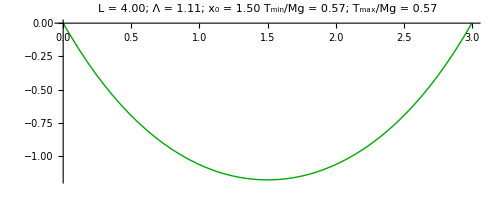

```mathematica
drawCable[3, 0, 4]
```

```mathematica
ClearAll[drawCable];
Options[drawCable] = {"PlotStyle" -> {Thick, Darker@Green}, "ImageSize" -> Automatic, "Label" -> True};
drawCable[xp_, zp_, L_, OptionsPattern[]] := Block[{Λ, x0},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
		
	drawCableHelper[Λ, x0, xp, PlotStyle -> OptionValue["PlotStyle"], ImageSize -> OptionValue["ImageSize"], Label -> OptionValue["Label"]]
];
```

### An interactive hanging cable toy

The function hangingCableToy is basically an interactive version of drawCable. By playing around with the  cable’s parameters you can see how its shape and the maximum and minimum tension change in response. For example, you can see that tension in the cable increases as its attachment points are pulled further apart.

```mathematica
hangingCableToy[]
```

```mathematica
ClearAll[hangingCableToyHelper, hangingCableToy];
hangingCableToyHelper[P_, L_] := Module[{Λ, x0},
		Λ = findLambda[L, P[[1]], P[[2]]];
		x0 = findX0[L, P[[1]], P[[2]], Λ];
		
		Show[{
			drawCableHelper[Λ, x0, P[[1]], PlotRange -> {{-0.2, 2}, {-1, 1}}, AspectRatio -> 2/2.2],
			Graphics@{Dashed, Gray, Circle[{0, 0}, L]}
		}]
	];
hangingCableToy[] := Manipulate[
	hangingCableToyHelper[P, L],
	{{P, {1/3, 1/6}}, {0.1, -1}, {2, 1}}, {{L, 3/4}, 0.5, 2},
	ControlType -> {Locator, VerticalSlider}
];
```

## Curvilinear coordinates

When studying the motion of the cable near equilibrium, instead of x, y, z it is convenient to use coordinates fitted to the cable’s equilibrium shape. This chapter defines these coordinates and explores their properties.

## Definition

-Graphics3D-Curvilinear coordinates ζ, y, h

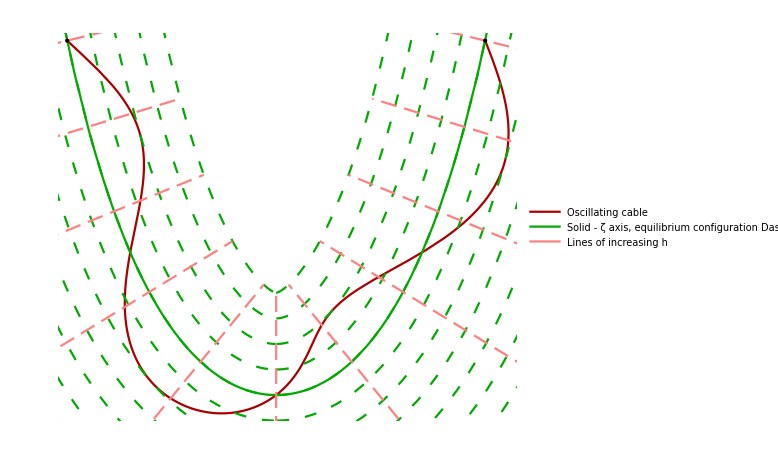

The shape of the cable can be described in Cartesian coordinates x, y, z using the functions y[t, x], z[t, x]. However, it is more convenient to introduce curvilinear coordinates ζ, h, which are fitted to the cable’s equilibrium as explained below. And instead of using the functions y[t, x], z[t, x] to describe the cable’s shape, we can use y[t, ζ], h[t, ζ]. The advantage of that is that while z[t, x] is nonzero in equilibrium (14), the coordinates ζ, h are defined so that h[t, ζ] = 0 in equilibrium. This makes the equations governing the cable’s oscillations homogenous and also simplifies the calculations.
	This section constructs the coordinate system ζ, y, h by first taking the cable’s equilibrium configuration as the ζ axis and then defining ζ and h such that the two coordinates were orthogonal to each other and y and so that the norm of the basis vector of h was 1.

#### Code used to generate the illustrations

```mathematica
Block[
	{
		L = 2, xp = 1, zp = 0,
		Λ, x0, l0,
		xe, ze, ζbar, hbar,
		ζlines, hlines, ζ, h
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	l0 = Λ Sinh[x0 / Λ];

	xe = Function[ζ, x0 + Λ ArcSinh[(ζ - l0)/Λ]];
	ze = Function[ζ, Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2))];
	ζbar = Function[ζ, {1, (ζ - l0)/Λ}/(√(1 + (ζ - l0)^2/Λ^2))];
	hbar = Function[ζ, {-(ζ - l0)/Λ, 1}/(√(1 + (ζ - l0)^2/Λ^2))];
	
	ζlines = Plus[# hbar[ζ], {xe[ζ], ze[ζ]}]& /@ Range[-2Λ, Λ, Λ/4];
	hlines = Plus[h hbar[#], {xe[#], ze[#]}]& /@ Range[0, L, L/10];
	
	Legended[Show[{
		ParametricPlot[{xe[ζ], ze[ζ]} + Λ/2 hbar[ζ] Sin[4 π/L ζ],
			{ζ, 0, L},
			PlotStyle -> {Thick, Darker@Red},
			Axes -> False
		],
		ParametricPlot[{xe[ζ], ze[ζ]},
			{ζ, -L, 2L},
			PlotStyle -> {Thick, Darker@Green}
		],
		ParametricPlot[ζlines,
			{ζ, -L, 2L},
			PlotStyle -> Array[{Thin, Dashing[{0.015, 0.02}], Darker@Green}&, Length@ζlines]
		],
		ParametricPlot[hlines,
			{h, -2Λ, Λ},
			PlotStyle -> Array[{Thin, Dashing[{0.02, 0.01}], Pink}&, Length@ζlines]
		],
		Graphics[{
			{PointSize[Large], Point[{0, 0}]},
			{PointSize[Large], Point[{xp, zp}]}
		}]
	}, ImageSize -> Large], LineLegend[{Darker@Red, Darker@Green, Pink},
	{"Oscillating cable",  "Solid - ζ axis, equilibrium configuration\nDashed - lines of increasing ζ", "Lines of increasing h"}]]
]
```

-Graphics-

```mathematica
Block[
	{
		hbar = Function[x, Normalize[{-Sinh[x], 0, 1}]],
		ybar = {0, 1, 0},
		pointOnζaxis = Function[x, {x, 0, Cosh[x]}],
		X = 1,
		h = 0.4,
		y = 0.6,
		plt
	},
	plt = Show[
		{
			ParametricPlot3D[
				pointOnζaxis[x],
				{x, -1/2, 5/4},
				PlotStyle -> {Thick, Darker@Green},
				AxesLabel -> (Style[#, 16]& /@ {"X", "Y", "Z"})
			],
			ParametricPlot3D[
				pointOnζaxis[X] + y1 ybar + h1 hbar[X],
				{y1, -1, 1}, {h1, -1, 1},
				PlotStyle -> {Orange, Opacity[0.3]},
				Mesh -> 16,
				MeshStyle -> {{Thin, Gray}}
			],
			Graphics3D[{
				(*{Opacity[0.3], Orange, InfinitePlane[
					(pointOnζaxis[X] + #)&/@ {{0, 0, 0}, ybar, hbar[X]}
				]},*)
				{PointSize[Large], Darker@Green, Point[pointOnζaxis[X]]},
				{Line[{
					(pointOnζaxis[X] + #)&/@ {{0, 0, 0}, y ybar}
				}]},
				{Text[
					Style["y", 12],
					pointOnζaxis[X] + y/2 ybar + h/6 hbar[X]
				]},
				{Text[
					Style["h", 12],
					pointOnζaxis[X] + (9y)/8 ybar + h/2 hbar[X]
				]},
				{Darker@Darker@Green, Text[
					Style["ζ", 12],
					pointOnζaxis[X - 0.1] - y/8 ybar + h/8 hbar[X]
				]},
				{Line[{
					(pointOnζaxis[X] + y ybar + #)&/@ {{0, 0, 0}, h hbar[X]}
				}]},
				{PointSize[Large], Blue, Point[pointOnζaxis[X] + y ybar + h hbar[X]]}
			}]
		},

		PlotRange -> {{-1/2, 5/4}, {-1/4, 0.7}, {1/2, Cosh[5/4] + 0.1}},
		ViewPoint -> {1.1, -0.9, 0.6}
	];
	
	If[False, 
		Rasterize[
			plt,
			ImageSize -> {450, 450}
		],
		Labeled[plt, "Curvilinear coordinates ζ, y, h"]
	]
]
```

-Graphics3D-Curvilinear coordinates ζ, y, h

### Choosing the origin

The choice of where to place the origin is completely arbitrary. For convenience, I will take the point x = z = 0 to also be the point ζ = h = 0.

x = z = 0               ↔             ζ = h = 0

### Defining ζ

It is natural to try and make use of the fact that the cable oscillates near some stable equilibrium configuration; in analogy to how a harmonic oscillator is typically studied in coordinates centered at the lowest point of the potential, we can choose a coordinate system such that the equilibrium configuration would correspond to something being zero. While in the case of a harmonic oscillator this simply meant placing the origin of coordinates at the lowest point of the potential, since the cable is not a point particle but a continuous curve, we need to “place” an entire axis in a certain way. Let us call this axis the ζ axis. In the case of a harmonic oscillator, the lowest energy state corresponded to the particle - a zero-dimensional point mass - being at the origin of coordinates, a zero-dimensional point. The equilibrium of a cable - a one-dimensional curve - corresponds to the cable lying on the ζ axis, a one-dimensional curve.
	To say this shorter, the ζ axis is defined as the shape that the cable of a given length fixed at two given points takes in equilibrium which id, according to the formula (14), given by the parametric equation z = Λ (Cosh[(x - x_0)/Λ] - Cosh[x_0/Λ]). This tells us that, first, the ζ axis lies in the xz plane, and second, that if a point lies on the ζ axis, then its coordinates x, z are related by z = Λ (Cosh[(x - x_0)/Λ] - Cosh[x_0/Λ]).

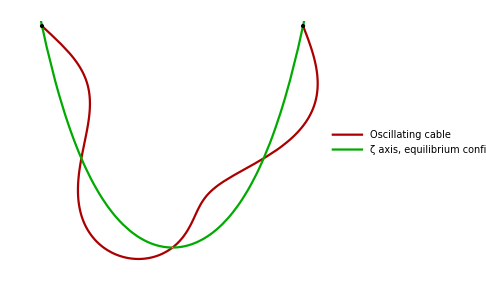

We have just defined what the ζ axis is, but we haven’t defined the actual coordinate yet; we haven’t said anything about the scale of ζ, namely how dζ relates to a length element dl. The choice is arbitrary, however, the natural thing to do would be to define ζ so that some two points with coordinates ζ and ζ + dζ lying on the ζ axis would be separated by the distance dl. In other words, we can split the ζ axis (the green line) into intervals of equal length and define ζ so that these also were intervals of equal ζ:

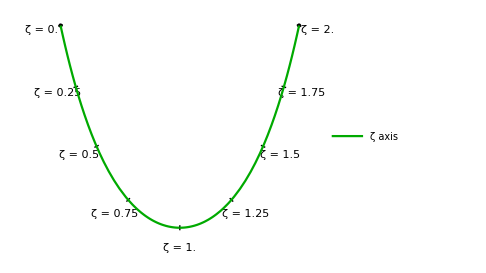

Knowing the parametric equation describing the ζ axis, we can find an explicit formula that tells us the x, y, z coordinates of a point on the ζ axis with some given ζ:

x[ζ] = x_0 + Λ ArcSinh[(ζ - l_0)/Λ]
y[ζ] = 0
z[ζ] = Λ (√(1 + ((ζ - l_0)/Λ)^2) - √(1 + (l_0/Λ)^2))

The formula is such that (((x|)_(ζ = 0) = y|)_(ζ = 0) = z|)_(ζ = 0) = 0 and the distance dl between the points with coordinates ζ and ζ + dζ would be equal to dζ: dl = dζ. The formula describes a one-dimensional line, and so far we haven’t coordinatized three-dimensional space.
	Also, because the cable in equilibrium configuration matches the ζ axis, for a cable in equilibrium ζ is the same as arc length. From this follows the fact that a point on the ζ axis with coordinate L is the cable’s second attachment point, the point P. This can be checked directly by plugging in ζ = L into (30). But in general ζ and arc length are very different things, and it is crucial to distinguish them.

#### ζ is not arc length

The cable oscillates near the ζ axis, and it is very tempting to think that the coordinate ζ is the same as arc length. However, this is not the case: arc length is measured along the oscillating cable, while the ζ axis does not change with time.

#### Code used to generate the figures

```mathematica
Block[
	{
		L = 2, xp = 1, zp = 0,
		Λ, x0, l0,
		xe, ze, hbar
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	l0 = Λ Sinh[x0 / Λ];

	xe = Function[ζ, x0 + Λ ArcSinh[(ζ - l0)/Λ]];
	ze = Function[ζ, Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2))];
	hbar = Function[ζ, {-(ζ - l0)/Λ, 1}/(√(1 + (ζ - l0)^2/Λ^2))];
	
	Legended[Show[{
		ParametricPlot[{xe[ζ], ze[ζ]} + Λ/2 hbar[ζ] Sin[4 π/L ζ],
			{ζ, 0, L},
			PlotStyle -> {Thick, Darker@Red},
			Axes -> False
		],
		ParametricPlot[{xe[ζ], ze[ζ]},
			{ζ, -L, 2L},
			PlotStyle -> {Thick, Darker@Green}
		],
		Graphics[{
			{PointSize[Large], Point[{0, 0}]},
			{PointSize[Large], Point[{xp, zp}]}
		}]
	}, ImageSize -> Medium], LineLegend[{Darker@Red, Darker@Green},
	{"Oscillating cable",  "ζ axis, equilibrium configuration"}]]
]
```

-Graphics-

```mathematica
Block[
	{
		L = 2, xp = 1, zp = 0,
		Λ, x0, l0,
		xe, ze, hbar
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	l0 = Λ Sinh[x0 / Λ];

	xe = Function[ζ, x0 + Λ ArcSinh[(ζ - l0)/Λ]];
	ze = Function[ζ, Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2))];
	hbar = Function[ζ, {-(ζ - l0)/Λ, 1}/(√(1 + (ζ - l0)^2/Λ^2))];
	
	Legended[Show[{
		Graphics[Join[{
			{PointSize[Large], Point[{0, 0}]},
			{PointSize[Large], Point[{xp, zp}]}
		},
		Table[
			Text["ζ = " <> ToString@N@ζ, {xe[ζ], ze[ζ]} - 0.08 hbar[ζ]],
			{ζ, 0, L, L/8}
		],
		Table[
			{Thick, Line[{{xe[ζ], ze[ζ]} + 0.01 hbar[ζ], {xe[ζ], ze[ζ]} - 0.01 hbar[ζ]}]},
			{ζ, 0, L, L/8}
		]
		]],
		ParametricPlot[{xe[ζ], ze[ζ]},
			{ζ, 0, L},
			PlotStyle -> {Thick, Darker@Green},
			Axes -> False
		]
	}, ImageSize -> Medium], LineLegend[{Darker@Green},
	{"ζ axis"}]]
]
```

-Graphics-

### Connecting y

y is the good old Cartesian coordinate mentioned in the previous chapter. It goes perpendicular to x and z and measures the horizontal displacement of the cable. In the previous subsection, we have defined the coordinate ζ and how it can be used to describe the position of a point on the ζ axis. With the help of y, we can describe the position of a point on the two-dimensional plane, which we would get by “extruding” the ζ axis in the y direction. Below is an illustration of this plane:

-Graphics3D-

To coordinatize three-dimensional space, we just need to define one more coordinate.

#### Code used to generate the figure

```mathematica
Legended[Show[{
	Plot3D[Cosh[x],{x, 0, 1}, {y, -1/2, 1/2},
		PlotRange -> {1, Cosh[1]},
		PlotStyle -> {Green, Opacity[0.1]},
		AxesLabel -> (Style[#, 16]& /@ {"X", "Y", "Z"})
	],
	ParametricPlot3D[{x, 0, Cosh[x]}, {x, 0, 1},
		PlotStyle -> {Thickness[0.02], Darker@Green}
	]
}], LineLegend[{Lighter@Green, Darker@Green}, {"Plane spanned by ζ and y", "ζ axis"}]]
```

-Graphics3D-

### Defining h

Let’s say we are given some point A in three-dimensional space. If the point lies above the ζ-y plane discussed in the previous subsection, let us take its h coordinate to be the distance from A to the ζ-y plane. If the point A lies below the ζ-y plane, then the h coordinate of A is minus the distance from A to the ζ-y plane. This way, h simply measures the perpendicular displacement from the ζ-y plane. As a bonus, since h is a distance, its basis vector has norm 1. On the figure below are marked two points, one above the ζ-y plane and one below, with their respective h coordinates.

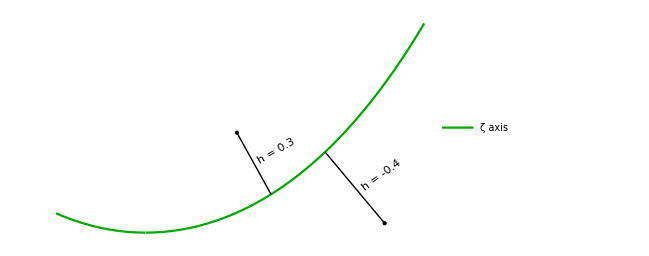

#### Code used to generate the figure

```mathematica
Block[
	{
		L = 2, Λ = 1, x0 = 0.4, l0,
		r = Function[{ζ, h}, {
			x0 + Λ ArcSinh[(ζ - l0)/Λ] - ((ζ - l0)/Λ)/(√(1  + ((ζ - l0) / Λ)^2)) h,
			Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2)) + 1/(√(1  + ((ζ - l0) / Λ)^2)) h
		}],
		ζ1 = 1, h1 = 0.3, ζ2 = 1.3, h2 = -0.4
	},
	l0 = Λ Sinh[x0/Λ];
	Legended[Show[{
		ParametricPlot[r[ζ, 0], {ζ, 0, L},
			PlotStyle -> {Darker@Green, Thick},
			Axes -> False
		],
		Graphics[{
			{Line[{r[ζ1, 0], r[ζ1, h1]}]},
			{PointSize[Large], Point[r[ζ1, h1]]},
			{Text[Rotate["h = " <> ToString@N@h1, π/6], (r[ζ1, 0] + r[ζ1, h1])/2 + {0.1, 0.05}]},
			{Line[{r[ζ2, 0], r[ζ2, h2]}]},
			{PointSize[Large], Point[r[ζ2, h2]]},
			{Text[Rotate["h = " <> ToString@N@h2, π/5], (r[ζ2, 0] + r[ζ2, h2])/2 + {0.12, 0.05}]}
		}]
	}, ImageSize -> 480], LineLegend[{Darker@Green}, {"ζ axis"}]]
]
```

-Graphics-

### Extending the notion of ζ

So far, we have only defined ζ along the cable’s equilibrium position. Having defined h, we can generalize the definition of ζ in the following way. Let us choose the value of ζ at each point so that the coordinates ζ, y, h were orthogonal,  so that the product of the basis vectors corresponding to the three coordinates was zero. To do that, let us take a point A on the ζ axis and draw through it a plane perpendicular to the ζ axis; to all the points on this plane not too far away from the ζ axis, let us assign the coordinate ζ= ζ_A.
	These coordinates are only sensible at some distance from the ζ-y  plane because the ζ axis is curved and the planes perpendicular to it do intersect at large enough distance, namely the radius of curvature of the ζ axis at that point. This means that the coordinates ζ, y, h cannot be used to coordinatize the entire space; but this is not a problem, because we are only interested in small oscillations.

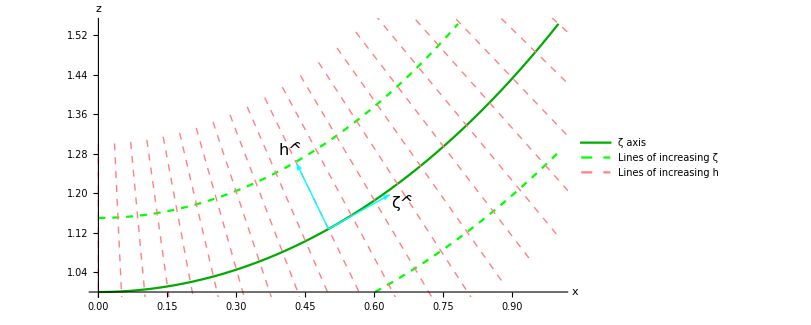

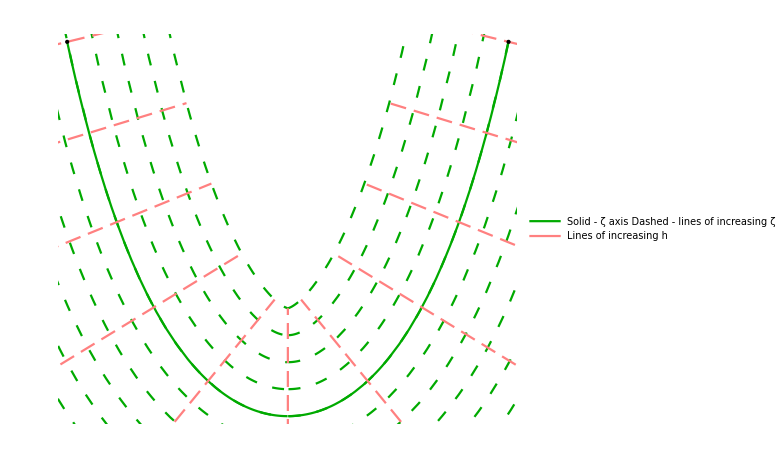

#### Code used to generate the illustrations

```mathematica
Legended[Show[{
	Plot[#& /@ {Cosh[1.1 x] + 0.15, Cosh[0.9 x] - 0.15}, {x, 0, 1}, PlotStyle -> {Green, Dashed},
			AspectRatio -> (Cosh[1] - Cosh[0])/(1 - 0), PlotRange -> {Cosh[0], Cosh[1]}, AxesLabel -> (Style[#, 20]& /@ {"x", "z"})
		],
	Plot[Cosh[x], {x, 0, 1}, PlotStyle -> {Thick, Darker @ Green}],
	Graphics@Table[
		With[{v = 0.3 {-Tanh[x], Sech[x]}},
			{Dashed, Pink, Line[
				{
					{x, Cosh[x]} + v,
					{x, Cosh[x]} - v
				}
			]}
		],
		{x, 0, 1, 0.05}
	],
	With[{x = 0.5, l = 0.15}, Graphics @ {
		{Thick, Cyan, Arrow[{{x, Cosh[x]}, {x, Cosh[x]} + l {-Tanh[x], Sech[x]}}]},
		{Thick, Cyan, Arrow[{{x, Cosh[x]}, {x, Cosh[x]} + l {Sech[x], Tanh[x]}}]},
		{Text[Style["h^̑", 16], {x, Cosh[x]} + 1.2 l {-Tanh[x], Sech[x]}]},
		{Text[Style["ζ^̑", 16], {x, Cosh[x]} + 1.2 l {Sech[x], Tanh[x]} - {0, 0.03}]}
	}]
}, ImageSize -> 600], LineLegend[{Darker@Green, {Green, Dashed}, {Dashed, Pink}}, {"ζ axis", "Lines of increasing ζ", "Lines of increasing h"}]]
```

-Graphics-

```mathematica
Block[
	{
		L = 2, xp = 1, zp = 0,
		Λ, x0, l0,
		xe, ze, ζbar, hbar,
		ζlines, hlines, ζ, h
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	l0 = Λ Sinh[x0 / Λ];

	xe = Function[ζ, x0 + Λ ArcSinh[(ζ - l0)/Λ]];
	ze = Function[ζ, Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2))];
	ζbar = Function[ζ, {1, (ζ - l0)/Λ}/(√(1 + (ζ - l0)^2/Λ^2))];
	hbar = Function[ζ, {-(ζ - l0)/Λ, 1}/(√(1 + (ζ - l0)^2/Λ^2))];
	
	ζlines = Plus[# hbar[ζ], {xe[ζ], ze[ζ]}]& /@ Range[-2Λ, Λ, Λ/4];
	hlines = Plus[h hbar[#], {xe[#], ze[#]}]& /@ Range[0, L, L/10];
	
	Legended[Show[{
		ParametricPlot[{xe[ζ], ze[ζ]},
			{ζ, 0, L},
			PlotStyle -> {Thick, Darker@Green},
		Axes -> False
		],
		ParametricPlot[ζlines,
			{ζ, -L, 2L},
			PlotStyle -> Array[{Thin, Dashing[{0.015, 0.02}], Darker@Green}&, Length@ζlines]
		],
		ParametricPlot[hlines,
			{h, -2Λ, Λ},
			PlotStyle -> Array[{Thin, Dashing[{0.02, 0.01}], Pink}&, Length@ζlines]
		],
		Graphics[{
			{PointSize[Large], Point[{0, 0}]},
			{PointSize[Large], Point[{xp, zp}]}
		}]
	}, ImageSize -> Large], LineLegend[{Darker@Green, Pink},
	{"Solid - ζ axis\nDashed - lines of increasing ζ", "Lines of increasing h"}]]
]
```

-Graphics-

### Explicit transformation formulas

From the formula for the position of a point on the ζ axis (30) and the conditions that ζ and h should be orthogonal and that the norm of the basis vector of h should be equal to 1, we can deduce the transformation formula from the coordinates ζ, h to x, z. The coordinate y is the same in both coordinate systems, so it does not transform. This formula will only be used a couple of times; most of the information about the coordinate system ζ, y, h will be deduced from the dot products of the basis vectors.

x[ζ, h] = x_0 + Λ ArcSinh[(ζ - l_0)/Λ] - ((ζ - l_0)/Λ)/(√(1  + ((ζ - l_0) / Λ)^2)) h
z[ζ, h] = Λ (√(1 + ((ζ - l_0)/Λ)^2) - √(1 + (l_0/Λ)^2)) + 1/(√(1  + ((ζ - l_0) / Λ)^2)) h

### Using ζ, h, and y to describe the rope’s shape

Now that we have defined ζ and h, we have the power too describe the rope’s shape using the functions y[t, ζ], h[t, ζ]. The meaning of these functions is that if a point lies on the rope and has some coordinate ζ, then its y and h coordinates are given by the functions y[t, ζ], h[t, ζ]. On the interactive illustration below, you see the sketch of the cable with a black point marked on it. All we need to describe the position of a point on the cable is its ζ coordinate, as y and h are functions of ζ.

#### Code used to generate the illustration

```mathematica
Manipulate[Block[
	{
		hbar = Function[x, Normalize[{-Sinh[x - 1/2], 0, 1}]],
		ybar = {0, 1, 0},
		pointOnζaxis = Function[x, {x, 0, Cosh[x - 1/2]}],
		xp = 5/3, X = 1/2 + ArcSinh[ζ - Sinh[1/2]],
		yfunc = Function[x, 0.13 Cos[(3π/2)/(xp/2)^2(x - xp/2)^2]],
		hfunc = Function[x, 0.1 Sin[4(2π)/xp x]]
	},
	Labeled[Column[{
		Show[
			{
				ParametricPlot3D[
					{
						pointOnζaxis[x],
						pointOnζaxis[x] + hfunc[x] hbar[x] + yfunc[x] ybar
					},
					{x, 0, xp},
					PlotStyle -> {{Dashing[0.05{0.7, 0.3}], Thick, Darker@Green}, {Thick, Darker@Orange}},
					AxesLabel -> (Style[#, 16]& /@ {"X", "Y", "Z"}),
					PlotLegends -> {"Cable's equilibrium (ζ axis)", "Cable's current configuration"}
				],
				Graphics3D[{
					{PointSize[Large], Point[pointOnζaxis[0]]},
					{PointSize[Large], Point[pointOnζaxis[xp]]},
					{PointSize[Large], Point[pointOnζaxis[X] + yfunc[X] ybar + hfunc[X] hbar[X]]}
				}]
			},
			PlotRange -> {{0, xp}, {-1/4, 0.7}, {3/4, Cosh[xp - 1/2] + 0.1}},
			ImageSize -> 300
		],
		(* ζ = Sinh[x - 1/2] + Sinh[1/2] -> x = 1/2 + ArcSinh[ζ - Sinh[1/2]] *)
		Row[{
			Plot[
				yfunc[1/2 + ArcSinh[ζ - Sinh[1/2]]],
				{ζ, 0, Sinh[xp - 1/2] + Sinh[1/2]},
				Epilog -> {{PointSize[Large], Point[{Sinh[X - 1/2] + Sinh[1/2], yfunc[X]}]}},
				PlotLabel -> "y[ζ]",
				ImageSize -> 200
			],
			Plot[
				hfunc[1/2 + ArcSinh[ζ - Sinh[1/2]]],
				{ζ, 0, Sinh[xp - 1/2] + Sinh[1/2]},
				Epilog -> {{PointSize[Large], Point[{Sinh[X - 1/2] + Sinh[1/2], hfunc[X]}]}},
				PlotLabel -> "h[ζ]",
				ImageSize -> 200
			]
		}]
	}], "The cable's shape can be represented with the help of functions y[ζ], h[ζ]"]
], {{ζ, 1}, 0, Sinh[5/3 - 1/2] + Sinh[1/2]}, ContinuousAction -> False, ControlType -> VerticalSlider]
```

## A note about domains of functions

The functions that are used when describing the oscillating cable can be split in three categories: those who describe the equilibrium, those who describe the motion of the cable, and those who describe the three-dimensional space itself; each of these groups has its own domain.

### Types of functions

#### Functions describing space (S)

These functions tell us the characteristics of the three-dimensional space in which the cable is moving; they exist completely independently of the cable’s motion. For instance, the basis vector ζ^̑ describes how ζ relates to the position vector of some point, but it does not give us any information about the cable’s motion. Functions of this category have the form q[ζ, y, h], and they do not depend on the cable’s shape. Because the coordinate system ζ, y, h doesn’t change with time, S functions also don’t depend on time.

#### Functions describing the rope’s motion (R)

These functions characterize the cable’s shape as a function of time. For instance, h[t, ζ] tells us the h coordinate of a point on the rope that has the coordinate ζ at time t. These functions are of the form q[t, ζ], and they are defined along the ζ axis. These are the variables contain all the information about the cable’s motion.

#### Functions describing the cable’s equilibrium (E)

These functions describe the cable’s equilibrium characteristics. An example of this is T_e[ζ], which tells us the tension at a point with coordinate ζ in the cable when it’s in equilibrium. Functions of this type only depend on ζ, and they are only defined along the ζ axis; they have the form q[ζ]. These functions just characterize the cable’s equilibrium and so they give us no information about the motion.

### When the functions mix

In this work, we will often be interested in what the values of certain S functions are when evaluated at some point on the rope. In other words, we would be interested more not in q[ζ, y, h] for arbitrary y and h but in q[ζ, y[t, ζ], h[t, ζ]], where y and h are functions of time and ζ. In this example, q ends up being a function of t and ζ, and the S-type function is turned into an R-type one. Let us denote

q[ζ, y[t, ζ], h[t,ζ]] ≡ q_r[t, ζ]

Here the subscript r means that q, which is by itself an S function, is evaluated along the rope and hence behaves as an R-type function. Similarly, we will be interested in S functions evaluated along the cable’s equilibrium position (or the ζ axis). We can use a similar notation for that:

q[ζ, 0, 0] ≡ q_e[ζ]

### Derivatives of q_e and q_r

Using the chain rule, we can compute the derivatives of (37) and (38).

((∂q_e)/(∂ζ)[ζ] = (∂q)/(∂ζ)|)_(ζ, 0, 0)

((∂q_r)/(∂ζ)[t, ζ] = (∂q)/(∂ζ) + (∂q)/(∂h)(∂h)/(∂ζ) + (∂q)/(∂y)(∂y)/(∂ζ)|)_(ζ, y[t, ζ], h[t, ζ])

With q_e, it seems pretty clear what’s going on. With q_r, however, things might look a bit strange: why are the formulas so different? It turns out that the answer is actually pretty intuitive.

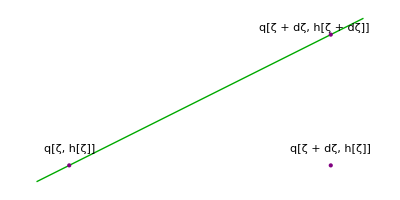

The picture above illustrates the formula (40) on the example of some function q[ζ, h]. Here the green line is the rope.

By definition, the partial derivative (∂q)/(∂ζ) ≡ (q[ζ + dζ, h] - q[ζ, h])/dζ. Basically, this is the difference between the value of q at the point ζ, h (the bottom left point) and at the point ζ + dζ, h (bottom right point) divided by dζ. On the other hand, dq_r/dζ ≡ (q[ζ + dζ, h[ζ + dζ]]  - q[ζ, h])/dζ. This is the difference between the value of q at the point ζ, h (the bottom left point) and at the point ζ + dζ, h + dζ (top right point) divided by dζ. We can see that there are some additional terms in dq_r/dζ because when calculating it, we differentiate q while staying on the rope, while when computing (∂q)/(∂ζ) we just go in the ζ^̑ direction.

#### Code used to generate the image

```mathematica
Graphics[{
	{Darker@Green, Thick, Line[{{0, 0}, {1, 0.5}}]},
	{Purple, PointSize[Large], Point[{0.1, 0.05}]},
	{Purple, PointSize[Large], Point[{0.9, 0.45}]},
	{Purple, PointSize[Large], Point[{0.9, 0.05}]},
	{Rotate[Text["q[ζ, h[ζ]]", {0.1, 0.1}], 0.4]},
	{Rotate[Text["q[ζ + dζ, h[ζ + dζ]]", {0.85, 0.47}], 0.4]},
	{Text["q[ζ + dζ, h[ζ]]", {0.9, 0.1}]}
}, GridLines -> Automatic, GridLinesStyle -> Directive[LightGray, Dashed]]
```

-Graphics-

## About basis vectors

### Definition of the basis vectors

The basis vectors associated with ζ, y, and h are defined as

ζ^̑ ≡ (∂r^–)/(∂ζ)
y^̑ ≡ (∂r^–)/(∂ζ)
h^̑ ≡ (∂r^–)/(∂h)

where r^– is the position vector of a point, which is the displacement of that point from the origin. Keep in mind that the length of ζ^̑ does not necessarily have to be equal to 1. (see next subsection) Also, because y is a Cartesian coordinate, its basis vector is constant:

y^̑ = const

### Norms of the basis vectors

Because y is a Cartesian coordinate, its basis vector has length 1:

y^̑ · y^̑ = 1

Since h is by definition a distance, its basis vector has norm 1 as well:

h^̑ · h^̑ = 1

Now, even though the norm of ζ^̑ is 1 at y = h = 0, in general it is a function of position:

ζ^̑ · ζ^̑ = f^2[ζ, h]
f[ζ, 0] = 1

Notice that I did not include y as an argument; this is because space is translationally symmetric with respect to y. As it will be shown in the subsection “Derivatives/Derivatives involving y”, if we treat f as a function of ζ, h, and y, we would find its y derivative to be zero, which means that f does not depend on y.

### Orthogonality of the basis vectors

Because the three basis vectors are always perpendicular to each other, their dot product is equal to zero at all points:

ζ^̑ · y^̑ = 0

y^̑ · h^̑ = 0

h^̑ · ζ^̑ = 0

## Derivatives

### Symmetry of the derivatives of the basis vectors

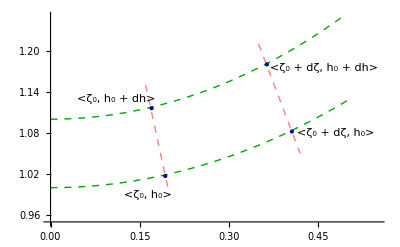
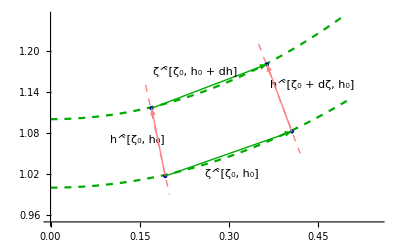

Let’s take a point with coordinates <ζ_0, h_0>; its position vector is r_0^– = r^–[ζ, h]. Now, let’s move by dζ in the ζ direction; the point we get is <ζ_0 + dζ, h_0>, and its position vector is r_1^– = r^–[ζ_0 + dζ, h]. Since dζ is very small, this can be re-written as (r^–)_1 = (r^–)_0 + (∂r^–)/(∂ζ)[ζ_0, h_0]dζ, or, using the definition (36) of ζ^̑ ≡ (∂r^–)/(∂ζ), (r^–)_1 = (r^–)_0 + ζ^̑[ζ_0, h_0]dζ. Now, let’s start from this point and move in the h direction by a distance dh to a point <ζ_0 + dζ, h_0 + dh>. The position vector of that point is (r^–)_2 = (r^–)_1 + (∂r^–)/(∂h)[ζ_0 + dζ, h]δh = (r^–)_1 + h^̑[ζ_0 + dζ, h_0]dh. Now we can re-write this using (∂h^̑)/(∂ζ) as r_2^– = (r^–)_1 + (h^̑[ζ_0, h_0] + (∂h^̑)/(∂ζ)dζ)dh, which is equivalent to (r^–)_2 = (r^–)_0 + ζ^̑[ζ_0, h_0]dζ + h^̑[ζ_0, h_0]dh + (∂h^̑)/(∂ζ) dζ dh. We can repeat these operations in a different order, first going in the h direction to the point (r^–)_3 = r^–[ζ_0, h_0 + dh] and then in the ζ direction to (r^–)_2 = r^–[ζ_0 + dζ, h_0 + dh], and we would get that (r^–)_2 = (r^–)_0 + ζ^̑[ζ_0, h_0]dζ + h^̑[ζ_0, h_0]dh + (∂ζ^̑)/(∂h) dh dζ. Comparing that to the previous formula for (r^–)_2, we get that (∂ζ^̑)/(∂h) = (∂h^̑)/(∂ζ). Repeating the same thing with the two other axes, we obtain the following relations.

(∂ζ^̑)/(∂h) = (∂h^̑)/(∂ζ)
(∂ζ^̑)/(∂y) = (∂y^̑)/(∂ζ)
(∂h^̑)/(∂y) = (∂y^̑)/(∂h)

This can also be proven from the very definition of the basis vectors (36) using the commutativity of partial derivatives. For example, (∂ζ^̑)/(∂h) ≡ ∂/(∂h)(∂r^–)/(∂ζ) and (∂h^̑)/(∂ζ) ≡ ∂/(∂ζ)(∂r^–)/(∂h). Using the fact that ∂/(∂h)(∂r^–)/(∂ζ) = ∂/(∂ζ)(∂r^–)/(∂h), we get that (∂ζ^̑)/(∂h) = (∂h^̑)/(∂ζ).

#### Code used to generate the figures

```mathematica
{Show[{
	Plot[#& /@ {Cosh[x], Cosh[1.1 x] + 0.1}, {x, 0, 0.5}, PlotStyle -> {Darker @ Green, Dashed, Thick}, PlotRange -> {{0, 0.55}, {0.95, 1.25}}],
	Graphics[{
		{Pink, Dashed, Thick, Line[{{0.16, 1.15}, {0.2, 0.99}}]},
		{Pink, Dashed, Thick, Line[{{0.35, 1.21}, {0.42, 1.05}}]},
		{PointSize[Large], Darker@Blue, Point[{0.17, 1.116}]},
		{PointSize[Large], Darker@Blue, Point[{0.193, 1.017}]},
		{PointSize[Large], Darker@Blue, Point[{0.364, 1.18}]},
		{PointSize[Large], Darker@Blue, Point[{0.406, 1.082}]},
		{Text["<ζ_0, h_0>", {0.163, 0.99}]},
		{Text["<ζ_0, h_0 + dh>", {0.11, 1.13}]},
		{Text["<ζ_0 + dζ, h_0>", {0.48, 1.08}]},
		{Text["<ζ_0 + dζ, h_0 + dh>", {0.46, 1.175}]}
	}]
}, ImageSize -> 400],
Show[{
	Plot[#& /@ {Cosh[x], Cosh[1.1 x] + 0.1}, {x, 0, 0.5}, PlotStyle -> {Darker @ Green, Dashed}, PlotRange -> {{0, 0.55}, {0.95, 1.25}}],
	Graphics[{
		{Pink, Dashed, Line[{{0.16, 1.15}, {0.2, 0.99}}]},
		{Pink, Dashed, Line[{{0.35, 1.21}, {0.42, 1.05}}]},
		{PointSize[Large], Darker@Blue, Point[{0.17, 1.116}]},
		{PointSize[Large], Darker@Blue, Point[{0.193, 1.017}]},
		{PointSize[Large], Darker@Blue, Point[{0.364, 1.18}]},
		{PointSize[Large], Darker@Blue, Point[{0.406, 1.082}]},
		{Thick, Pink, Arrow[{{0.193, 1.017}, {0.17, 1.116}}]},
		{Thick, Pink, Arrow[{{0.406, 1.082}, {0.364, 1.18}}]},
		{Thick, Darker@Green, Arrow[{{0.17, 1.116}, {0.364, 1.18}}]},
		{Thick, Darker@Green, Arrow[{{0.193, 1.017}, {0.406, 1.082}}]},
		{Rotate[Text["ζ^̑[ζ_0, h_0 + dh]", {0.244, 1.17}], 0.3]},
		{Rotate[Text["ζ^̑[ζ_0, h_0]", {0.305, 1.02}], 0.3]},
		{Rotate[Text["h^̑[ζ_0, h_0]", {0.146, 1.07}], 0.15]},
		{Rotate[Text["h^̑[ζ_0 + dζ, h_0]", {0.44, 1.15}], 0.3]}
	}]
}, ImageSize -> 400]}
```

{-Graphics-,-Graphics-}

### Derivatives involving y

Because y is a Cartesian coordinate, its basis vector is constant (37), and hence its derivatives are all zero.

(∂y^̑)/(∂ζ) = 0
(∂y^̑)/(∂y) = 0
(∂y^̑)/(∂h) = 0

Using (44), we also get that

(∂ζ^̑)/(∂y) = 0
(∂h^̑)/(∂y) = 0

Now, let’s prove that f does not depend on y. If we treat f as f[ζ, y, h], differentiating (40) with respect to y gives ζ^̑·(∂ζ^̑)/(∂y) = f(∂f)/(∂y). As we have just shown, (∂ζ^̑)/(∂y) = 0 (46), and so the statement is proven.

(∂f)/(∂y) = 0

### Finding (∂h^̑)/(∂ζ)

Taking the derivative of y^̑ · h^̑ = 0 (42) with respect to ζ, we get

y^̑ · (∂h^̑)/(∂ζ)  +(∂y^̑)/(∂ζ) · h^̑ = 0

According to (45), the second term is zero.

y^̑ · (∂h^̑)/(∂ζ)  = 0

This means that (∂h^̑)/(∂ζ) is orthogonal to y^̑. Differentiating (39) with respect to ζ tells us that (∂h^̑)/(∂ζ) is also orthogonal to h.

h^̑ · (∂h^̑)/(∂ζ) = 0

Since (∂h^̑)/(∂ζ) is orthogonal to both y^̑ and h^̑, it can only point in the ζ direction, e.g. it must be a multiple of ζ^̑: (∂h^̑)/(∂ζ) = W[ζ, y, h]. At this point we don’t know what W is; it is just some function. But just intuitively, W must have some relation to the curvature of coordinates - we can see that by drawing an osculating circle. And in fact, after doing the calculations, it turns out that W[ζ, y, h] = -k, where k is the signed curvature of the lines of constant y and h (see the subsection Why k is the signed curvature).

(∂h^̑)/(∂ζ) = -k[ζ, h] ζ^̑

We can treat k as a function of only ζ and h, but not y: k = k[ζ, h], and here is why. Taking the dot product of the above formula with ζ^̑, we get ζ^̑ · (∂h^̑)/(∂ζ) = -k f^2. If we now differentiate it with respect to y taking k to be k[ζ, y, h], we get the equation ∂/(∂y)(∂h^̑)/(∂ζ) = -(∂k)/(∂y)ζ^̑ - k (∂ζ^̑)/(∂y). Changing the order of partial derivatives on the left hand side and applying (46), we find that k does indeed not depend on y.

(∂k)/(∂y) = 0

It’s important to realize that what k in (48) tells us is not the cable’s curvature. k is a field defined in three dimensional space, and not just on the cable. k evaluated at a given point gives us how curly the lines of constant h are, and not how curly the cable is. k has no relation to the cable whatsoever and exists completely independently.

### Finding (∂ζ^̑)/(∂h)

Using (∂ζ^̑)/(∂h) = (∂h^̑)/(∂ζ) (44) and (∂h^̑)/(∂ζ) = -k[ζ, h] ζ^̑ (46), we get

(∂ζ^̑)/(∂h) = -k[ζ, h] ζ^̑

### Finding (∂h^̑)/(∂h)

Intuitively, it is pretty clear that (∂h^̑)/(∂h) = 0. To prove that, we will have to show that the dot product of (∂h^̑)/(∂h) with all three basis vectors is zero.

First, let us take the derivative of (39) with respect to h.

(∂h^̑)/(∂h) · h^̑ = 0

The first product is done. Now, differentiating (39) with respect to y and ζ gives

(∂h^̑)/(∂y) · h^̑ = 0
(∂h^̑)/(∂ζ) · h^̑ = 0

According to (44), this means that

(∂y^̑)/(∂h) · h^̑ = 0
(∂ζ^̑)/(∂h) · h^̑ = 0

Now, we can differentiate (42) and (43) with respect to h.

(∂h^̑)/(∂h) · y^̑ + (∂y^̑)/(∂h) · h^̑ = 0
(∂h^̑)/(∂h) · ζ^̑ + (∂ζ^̑)/(∂h) · h^̑ = 0

Substituting the previous result, we get

(∂h^̑)/(∂h) · y^̑ = 0
(∂h^̑)/(∂h) · ζ^̑ = 0

We have just shown that the dot product of (∂h^̑)/(∂h) with the three basis vectors are zero. This is only possible if (∂h^̑)/(∂h) = 0:

(∂h^̑)/(∂h) = 0

### Finding (∂f)/(∂h)

Differentiating (40) with respect to h, we get

ζ^̑ · (∂ζ^̑)/(∂h) = f (∂f)/(∂h)

Substituting (49) for (∂ζ^̑)/(∂h) gives

(∂f)/(∂h) = -k f

### Finding (∂k)/(∂h)

Differentiating (43) with respect to ζ, we  get

(∂ζ^̑)/(∂ζ) · h^̑ + ζ^̑ · (∂h^̑)/(∂ζ)= 0

Substituting (48) for (∂h^̑)/(∂ζ) gives

k f^2 = (∂ζ^̑)/(∂ζ) · h^̑

Now, we can differentiate this with respect to h:

(∂k)/(∂h)f^2 + k · 2 f(∂f)/(∂h)= ∂/(∂h)[(∂ζ^̑)/(∂ζ)]·h^̑ + (∂ζ^̑)/(∂ζ) · (∂h^̑)/(∂h)

After substituting (50) and (51), this becomes

(∂k)/(∂h)f^2 - 2 k^2 f^2= ∂/(∂h)[(∂ζ^̑)/(∂ζ)]·h^̑

We can exchange the order of partial derivatives:

(∂k)/(∂h)f^2 - 2 k^2 f^2= ∂/(∂ζ)[(∂ζ^̑)/(∂h)]·h^̑

According to (49), this equals

(∂k)/(∂h)f^2 - 2 k^2 f^2= (-(∂k)/(∂ζ) ζ^̑ - k(∂ζ^̑)/(∂ζ))·h^̑

Because ζ^̑ · h^̑ = 0 (43),

(∂k)/(∂h)f^2 - 2 k^2 f^2=  -k(∂ζ^̑)/(∂ζ)·h^̑

We know the value of (∂ζ^̑)/(∂ζ) · h^̑ from (52). Substituting, we get

(∂k)/(∂h) = k^2

### Finding k and f

The equation (54) is a separable differential equation. Solving it with the initial condition k[ζ, 0] = k_e[ζ] gives us the formula

k[ζ, h]= k_e[ζ]/(1 - k_e[ζ]h)

Substituting this into (51) and solving the ODE, we get the formula for f:

f[ζ, h] = f_e(1 - k_e[ζ] h)

According to (40), this equals

f[ζ, h] = 1 - k_e[ζ] h

### Finding (∂ζ^̑)/(∂ζ)

(∂ζ^̑)/(∂ζ), like any other vector, can be decomposed as (∂ζ^̑)/(∂ζ) = a ζ^̑ + b y^̑ + c h^̑. Let’s try to find the values of a, b, and c.

#### Finding a

Differentiating (40) with respect to ζ, we get

ζ^̑ · (∂ζ^̑)/(∂ζ) = f(∂f)/(∂ζ)

Substituting (∂ζ^̑)/(∂ζ) = a ζ^̑ + b y^̑ + c h^̑ and using (38) - (43) yields

a  = 1/f(∂f)/(∂ζ)

#### Finding b

Differentiating (41) with respect to ζ, we get

(∂ζ^̑)/(∂ζ) · y^̑ + ζ^̑ · (∂y^̑)/(∂ζ) = 0

Substituting (45),

(∂ζ^̑)/(∂ζ) · y^̑ = 0

Comparing this to (∂ζ^̑)/(∂ζ) = a ζ^̑ + b y^̑ + c h^̑, we get that

b = 0

#### Finding c

Differentiating (43) with respect to ζ, we find

h^̑·(∂ζ^̑)/(∂ζ) = -(∂h^̑)/(∂ζ)·ζ^̑

Substituting (48) gives

h^̑·(∂ζ^̑)/(∂ζ) = k f^2

Substituting (∂ζ^̑)/(∂ζ) = a ζ^̑ + b y^̑ + c h^̑ and (38) - (43) gives

c = k f^2

#### Putting things together

Substituting the values of a, b, and c we’ve found, we get

(∂ζ^̑)/(∂ζ) = 1/f(∂f)/(∂ζ) ζ^̑ + k f^2 h^̑

### Introducing the unit tangent vector to the rope

Let’s say there is a point with coordinates <ζ,y, h[ζ]> that lies on the cable. Now, let’s change ζ by some small value dζ, so that we are now at the point <ζ + dζ, y[ζ + dζ], h[ζ + dζ]>. By chain rule, the displacement vector is given as d r^– = ((∂r^–)/(∂ζ) + (∂r^–)/(∂y)(∂y)/(∂ζ) + (∂r^–)/(∂h)(∂h)/(∂ζ))dζ; by the definition of ζ^̑, y^̑, and h^̑ (36), this equals

δ r^– = ((ζ^̑)_r + (∂y)/(∂ζ)(y^̑)_r + (∂h)/(∂ζ)(h^̑)_r)dζ

where (ζ^̑)_r[t, ζ] is defined as ζ^̑[ζ, y[t, ζ], h[t, ζ]] (32). We can get the unit tangent vector by normalizing the displacement vector: l^– = (d r^–)/(√(dr^– · d r^–)). Using formulas (38) through (43), we get

l^– = ((ζ^̑)_r + (∂y)/(∂ζ)(y^̑)_r + (∂h)/(∂ζ)(h^̑)_r)/(√(f_r^2 + ((∂y)/(∂ζ))^2 + ((∂h)/(∂ζ))^2))

Because the cable is oscillating and bending, l^– would be a function of time as well as position: l^– = l^–[t, ζ]. There is no y or h in the arguments because l^– is only defined along the rope, and so y and h are determined by ζ. In other words, if we know that a point lies on the rope and we are given its ζ coordinate, we know that its coordinates y and h are given as y[t, ζ] and h[t, ζ], respectively.

### Why k is the signed curvature

Given a curve, we can parametrize it as (r^–)_c[s], where s is arc length and (r^–)_c is the position vector of a point at arc length equals s on the curve c. The signed curvature of this curve is then defined as (d^2(r^–)_c)/ds^2. Let us examine curves parametrized in terms of s as y = y_c = const, h = h_c = const, ζ = ζ_c[s].
	By chain rule, (d(r^-)_c)/ds = (∂r^–)/(∂ζ)dζ_c/ds + (∂r^–)/(∂y)dy_c/ds + (∂r^–)/(∂h)dh_c/ds, where the partial derivatives (∂r^–)/(∂ζ), (∂r^–)/(∂y), (∂r^–)/(∂h) are evaluated at the point (r^–)_c[s]. Because y_c = const, h_c = const, we have dy_c/ds = dh_c/ds = 0, and the formula becomes (d(r^–)_c)/ds = (∂r^–)/(∂ζ)dζ_c/ds. By the definition of the basis vector ζ^̑ ≡ (∂r^–)/(∂ζ) (36), we have (d(r^–)_c)/ds = (ζ^̑)_c dζ_c/ds, where the subscript (ζ^̑)_c indicates that (ζ^̑)_c[s] = ζ^̑[ζ_c[s], h_c]. This can be re-written as (d(r^–)_c)/ds = (ζ^̑)_c/ds/dζ. Here ds/dζ tells us how much arc length we cover if we move a distance dζ along the curve c, in other words - the norm of (ζ^̑)_c, which equals f_c (40), where f_c indicates that f is evaluated on c: f_c[s] ≡ f[ζ_c[s], h_c]. Another way to see that is that since the unit tangent vector has norm 1 and (d(r^–)_c)/ds is precisely the unit tangent vector, then it must have norm 1. Equating the norm of (ζ^̑)_c/ds/dζ to 1 keeping in mind that the norm of ζ^̑ is by definition f (40), we get that ds_c/dζ = f_c.

(d(r^–)_c)/ds = (ζ^̑)_c/f_c

Curvature is defined as the derivative of the unit tangent vector with respect to arc length s. By chain rule,  d/ds(d(r^–)_c)/ds = dζ_c/ds d/dζ(d(r^–)_c)/ds = 1/f_c d/dζ(d(r^–)_c)/ds.

(d^2(r^–)_c)/ds^2 = 1/f_c d/dζ[1/f_c(ζ^̑)_c] = 1/f_c^2(d(ζ^̑)_c)/dζ - 1/f_c^3 df_c/dζ(ζ^̑)_c

(d(ζ^̑)_c)/dζ tell us how fast ζ^̑ changes with respect to the coordinate ζ when we move along the curve s. And because s is a curve of constant y and h, (d(ζ^̑)_c)/dζ tells us how fast ζ^̑ changes with respect to ζ while we keep y and h fixed, which is by definition the partial derivative (∂ζ^̑)/(∂ζ). Substituting (57) for (∂ζ^̑)/(∂ζ), we get

((d^2(r^–)_c)/ds^2 = 1/f_c^2(1/f(∂f)/(∂ζ) ζ^̑ + k f^2 h^̑)|)_((r^–)_c[s]) - 1/f_c^3 df_c/dζ(ζ^̑)_c

Because we are investigating a curve on which y = const, h = const, the derivative df_c/dζ along this curve gives us the rate of change of f as we increase ζ while keeping y and h fixed, which is by definition the partial derivative (∂f)/(∂ζ). Cancelling the like terms, we obtain

(d^2(r^–)_c)/ds^2 = k  h^̑

Because (h^̑)^2 = 1 (39), this tells us that indeed, k measures the curvature of the lines of constant y and h.

### Numerical check

We can check the formulas derived in this section numerically.

```mathematica
Options[ND] = {"ε" -> 10^(-32), "Precision" -> 120};
ND[f_, OptionsPattern[]] := N[(f[OptionValue["ε"]] - f[0])/OptionValue["ε"], OptionValue["Precision"]];
```

The function ND computes the numerical derivative of a function near zero: ND[f] ≡ (f[ε] - f[0])/ε. Here are some examples:

```mathematica
ND@Cos
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 100000000000000000000000000000000 (-1+Cos[1/100000000000000000000000000000000]).

-4.99999999999999999999999999999999999999999999999999999999999999995833333333333333333333333333333333333333×10^-33

```mathematica
ND@Sin
```

0.999999999999999999999999999999999999999999999999999999999999999983333333333333333333333333333333333333333333333333333333

```mathematica
ND@Function[δ, Sqrt[1 + δ]]
```

0.4999999999999999999999999999999987500000000000000000000000000000062499999999999999999999999999999609375

As you can see, there is some numerical error. The piece of code below compares the values of some functions as calculated directly from their definitions to what was predicted by the formulas derived in this section. It starts with the position vector r^– ≡ <x, y, z> as expressed in terms of ζ, y, and h. It then computes ζ^̑, y^̑ and h^̑ from their definition (36), and from here supplementary quantities, namely f, k, and l^–, can be calculated.
For generality, I chose the case when f_e does not always equal 1 but instead varies with ζ. Also, because time dependence is not important in the formulas from this section, I decided to only look at a particular instant, such that h and y are only functions of ζ but not t.
The formulas are tested in the following way. For scalar quantities, the quantity is first computed directly from its definition and then from the corresponding formula, and the results are then displayed one below another, so that we could count to what digit do the two answers correspond. With vector quantities the process is very similar, except that since there are three numbers in each vector, each vector comparison compares three pairs of numbers.

```mathematica
$MaxExtraPrecision = 120;
Block[
	{
		ζaxis,
		yfunc, hfunc, f, k, ropef, ropek, fe, ke, r,
		ζbar, ybar, hbar, lbar,
		ropeζbar, ropeybar, ropehbar, ropelbar,
		prec = 120, sp
	},
	sp = Function[x, SetPrecision[x, prec]];
	
	ζaxis = Function[ζ, {ζ^3, 0, Cos[ζ]}];
	(* returns the <x, y, z> coordinates of a point with coordinate ζ on the ζ axis *)
	
	r = Function[{ζ, y, h}, SetPrecision[ζaxis[ζ] + {0, y, 0} + h Normalize[({{0, 0, -1}, {0, 0, 0}, {1, 0, 0}}) . ζaxis'[ζ]], prec]];
	(* returns the <x, y, z> coordinates of a point with coordinates ζ, y, h *)
	
	yfunc = Function[ζ, Sin[ζ^2]];  (* returns the y coordinate of a point on the rope with coordinate ζ *)
	hfunc = Function[ζ, Cos[ζ]^3];  (* returns the h coordinate of a point on the rope with coordinate ζ *)
	
	ζbar = Function[{ζ, y, h}, ND@Function[δ, r[ζ + δ, y, h]]];  (* returns the <x, y, z> components of ζ^̑ at a point with coordiantes ζ, y, h *)
	ybar = Function[{ζ, y, h}, ND@Function[δ, r[ζ, y + δ, h]]];  (* returns the <x, y, z> components of y^̑ at a point with coordiantes ζ, y, h *)
	hbar = Function[{ζ, y, h}, ND@Function[δ, r[ζ, y, h + δ]]];  (* returns the <x, y, z> components of h^̑ at a point with coordiantes ζ, y, h *)
	
	ropeζbar = Function[ζ, ζbar[ζ, yfunc[ζ], hfunc[ζ]]];  (* returns the <x, y, z> components of ζ^̑ at a point with coordiante ζ that lies on the rope *)
	ropeybar = Function[ζ, ybar[ζ, yfunc[ζ], hfunc[ζ]]];  (* returns the <x, y, z> components of y^̑ at a point with coordiante ζ that lies on the rope *)
	ropehbar = Function[ζ, hbar[ζ, yfunc[ζ], hfunc[ζ]]];  (* returns the <x, y, z> components of h^̑ at a point with coordiante ζ that lies on the rope *)
	
	f = Function[{ζ, y, h}, Norm@ζbar[ζ, y, h]];  (* returns the value of f at a point with coordinates ζ, y, h *)
	k = Function[{ζ, y, h}, ((ND@Function[δ, ζbar[ζ + δ, y, h]]) . hbar[ζ, y, h])/f[ζ, y, h]^2];  (* returns the value of k at a point with coordinates ζ, y, h *)
	
	ropef = Function[ζ, f[ζ, yfunc[ζ], hfunc[ζ]]];  (* returns the value of f at a point with coordinate ζ on the rope *)
	ropek = Function[ζ, k[ζ, yfunc[ζ], hfunc[ζ]]];  (* returns the value of k at a point with coordinate ζ on the rope *)
	
	fe = Function[ζ, f[ζ, sp@0, sp@0]];
	ke = Function[ζ, k[ζ, sp@0, sp@0]];
	
	lbar = Function[ζ, Normalize@ND@Function[δ, r[ζ + δ, yfunc[ζ + δ], hfunc[ζ + δ]]]];
	(* returns the <x, y, z> components of l^– at a point with coordinate ζ on the rope *)
	
	With[{ζ = sp@3, y = sp@3, h = sp@4},
		Print["(∂OverscriptBox[y, ̑])/(∂ζ) = ", ND@Function[δ, ybar[ζ + δ, y, h]]];
		Print["(∂OverscriptBox[y, ̑])/(∂y) = ", ND@Function[δ, ybar[ζ, y + δ, h]]];
		Print["(∂OverscriptBox[y, ̑])/(∂h) = ", ND@Function[δ, ybar[ζ, y, h + δ]]];
		Print["(∂OverscriptBox[h, ̑])/(∂h) = ", ND@Function[δ, hbar[ζ, y, h + δ]]];
		Print["(∂OverscriptBox[h, ̑])/(∂y) = ", ND@Function[δ, hbar[ζ, y + δ, h]]];
		Print["(∂OverscriptBox[ζ, ̑])/(∂y) = ", ND@Function[δ, ζbar[ζ, y + δ, h]]];
		Print[];
		
		Print["-k ζ^̑ = (∂OverscriptBox[h, ̑])/(∂ζ) = (∂OverscriptBox[ζ, ̑])/(∂h)"];
		Print[Column[#]]& /@ Transpose@{
			-k[ζ, y, h] ζbar[ζ, y, h],
			ND@Function[δ, hbar[ζ + δ, y, h]], ND@Function[δ, ζbar[ζ, y, h + δ]]
		};
		Print[];
		
		Print["(∂OverscriptBox[ζ, ̑])/(∂ζ) = 1/f(∂f)/(∂ζ) ζ^̑ + k f^2 h^̑"];
		Print[Column[#]]& /@ Transpose@{
			ND@Function[δ, ζbar[ζ + δ, y, h]],
			(ND@Function[δ, f[ζ + δ, y, h]])/f[ζ, y, h] ζbar[ζ, y, h] + k[ζ, y, h] f[ζ, y, h]^2 hbar[ζ, y, h]
		};
		Print[];
		
		Print["l^̑ = ζ^̑/(√(f^2))"];
		Print[Column[#]]& /@ Transpose@{
			lbar[ζ],
			(ropeζbar[ζ] + ND@Function[δ, yfunc[ζ + δ]] ropeybar[ζ] + ND@Function[δ, hfunc[ζ + δ]] ropehbar[ζ])/Sqrt[ropef[ζ]^2 + ND[Function[δ, yfunc[ζ + δ]]]^2 + ND[Function[δ, hfunc[ζ + δ]]]^2]
		};
		Print[];
		
		Print["f = f_e(1 - k_eh)"];
		Print[Column@{f[ζ, y, h], fe[ζ] (1 - ke[ζ] h)}];
		Print[];
		
		Print["k = k_e/(1  -  SubscriptBox[k, e] h)"];
		Print[Column@{k[ζ, y, h], ke[ζ]/(1 - ke[ζ]h)}];
		Print[];
	];
];
$MaxExtraPrecision = 50;
```

(∂OverscriptBox[y, ̑])/(∂ζ) = {0.,0.,0.}

(∂OverscriptBox[y, ̑])/(∂y) = {0.,0.,0.}

(∂OverscriptBox[y, ̑])/(∂h) = {0.,0.,0.}

(∂OverscriptBox[h, ̑])/(∂h) = {0.,0.,0.}

(∂OverscriptBox[h, ̑])/(∂y) = {0.,0.,0.}

(∂OverscriptBox[ζ, ̑])/(∂y) = {0.,0.,0.}

-k ζ^̑ = (∂OverscriptBox[h, ̑])/(∂ζ) = (∂OverscriptBox[ζ, ̑])/(∂h)

-0.0401491881990477665613333749499781256842901916331268332
-0.04014918819904776656133337494997795332484137856381478
-0.04014918819904776656133337494997795332484137856381478

0.
0.
0.

0.000209846435638768399133129379294740458862982733175725384
0.000209846435638768399133129379294739557997545485227087
0.000209846435638768399133129379294739557997545485227087

(∂OverscriptBox[ζ, ̑])/(∂ζ) = 1/f(∂f)/(∂ζ) ζ^̑ + k f^2 h^̑

18.18847635336158506949876775969183562047722789302224984
18.18847635336158506949876775969183607220705591654455

0.
0.

0.982559300003478851494553306151263128904776395874658743
0.982559300003478851494553306151266776825461280622892149

l^̑ = ζ^̑/(√(f^2))

0.979964966899926079969926960209013385069537761111794749342581865457714186737618356156427
0.97996496689992607996992696020901338193099746266871904044498658214448792715278772013854

-0.198146857786232632692082567947488631439445221237420303262365444717151773333377206673383
-0.19814685778623263269208256794748863202574581217212780106318799117844369764547218209892

-0.0201615078371951827074929348639213745585874094951036650406868103325667885563509023519163
-0.020161507837195182707492934863921374586684143225098703284738110348336819797728525437273

f = f_e(1 - k_eh)

26.83976984474740416176553623676060408997451994734124924901160488307647486798610323013
26.8397698447474041617655362367606034270537264572754073535

k = k_e/(1  -  SubscriptBox[k, e] h)

0.00149590465291848848344938067121483050461750663819414697
0.001495904652918488483449380671214830294483872131986875806

As you can see, the error is always very small, around 10^-30. Thus, we conclude that the formulas are indeed correct.

## First-order Taylor approximations

### The general principle

Let’s say we have a function q = q[ζ, y, h], and we are interested in its value near y = 0, h = 0. Taylor's theorem tells us that the first-order approximation of this function is

q[ζ, y, h] ≈ q[ζ, 0, 0] + (∂q)/(∂y)[ζ, 0, 0] y + (∂q)/(∂h)[ζ, 0, 0] h

### Some formulas

Source: (55)

k[ζ, h] = k_e[ζ](1 + k_e[ζ]h)

Source: (40), (55), (56), (57)

(∂ζ^̑)/(∂ζ) = (1/f_e(∂f_e)/(∂ζ) - (∂k_e)/(∂ζ)h) ζ^̑ + k_e f_e^2(1 - k_e h) h^̑ = -(∂k_e)/(∂ζ)h ζ^̑ + k_e(1 - k_e h) h^̑

Source: (35), (40), (49), (60)

(∂(ζ^̑)_r)/(∂ζ) = 1/f_e(∂f_e)/(∂ζ)(ζ^̑)_r + k_e f_e^2(h^̑)_r - ∂/(∂ζ)[k_e h](ζ^̑)_r - k_e^2 f_e^2 h (h^̑)_r = k_e(h^̑)_r - ∂/(∂ζ)[k_e h](ζ^̑)_r - k_e^2 h (h^̑)_r

Source: (35), (48), (54)

(∂(h^̑)_r)/(∂ζ) = -k (ζ^̑)_r = -k_e(1 + k_e h)(ζ^̑)_r

Source: (35), (45)

(∂(y^̑)_r)/(∂ζ) = 0

Source: (35), (40), (56)

∂/(∂ζ)[1/f_r] = -1/f_e^2(∂f_e)/(∂ζ) + ∂/(∂ζ)[k_e/f_e h] = ∂/(∂ζ)[k_e h]

### About l^–

Because (∂y)/(∂ζ) << f and (∂h)/(∂ζ) << f, we can re-write (58) as

l^– = 1/f_r((ζ^̑)_r + (∂y)/(∂ζ)(y^̑)_r + (∂h)/(∂ζ)(h^̑)_r)

Differentiating this with respect to ζ, we get

(∂l^–)/(∂ζ) = ∂/(∂ζ)[1/f_r]((ζ^̑)_r + (∂y)/(∂ζ)(y^̑)_r + (∂h)/(∂ζ)(h^̑)_r) + 1/f_r((∂ζ_r^̑)/(∂ζ) + (∂^2 y)/(∂ζ^2)(y^̑)_r + (∂y)/(∂ζ)(∂(y^̑)_r)/(∂ζ) + (∂^2 h)/(∂ζ^2)(h^̑)_r + (∂h)/(∂ζ)(∂(h^̑)_r)/(∂ζ))

After substituting the formulas (59) through (64) and neglecting the quadratic terms, this becomes

(∂l^–)/(∂ζ) = k_e f_e(h^̑)_r +  ∂/(∂ζ)[1/f_e(∂y)/(∂ζ)](y^̑)_r + ∂/(∂ζ)[1/f_e(∂h)/(∂ζ)](h^̑)_r - k_e/f_e(∂h)/(∂ζ)(ζ^̑)_r = k_e(h^̑)_r + (∂^2 y)/(∂ζ^2)(y^̑)_r + (∂^2 h)/(∂ζ^2)(h^̑)_r - k_e(∂h)/(∂ζ)(ζ^̑)_r

This is the formula for (∂l^–)/(∂ζ). We can also take the first-order approximation of l^– = 1/f_r((ζ^̑)_r + (∂y)/(∂ζ)(y^̑)_r + (∂h)/(∂ζ)(h^̑)_r), and what we get is

l^– = 1/f_e(ζ^̑)_r + k_e/f_e h(ζ^̑)_r + 1/f_e(∂y)/(∂ζ)(y^̑)_r + 1/f_e(∂h)/(∂ζ)(h^̑)_r = (ζ^̑)_r + k_e h(ζ^̑)_r + (∂y)/(∂ζ)(y^̑)_r + (∂h)/(∂ζ)(h^̑)_r

Using the definition of T^– (8) and the product rule, we can write

(∂T^–)/(∂ζ) = (∂T)/(∂ζ)l^– + T(∂l^–)/(∂ζ)

Using the formulas (65) and (66) and the fact that T = T_e + O[ε] and then neglecting quadratic terms, we arrive at the following formula.

(∂T^–)/(∂ζ) = k_e T f_e(h^̑)_r + 1/f_e(∂T)/(∂ζ)(ζ^̑)_r + k_e/f_e((∂T_e)/(∂ζ)h - T_e(∂h)/(∂ζ))(ζ^̑)_r + ∂/(∂ζ)[T_e/f_e(∂y)/(∂ζ)](y^̑)_r + ∂/(∂ζ)[T_e/f_e(∂h)/(∂ζ)](h^̑)_r =
   = k_e T (h^̑)_r + (∂T)/(∂ζ)(ζ^̑)_r + k_e((∂T_e)/(∂ζ)h - T_e(∂h)/(∂ζ))(ζ^̑)_r + ∂/(∂ζ)[T_e(∂y)/(∂ζ)](y^̑)_r + ∂/(∂ζ)[T_e(∂h)/(∂ζ)](h^̑)_r

### Numerical check

The formulas derived above are first-order approximations, and so their error will be proportional to h^2. If we denote E_i the error of the i-th formula, then we know that E_i ∝ h^2, and so lg[E_i] = 2 lg[h] + const. If the Taylor expansion of E has nonzero zeroth or first-order terms, we say that it’s wrong.
This criterion can be used to validate the formulas. We can compute E for the formulas for some values of h and plot them on the logarithmic scale. If the plot looks like a line with slope 2, then everything’s right, and if it doesn’t, then something’s wrong. Error can be computed by subtracting the right hand side from the left hand side of the formula and taking the absolute value of the result. Of course, this numerical estimate will have some error in it as well due to the computer’s limited accuracy, however, as we have seen in the previous numerical check, this error is of order 10^-30, and we can choose h to be big enough that the error due to the quadratic approximation would be much larger than that.

Because y and h are actually functions of position, we can do the following thing. Instead of changing y[ζ] and h[ζ] by themselves, we can say that y[ζ] = Y[ζ] ε, h[ζ] = H[ζ] ε, where Y[ζ] and H[ζ] are some functions of order 1 (in this case, I’ve taken H = Sin[ζ^2], Y = Cos[ζ]^3, and ε is some small constant. The idea is that we can set ε to be, for example, 0.01, then calculate the error in the formulas with this value of ε, change ε to some other value, and repeat the process as many times as needed. In this case, ε serves as a scaling factor.
	Also, because the formulas being checked do not assume any particular shape of the ζ axis as long as it remains in the y = 0 plane, it can be chosen arbitrarily. In the example below, I’ve chosen it so that a point on the ζ axis has Cartesian coordinates x = ζ^3, y = 0, z = Cos[ζ].

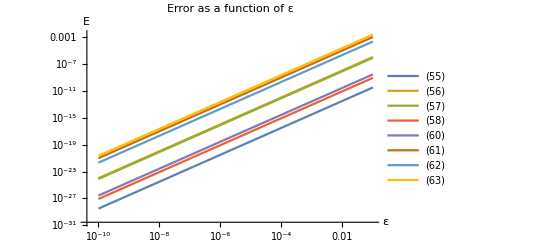

The plot shows the error (defined as |LeftHandSide - RightHandSide|) of the formulas derived in this section. As you can see, all the formulas have a nice quadratic dependence of error on ε. Thus, we can say that they are correct to the first order.

#### Code used to generate the figure

```mathematica
$MaxExtraPrecision = 120;
Block[
	{
		ζaxis,
		yfunc, hfunc, f, k, ropef, ropek, fe, ke, r, T, Te,
		ζbar, ybar, hbar, lbar,
		ropeζbar, ropeybar, ropehbar, ropelbar,
		prec = 120, sp,
		errf, εlist, errlist
	},
	sp = Function[x, SetPrecision[x, prec]];
	
	ζaxis = Function[ζ, {ζ^3, 0, Cos[ζ]}];
	r = Function[{ζ, y, h}, SetPrecision[ζaxis[ζ] + {0, y, 0} + h Normalize[({{0, 0, -1}, {0, 0, 0}, {1, 0, 0}}) . ζaxis'[ζ]], prec]];
	yfunc = Function[{ζ, ε}, ε sp@Sin[ζ^2]];
	hfunc = Function[{ζ, ε}, ε sp@Cos[ζ]^3];
	
	ζbar = Function[{ζ, y, h}, ND@Function[δ, r[ζ + δ, y, h]]];
	ybar = Function[{ζ, y, h}, ND@Function[δ, r[ζ, y + δ, h]]];
	hbar = Function[{ζ, y, h}, ND@Function[δ, r[ζ, y, h + δ]]];
	
	ropeζbar = Function[{ζ, ε}, ζbar[ζ, yfunc[ζ, ε], hfunc[ζ, ε]]];
	ropeybar = Function[{ζ, ε}, ybar[ζ, yfunc[ζ, ε], hfunc[ζ, ε]]];
	ropehbar = Function[{ζ, ε}, hbar[ζ, yfunc[ζ, ε], hfunc[ζ, ε]]];
	
	f = Function[{ζ, y, h}, Norm@ζbar[ζ, y, h]];
	k = Function[{ζ, y, h}, ((ND@Function[δ, ζbar[ζ + δ, y, h]]) . hbar[ζ, y, h])/f[ζ, y, h]^2];
	
	ropef = Function[{ζ, ε}, f[ζ, yfunc[ζ, ε], hfunc[ζ, ε]]];
	ropek = Function[{ζ, ε}, k[ζ, yfunc[ζ, ε], hfunc[ζ, ε]]];
	
	fe = Function[ζ, f[ζ, sp@0, sp@0]];
	ke = Function[ζ, k[ζ, sp@0, sp@0]];
	
	lbar = Function[{ζ, ε}, Normalize@ND@Function[δ, r[ζ + δ, yfunc[ζ + δ, ε], hfunc[ζ + δ, ε]]]];
	
	Te = Function[ζ, Sqrt[ζ]];
	T = Function[{ζ, ε}, Te[ζ] + ε Sin[ζ]];
	
	errf = Function[{ζ, ε},
		If[SameQ[Head[#], List],  (* returns |LHS - RHS| *)
			Norm[#[[1]] - #[[2]]],
			Abs[#[[1]] - #[[2]]]
		]& /@ {
			{ (* k = Subscript[k, e](1 + Subscript[k, e] h) *)
				k[ζ, yfunc[ζ, ε], hfunc[ζ, ε]],
				ke[ζ](1 + ke[ζ] hfunc[ζ, ε])
			},
			{ (* (∂ζ^̑)/(∂ζ) = (1/Subscript[f, e](∂Subscript[f, e])/(∂ζ) - (∂Subscript[k, e])/(∂ζ)h) ζ^̑ + Subscript[k, e] Subscript[f, e]^2(1 - Subscript[k, e] h) h^̑  *)
				ND@Function[δ, ζbar[ζ + δ, yfunc[ζ, ε], hfunc[ζ, ε]]],
				((ND@Function[δ, fe[ζ + δ]])/fe[ζ] - ND@Function[δ, ke[ζ + δ]] hfunc[ζ, ε])ropeζbar[ζ, ε]+
				ke[ζ] fe[ζ]^2 (1 - ke[ζ] hfunc[ζ, ε]) ropehbar[ζ, ε]
			},
			{ (* (∂Subscript[ζ^̑, r])/(∂ζ) = 1/Subscript[f, e](∂Subscript[f, e])/(∂ζ)Subscript[ζ^̑, r] + Subscript[k, e] Subscript[f, e]^2 Subscript[h^̑, r] - ∂/(∂ζ)[Subscript[k, e] h] Subscript[ζ^̑, r] - Subscript[k, e]^2 Subscript[f, e]^2 h Subscript[h^̑, r] *)
				ND@Function[δ, ropeζbar[ζ + δ, ε]],
				((ND@Function[δ, fe[ζ + δ]])/fe[ζ] - ND@Function[δ, ke[ζ + δ] hfunc[ζ + δ, ε]])ropeζbar[ζ, ε]+
				ke[ζ] fe[ζ]^2 (1 - ke[ζ] hfunc[ζ, ε]) ropehbar[ζ, ε]
			},
			{ (* (∂Subscript[h^̑, r])/(∂ζ) = -Subscript[k, e](1 + Subscript[k, e] h) Subscript[ζ^̑, r] *)
				ND@Function[δ, ropehbar[ζ + δ, ε]],
				-ke[ζ] (1 + ke[ζ] hfunc[ζ, ε]) ropeζbar[ζ, ε]
			},
			{ (* ∂/(∂ζ)[1/Subscript[f, r]] = -1/Subscript[f, e]^2(∂Subscript[f, e])/(∂ζ) + ∂/(∂ζ)[Subscript[k, e]/Subscript[f, e] h] = ∂/(∂ζ)[Subscript[k, e] h] *)
				ND@Function[δ, 1/ropef[ζ + δ, ε]],
				-(ND@Function[δ, fe[ζ + δ]])/fe[ζ]^2 + ND@Function[δ, ke[ζ + δ]/fe[ζ + δ] hfunc[ζ + δ, ε]]
			},
			{ (* (∂l^–)/(∂ζ) = Subscript[k, e] Subscript[f, e] Subscript[h^̑, r] + ∂/(∂ζ)[1/Subscript[f, e](∂y)/(∂ζ)] Subscript[y^̑, r] + ∂/(∂ζ)[1/Subscript[f, e](∂h)/(∂ζ)] Subscript[h^̑, r] + Subscript[k, e]/Subscript[f, e](∂h)/(∂ζ) Subscript[ζ^̑, r] *)
				ND@Function[δ, lbar[ζ + δ, ε]],
			
				ke[ζ] fe[ζ] ropehbar[ζ, ε]+
				ND@Function[δ, (ND@Function[Δ, yfunc[ζ + δ + Δ, ε]])/fe[ζ + δ]] ropeybar[ζ, ε]+
				ND@Function[δ, (ND@Function[Δ, hfunc[ζ + δ + Δ, ε]])/fe[ζ + δ]] ropehbar[ζ, ε]-
				ke[ζ]/fe[ζ] ND@Function[δ, hfunc[ζ + δ, ε]] ropeζbar[ζ, ε]
			},
			{ (* l^– = 1/Subscript[f, e] Subscript[ζ^̑, r] + Subscript[k, e]/Subscript[f, e] h Subscript[ζ^̑, r] + 1/Subscript[f, e](∂y)/(∂ζ)Subscript[y^̑, r] + 1/Subscript[f, e](∂h)/(∂ζ)Subscript[h^̑, r] *)
				lbar[ζ, ε],
				1/fe[ζ] ropeζbar[ζ, ε]+
				ke[ζ]/fe[ζ] hfunc[ζ, ε] ropeζbar[ζ, ε]+
				1/fe[ζ] ND@Function[δ, yfunc[ζ + δ, ε]] ropeybar[ζ, ε]+
				1/fe[ζ] ND@Function[δ, hfunc[ζ + δ, ε]] ropehbar[ζ, ε]
			},
			{ (* (∂T^–)/(∂ζ) = Subscript[k, e] Subscript[Tf, e] Subscript[h^̑, r] + 1/Subscript[f, e](∂T)/(∂ζ)Subscript[ζ^̑, r] + Subscript[k, e]/Subscript[f, e]((∂Subscript[T, e])/(∂ζ)h - Subscript[T, e](∂h)/(∂ζ))Subscript[ζ^̑, r] + ∂/(∂ζ)[Subscript[T, e]/Subscript[f, e](∂y)/(∂ζ)] Subscript[y^̑, r] + ∂/(∂ζ)[Subscript[T, e]/Subscript[f, e](∂h)/(∂ζ)] Subscript[y^̑, h] *)
				ND@Function[δ, T[ζ + δ, ε]lbar[ζ + δ, ε]],
				ke[ζ] T[ζ, ε] fe[ζ] ropehbar[ζ, ε]+
				1/fe[ζ] ND@Function[δ, T[ζ + δ, ε]] ropeζbar[ζ, ε]+
				ke[ζ]/fe[ζ](ND@Function[δ, Te[ζ + δ]] hfunc[ζ, ε] - Te[ζ] ND@Function[δ, hfunc[ζ + δ, ε]]) ropeζbar[ζ, ε]+
				ND@Function[δ, Te[ζ + δ]/fe[ζ + δ] ND@Function[Δ, yfunc[ζ + δ + Δ, ε]]] ropeybar[ζ, ε]+
				ND@Function[δ, Te[ζ + δ]/fe[ζ + δ] ND@Function[Δ, hfunc[ζ + δ + Δ, ε]]] ropehbar[ζ, ε]
			}
	}];
	
	εlist = (10^(-#))& /@ Range[10];
	errlist = Transpose[errf[sp@3, #]& /@ εlist];
	ListLogLogPlot[
		Table[
			Transpose @ {
				εlist,
				errlist[[i]]
			},
			{i, Length@errlist}
		],
		PlotRange -> All,
		Joined -> True,
		AxesLabel -> {"ε", "E"},
		PlotLabel -> "Error as a function of ε",
		PlotLegends -> {"(55)", "(56)", "(57)", "(58)", "(60)", "(61)", "(62)", "(63)"}
	]
]
$MaxExtraPrecision = 50;
```

-Graphics-

## Length elements and conservation of length

### Finding the length of a small piece of rope

Let us take some point on the rope which has coordinate ζ, and a neighboring point with coordinate ζ + dζ that lies on the rope, too. By chain rule, the displacement vector between these two points is given by d r^– = ((∂r^–)/(∂ζ) + (∂r^–)/(∂y)(∂y)/(∂ζ) + (∂r^–)/(∂h)(∂h)/(∂ζ))dζ, which is, according to the definition of the basis vectors (36) equivalent to

d r^– = ((ζ^̑)_r + (y^̑)_r(∂y)/(∂ζ) + (h^̑)_r(∂h)/(∂ζ)) dζ

Consider the piece of the rope confined by these two points. Because the segment is very small, we can ignore its curvature and regard it as flat. Thus, the length of the confined segment equals the distance between the two points: dl^2 = dr^– · d r^–. Substituting the formulas (38) through (43) and ignoring the quadratic terms, we get the formula for dl in terms of dζ.

dl = f_r dζ

Intuitively this makes sense, as f is by definition the length of ζ^̑, and f_r is the length of ζ^̑ at a given point on the rope. Since the angle between the rope and the ζ axis is small, we would expect (68) to hold.

### Finding the length of a finite piece of rope

Let’s mark some two points A and B on the rope. The length of the rope between the two points is given as

l_AB = (∫^B)_A dl

where dl is the length differential. Substituting (68) yields

l_AB = (∫^ζ_B)_ζ_A f_r dζ

where ζ_A and ζ_B are the ζ coordinates of points A and B, respectively. It’s important that the points A and B are marked on the rope and that they move together with the cable.

### Differentiating with respect to time

According to the fundamental theorem of calculus, the time derivative of l_AB (68) equals

((dl_AB/dt = (∫^ζ_B)_ζ_A(∂f_r)/(∂t) dζ  - f_r|)_A dζ_A/dt + f_r|)_B dζ_B/dt

By chain rule, (∂f_r)/(∂t) = ∂/(∂t)f[ζ, h[t, ζ]] = (∂f)/(∂h)(∂h)/(∂t). Since the cable cannot be stretched or compressed, the length of the cable confined between any two points is zero, so l_AB = const.

((0 = (∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ  - f_r|)_A dζ_A/dt + f_r|)_B dζ_B/dt

We can define u[t, ζ] of some point on the rope the rate of change of its ζ coordinate:

(dζ_A/dt ≡ u|)_A

The previous equation then becomes

((0 = (∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ  + (f_r u)|)_A)^B

Obviously, in equilibrium, the cable doesn’t move, so u_e = 0. By assumption, any function characterizing the cable can be written as a sum of its equilibrium value and a small deviation (1): u = u_e + O[ε]. As we have just concluded, u_e = 0, and so u ~ O[ε]. Because of that, we only need the zeroth-order Taylor approximation for f_r. If we took a first-order approximation, for example, the first order terms would multiply by u and yield quadratic terms, which we would neglect anyway. So, we can approximate f_r as f[ζ, h] ≈ f[ζ, 0] = 1 (40), and the expression then becomes

((dl_AB/dt = (∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ  + u|)_A)^B

And of course, since the rope segment is not stretched or compressed, its length must remain constant:

((0 = (∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ  + u|)_A)^B

### Differential form

Let’s take the limit when the point B gets infinitely close to the point A. In that case, the integral can be approximated as a product, and the difference in u at points A and B can be written using a partial derivative:

(∫^ζ_B)_ζ_A(∂f)/(∂h)(∂h)/(∂t) dζ = (∂f)/(∂h)(∂h)/(∂t)(ζ_B - ζ_A)
((u|)_B - u|)_A = (∂u)/(∂ζ) (ζ_B - ζ_A)

Substituting this into the previous equation (71) and using the formula for (∂f)/(∂h) (51), we get

k f (∂h)/(∂t) = (∂u)/(∂ζ)

This can be simplified using the formulas (55) and (56) for k and f.

(∂u)/(∂ζ) = k_e(∂h)/(∂t)

Intuitively what this expression tells us is that if h is increasing at some place, the cable must “pull in” to that point to provide the extra length.

### Length of the entire rope

If we take the points A and B in (69) to be the points O and P, the end points of the rope, what we find is

l_OP = (∫^ζ_P)_ζ_O f_r dζ

But because O is the origin of coordinates, ζ_O is by definition zero. Also, since the point P is fixed at the position ζ = L, we know that ζ_P = 0 for all times. Lastly, since the length of rope confined between the points O and P is the length of the entire rope, we have l_OP always equal to L. Substituting this, we get

L = (∫^L)_0 f_r dζ

By definition, f_r[t, ζ] = f[ζ, h[t, ζ]], which is, by (56), f_r[t, ζ] = 1 - k_e[ζ] h[t, ζ]. From here, we get a condition for h.

(∫^L)_0 k_e[ζ]h[t, ζ] dζ = 0

## Introducing small oscillations

This chapter derives the equations of motion of the cable. The equation of out-plane motion resembles the wave equation, while the equation of in-plane motion is a PDE of fourth order with respect to position and second order with respect to time. The two PDEs are independent of each other.

## Writing the Newton’s second law

Let’s write the Newton’s second law for a small section A of the rope confined between the points with coordinates ζ_A and ζ_A + dζ.

dm (d(v^–)_A)/dt = ∑F^–

where dm is the mass of the small piece of rope A, (v^–)_A is its velocity vector, and ∑F^– is the total force acting on it.

According to (68), the length of the piece of rope is given as dl = f dζ. By the formula (5), the mass of the section equals δm = ρ f δζ. Also, as we saw earlier, there are three forces acting on this body: the force of gravity (F^–)_g, the force of tension from the left (T^–)_l, and the force of tension from the right (T^–)_r. Substituting formulas (6) and (9), we get that ∑F^– = g^– dm + (∂T^–)/(∂ζ)dζ.

ρ f (d(v^–)_A)/dt = (∂T^–)/(∂ζ) + ρ f g^–

The velocity vector v^– of the small segment is by definition (v^–)_A = (d(r^–)_A)/dt, which is, by chain rule, (d(r^–)_A)/dt = (∂r^–)/(∂ζ)dζ_A/dt + (∂r^–)/(∂y)dy_A/dt + (∂r^–)/(∂h)dh_A/dt, where ζ_A, y_A, h_A are the coordinates f the small section A and all the derivatives are evaluated at <ζ_A, y_A, h_A>. Using the definition of the basis vectors (36), this can be written as (v^–)_A = (ζ^̑)_A dζ_A/dt + (y^̑)_A dy_A/dt + (h^̑)_A dh_A/dt, where (ζ^̑)_A[t] ≡ ζ^̑[ζ_A[t], y_A[t], h_A[t]] is the value of ζ^̑ at the point <ζ_A, y_A, h_A>, and the same goes for (y^̑)_A and (h^̑)_A. We can take the time derivative of this quantity using the product rule:

(d (v^–)_A)/dt = (ζ^̑)_A(d^2 ζ_A)/dt^2 + (y^̑)_A(d^2 y_A)/dt^2 + (h^̑)_A(d^2 h_A)/dt^2 + (d(ζ^̑)_A)/dt dζ_A/dt + (d(y^̑)_A)/dt dy_A/dt + (d(h^̑)_A)/dt dh_A/dt

Since the basis vectors  are functions of position, their derivatives can be found using the chain rule. For (ζ^̑)_A[t] ≡ ζ^̑[ζ_A[t], y_A[t], h_A[t]], for example, we have (d(ζ^̑)_A)/dt = (∂ζ^̑)/(∂ζ)dζ_A/dt + (∂ζ^̑)/(∂y)dy_A/dt + (∂ζ^̑)/(∂h)dh_A/dt, where (∂ζ^̑)/(∂ζ), (∂ζ^̑)/(∂y), (∂ζ^̑)/(∂h) are evaluated at <ζ_A, y_A, h_A>. We can see that the time derivatives of the basis vectors are of order ε. Thus, when multiplied by the time derivatives of the coordinates ζ_A, y_A, h_A in (75), which are themselves of order ε, they would produce quadratic terms that we would neglect:

(d (v^–)_A)/dt = (ζ^̑)_A(d^2 ζ_A)/dt^2 + (y^̑)_A(d^2 y_A)/dt^2 + (h^̑)_A(d^2 h_A)/dt^2 + O[ε^2]

Using the definition u_A  ≡ dζ_A/dt (70) and substituting the formula into (74) yields

ρ f_r((∂u)/(∂t) (ζ^̑)_r + (∂^2 y)/(∂t^2)(y^̑)_r + (∂^2 h)/(∂t^2)(h^̑)_r) = (∂T^–)/(∂ζ) + ρ f_r g^–

Because ((∂u)/(∂t) (ζ^̑)_r + (∂^2 y)/(∂t^2)(y^̑)_r + (∂^2 h)/(∂t^2)(h^̑)_r) is of order ε, we only need the zeroth order term in the Taylor expansion of f_r, which equals 1 (40).

ρ ((∂u)/(∂t) (ζ^̑)_r + (∂^2 y)/(∂t^2)(y^̑)_r + (∂^2 h)/(∂t^2)(h^̑)_r) = (∂T^–)/(∂ζ) + ρ f_r g^–

Using the formula (67), we can write this as

ρ((∂u)/(∂t) (ζ^̑)_r + (∂^2 y)/(∂t^2)(y^̑)_r + (∂^2 h)/(∂t^2)(h^̑)_r) = k_e T (h^̑)_r + (∂T)/(∂ζ)(ζ^̑)_r + k_e((∂T_e)/(∂ζ)h - T_e(∂h)/(∂ζ))(ζ^̑)_r + ∂/(∂ζ)[T_e(∂y)/(∂ζ)](y^̑)_r + ∂/(∂ζ)[T_e(∂h)/(∂ζ)](h^̑)_r + ρ (1 - k_e h) g^–

This is the equation governing the cable’s oscillations. By considering its dot product with (ζ^̑)_r, (y^̑)_r, (h^̑)_r, we can eliminate T[t, ζ] and u[t, ζ] and obtain two independent PDEs, one governing horizontal oscillations and written in terms of y[t, ζ], and the other PDE describing in-plane oscillations and written in terms of h[t, ζ].

## Deriving the equation for horizontal oscillations

Taking the dot product of (76) with (y^̑)_r and using the fact that g^– · y^̑ = 0, as well as the formulas (38) through (43), we get

ρ(∂^2 y)/(∂t^2) = ∂/(∂ζ)[T_e(∂y)/(∂ζ)]

This is the equation that tells us how y changes with time. Notice that it does not contain h[t, ζ], so we can solve it separately, without having to worry about what h[t, ζ] is. This equation is checked numerically by comparing its normal modes to those of a discrete chain.

## Deriving the equation for in-plane oscillations

### Dot product of (76) with h^̑

Taking the dot product of (76) with (h^̑)_r keeping in mind formulas (38) - (43), we get the following equation:

ρ(∂^2 h)/(∂t^2) = k_e T + ∂/(∂ζ)[T_e(∂h)/(∂ζ)] + ρ(1 - k_e h)(g^– ·(h^̑)_r)

What we want is a PDE involving h[t, ζ] only. We are not there yet, as the k_e[ζ] T[t, ζ] term changes as the cable oscillates. There is no simple formula for how it depends on time, as the time dependence is caused by the cable’s oscillations. But we can use the above equation to express T[t, ζ] through h[t, ζ] and its derivatives. To do that, let us notice that the equality must hold in equilibrium, when h[t, ζ] = y[t, ζ] = 0. From here, we get that

ρ(g^– ·(h^̑)_e) = -k_e T_e

We can use the first-order Taylor approximation (h^̑)_r ≡ h^̑[ζ, y[ζ], h[ζ]] = h^̑[ζ, 0, 0] + (∂h^̑)/(∂y)y[ζ] + (∂h^̑)/(∂h)h[ζ]. But since (∂h^̑)/(∂y) = (∂h^̑)/(∂h) = 0 (46), (50), we get that (h^̑)_r = h^̑[ζ, 0, 0] = (h^̑)_e. Substituting this, we get

ρ(∂^2 h)/(∂t^2) = k_e(T - T_e) + ∂/(∂ζ)[T_e(∂h)/(∂ζ)]+ k_e^2 T_e h

And

T - T_e = 1/k_e(ρ(∂^2 h)/(∂t^2) - ∂/(∂ζ)[T_e(∂h)/(∂ζ)]) - k_e T_e h

### Dot product of (76) with ζ^̑

Taking the dot product of (76) with (ζ^̑)_r gives

ρ(∂u)/(∂t) f_r^2 =  (∂T)/(∂ζ)f_r^2 + k_e((∂T_e)/(∂ζ)h - T_e(∂h)/(∂ζ))f_r^2 + ρ (1 - k_e h) (g^–·(ζ^̑)_r)

Because this must hold in equilibrium when u[t, ζ] = h[t, ζ] = y[t, ζ] = 0, we know that

ρ(g^– ·(ζ^̑)_e) = -(∂T_e)/(∂ζ)

Using the first-order Taylor approximation, we can write (ζ^̑)_r[t, ζ] = ζ^̑[ζ, y[t, ζ], h[t, ζ]] = ζ^̑[ζ, 0, 0] + (∂ζ^̑)/(∂y)y[t, ζ] + (∂ζ^̑)/(∂h)h[t, ζ]. Using the formulas (46) and (49), we can write this as (ζ^̑)_r = (ζ^̑)_e - k_e(ζ^̑)_e h, or (ζ^̑)_r = (ζ^̑)_e (1 - k_e h). Thus, ρ(g^– ·(ζ^̑)_r) = (1 - k_e h)ρ(g^– ·(ζ^̑)_e) = -(1 - k_e h)(∂T_e)/(∂ζ), and the previous equation becomes

ρ(∂u)/(∂t) f_r^2 =  (∂T)/(∂ζ)f_r^2 + k_e((∂T_e)/(∂ζ)h - T_e(∂h)/(∂ζ))f_r^2 -(1 - k_e h)^2(∂T_e)/(∂ζ)

Or, substituting the formula for f_r (56) and cancelling the repeating factor,

ρ(∂u)/(∂t)  =  ∂/(∂ζ)[T - T_e]+ k_e((∂T_e)/(∂ζ)h - T_e(∂h)/(∂ζ))

### Combining the equations

Substituting (79) into (80), we get

ρ(∂u)/(∂t)  =  ∂/(∂ζ)[1/k_e(ρ(∂^2 h)/(∂t^2) - ∂/(∂ζ)[T_e(∂h)/(∂ζ)]) - k_e T_e h]+ k_e((∂T_e)/(∂ζ)h - T_e(∂h)/(∂ζ))

Which can be re-written as

ρ(∂u)/(∂t)  =  ∂/(∂ζ)[1/k_e(ρ(∂^2 h)/(∂t^2) - ∂/(∂ζ)[T_e(∂h)/(∂ζ)])] - (∂k_e)/(∂ζ)T_e h - 2 k_e T_e(∂h)/(∂ζ)

We can differentiate this with respect to ζ:

ρ(∂^2 u)/(∂ζ∂t) = ∂^2/(∂ζ^2)[1/k_e(ρ(∂^2 h)/(∂t^2) - ∂/(∂ζ)[T_e(∂h)/(∂ζ)])] - ∂/(∂ζ)[(∂k_e)/(∂ζ)T_e h + 2 k_e T_e(∂h)/(∂ζ)]

Now, because of the conservation of length, (∂u)/(∂ζ) = k_e(∂h)/(∂t) (72), and (∂^2 u)/(∂t∂ζ) = k_e(∂^2 h)/(∂t^2).

ρk_e(∂^2 h)/(∂t^2) = ∂^2/(∂ζ^2)[1/k_e(ρ(∂^2 h)/(∂t^2) - ∂/(∂ζ)[T_e(∂h)/(∂ζ)])] - ∂/(∂ζ)[(∂k_e)/(∂ζ)T_e h + 2 k_e T_e(∂h)/(∂ζ)]

### Wrapping up

We can re-write (82) as

ρ∂^2/(∂t^2)[∂^2/(∂ζ^2)[R_e h] - k_e h] = ∂^2/(∂ζ^2)[R_e∂/(∂ζ)[T_e(∂h)/(∂ζ)]] + ∂/(∂ζ)[(∂k_e)/(∂ζ)T_e h + 2 k_e T_e(∂h)/(∂ζ)]

where

R_e[ζ] ≡ 1/k_e[ζ]

The equation (83) is checked numerically by comparing its normal modes to those of a discrete chain.

## Nonlocality of in-plane oscillations

Notice that the left-hand-side is not just ∂^2 h/∂t^2 but also contains its spacial derivatives, as can be seen from the equation below, which is another way to write (83). Knowing the spacial derivatives of h at a particular point is not enough to tell what ∂^2 h/∂t^2 is, as you would also have to know ∂/(∂ζ)(∂^2 h/∂t^2) and (∂^2 /∂ζ^2)(∂^2 h/∂t^2). To find ∂^2 h/∂t^2, you would have to use boundary conditions and integrate. Physically, this means that looking at a small section of the cable is not enough to determine its acceleration, and the system is, in some sense, nonlocal.

ρ{R_e∂^2/(∂ζ^2) + 2 (∂R_e)/(∂ζ)∂/(∂ζ) + (∂^2 R_e)/(∂ζ^2) - k_e}(∂^2 h)/(∂t^2) = ∂^2/(∂ζ^2)[R_e∂/(∂ζ)[T_e(∂h)/(∂ζ)]] + ∂/(∂ζ)[(∂k_e)/(∂ζ)T_e h + 2 k_e T_e(∂h)/(∂ζ)]

As a simple example, consider the following initial conditions. At time zero, h is zero everywhere except for a small region. Then, the right-hand side of (83) vanishes everywhere except that small region. But because the left-hand-side of (83) is effectively an ODE with ζ as the independent variable and ∂^2 h/∂t^2 as the dependent variable, even if the right-hand side is nonzero only in a small region, ∂^2 h/∂t^2 is generally nonzero outside of this region. In other words, by displacing a small piece of cable, we can immediately set the entire system in motion. Effectively this means that signals can travel immediately across the cable, or, in other words, the speed of sound is infinite - at least in the approximations used.
	And it’s important to keep in mind that (83) is only approximate. While deriving it, we regarded the cable as incompressible, which is impossible in real life - special relativity, for example, dictates that there can be no absolutely rigid bodies or unstretchable cables precisely because this would violate the postulate that information cannot travel faster than light. Infinite speed of sound in (83) is also impossible in Newton’s mechanics, as the cable is elastic and hence stretches and compresses slightly under axial stresses. And this is this deformation that makes the speed of sound finite.
	The equation (83) is a good model for oscillations whose characteristic wavelength is of the same order of magnitude  as the cable’s curvature. High-wavelength oscillations have a frequency much less than the cable’s length divided by the speed of sound in steel (the “ordinary” speed of sound √(E/ρ)), and so the deformation is not significant. Taking a small piece of cable and moving it involves high-frequency modes (for intuition, consider the Fourier series of h[0, ζ] - sharp distortions inevitably bring high harmonics), so it is outside the range of applicability of (83). But if we restrain ourselves to low-frequency oscillations only, we see that we can only displace the cable in a “smooth” way, meaning that the characteristic wavelength of the displacement must be of the same order as the cable’s radius of curvature, so infinite speed of signal propagation is not an issue because of the restriction to only deal with small frequency modes effectively forbade us from looking at the propagation of information in the first place - with low-frequency modes, we can only construct oscillations that have already “reached everywhere on the cable”.

## Formulating the boundary conditions

The cable’s ends are fixed, so the y and h are zero at the boundaries. The first attachment point, O, corresponds to ζ = 0. The second attachment point, the point P, lies at ζ = L - this can be checked by plugging in ζ = L, y = 0, h = 0 into (31), or intuitively seen from the fact that for a cable in equilibrium, ζ matches with arc length (but in general they are not the same! View the section “Curvilinear coordinates/Definition”). The cable’s ends also can’t move in the ζ direction, so u = 0 as well:

y[t, 0] = y[t, L] = 0
h[t, 0] = h[t, L] = 0

u[t, 0] = u[t, L] = 0

The first two equations can be applied directly to the PDEs (77) and (83) describing the horizontal and in-plane oscillations, however, (86) is written in terms of u, which does not appear in either of  the PDEs. To fix this, we can substitute (86) into the equation (81):

(0 = ∂/(∂ζ)[1/k_e(ρ(∂^2 h)/(∂t^2) - ∂/(∂ζ)[T_e(∂h)/(∂ζ)])] - (∂k_e)/(∂ζ)T_e h - 2 k_e T_e(∂h)/(∂ζ)|)_(ζ = 0 || ζ = L)

Using (85), this can be simplified to

(0 =  ∂/(∂ζ)[R_e∂/(∂ζ)[T_e(∂h)/(∂ζ)]] + 2 k_e T_e(∂h)/(∂ζ) - ρR_e∂^2/(∂t^2)(∂h)/(∂ζ)|)_(ζ = 0 || ζ = L)

## Nondimensionalizing the problem

### Defining dimensionless variables

According to (22), (84), and (20), k_e, R_e, and T_e in the equations (77) and (83) are equal to

k_e[ζ] = 1/Λ 1/(1 + ((ζ - l_0)/Λ)^2)
R_e[ζ] = Λ(1 + ((ζ - l_0)/Λ)^2)
T_e[ζ] = ρ g Λ √(1 + ((ζ - l_0)/Λ)^2)

To dimensionalize the equations, let us denote

σ  ≡  (ζ - l_0)/Λ = Sinh[(x - x_0)/Λ]
τ  ≡  t / √(Λ/g)
ψ ≡ y / Λ
η ≡ h / Λ

### Dimensionless form of the PDEs and boundary conditions

Substituting this into the equations (77) and (83) yields

(∂^2 ψ)/(∂τ^2) = ∂/(∂σ)[√(1+σ^2)(∂ψ)/(∂σ)]

∂^2/(∂τ^2)[(1+2 σ^2)/(1+σ^2)η + 4 σ(∂η)/(∂σ) + (1+σ^2)(∂^2 η)/(∂σ^2)] = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

These are the PDEs describing the cable’s oscillations. The boundary conditions (85), (86), (87) can be written in terms of τ, σ, ψ, and η as

ψ[τ, σ_0] = 0
ψ[τ, σ_p] = 0

η[τ, σ_0] = 0
η[τ, σ_p] = 0
∂^2/(∂^2 τ)(∂η)/(∂σ) = √(1+σ^2)(∂^3 η)/(∂σ^3) + (4 σ)/(√(1+σ^2))(∂^2 η)/(∂σ^2) + (3+2 σ^2)/((1+σ^2)^(3/2))(∂η)/(∂σ)               σ = σ_0 || σ = σ_p

#### Code used to do the calculations

```mathematica
substituteDefns[eqn_] := Block[
	{	
		assumptions = {Λ > 0, ρ > 0, g > 0, Element[l0, Reals], Element[ζ, Reals], Element[ψ[τ, σ], Reals], Element[η[τ, σ], Reals]},
		ytoψ = {D[y[τ, σ], {τ,  m_}, {σ, n_}] -> Λ D[ψ[τ, σ], {τ, m}, {σ, n}], y[τ, σ] -> Λ ψ[τ, σ]},
		htoη = {D[h[τ, σ], {τ,  m_}, {σ, n_}] -> Λ D[η[τ, σ], {τ, m}, {σ, n}], h[τ, σ] -> Λ η[τ, σ]},
		tζToτσ = {
			D[var1_[ζ], {ζ, n_}] -> D[var1[σ], {σ, n}] / Λ^n,
			D[var2_[t, ζ], {t, m_}, {ζ, n_}] -> D[var2[τ, σ], {τ, m}, {σ, n}] / ((Λ/g)^(m/2) Λ^n),
			var3_[ζ] -> var3[σ],
			var4_[t, ζ] -> var4[τ, σ]
		},
		functionFormulas = {
			Subscript[k, e] -> Function[σ,  1/Λ 1/(1 + σ^2)],
			Subscript[R, e] -> Function[σ, Λ(1 + σ^2)],
			Subscript[T, e] -> Function[σ, ρ g Λ √(1 + σ^2)]
		},
		
		formattedEqn
	}, 
	formattedEqn = (#[[1]] - #[[2]])&@Simplify[
		eqn /. tζToτσ /. ytoψ /. htoη /. functionFormulas,
		Assumptions -> assumptions
	];
	
	formattedEqn
]
displayEqn[formattedEqn_] := Block[
	{
		assumptions = {Λ > 0, ρ > 0, g > 0, Element[l0, Reals], Element[ζ, Reals], Element[y[t, ζ], Reals], Element[h[t, ζ], Reals]},
		coefs,
		df = DisplayForm,
		ss = Superscript,
		ts = ToString,
		var
	},
	coefs = Table[
		Simplify[
			Coefficient[formattedEqn, Derivative[m, n][var][τ, σ]],
			Assumptions -> assumptions
		],
		{var, {ψ, η}}, {m, 0, 4}, {n, 0, 4}
	];
	
	Row[Append[
		Riffle[
			Flatten@Table[
				If[SameQ[coefs[[varId, m + 1, n + 1]], 0], Nothing,
						
					var = {"ψ", "η"}[[varId]];
					Row[{
						"(", coefs[[varId, m + 1, n + 1]], ")",
						
						DisplayForm@Which[
							m == n == 0, var,
							(m == 0) && (n ≠ 0), FractionBox[
								Row[{df@If[n == 1, "∂", ss["∂", n]], var}],
								Row[{df@If[n == 1, "∂", ss["∂", n]], "σ"}]
							],
							(m ≠ 0) && (n == 0), FractionBox[
								Row[{df@If[m == 1, "∂", ss["∂", m]], var}],
								Row[{df@If[m == 1, "∂", ss["∂", m]], "τ"}]
							],
							(m ≠ 0) && (n ≠ 0), FractionBox[
								Row[{df@ss["∂", m + n], var}],
								Row[{df@If[m == 1, "∂", ss["∂", m]], "τ", df@If[n == 1, "∂", ss["∂", n]], "σ"}]
							]
						]
					}]],
			{varId, 2}, {m, 0, 4}, {n, 0, 4}
		], " + "],
		
		" = 0"
	]] // DisplayForm
]
```

```mathematica
substituteDefns[ρ D[y[t, ζ], {t, 2}] == D[Subscript[T, e][ζ] D[y[t, ζ], ζ], ζ]]
```

-(σ ψ^(0,1)[τ,σ]+(1+σ^2) ψ^(0,2)[τ,σ])/(√(1+σ^2))+ψ^(2,0)[τ,σ]

```mathematica
displayEqn@substituteDefns[ρ D[y[t, ζ], {t, 2}] == D[Subscript[T, e][ζ] D[y[t, ζ], ζ], ζ]]
```

(-σ/(√(1+σ^2)))(∂ψ)/(∂σ) + (-√(1+σ^2))(∂^2 ψ)/(∂^2 σ) + (1)(∂^2 ψ)/(∂^2 τ) = 0

```mathematica
substituteDefns[ρ D[D[Subscript[R, e][ζ] h[t, ζ], {ζ, 2}] - Subscript[k, e][ζ] h[t, ζ], {t, 2}] == D[Subscript[R, e][ζ]D[Subscript[T, e][ζ]D[h[t, ζ], ζ], ζ], {ζ, 2}] + D[D[Subscript[k, e][ζ], ζ]Subscript[T, e][ζ]h[t, ζ] + 2 Subscript[k, e][ζ]Subscript[T, e][ζ]D[h[t, ζ], ζ], ζ]]
```

1/Λ g ρ (-(2 (-1+2 σ^2) η[τ,σ])/((1+σ^2)^(5/2))+((σ-2 σ^3) η^(0,1)[τ,σ]-(1+σ^2) ((7+10 σ^2) η^(0,2)[τ,σ]+(1+σ^2) (7 σ η^(0,3)[τ,σ]+(1+σ^2) η^(0,4)[τ,σ])))/((1+σ^2)^(3/2))+((1+2 σ^2) η^(2,0)[τ,σ])/(1+σ^2)+4 σ η^(2,1)[τ,σ]+(1+σ^2) η^(2,2)[τ,σ])

```mathematica
displayEqn@substituteDefns[ρ D[D[Subscript[R, e][ζ] h[t, ζ], {ζ, 2}] - Subscript[k, e][ζ] h[t, ζ], {t, 2}] == D[Subscript[R, e][ζ]D[Subscript[T, e][ζ]D[h[t, ζ], ζ], ζ], {ζ, 2}] + D[D[Subscript[k, e][ζ], ζ]Subscript[T, e][ζ]h[t, ζ] + 2 Subscript[k, e][ζ]Subscript[T, e][ζ]D[h[t, ζ], ζ], ζ]]
```

(-(2 g ρ (-1+2 σ^2))/(Λ (1+σ^2)^(5/2)))η + ((g ρ σ (1-2 σ^2))/(Λ (1+σ^2)^(3/2)))(∂η)/(∂σ) + (-(g ρ (7+10 σ^2))/(Λ √(1+σ^2)))(∂^2 η)/(∂^2 σ) + (-(7 g ρ σ √(1+σ^2))/Λ)(∂^3 η)/(∂^3 σ) + (-(g ρ (1+σ^2)^(3/2))/Λ)(∂^4 η)/(∂^4 σ) + ((g ρ+2 g ρ σ^2)/(Λ+Λ σ^2))(∂^2 η)/(∂^2 τ) + ((4 g ρ σ)/Λ)(∂^3 η)/(∂^2 τ∂σ) + ((g ρ (1+σ^2))/Λ)(∂^4 η)/(∂^2 τ∂^2 σ) = 0

### Scaling property

The equations (89) and (90) do not contain any of the cable’s parameters in them and hence are the same for all cables; the properties of a particular cable are only seen in the scale of σ, τ, ψ, η (88) relative to t, ζ, y, h and in the boundary conditions (91) and (92). The problem is effectively about the oscillations of a single cable, the cable modelled by (89) and (90), just with different boundary conditions.
	To see that intuitively, let us imagine a very long cable suspended between two points (later in this subsection called The Cable). We could hold in place some two points A and B, as shown on the illustration below, and the part of The Cable confined between A and B will oscillate precisely like a smaller cable whose end points are A and B. Actually, for an arbitrary cable K of some given length fixed at some given two points, we can find A and B on The Cable such that, up to a scale, the section of The Cable confined between A  and B oscillates precisely like K. The profile of a catenary cable is completely described by some three parameters, for example L, x_p, z_p; but if we don’t care about scale, a cable with parameters L, x_p, z_p is the same as a cable with parameters 2L, 2 x_p, 2 z_p, as the latter would simply be twice as large, so the overall shape is given by the two parameters x_p/L, z_p/L. But coming back to The Cable, we see that we can move the points A and B along The Cable as we want, so we have two degrees of freedom in the choice of A and B. This is the same as the number of parameters (x_p/L, z_p/L) needed to describe the shape of a given cable, so we can always position A and B so that the section of The Cable confined between them would match the desired shape.
	This might seem as a rather hand-wavy argument, because, first of all, The Cable would need to be infinitely long to accommodate every possible shape in it, which is, of course, impossible in the real world. But this is not a problem, because The Cable is a mathematical abstraction, and we don’t have to worry about physics in this case. To obtain it, we simply need to choose some points O and P at a finite distance away from each other and draw a cable between them. Let us choose L, the length of this cable, to be some very large number: L → ∞. The Cable would have a definite (and finite) length, but since its length is huge, in no practical problems that would be an issue. Another problem with The Cable is that it’s in fact not single: we could draw many The Cables (that was a very weird abuse of grammar). This is because the choice of points O and P, as well as The Cable’s length L, was arbitrary: we only said that O and P must be a finite distance away and that L should be very large, but, in the end, there still is ambiguity. But this is not an issue either, because, since The Cable is very long, we would only be interested in its bottom part, so we would not reach O and P anyway. And the only thing we can say about The Cable by looking at its bottom part is Λ. And Λ is just a scaling factor that we don’t care about when talking about the overall shape.
	So, again, by nondimensionalizing the problem we were able to see that, up to a scaling factor, oscillations of an arbitrary cable boil down to the oscillations of The Cable with different boundary conditions, where The Cable is a mathematical abstraction of a infinitely long cable. You can see that from the interactive illustration below, which, for a given cable, computes σ_0 and σ_p and draws the points A and B discussed above on The Cable.

```mathematica
nondimIllustration[]
```

Below is the code used to generate the illustration. For the sake of example, for The Cable I’ve taken Λ = 1, x_0 = 0, although again, the choice is completely arbitrary. Also, because The Cable is infinitely large, it is impossible to show the whole cable, so I ended up only showing a small section.

#### Code used to generate the illustration

```mathematica
ClearAll[drawCableComparisonHelper];
Options[drawCableComparisonHelper] = {PlotRange -> Automatic, AspectRatio -> Automatic, PlotStyle -> {Thick, Darker@Green}};
drawCableComparisonHelper[Λ_, x0_, xp_, OptionsPattern[]] := Block[
	{
		L = Λ(Sinh[(xp - x0)/Λ] + Sinh[x0/Λ]),
		disp = Function[x, StringPadRight[ToString@NumberForm[x, 3] <> If[IntegerQ[x], ".", ""], 5, "0"]]
	},
	
	Plot[
		Λ Cosh[x / Λ - x0 / Λ] - Λ Cosh[x0 / Λ],
		{x, 0, xp},
		PlotRange -> OptionValue["PlotRange"],
		AspectRatio -> OptionValue["AspectRatio"],
		PlotStyle -> OptionValue["PlotStyle"],
		PlotLabel -> ("σ_0 = " <> disp[Sinh[-x0/Λ]] <> ";    σ_p = " <> disp[Sinh[(xp - x0)/Λ]]),
		ImageSize -> Medium
	]
];
```

```mathematica
nondimIllustrationHelper[P_, L_] := Module[{Λ, x0},
		Λ = findLambda[L, P[[1]], P[[2]]];
		x0 = findX0[L, P[[1]], P[[2]], Λ];
		
		Row[{
			Show[{
				drawCableComparisonHelper[Λ, x0, P[[1]], PlotRange -> {{-0.2, 2}, {-1, 1}}, AspectRatio -> 2/2.2],
				Graphics@{Dashed, Gray, Circle[{0, 0}, L]}
			}],
			Show[{
				Plot[Cosh[x] - 1, {x, -3, 3},
					AspectRatio -> (Cosh[3] - 1)/6,
					ImageSize -> Medium,
					Axes -> False
				],
				Graphics[{
					{PointSize[Large], Point[{-x0/Λ, Cosh[-x0/Λ] - 1}]},
					{PointSize[Large], Point[{(P[[1]] - x0)/Λ, Cosh[(P[[1]] - x0)/Λ] - 1}]}
				}]
			}]
		}]
	];
nondimIllustration[] := Manipulate[
	Row[{
		nondimIllustrationHelper[P, L]
	}],
	{{P, {1/3, 1/6}}, {0.1, -1}, {2, 1}}, {{L, 3/4}, 0.5, 2},
	ControlType -> {Locator, VerticalSlider}
];
```

## Normal modes of the cable

## Finding the normal modes of horizontal motion

### Writing the normal mode equation for ψ

The equation (89) reads

(∂^2 ψ)/(∂τ^2) = √(1+σ^2)(∂^2 ψ)/(∂σ^2) + σ/(√(1+σ^2))(∂ψ)/(∂σ)

Since it’s a linear equation, its solution is a sum of its normal modes:

ψ[τ, σ] = (∑^∞)_(n = 1)C_n ψ_n[σ] Cos[ϖ_n τ + ϕ_n]

where each of the C_n and ϕ_n is a constant determined by the initial conditions, ψ_n and ϖ_n describe the n-th normal mode of the equation. Substituting this into the equation (89) and using the fact that the normal modes ψ_n are linearly independent, we get

√(1+σ^2)(d^2 ψ_n)/dσ^2 + σ/(√(1+σ^2))dψ_n/dσ + ϖ_n^2 ψ_n = 0

### Solving the normal mode equation using Frobenius’s method

In terms of the new variable ξ ≡ √(1 + σ^2) - 1 (idea from John Gregg Gale's master's thesis, 1976), for positive σ, the equation (94) becomes

(1 + ξ)(ϖ^2 ψ + dψ/dξ) + ξ(2 + ξ) (d^2 ψ)/dξ^2 = 0

This is a homogenous linear ODE with polynomial coefficients, so it can be solved using the Frobenius’s method. Let us solve near the regular singular point ξ = 0: (see this Wolfram Community post for source code and explanation)

```mathematica
ψξeqnFrobeniusSoln = frobeniusDSolve[(1 + ξ)(ϖ^2 ψ[ξ] + ψ'[ξ]) + ξ (2 + ξ) ψ''[ξ], ψ, ξ, 0]
```

{{0,1/2},{r^2 a[0]+ϖ^2 a[0]+a[1]+3 r a[1]+2 r^2 a[1]==0},a[n]==-(ϖ^2 a[-2+n]+(1+n^2+2 n (-1+r)-2 r+r^2+ϖ^2) a[-1+n])/(n+r+2 (-1+n+r) (n+r))}

The output tells us that (94) has solutions of the form ψ[ξ] = (∑^∞)_(n=0)a_n ξ^(r + n), where r is a constant that can be either 0 or 1/2, the coefficient a_1 can be determined from r^2 a_0+ϖ^2 a_0+a_1+3 r a_1+2 r^2 a_1 = 0, and all higher coefficients - from the last formula a_n = .... By Fuchs’ theorem, the radius of convergence of this solution is at least 2, since the other singular point of this equation is ξ = -2, which is at the distance 2 from the point ξ = 0, near which Frobenius’s method is being used. The two linearly-independent solutions of (95) are

ψ_((frob)0)[ϖ, ξ] = 1 - ξ ϖ^2 + (ξ^2 ϖ^4)/6 + ...
ψ_((frob)1/2)[ϖ, ξ] = √ξ - 1/12 (1 + 4 ϖ^2)ξ^(3/2) + ...

After finding ψ[ξ], we can find ψ[σ] by substituting ξ = √(1 + σ^2) - 1. Now, since when deriving (95) we assumed that σ was positive but we are also interested in the region σ < 0, we now need to use parity to “extend” the solutions we got for σ > 0. The point where the regions σ ≥ 0 and σ ≤ 0 meet is σ = 0; for σ → 0, we have ξ = √(1 + σ^2) - 1 = σ^2/2 + O[σ^4]. Leaving only the terms with the smallest powers of σ, we get

ψ_((frob)0) = 1 - ϖ^2 σ^2/2 + O[σ^4]
ψ_((frob)1/2)  = σ/(√2) + O[σ^3]

From here, we get that for σ → 0^+,

lim_(σ → 0^+) ψ_((frob)0) = 1                      lim_(σ → 0^+) (dψ_((frob)0))/dσ = 0
lim_(σ → 0^+) ψ_((frob)1/2) = 0                    lim_(σ → 0^+) (dψ_((frob)1/2))/dσ = 1/(√2)

Now, notice that ψ_0 has its derivative zero at σ = 0, while ψ_(1/2) is itself zero. Because of the reflection symmetry of the equation (94) around σ = 0 and the condition that the function ψ[σ] and its first derivative must be continuous, this means that the extension of ψ_((frob)0) is an even function, while that of ψ_((frob)1/2) - an odd function.

ψ_0[ϖ, σ] =ψ_((frob)0)[ϖ, √(1 + σ^2) - 1]
ψ_1[ϖ, σ] = √2 Sign[σ]ψ_((frob)1/2)[ϖ, √(1 + σ^2) - 1]

where ψ_((frob)0)[ξ] and ψ_((frob)1/2)[ξ] are given by (96). The functions ψ_0[σ] and ψ_1[σ] are constructed so that ψ_0[0] = 1, d/dσ ψ_0[0]= 0 and ψ_1[0] = 0, d/dσ ψ_1[0] = 1. Having found two linearly independent solutions, we can find the general solution to (94) as their superposition:

ψ_n[σ] = C_0 ψ_0[ϖ_n, σ] + C_1 ψ_1[ϖ_n, σ]

Here n labels a normal mode and goes from 1 to ∞. In this context, ψ_1[σ] (99 with n = 1) must be distinguished from ψ_1[ϖ, σ] (98). While ψ_1[σ] is a normal mode of (89) with a given value of the parameter ϖ that satisfies the boundary conditions, ψ_1[ϖ, σ] is an auxiliary function; these two can be differentiated using the fact that ψ_1 the normal mode has one argument, σ, while ψ_1 the auxiliary function has two arguments, ϖ and σ.
	Although Frobenius’s method is extremely accurate and efficient, the solutions it gives only converge within a finite domain. Thus, if σ_0 or σ_p are too far from zero, we can no longer use Frobenius’s method. The function findψ01 outputs a piecewise solution: near zero, it outputs a Frobenius method solution, and for σ > √3, it uses NDSolve to continue the Frobenius solution.

```mathematica
ClearAll[findψ01];
Options[findψ01] = {"ncoefs" -> 40, "Range" -> 1};
findψ01[ϖ1_, OptionsPattern[]] := Block[
	{
		ϖ,
		ψξsolns,
		σ,
		ξrange = √(1 + OptionValue["Range"]^2) - 1,
		frob, nsoln
	},
	ψξsolns = Table[
		frob = Table[ξ^(r + p), {p, 0, OptionValue["ncoefs"]}]
			.frobeniusCoefs[ψξeqnFrobeniusSoln[[2]] /. ϖ -> ϖ1, ψξeqnFrobeniusSoln[[3]] /. ϖ -> ϖ1, OptionValue["ncoefs"]];
		If[ξrange > 1,
			nsoln = NDSolve[{
				(1 + ξ)(ϖ1^2 ψ[ξ] + ψ'[ξ]) + ξ (2 + ξ) ψ''[ξ] == 0,
				ψ[1] == frob /. ξ -> 1,
				ψ'[1] == D[frob, ξ] /. ξ -> 1
				},
				ψ, {ξ, 1, ξrange},
				WorkingPrecision -> MachinePrecision,
				AccuracyGoal -> 18,
				MaxStepSize -> 0.01
			][[1, 1, 2]];
		];
		
		If[ξrange > 1,
			Piecewise[{
				{frob, 0 ≤ ξ < 1},
				{nsoln[ξ], 1 ≤ ξ}
			}],
			frob
		],
			
		{r, ψξeqnFrobeniusSoln[[1]]}
	];
	
	{
		Function[σ, Module[{ξ = √(1 + σ^2) - 1}, Null]] /. Null -> ψξsolns[[1]],
		Function[σ, Module[{ξ = √(1 + σ^2) - 1}, √2 Sign[σ]Null]] /. Null -> ψξsolns[[2]]
	}
];
```

The function above outputs a list of the form findψ01[ϖ] = {(ψ̃)_0[σ], (ψ̃)_1[σ]}, where (ψ̃)_0[σ] ≡ ψ[ϖ, σ], (ψ̃)_1[σ] ≡ ψ[ϖ, σ]. Here is what the two solutions look like for different ϖ for σ_0 = -2, σ_p = 2:

```mathematica
Manipulate[
	With[{ψlist = findψ01[ϖ]},
		Row[{
			Plot[ψlist[[1]][σ], {σ, -2, 2}, ImageSize -> Medium, PlotRange -> {-1.3, 1.3}],
			Plot[ψlist[[2]][σ], {σ, -2, 2}, ImageSize -> Medium, PlotRange -> {-1.3, 1.3}]
		}]
	],
	{ϖ, 0, 10},
	ContinuousAction -> False
]
```

#### Code used to do the calculations

```mathematica
Simplify[
	D[√(1 + σ^2) D[ψ[σ], σ], σ] + ϖ^2 ψ[σ] /. {
			ψ -> Function[σ, ψ[ξ[σ]]]
		} /. {
			ξ -> Function[σ, √(1 + σ^2) - 1]
		} /. {
			σ -> √((1 + ξ)^2 - 1)
		},
	Assumptions -> {ξ ≥ 0}
]
```

ϖ^2 ψ[ξ]+ψ'[ξ]+(ξ (2+ξ) ψ''[ξ])/(1+ξ)

### Finding the equation determining the normal frequencies

The formula (99) gives us the general solution of (94). It contains two arbitrary constants C_0 and C_1, whose values must be such that the boundary conditions (91) are satisfied. Substituting (99) into (91), we get a system of equations that can be written in matrix form as

(ψ_0[ϖ, σ_0] | ψ_1[ϖ, σ_0]
ψ_0[ϖ, σ_1] | ψ_1[ϖ, σ_1])(C_0
C_1) = 0

This equation only has nonzero solutions C_0, C_1 when the determinant of the matrix is zero. Denoting it as Ψ[ϖ, σ_0, σ_p], we get that for ψ_n[σ] to be nonzero, the determinant of Ψ must be zero:

Ψ[ϖ, σ_0, σ_p] ≡ (ψ_0[ϖ, σ_0] | ψ_1[ϖ, σ_0]
ψ_0[ϖ, σ_1] | ψ_1[ϖ, σ_1])
det Ψ[ϖ_n, σ_0, σ_p] = 0

where ϖ_n is proportional to the n-th normal frequency.

```mathematica
ClearAll[Ψmatrix];
Options[Ψmatrix] = {"nodes" -> Automatic};
Ψmatrix[ϖ_, σ0_, σp_, OptionsPattern[]] := Block[
	{ψ0, ψ1},
	{ψ0, ψ1} = findψ01[ϖ, "Range" -> Max[-σ0, σp]];
	
	Ψmatrix[σ0, σp, ψ0, ψ1]
];
Ψmatrix[σ0_, σp_, ψ0_, ψ1_] := N@{
		{ψ0[σ0], ψ1[σ0]},
		{ψ0[σp], ψ1[σp]}
	};
```

```mathematica
ClearAll[detΨ];
detΨ[ϖ_, σ0_, σp_] := Det[Ψmatrix[ϖ, σ0, σp]];
```

Here ψ_0[ϖ, σ] is given by (98). The equation (101) only holds for certain values of ϖ; this is a mathematical formulation of the fact that only some values of ϖ are allowed for normal modes, while some are not. In fact, we can use the equation to find the normal frequencies of our system. In the plot below, you can see that det Ψ = 0 for some specific values of ϖ. In the figure below, you can see the plot of det Ψ as a function of ϖ for σ_0 = -1, σ_p = 1.

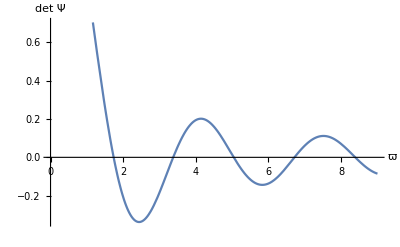

```mathematica
Plot[detΨ[ϖ, -1, 1], {ϖ, 0, 9}, AxesLabel -> {"ϖ", "det Ψ"}]
```

### Numerically finding the normal frequencies ϖ_n and normal modes ψ_n

The approximate roots of the equation (101) can be found by iterating through some range of ϖ in small steps ε and picking the values of ϖ that make det Ψ closest to zero. If |det Ψ[ϖ - ε]| > |det Ψ[ϖ]| < |det Ψ[ϖ + ε]|, then ϖ is an approximate root (here Ψ[ϖ] ≡ Ψ[ϖ, σ_0, σ_p] is a shortcut that will be used in this subsection; since we are interested in finding the normal frequencies for some particular σ_0 and σ_p, the values of these two parameters can be guessed from the context). Because Ψ is continuous, this method would work given that ε is sufficiently small.
	Practically, the algorithm can be implemented the following way. Start with currϖ = ϖ_min and increase it in small steps dϖ before reaching ϖ_max, where ϖ_min, dϖ, ϖ_max are some parameters and currϖ is the iterator. For each ϖ, we can compute the corresponding det Ψ. Define the variables currdetΨ = det Ψ[currϖ] and pastdetΨ = det Ψ[ϖ - dϖ], where pastdetΨ tells us what the value of currdetΨ was one cycle ago when currϖ was currϖ - dϖ. The idea is that if pastdetΨ ≡ det Ψ[ϖ - dϖ] and currdetΨ ≡ det Ψ[ϖ] have different signs, then, because det Ψ[ϖ] is a continuous function, it must have gone through zero somewhere between currϖ - dϖ and currϖ. And it’s a good guess to say that currϖ is an approximate root. These ϖ’s can be stored it in ϖlist, which is the output of the function.

```mathematica
ClearAll[findApproximateψϖ];
findApproximateψϖ[σ0_, σp_, ϖmin_, ϖmax_, dϖ_] := Block[
	{
		currϖ = ϖmin,
		currdetΨ, pastdetΨ,
		ϖlist = {}
	},
	pastdetΨ = detΨ[currϖ - dϖ, σ0, σp];
	
	While[currϖ ≤ ϖmax,
		currdetΨ = detΨ[currϖ, σ0, σp];
		
		If[Sign[currdetΨ] ≠ Sign[pastdetΨ],
			AppendTo[ϖlist, currϖ];
		];
		
		pastdetΨ = currdetΨ;
		currϖ += dϖ;
	];
	
	ϖlist
];
```

This is how to find the approximate roots in the interval 0 ≤ ϖ ≤ 9 for σ_0 = -1, σ_p = 1 with dϖ = 0.1:

```mathematica
approxψϖ = findApproximateψϖ[-1, 1, 0, 9, 0.1]
```

{1.8,3.4,5.1,6.8,8.4}

And this is how these points look on a graph:

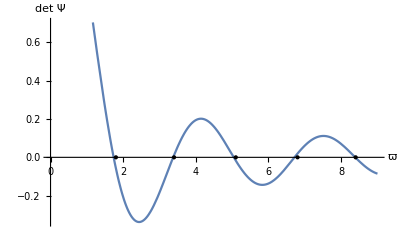

```mathematica
Show[{
Plot[detΨ[ϖ, -1, 1], {ϖ, 0, 9}, AxesLabel -> {"ϖ", "det Ψ"}],
Graphics[{PointSize[Large], Point[{#, 0}]}& /@ approxψϖ]
}]
```

We can see that they do actually make det Ψ close to zero:

```mathematica
detΨ[#, -1, 1]& /@ approxψϖ
```

{-0.0579506,0.0109508,-0.0174919,0.019718,-0.00229443}

But the accuracy of this algorithm can be significantly improved. We know that det Ψ[pastϖ] = pastdetΨ and det Ψ[currϖ] = currdetΨ, where pastϖ = currϖ - dϖ. Since currϖ - pastψ is very small, we can approximate det Ψ[ϖ] as being linear between pastϖ and currϖ, so that det Ψ[ϖ] ≈ currdetΨ + (currdetΨ - pastdetΨ)/dϖ(ϖ - currϖ).  Equating it to zero, we get that a more precise value for the approximate root would be newϖ =  (currdetΨ pastϖ - pastdetΨ currϖ)/(currdetΨ - pastdetΨ). This already would be a much better estimate, but to get even more accurate result it is better to repeat the process several times, until currdetΨ reaches a very small value, say 10^-12. We can equate pastϖ to currϖ and pastdetΨ to currdetΨ, then currϖ to newϖ and currdetΨ to det Ψ[newϖ] . We can then again find newϖ is using linear interpolation for det Ψ[ϖ] and again update the variables, and repeat the procedure several times. This is basically like applying Newton’s method to the interpolation of det Ψ[ϖ].
	The animation below illustrates this algorithm on an example when det Ψ[ϖ] = ϖ^3/2 + 1 ϖ^2 - 4ϖ + 1 (of course, in reality the analytic expression for det Ψ is unknown). It starts with pastdetΨ = 0 and currdetΨ = 1 and calculates an approximate root by drawing a line between the points <pastϖ, pastdetψ> and <currϖ, currdetΨ> and finding its zero intersect.

```mathematica
ClearAll[illustrateFindΨ];
illustrateFindΨ[] := Module[{Ψ = Function[ϖ, ϖ^3/2 + 1 ϖ^2 - 4ϖ + 1], currϖ = 1, pastϖ = 0, newϖ, currΨ, pastΨ, plots = {}, i},
	pastΨ = Ψ[pastϖ];
	currΨ = Ψ[currϖ];
	
	For[i = 1, i ≤ 6, i++,
		newϖ = (currΨ pastϖ - pastΨ currϖ)/(currΨ - pastΨ);  (* compute newϖ *)
		
		AppendTo[plots, Plot[
			Ψ[ϖ], {ϖ, -0.2, 1.2},
			Epilog -> {
				{Darker@Magenta, PointSize[Large], Point[{currϖ, Ψ[currϖ]}]},
				{Darker@Red, PointSize[Large], Point[{pastϖ, Ψ[pastϖ]}]},
				{Dashed, InfiniteLine[{{pastϖ, Ψ[pastϖ]}, {currϖ, Ψ[currϖ]}}]},
				{Pink, InfiniteLine[{{newϖ, 0}, {newϖ, 1}}]}
			},
			ImageSize -> Medium,
			PlotLegends -> LineLegend[
				{Darker@Red, Darker@Magenta, Pink},
				{"pastϖ", "currϖ", "newϖ"}],
			PlotRange -> {{-0.2, 1.2}, {-1.8, 1.4}}
		]];
		
				
		pastϖ = currϖ;  (* update past to curr *)
		pastΨ = currΨ;
		
		currϖ = newϖ;  (* update curr to new *)
		currΨ = Ψ[newϖ];
	];
	
	Animate[
		plots[[n]],
		{n, 1, Length[plots], 1},
		AnimationRate -> 1/2
	]
];
```

```mathematica
illustrateFindΨ[]
```

Even though running this process for a few more steps would not impact the computation time significantly while dramatically decreasing currdetΨ, it would not do us any good. So far we have ignored the numerical error of detΨ because it was comparatively small, but in this case it becomes significant. Even as currdetΨ approaches zero,  the actual value of det Ψ[currϖ] will not tend to zero but instead will converge to some finite number, namely the numerical error of detΨ.
	There is also the minor technical detail that to avoid infinite cycles, currϖ has to be increased by dϖ and currdetΨ has to be updated accordingly after an approximate root is found. If there was no such mechanisms, the code would not work. Consider the following situation: it is known that det Ψ[1] = 0.04 and det Ψ[1.01] = -0.02. The algorithm tells us that det Ψ has a root somewhere between 1 and 1.01; let’s say that after a few iterations it was found that det Ψ[1.003] = 2 · 10^-13, which is within the allowed error, so we say that 1.003 is an approximate root and append it to the output list. But here is the problem: next cycle, we update currϖ, which was 1.003, to currϖ + dϖ = 1.013, and currdetΨ becomes det Ψ[1.013]. Since det Ψ[1.01] = -0.02 is negative, det Ψ[1.01 + 0.003] would most likely be negative as well (considering that det Ψ[1] > det Ψ[1.01]), so currdetΨ = det Ψ[1.013] becomes negative  as well. And since last cycle currdetΨ was 2·10^-13, which is a positive number, the algorithm will try to find an approximate root near that point, even though the root was already found last time! If no measures are taken, this process would repeat infinitely. To prevent it, after finding an approximate root we need to update currϖ to currϖ + dϖ right away and re-calculate currdetΨ accordingly. This way, after finding the root currdetΨ would become currdetΨ[1.013] < 0, and next cycle it would be currdetΨ[1.023], which is again negative. We have just escaped the trap, and the algorithm will then go on to find another approximate root.

```mathematica
ClearAll[findψϖ];
findψϖ[σ0_, σp_, ϖmin_, ϖmax_, dϖ_] := Block[
	{
		currϖ = ϖmin, pastϖ, newϖ,
		currdetΨ, pastdetΨ,
		ϖlist = {}
	},
	pastϖ = currϖ - dϖ;
	pastdetΨ = detΨ[pastϖ, σ0, σp];
	
	While[currϖ ≤ ϖmax,
		currdetΨ = detΨ[currϖ, σ0, σp];
		
		If[Sign[currdetΨ] ≠ Sign[pastdetΨ],
			pastϖ = currϖ - dϖ;
			pastdetΨ = detΨ[currϖ - dϖ, σ0, σp];
			While[(Abs[currdetΨ] > 10^-12) && (currdetΨ ≠ pastdetΨ),
				newϖ = (currdetΨ pastϖ - pastdetΨ currϖ)/(currdetΨ - pastdetΨ);  (* compute newϖ *)
				
				pastϖ = currϖ;  (* update past to curr *)
				pastdetΨ = currdetΨ;
				
				currϖ = newϖ;  (* update curr to new *)
				currdetΨ = detΨ[newϖ, σ0, σp];
			];
		
			AppendTo[ϖlist, currϖ];
			
			currϖ += dϖ;
			currdetΨ = detΨ[currϖ, σ0, σp];
		];
		
		pastdetΨ = currdetΨ;
		
		currϖ += dϖ;
	];
	
	ϖlist
];
```

This is how to find the approximate roots in the interval 0 ≤ ϖ ≤ 9 for σ_0 = -1, σ_p = 1 with dϖ = 0.1:

```mathematica
betterψϖ = findψϖ[-1, 1, 0, 9, 0.1]
```

{1.7374,3.37662,5.04357,6.71481,8.3878}

These approximate roots make Ψ much closer to zero than those found using the previous function:

```mathematica
detΨ[#, -1, 1]& /@ betterψϖ
```

{1.84832×10^-16,7.73714×10^-15,-2.85243×10^-16,1.43825×10^-15,-2.72123×10^-15}

Having computed a normal frequency, we can also find the corresponding normal mode. For that, let us remember that ψ[σ] = C_0 ψ_0[σ] + C_1 ψ_1[σ], where the constants C_0 and C_1 are determined by the equation (100). The matrix Ψ turns <C_0, C_1> into a zero vector if and only if <C_0, C_1> is in the nullspace of Ψ; so, we are interested in the nullspace of Ψ. Well, almost. Because Ψ was computed with some numerical error, we get that its determinant is very small, but not zero. What we are looking for is not the nullspace but “nullspace with margins”.

Let’s solve the problem for an arbitrary N×N matrix M. While a vector in the nullspace of a matrix reduces to zero when acted upon by it, we are looking for a vector v that would give approximately zero: M v ≈ 0, or (M v)^2 = min. We could solve the problem with gradient descent, but the issue is that this would either lead us to the zero vector or not converge at all; we can show this by taking the gradient of (M v)^2, which for nonsingular M can only be zero if v = 0. Thus, we need to fix the norm of v, to be equal to, for example, 1. This would prevent the absolute value of v we get from becoming 0 or diverging to infinity. Now, we have a quantity (M v)^2 to be minimized while obeying the constraint v^2 = 1; this is a classic minimization problem that can be solved using Lagrange’s multipliers. What we get by using the formula is

(A - I λ)v = 0
A_jk ≡ (∑^3)_(i = 1)M_ij M_ik

where λ is some constant. The equation tells us that  v must be an eigenvector of the matrix A. There are several linearly independent eigenvectors of A, each one corresponding to (M v)^2 being either minimal or maximal for a given v^2. We can iterate through the eigenvectors and select the one that makes (M v)^2 smallest:

```mathematica
ClearAll[minVector];
minVector[M_] := First@Sort[
	Normalize /@ Eigenvectors[Table[
			Sum[M[[i, j]] M[[i, k]], {i, Length[M]}],
			{j, Length[M]}, {k, Length[M]}
		]],
	Norm[M.#1] < Norm[M.#2]&
]
```

Having found the general solution for the “nullspace with margins” problem, we can compute the vector (C_0
C_1) as {C_0, C_1} = minVector[Ψ], and the solution would then be ψ[σ] = C_0 ψ_0[σ] + C_1 ψ_1[σ].

```mathematica
ClearAll[computeψNmode];
Options[computeψNmode] = {"ncoefs" -> 40, "nodes" -> Automatic};
computeψNmode[ϖ_, σ0_, σp_, OptionsPattern[]] := Block[
	{
		ψ0, ψ1, Ψ,
		C0, C1
	},
	{ψ0, ψ1} = findψ01[ϖ, "ncoefs" -> OptionValue["ncoefs"], "Range" -> Max[-σ0, σp]];
	Ψ = Ψmatrix[σ0, σp, ψ0, ψ1];
	{C0, C1} = minVector[Ψ];
	
	Function[σ, Module[{ξ = √(1 + σ^2) - 1}, Null]] /. Null -> C0 ψ0[[2, 2]] + C1 ψ1[[2, 2]]
];
```

Lastly, it is convenient to not only output the frequencies but also the corresponding normal modes ψ_n, and instead of stopping when currϖ reaches some set number ϖmax, it is better to stop when a certain number of normal modes is found. And instead of always storing all the found normal modes in a list, there should be an option to only output the last found normal mode.  Finally, just to prevent possible issues with division by zero when finding newϖ, a condition was added that breaks the cycle if currdetΨ is equal to pastdetΨ. Here is a function that does this:

```mathematica
ClearAll[findψNmodes];
Options[findψNmodes] = {"ϖmin" -> 0.2, "dϖ" -> 0.1, "OutputForm" -> All};
findψNmodes[σ0_, σp_, nmodes_, OptionsPattern[]] := Block[
	{
		ϖmin = OptionValue["ϖmin"], dϖ = OptionValue["dϖ"],
		currϖ, pastϖ, newϖ,
		currdetΨ, pastdetΨ,
		output = {}, counter = 0
	},
	currϖ = ϖmin;
	
	pastϖ = currϖ - dϖ;
	pastdetΨ = detΨ[pastϖ, σ0, σp];
	
	While[counter < nmodes,
		currdetΨ = detΨ[currϖ, σ0, σp];
		
		If[Sign[currdetΨ] ≠ Sign[pastdetΨ],
			counter++;
			
			If[(SameQ[OptionValue["OutputForm"], All]) || (counter == nmodes), 
				pastϖ = currϖ - dϖ;
				pastdetΨ = detΨ[currϖ - dϖ, σ0, σp];
				While[(Abs[currdetΨ] > 10^-12) && (currdetΨ ≠ pastdetΨ),
					newϖ = (currdetΨ pastϖ - pastdetΨ currϖ)/(currdetΨ - pastdetΨ);  (* compute newϖ *)
							
					pastϖ = currϖ;  (* update past to curr *)
					pastdetΨ = currdetΨ;
				
					currϖ = newϖ;  (* update curr to new *)
					currdetΨ = detΨ[newϖ, σ0, σp];
				];
				
				Switch[OptionValue["OutputForm"],
					All, AppendTo[output, {currϖ, computeψNmode[currϖ, σ0, σp]}],
					Last, output = {currϖ, computeψNmode[currϖ, σ0, σp]}; Break[]
				];
				
				currϖ += dϖ;
				currdetΨ = detΨ[currϖ, σ0, σp];
			];
		];
		
		pastdetΨ = currdetΨ;
		
		currϖ += dϖ;
	];
	
	output
];
```

Here is how we can compute the first four normal modes with σ_0 = -1, σ_p = 1:

```mathematica
findψNmodes[-1, 1, 4]
```

{{1.7374,Function[σ,Module[{ξ=√(1+σ^2)-1},0.-1. (1-3.01854 ξ+1.5186 ξ^2-0.103117 ξ^3-0.119452 ξ^4+0.0574013 ξ^5-0.018905 ξ^6+0.00620196 ξ^7-0.00221293 ξ^8+0.000846969 ξ^9-0.000339375 ξ^10+0.000140283 ξ^11-0.0000593233 ξ^12+0.0000255329 ξ^13-0.0000111457 ξ^14+4.92211×10^-6 ξ^15-2.19494×10^-6 ξ^16+9.86938×10^-7 ξ^17-4.4695×10^-7 ξ^18+2.03673×10^-7 ξ^19-9.33224×10^-8 ξ^20+4.29685×10^-8 ξ^21-1.98701×10^-8 ξ^22+9.22454×10^-9 ξ^23-4.29756×10^-9 ξ^24+2.00859×10^-9 ξ^25-9.41523×10^-10 ξ^26+4.42522×10^-10 ξ^27-2.08501×10^-10 ξ^28+9.84626×10^-11 ξ^29-4.6596×10^-11 ξ^30+2.2094×10^-11 ξ^31-1.04952×10^-11 ξ^32+4.99399×10^-12 ξ^33-2.38009×10^-12 ξ^34+1.13602×10^-12 ξ^35-5.42987×10^-13 ξ^36+2.59874×10^-13 ξ^37-1.24531×10^-13 ξ^38+5.9745×10^-14 ξ^39-2.86951×10^-14 ξ^40)]]},{3.37662,Function[σ,Module[{ξ=√(1+σ^2)-1},0.-1.41421 (√ξ-3.88384 ξ^(3/2)+4.16189 ξ^(5/2)-1.38962 ξ^(7/2)-0.405149 ξ^(9/2)+0.521224 ξ^(11/2)-0.219108 ξ^(13/2)+0.0553596 ξ^(15/2)-0.00916902 ξ^(17/2)+0.000794264 ξ^(19/2)+0.000113346 ξ^(21/2)-0.0000902947 ξ^(23/2)+0.0000389289 ξ^(25/2)-0.0000156609 ξ^(27/2)+6.37663×10^-6 ξ^(29/2)-2.65555×10^-6 ξ^(31/2)+1.12797×10^-6 ξ^(33/2)-4.86848×10^-7 ξ^(35/2)+2.12894×10^-7 ξ^(37/2)-9.41153×10^-8 ξ^(39/2)+4.19916×10^-8 ξ^(41/2)-1.88845×10^-8 ξ^(43/2)+8.5514×10^-9 ξ^(45/2)-3.89577×10^-9 ξ^(47/2)+1.78432×10^-9 ξ^(49/2)-8.21148×10^-10 ξ^(51/2)+3.79514×10^-10 ξ^(53/2)-1.7608×10^-10 ξ^(55/2)+8.19804×10^-11 ξ^(57/2)-3.82909×10^-11 ξ^(59/2)+1.79369×10^-11 ξ^(61/2)-8.42485×10^-12 ξ^(63/2)+3.96688×10^-12 ξ^(65/2)-1.87209×10^-12 ξ^(67/2)+8.85365×10^-13 ξ^(69/2)-4.1954×10^-13 ξ^(71/2)+1.99168×10^-13 ξ^(73/2)-9.47132×10^-14 ξ^(75/2)+4.51126×10^-14 ξ^(77/2)-2.15198×10^-14 ξ^(79/2)+1.028×10^-14 ξ^(81/2)) Sign[σ]]]},{5.04357,Function[σ,Module[{ξ=√(1+σ^2)-1},0.-1. (1-25.4376 ξ+107.846 ξ^2-168.51 ξ^3+109.277 ξ^4-5.37042 ξ^5-38.0131 ξ^6+27.1654 ξ^7-8.79301 ξ^8+0.62355 ξ^9+0.827917 ξ^10-0.518241 ξ^11+0.198658 ξ^12-0.0630073 ξ^13+0.0190412 ξ^14-0.00600848 ξ^15+0.00205723 ξ^16-0.000759609 ξ^17+0.000296061 ξ^18-0.000119676 ξ^19+0.0000496362 ξ^20-0.0000209905 ξ^21+9.01494×10^-6 ξ^22-3.92135×10^-6 ξ^23+1.72414×10^-6 ξ^24-7.6507×10^-7 ξ^25+3.42212×10^-7 ξ^26-1.54143×10^-7 ξ^27+6.98611×10^-8 ξ^28-3.18374×10^-8 ξ^29+1.45808×10^-8 ξ^30-6.70743×10^-9 ξ^31+3.098×10^-9 ξ^32-1.43615×10^-9 ξ^33+6.67993×10^-10 ξ^34-3.11661×10^-10 ξ^35+1.45822×10^-10 ξ^36-6.84066×10^-11 ξ^37+3.21682×10^-11 ξ^38-1.51612×10^-11 ξ^39+7.16062×10^-12 ξ^40)]]},{6.71481,Function[σ,Module[{ξ=√(1+σ^2)-1},0.-1.41421 (√ξ-15.1129 ξ^(3/2)+67.0337 ξ^(5/2)-131.429 ξ^(7/2)+125.375 ξ^(9/2)-41.1978 ξ^(11/2)-32.6822 ξ^(13/2)+44.8759 ξ^(15/2)-22.6035 ξ^(17/2)+3.67758 ξ^(19/2)+2.48307 ξ^(21/2)-2.17998 ξ^(23/2)+0.915453 ξ^(25/2)-0.245082 ξ^(27/2)+0.0355664 ξ^(29/2)+0.00423427 ξ^(31/2)-0.00532547 ξ^(33/2)+0.00251943 ξ^(35/2)-0.00096855 ξ^(37/2)+0.000352981 ξ^(39/2)-0.000129836 ξ^(41/2)+0.0000492829 ξ^(43/2)-0.0000193424 ξ^(45/2)+7.80953×10^-6 ξ^(47/2)-3.22518×10^-6 ξ^(49/2)+1.35624×10^-6 ξ^(51/2)-5.78831×10^-7 ξ^(53/2)+2.50122×10^-7 ξ^(55/2)-1.09232×10^-7 ξ^(57/2)+4.8142×10^-8 ξ^(59/2)-2.13886×10^-8 ξ^(61/2)+9.57013×10^-9 ξ^(63/2)-4.30917×10^-9 ξ^(65/2)+1.95131×10^-9 ξ^(67/2)-8.88128×10^-10 ξ^(69/2)+4.06099×10^-10 ξ^(71/2)-1.86474×10^-10 ξ^(73/2)+8.59556×10^-11 ξ^(75/2)-3.97617×10^-11 ξ^(77/2)+1.84531×10^-11 ξ^(79/2)-8.58971×10^-12 ξ^(81/2)) Sign[σ]]]}}

The output is of the form {{ϖ_1, ψ_1}, {ϖ_2, ψ_2}, ...}. Compute the third normal mode with σ_0 = -1, σ_p = 1:

```mathematica
exampleψnm = findψNmodes[-1, 1, 3, OutputForm -> Last]
```

{5.04357,Function[σ,Module[{ξ=√(1+σ^2)-1},0.-1. (1-25.4376 ξ+107.846 ξ^2-168.51 ξ^3+109.277 ξ^4-5.37042 ξ^5-38.0131 ξ^6+27.1654 ξ^7-8.79301 ξ^8+0.62355 ξ^9+0.827917 ξ^10-0.518241 ξ^11+0.198658 ξ^12-0.0630073 ξ^13+0.0190412 ξ^14-0.00600848 ξ^15+0.00205723 ξ^16-0.000759609 ξ^17+0.000296061 ξ^18-0.000119676 ξ^19+0.0000496362 ξ^20-0.0000209905 ξ^21+9.01494×10^-6 ξ^22-3.92135×10^-6 ξ^23+1.72414×10^-6 ξ^24-7.6507×10^-7 ξ^25+3.42212×10^-7 ξ^26-1.54143×10^-7 ξ^27+6.98611×10^-8 ξ^28-3.18374×10^-8 ξ^29+1.45808×10^-8 ξ^30-6.70743×10^-9 ξ^31+3.098×10^-9 ξ^32-1.43615×10^-9 ξ^33+6.67993×10^-10 ξ^34-3.11661×10^-10 ξ^35+1.45822×10^-10 ξ^36-6.84066×10^-11 ξ^37+3.21682×10^-11 ξ^38-1.51612×10^-11 ξ^39+7.16062×10^-12 ξ^40)]]}

The output is of the form {ϖ, ψ}. To verify that it indeed solves the equation (92), we can plug it in and see what happens. For an exact solution, the right-hand-side of the equation would be zero.

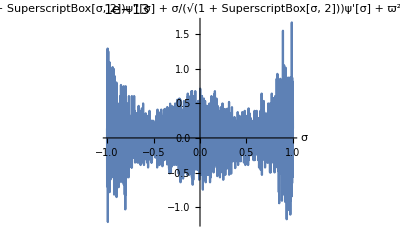

```mathematica
Block[
	{
		ϖ = exampleψnm[[1]], ψfunc = exampleψnm[[2, 2]],
		err
	},
	err = √(1 + σ^2)ψ''[σ] + σ/(√(1 + σ^2))ψ'[σ] + ϖ^2 ψ[σ] /. {ψ[σ] -> ψfunc, ψ'[σ] -> D[ψfunc, σ], ψ''[σ] -> D[ψfunc, {σ, 2}]};
	Plot[err, {σ, -1, 1}, AxesLabel -> {"σ", "√(1  +  SuperscriptBox[σ, 2])ψ''[σ] + σ/(√(1  +  SuperscriptBox[σ, 2]))ψ'[σ] + ϖ^2 ψ[σ]"}, PlotRange->All]
]
```

We also need to evaluate ψ at the boundaries, σ = σ_0 and σ = σ_p. Ideally, the result should be zero.

```mathematica
exampleψnm[[2]][-1]
exampleψnm[[2]][1]
```

7.7225×10^-16

7.7225×10^-16

We see that the Frobenius solution we get satisfies the ODE (94) and the boundary conditions (91) with very good accuracy. Although the solution given by NDSolve is not as accurate, it is still not bad:

```mathematica
exampleψnm2 = findψNmodes[-2, 2, 3, OutputForm -> Last]
```

{2.81476,Function[σ,Module[{ξ=√(1+σ^2)-1},0.-1. (Piecewise[{{1-7.92285 ξ+10.4619 ξ^2-4.13097 ξ^3-0.463594 ξ^4+0.973768 ξ^5-0.430094 ξ^6+0.122813 ξ^7-0.0298606 ξ^8+0.00767734 ξ^9-0.00234795 ξ^10+0.000833639 ξ^11-0.000322002 ξ^12+0.000130199 ξ^13-0.0000541906 ξ^14+0.0000230325 ξ^15-9.95051×10^-6 ξ^16+4.35594×10^-6 ξ^17-1.92785×10^-6 ξ^18+8.61145×10^-7 ξ^19-3.8772×10^-7 ξ^20+1.75769×10^-7 ξ^21-8.01638×10^-8 ξ^22+3.67554×10^-8 ξ^23-1.69323×10^-8 ξ^24+7.83344×10^-9 ξ^25-3.63787×10^-9 ξ^26+1.69529×10^-9 ξ^27-7.92516×10^-10 ξ^28+3.71555×10^-10 ξ^29-1.74657×10^-10 ξ^30+8.23009×10^-11 ξ^31-3.88688×10^-11 ξ^32+1.83951×10^-11 ξ^33-8.72259×10^-12 ξ^34+4.14355×10^-12 ξ^35-1.97166×10^-12 ξ^36+9.39678×10^-13 ξ^37-4.48506×10^-13 ξ^38+2.14369×10^-13 ξ^39-1.02595×10^-13 ξ^40, 0≤ξ<1}, {InterpolatingFunction[…][ξ], 1≤ξ}, {0, True}}])]]}

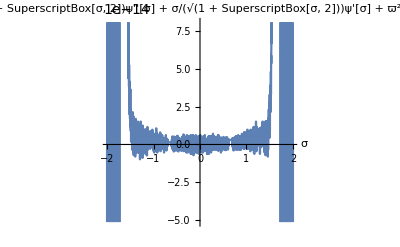

```mathematica
Block[
	{
		ϖ = exampleψnm2[[1]], ψfunc = exampleψnm2[[2, 2]],
		err
	},
	err = √(1 + σ^2)ψ''[σ] + σ/(√(1 + σ^2))ψ'[σ] + ϖ^2 ψ[σ] /. {ψ[σ] -> ψfunc, ψ'[σ] -> D[ψfunc, σ], ψ''[σ] -> D[ψfunc, {σ, 2}]};
	Plot[err, {σ, -2, 2}, AxesLabel -> {"σ", "√(1  +  SuperscriptBox[σ, 2])ψ''[σ] + σ/(√(1  +  SuperscriptBox[σ, 2]))ψ'[σ] + ϖ^2 ψ[σ]"}]
]
```

```mathematica
exampleψnm2[[2]][-2]
exampleψnm2[[2]][2]
```

-9.21307×10^-14

-9.21307×10^-14

### Why ϖ can’t be zero

For ϖ_n = 0, the equation (94) becomes

d/dσ[√(1+σ^2)dψ_n/dσ] = 0

Integrating this, we get

dψ_n/dσ = C_1/(√(1+σ^2))

And, integrating again,

ψ_n = C_0 + C_1 ArcSinh[σ]

By boundary conditions, ψ_n[σ_0] = ψ_n[σ_p] = 0. Substituting this, we get a set of two equations that we can write in matrix form as

(1 | ArcSinh[σ_0]
1 | ArcSinh[σ_p])(C_0
C_1) = 0

The equation has nonzero solutions C_0, C_1 if and only if the determinant of the matrix is zero:

ArcSinh[σ_0] - ArcSinh[σ_p] = 0

But since σ_0 ≠ σ_p and ArcSinh is a one-to-one function, we see that the equation has no solutions, and thus ϖ ≠ 0. □

## Finding the normal modes of in-plane motion

### Writing the normal mode equation for η

The equation (90) reads

∂^2/(∂τ^2)[(1+2 σ^2)/(1+σ^2)η + 4 σ(∂η)/(∂σ) + (1+σ^2)(∂^2 η)/(∂σ^2)] = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

Since it’s a linear equation, its solution is a sum of its normal modes:

η[τ, σ] = (∑^∞)_(n = 1)C_n η_n[σ] Cos[ϖ_n τ + ϕ_n]

where each of the C_n and ϕ_n is a constant determined by the initial conditions, η_n and ϖ_n describe the n-th normal mode of the equation. Substituting this into the equation (90) and using the fact that the normal modes η_n are linearly independent, we get

(1+σ^2)^(3/2)(d^4 η_n)/dσ^4 + 7 σ √(1+σ^2)(d^3 η_n)/dσ^3 + (ϖ_n^2(1+σ^2) + (7+10 σ^2)/(√(1+σ^2)))(d^2 η_n)/dσ^2+ (4 ϖ_n^2 σ - (σ (1-2 σ^2))/((1+σ^2)^(3/2)))dη_n/dσ + (ϖ_n^2(1+2 σ^2)/(1+σ^2) - (2 (1-2 σ^2))/((1+σ^2)^(5/2)))η_n = 0

### Solving the normal mode equation using Frobenius’s method

In exactly the same way as with horizontal normal modes, the equation (103) can be re-written in terms of ξ ≡ √(1 + σ^2) - 1 (idea from John Gregg Gale’s master’s thesis, 1976); the equation you can see in the input of frobeniusDSolve below. This is a homogenous linear ODE with polynomial coefficients, so it can be solved using the Frobenius’s method. Let us solve it near the regular singular point ξ = 0: (see this Wolfram Community post for source code and explanation)

```mathematica
ηξeqnFrobeniusSoln = frobeniusDSolve[-2 η[ξ]+8 ξ η[ξ]+4 ξ^2 η[ξ]+ϖ^2 η[ξ]+7 ξ ϖ^2 η[ξ]+17 ξ^2 ϖ^2 η[ξ]+19 ξ^3 ϖ^2 η[ξ]+10 ξ^4 ϖ^2 η[ξ]+2 ξ^5 ϖ^2 η[ξ]
	+4 η'[ξ]+4 ξ η'[ξ]+8 ξ^2 η'[ξ]+16 ξ^3 η'[ξ]+10 ξ^4 η'[ξ]+2 ξ^5 η'[ξ]+ϖ^2 η'[ξ]+12 ξ ϖ^2 η'[ξ]+42 ξ^2 ϖ^2 η'[ξ]+68 ξ^3 ϖ^2 η'[ξ]+57 ξ^4 ϖ^2 η'[ξ]
	+24 ξ^5 ϖ^2 η'[ξ]+4 ξ^6 ϖ^2 η'[ξ]+3 η''[ξ]+38 ξ η''[ξ]+123 ξ^2 η''[ξ]+184 ξ^3 η''[ξ]+146 ξ^4 η''[ξ]+60 ξ^5 η''[ξ]+10 ξ^6 η''[ξ]+2 ξ ϖ^2 η''[ξ]+11 ξ^2 ϖ^2 η''[ξ]
	+25 ξ^3 ϖ^2 η''[ξ]+30 ξ^4 ϖ^2 η''[ξ]+20 ξ^5 ϖ^2 η''[ξ]+7 ξ^6 ϖ^2 η''[ξ]+ξ^7 ϖ^2 η''[ξ]+12 ξ Derivative[3][η][ξ]+70 ξ^2 Derivative[3][η][ξ]+166 ξ^3 Derivative[3][η][ξ]+205 ξ^4 Derivative[3][η][ξ]+139 ξ^5 Derivative[3][η][ξ]
	+49 ξ^6 Derivative[3][η][ξ]+7 ξ^7 Derivative[3][η][ξ]+4 ξ^2 Derivative[4][η][ξ]+20 ξ^3 Derivative[4][η][ξ]+41 ξ^4 Derivative[4][η][ξ]+44 ξ^5 Derivative[4][η][ξ]+26 ξ^6 Derivative[4][η][ξ]+8 ξ^7 Derivative[4][η][ξ]+ξ^8 Derivative[4][η][ξ], η, ξ, 0];
```

Too long to be shown here (see subsection “Formula for the solution to (103)” below), the output tells us the formulas we can use to find the four linearly independent solutions of (103). The first few terms of these solutions are

η_((frob)0)[ϖ, ξ] = 1-1/6 ξ^2 (-2+ϖ^2)+1/90 ξ^3 (-36+5 ϖ^2+ϖ^4) + ...
η_((frob)1/2)[ϖ, ξ] = ξ^(1/2) +1/480 ξ^(5/2) (111-68 ϖ^2)+(ξ^(7/2) (-6039+1294 ϖ^2+136 ϖ^4))/20160 + ...
η_((frob)1)[ϖ, ξ] = ξ-1/6 ξ^2 (4+ϖ^2)+1/90 ξ^3 (54+5 ϖ^2+ϖ^4) + ...
η_((frob)3/2)[ϖ, ξ] = ξ^(3/2)-1/20 ξ^(5/2) (13+2 ϖ^2)+(ξ^(7/2) (1843+92 ϖ^2+16 ϖ^4))/3360

After finding η[ξ], we can find η[σ] by substituting ξ = √(1 + σ^2) - 1. Now, since when deriving the ξ-version of (103) we assumed that σ was positive, but we are also interested in the region σ < 0, we now need to use parity to “extend” the solutions we got for σ > 0. The point where the regions σ ≥ 0 and σ ≤ 0 meet is σ = 0; for σ → 0, we have ξ = √(1 + σ^2) - 1 = σ^2/2 + O[σ^4]. Leaving only the terms with the smallest powers of σ, we get

η_((frob)0) = 1 + O[σ^4]
η_((frob)1/2)  = σ/(√2) + O[σ^4]
η_((frob)1) = σ^2/2 + O[σ^4]
η_((frob)3/2) = σ^3/(2 √2) + O[σ^4]

From here, we get that for σ → 0^+,

η_((frob)0) = 1                      d/dσ η_((frob)0) = 0                     d^2/dσ^2 η_((frob)0) = 0                       d^3/dσ^3(dη_((frob)0))/dσ = 0
η_((frob)1/2) = 0                     d/dσ η_((frob)1/2) = 1/(√2)               d^2/dσ^2 η_((frob)1/2) = 0                      d^3/dσ^3(dη_((frob)1/2))/dσ = 0
η_((frob)1) = 0                      d/dσ η_((frob)1) = 0                      d^2/dσ^2 η_((frob)1) = 1                      d^3/dσ^3(dη_((frob)1))/dσ = 0
η_((frob)3/2) = 0                      d/dσ η_((frob)3/2) = 0                     d^2/dσ^2 η_((frob)3/2) = 0                     d^3/dσ^3(dη_((frob)3/2))/dσ = 3/(√2)

Now, notice that the functions only have either their value or one of the first three derivatives nonzero at σ → 0^+. Because of the reflection symmetry of the equation (103) around σ = 0 and the condition that the function η[σ] and its first three derivatives must be continuous, this means that the extensions of η_((frob)0) and η_((frob)1) are even functions, while that of ψ_((frob)1/2) and ψ_((frob)3/2) - odd functions.

η_0[ϖ, σ] =η_((frob)0)[√(1 + σ^2) - 1]
η_1[ϖ, σ] = √2 Sign[σ]η_((frob)1/2)[√(1 + σ^2) - 1]
η_2[ϖ, σ] =η_((frob)1)[√(1 + σ^2) - 1]
η_3[ϖ, σ] = (√2)/3 Sign[σ]η_((frob)3/2)[√(1 + σ^2) - 1]

where η_((frob)0)[ϖ, ξ], η_((frob)1/2)[ϖ, ξ], η_((frob)1)[ϖ, ξ], η_((frob)3/2)[ϖ, ξ] are given by (104). The functions η_0[ϖ, σ], η_1[ϖ, σ], η_2[ϖ, σ], η_3[ϖ, σ] are constructed so that d^p/dσ^p η_(m,p)[0] = δ_mp. A general solution to (103) is given by

η_n[σ] = C_0 η_0[ϖ_n, σ] + C_1 η_1[ϖ_n, σ] + C_2 η_2[ϖ_n, σ] + C_3 η_3[ϖ_n, σ]

Here n labels a normal mode and goes from 1 to ∞. In this context, η_1[σ] (107 with n = 1) must be distinguished from η_1[ϖ, σ] (106). While η_1[σ] is a normal mode of (90) with a given value of the parameter ϖ that satisfies the boundary conditions, η_1[ϖ, σ] is an auxiliary function; these two can be differentiated using the fact that η_1 the normal mode has one argument, σ, while η_1 the auxiliary function has two arguments, ϖ and σ.
	Frobenius’s method is very quick and accurate, however, the solutions it yields only have a finite radius of convergence. The function findη0123 uses Frobenius’s method if the absolute values of both σ_0 and σ_p are smaller than or equal to 1. If not, the function uses NDSolve.

```mathematica
ClearAll[findη0123];
Options[findη0123] = {"ncoefs" -> 40, "Range" -> 1};
findη0123[ϖ1_, OptionsPattern[]] := If[OptionValue["Range"] ≤ 1,
		findη0123helperFrob[ϖ1, OptionValue["ncoefs"]],
		findη0123helperNDSolve[ϖ1, OptionValue["Range"]]
	];

ClearAll[findη0123helperFrob];
findη0123helperFrob[ϖ1_, ncoefs_] := Block[
	{
		ξsolns
	},
	ξsolns = Table[
			Table[ξ^(r + p), {p, 0, ncoefs}]
				.frobeniusCoefs[ηξeqnFrobeniusSoln[[2]] /. ϖ -> ϖ1, ηξeqnFrobeniusSoln[[3]] /. ϖ -> ϖ1, ncoefs],
				
			{r, ηξeqnFrobeniusSoln[[1]]}
		];
	
	{
		Function[σ, Module[{ξ = √(1 + σ^2) - 1}, Null]] /. Null -> ξsolns[[1]],
		Function[σ, Module[{ξ = √(1 + σ^2) - 1}, √2 Sign[σ] Null]] /. Null -> ξsolns[[2]],
		Function[σ, Module[{ξ = √(1 + σ^2) - 1}, Null]] /. Null -> ξsolns[[3]],
		Function[σ, Module[{ξ = √(1 + σ^2) - 1}, (√2)/3 Sign[σ] Null]] /. Null -> ξsolns[[4]]
	}
];

findη0123helperNDSolve[ϖ1_, range_] := Block[
	{
		eqn = ((1 + σ^2)^(3/2)η''''[σ] + 7 σ √(1 + σ^2)η'''[σ] + (ϖ^2(1 + σ^2) + (7 + 10 σ^2)/(√(1 + σ^2)))η''[σ] +
						(4 ϖ^2 σ - (σ (1 - 2 σ^2))/((1 + σ^2)^(3/2)))η'[σ] + (ϖ^2(1 + 2 σ^2)/(1 + σ^2) - (2 (1 - 2 σ^2))/((1 + σ^2)^(5/2)))η[σ] /. ϖ -> ϖ1),
		halfSolns
	},
	
	halfSolns = Table[
		NDSolve[
			Join[{eqn == 0},
				Table[
					Derivative[p][η][0] == KroneckerDelta[p, d],
					{p, 0, 3}
				]
			],
			η, {σ, 0, range},
			WorkingPrecision -> MachinePrecision,
			MaxStepSize -> 0.01
		][[1, 1, 2]],
		{d, 0, 3}
	];
	
	{
		Function[σ, Null] /. Null -> halfSolns[[1]][Abs[σ]],
		Function[σ, Null] /. Null -> halfSolns[[2]][Abs[σ]] Sign[σ],
		Function[σ, Null] /. Null -> halfSolns[[3]][Abs[σ]],
		Function[σ, Null] /. Null -> halfSolns[[4]][Abs[σ]] Sign[σ]
	}
]
```

The function outputs a list of the form findη0123[ϖ] = {(η̃)_0[σ], (η̃)_1[σ], (η̃)_2[σ], (η̃)_3[σ]}, where (η̃)_0[σ] ≡ η_0[ϖ, σ]. Here is what the four solutions look like for different ϖ for σ_0 = -1, σ_p = 1:

```mathematica
Manipulate[
	With[{ηlist = findη0123[ϖ]},
		Grid[Partition[
			Table[
				Module[{η = ηlist[[n]]},
					Plot[η[σ], {σ, -1, 1}, ImageSize -> Medium, PlotRange -> {-1.5/(n!), 1.5/(n!)}]
				],
				{n, Length[ηlist]}
			],
			2
		]]
	],
	{ϖ, 0, 3},
	ContinuousAction -> False
]
```

And here are the solutions for σ_0 = -4, σ_p = 4:

```mathematica
Manipulate[
	With[{ηlist = findη0123[ϖ, Range -> 4]},
		Grid[Partition[
			Table[
				Module[{η = ηlist[[n]]},
					Plot[η[σ], {σ, -4, 4}, ImageSize -> Medium]
				],
				{n, Length[ηlist]}
			],
			2
		]]
	],
	{ϖ, 0, 3},
	ContinuousAction -> False
]
```

#### Formula for the solution to (100)

```mathematica
ηξeqnFrobeniusSoln
```

{{0,1/2,1,3/2},{4 r a[0]+38 (-1+r) r a[0]+70 (-2+r) (-1+r) r a[0]+20 (-3+r) (-2+r) (-1+r) r a[0]+r ϖ^2 a[0]+2 (-1+r) r ϖ^2 a[0]+3 r (1+r) a[1]+12 (-1+r) r (1+r) a[1]+4 (-2+r) (-1+r) r (1+r) a[1]==0,-2 a[0]-33 r a[0]+76 r^2 a[0]-80 r^3 a[0]+41 r^4 a[0]+ϖ^2 a[0]+r ϖ^2 a[0]+11 r^2 ϖ^2 a[0]+4 a[1]+12 r a[1]+18 r^2 a[1]+30 r^3 a[1]+20 r^4 a[1]+ϖ^2 a[1]+3 r ϖ^2 a[1]+2 r^2 ϖ^2 a[1]+6 a[2]+25 r a[2]+35 r^2 a[2]+20 r^3 a[2]+4 r^4 a[2]==0,8 a[0]+8 r a[0]+184 (-1+r) r a[0]+205 (-2+r) (-1+r) r a[0]+44 (-3+r) (-2+r) (-1+r) r a[0]+7 ϖ^2 a[0]+42 r ϖ^2 a[0]+25 (-1+r) r ϖ^2 a[0]-2 a[1]+4 (1+r) a[1]+123 r (1+r) a[1]+166 (-1+r) r (1+r) a[1]+41 (-2+r) (-1+r) r (1+r) a[1]+ϖ^2 a[1]+12 (1+r) ϖ^2 a[1]+11 r (1+r) ϖ^2 a[1]+4 (2+r) a[2]+38 (1+r) (2+r) a[2]+70 r (1+r) (2+r) a[2]+20 (-1+r) r (1+r) (2+r) a[2]+(2+r) ϖ^2 a[2]+2 (1+r) (2+r) ϖ^2 a[2]+3 (2+r) (3+r) a[3]+12 (1+r) (2+r) (3+r) a[3]+4 r (1+r) (2+r) (3+r) a[3]==0,4 a[0]+16 r a[0]+146 (-1+r) r a[0]+139 (-2+r) (-1+r) r a[0]+26 (-3+r) (-2+r) (-1+r) r a[0]+17 ϖ^2 a[0]+68 r ϖ^2 a[0]+30 (-1+r) r ϖ^2 a[0]+8 a[1]+8 (1+r) a[1]+184 r (1+r) a[1]+205 (-1+r) r (1+r) a[1]+44 (-2+r) (-1+r) r (1+r) a[1]+7 ϖ^2 a[1]+42 (1+r) ϖ^2 a[1]+25 r (1+r) ϖ^2 a[1]-2 a[2]+4 (2+r) a[2]+123 (1+r) (2+r) a[2]+166 r (1+r) (2+r) a[2]+41 (-1+r) r (1+r) (2+r) a[2]+ϖ^2 a[2]+12 (2+r) ϖ^2 a[2]+11 (1+r) (2+r) ϖ^2 a[2]+4 (3+r) a[3]+38 (2+r) (3+r) a[3]+70 (1+r) (2+r) (3+r) a[3]+20 r (1+r) (2+r) (3+r) a[3]+(3+r) ϖ^2 a[3]+2 (2+r) (3+r) ϖ^2 a[3]+3 (3+r) (4+r) a[4]+12 (2+r) (3+r) (4+r) a[4]+4 (1+r) (2+r) (3+r) (4+r) a[4]==0,10 r a[0]+60 (-1+r) r a[0]+49 (-2+r) (-1+r) r a[0]+8 (-3+r) (-2+r) (-1+r) r a[0]+19 ϖ^2 a[0]+57 r ϖ^2 a[0]+20 (-1+r) r ϖ^2 a[0]+4 a[1]+16 (1+r) a[1]+146 r (1+r) a[1]+139 (-1+r) r (1+r) a[1]+26 (-2+r) (-1+r) r (1+r) a[1]+17 ϖ^2 a[1]+68 (1+r) ϖ^2 a[1]+30 r (1+r) ϖ^2 a[1]+8 a[2]+8 (2+r) a[2]+184 (1+r) (2+r) a[2]+205 r (1+r) (2+r) a[2]+44 (-1+r) r (1+r) (2+r) a[2]+7 ϖ^2 a[2]+42 (2+r) ϖ^2 a[2]+25 (1+r) (2+r) ϖ^2 a[2]-2 a[3]+4 (3+r) a[3]+123 (2+r) (3+r) a[3]+166 (1+r) (2+r) (3+r) a[3]+41 r (1+r) (2+r) (3+r) a[3]+ϖ^2 a[3]+12 (3+r) ϖ^2 a[3]+11 (2+r) (3+r) ϖ^2 a[3]+4 (4+r) a[4]+38 (3+r) (4+r) a[4]+70 (2+r) (3+r) (4+r) a[4]+20 (1+r) (2+r) (3+r) (4+r) a[4]+(4+r) ϖ^2 a[4]+2 (3+r) (4+r) ϖ^2 a[4]+3 (4+r) (5+r) a[5]+12 (3+r) (4+r) (5+r) a[5]+4 (2+r) (3+r) (4+r) (5+r) a[5]==0,2 r a[0]+10 (-1+r) r a[0]+7 (-2+r) (-1+r) r a[0]+(-3+r) (-2+r) (-1+r) r a[0]+10 ϖ^2 a[0]+24 r ϖ^2 a[0]+7 (-1+r) r ϖ^2 a[0]+10 (1+r) a[1]+60 r (1+r) a[1]+49 (-1+r) r (1+r) a[1]+8 (-2+r) (-1+r) r (1+r) a[1]+19 ϖ^2 a[1]+57 (1+r) ϖ^2 a[1]+20 r (1+r) ϖ^2 a[1]+4 a[2]+16 (2+r) a[2]+146 (1+r) (2+r) a[2]+139 r (1+r) (2+r) a[2]+26 (-1+r) r (1+r) (2+r) a[2]+17 ϖ^2 a[2]+68 (2+r) ϖ^2 a[2]+30 (1+r) (2+r) ϖ^2 a[2]+8 a[3]+8 (3+r) a[3]+184 (2+r) (3+r) a[3]+205 (1+r) (2+r) (3+r) a[3]+44 r (1+r) (2+r) (3+r) a[3]+7 ϖ^2 a[3]+42 (3+r) ϖ^2 a[3]+25 (2+r) (3+r) ϖ^2 a[3]-2 a[4]+4 (4+r) a[4]+123 (3+r) (4+r) a[4]+166 (2+r) (3+r) (4+r) a[4]+41 (1+r) (2+r) (3+r) (4+r) a[4]+ϖ^2 a[4]+12 (4+r) ϖ^2 a[4]+11 (3+r) (4+r) ϖ^2 a[4]+4 (5+r) a[5]+38 (4+r) (5+r) a[5]+70 (3+r) (4+r) (5+r) a[5]+20 (2+r) (3+r) (4+r) (5+r) a[5]+(5+r) ϖ^2 a[5]+2 (4+r) (5+r) ϖ^2 a[5]+3 (5+r) (6+r) a[6]+12 (4+r) (5+r) (6+r) a[6]+4 (3+r) (4+r) (5+r) (6+r) a[6]==0},a[n]==-((2 ϖ^2 a[-7+n]+4 (-7+n+r) ϖ^2 a[-7+n]+(-8+n+r) (-7+n+r) ϖ^2 a[-7+n]+2 (-6+n+r) a[-6+n]+10 (-7+n+r) (-6+n+r) a[-6+n]+7 (-8+n+r) (-7+n+r) (-6+n+r) a[-6+n]+(-9+n+r) (-8+n+r) (-7+n+r) (-6+n+r) a[-6+n]+10 ϖ^2 a[-6+n]+24 (-6+n+r) ϖ^2 a[-6+n]+7 (-7+n+r) (-6+n+r) ϖ^2 a[-6+n]+10 (-5+n+r) a[-5+n]+60 (-6+n+r) (-5+n+r) a[-5+n]+49 (-7+n+r) (-6+n+r) (-5+n+r) a[-5+n]+8 (-8+n+r) (-7+n+r) (-6+n+r) (-5+n+r) a[-5+n]+19 ϖ^2 a[-5+n]+57 (-5+n+r) ϖ^2 a[-5+n]+20 (-6+n+r) (-5+n+r) ϖ^2 a[-5+n]+4 a[-4+n]+16 (-4+n+r) a[-4+n]+146 (-5+n+r) (-4+n+r) a[-4+n]+139 (-6+n+r) (-5+n+r) (-4+n+r) a[-4+n]+26 (-7+n+r) (-6+n+r) (-5+n+r) (-4+n+r) a[-4+n]+17 ϖ^2 a[-4+n]+68 (-4+n+r) ϖ^2 a[-4+n]+30 (-5+n+r) (-4+n+r) ϖ^2 a[-4+n]+8 a[-3+n]+8 (-3+n+r) a[-3+n]+184 (-4+n+r) (-3+n+r) a[-3+n]+205 (-5+n+r) (-4+n+r) (-3+n+r) a[-3+n]+44 (-6+n+r) (-5+n+r) (-4+n+r) (-3+n+r) a[-3+n]+7 ϖ^2 a[-3+n]+42 (-3+n+r) ϖ^2 a[-3+n]+25 (-4+n+r) (-3+n+r) ϖ^2 a[-3+n]-2 a[-2+n]+4 (-2+n+r) a[-2+n]+123 (-3+n+r) (-2+n+r) a[-2+n]+166 (-4+n+r) (-3+n+r) (-2+n+r) a[-2+n]+41 (-5+n+r) (-4+n+r) (-3+n+r) (-2+n+r) a[-2+n]+ϖ^2 a[-2+n]+12 (-2+n+r) ϖ^2 a[-2+n]+11 (-3+n+r) (-2+n+r) ϖ^2 a[-2+n]+4 (-1+n+r) a[-1+n]+38 (-2+n+r) (-1+n+r) a[-1+n]+70 (-3+n+r) (-2+n+r) (-1+n+r) a[-1+n]+20 (-4+n+r) (-3+n+r) (-2+n+r) (-1+n+r) a[-1+n]+(-1+n+r) ϖ^2 a[-1+n]+2 (-2+n+r) (-1+n+r) ϖ^2 a[-1+n])/((-1+n+r) (n+r) (3+12 (-2+n+r)+4 (-3+n+r) (-2+n+r))))}

#### Code used to do the calculations

```mathematica
Simplify[
	(1 + σ^2)^(3/2)η''''[σ] + 7 σ √(1 + σ^2)η'''[σ] + (ϖ^2(1 + σ^2) + (7 + 10 σ^2)/(√(1 + σ^2)))η''[σ] +
				(4 ϖ^2 σ - (σ (1 - 2 σ^2))/((1 + σ^2)^(3/2)))η'[σ] + (ϖ^2(1 + 2 σ^2)/(1 + σ^2) - (2 (1 - 2 σ^2))/((1 + σ^2)^(5/2)))η[σ] /. {
			η -> Function[σ, η[ξ[σ]]]
		} /. {
			ξ -> Function[σ, √(1 + σ^2) - 1]
		} /. {
			σ -> √((1 + ξ)^2 - 1)
		}, Assumptions -> {ξ ≥ 0}
] // Together
```

1/(1+ξ)^5(-2 η[ξ]+8 ξ η[ξ]+4 ξ^2 η[ξ]+ϖ^2 η[ξ]+7 ξ ϖ^2 η[ξ]+17 ξ^2 ϖ^2 η[ξ]+19 ξ^3 ϖ^2 η[ξ]+10 ξ^4 ϖ^2 η[ξ]+2 ξ^5 ϖ^2 η[ξ]+4 η'[ξ]+4 ξ η'[ξ]+8 ξ^2 η'[ξ]+16 ξ^3 η'[ξ]+10 ξ^4 η'[ξ]+2 ξ^5 η'[ξ]+ϖ^2 η'[ξ]+12 ξ ϖ^2 η'[ξ]+42 ξ^2 ϖ^2 η'[ξ]+68 ξ^3 ϖ^2 η'[ξ]+57 ξ^4 ϖ^2 η'[ξ]+24 ξ^5 ϖ^2 η'[ξ]+4 ξ^6 ϖ^2 η'[ξ]+3 η''[ξ]+38 ξ η''[ξ]+123 ξ^2 η''[ξ]+184 ξ^3 η''[ξ]+146 ξ^4 η''[ξ]+60 ξ^5 η''[ξ]+10 ξ^6 η''[ξ]+2 ξ ϖ^2 η''[ξ]+11 ξ^2 ϖ^2 η''[ξ]+25 ξ^3 ϖ^2 η''[ξ]+30 ξ^4 ϖ^2 η''[ξ]+20 ξ^5 ϖ^2 η''[ξ]+7 ξ^6 ϖ^2 η''[ξ]+ξ^7 ϖ^2 η''[ξ]+12 ξ η^(3)[ξ]+70 ξ^2 η^(3)[ξ]+166 ξ^3 η^(3)[ξ]+205 ξ^4 η^(3)[ξ]+139 ξ^5 η^(3)[ξ]+49 ξ^6 η^(3)[ξ]+7 ξ^7 η^(3)[ξ]+4 ξ^2 η^(4)[ξ]+20 ξ^3 η^(4)[ξ]+41 ξ^4 η^(4)[ξ]+44 ξ^5 η^(4)[ξ]+26 ξ^6 η^(4)[ξ]+8 ξ^7 η^(4)[ξ]+ξ^8 η^(4)[ξ])

```mathematica
Simplify[#[[2]]]& /@ frobeniusNDSolve[-2 η[ξ]+8 ξ η[ξ]+4 ξ^2 η[ξ]+ϖ^2 η[ξ]+7 ξ ϖ^2 η[ξ]+17 ξ^2 ϖ^2 η[ξ]+19 ξ^3 ϖ^2 η[ξ]+10 ξ^4 ϖ^2 η[ξ]+2 ξ^5 ϖ^2 η[ξ]+4 η'[ξ]+4 ξ η'[ξ]+8 ξ^2 η'[ξ]+16 ξ^3 η'[ξ]+10 ξ^4 η'[ξ]+2 ξ^5 η'[ξ]+ϖ^2 η'[ξ]+12 ξ ϖ^2 η'[ξ]+42 ξ^2 ϖ^2 η'[ξ]+68 ξ^3 ϖ^2 η'[ξ]+57 ξ^4 ϖ^2 η'[ξ]+24 ξ^5 ϖ^2 η'[ξ]+4 ξ^6 ϖ^2 η'[ξ]+3 η''[ξ]+38 ξ η''[ξ]+123 ξ^2 η''[ξ]+184 ξ^3 η''[ξ]+146 ξ^4 η''[ξ]+60 ξ^5 η''[ξ]+10 ξ^6 η''[ξ]+2 ξ ϖ^2 η''[ξ]+11 ξ^2 ϖ^2 η''[ξ]+25 ξ^3 ϖ^2 η''[ξ]+30 ξ^4 ϖ^2 η''[ξ]+20 ξ^5 ϖ^2 η''[ξ]+7 ξ^6 ϖ^2 η''[ξ]+ξ^7 ϖ^2 η''[ξ]+12 ξ Derivative[3][η][ξ]+70 ξ^2 Derivative[3][η][ξ]+166 ξ^3 Derivative[3][η][ξ]+205 ξ^4 Derivative[3][η][ξ]+139 ξ^5 Derivative[3][η][ξ]+49 ξ^6 Derivative[3][η][ξ]+7 ξ^7 Derivative[3][η][ξ]+4 ξ^2 Derivative[4][η][ξ]+20 ξ^3 Derivative[4][η][ξ]+41 ξ^4 Derivative[4][η][ξ]+44 ξ^5 Derivative[4][η][ξ]+26 ξ^6 Derivative[4][η][ξ]+8 ξ^7 Derivative[4][η][ξ]+ξ^8 Derivative[4][η][ξ], η, ξ, 0, 4]
```

{1-1/6 ξ^2 (-2+ϖ^2)+1/90 ξ^3 (-36+5 ϖ^2+ϖ^4)-(ξ^4 (-1056+128 ϖ^2+2 ϖ^4+ϖ^6))/2520+(ξ^5 (-48240+5904 ϖ^2+172 ϖ^4-7 ϖ^6+ϖ^8))/113400-(ξ^6 (-3201120+396864 ϖ^2+14436 ϖ^4+128 ϖ^6-24 ϖ^8+ϖ^10))/7484400,√ξ (1+1/480 ξ^2 (111-68 ϖ^2)+(ξ^3 (-6039+1294 ϖ^2+136 ϖ^4))/20160-(ξ^4 (-1869885+295128 ϖ^2+4096 ϖ^4+1088 ϖ^6))/5806080+(ξ^5 (-105423039+15302466 ϖ^2+225496 ϖ^4-9776 ϖ^6+1088 ϖ^8))/319334400-(ξ^6 (-132792856299+18807639228 ϖ^2+376732032 ϖ^4+7616 ϖ^6-535040 ϖ^8+17408 ϖ^10))/398529331200),ξ-1/6 ξ^2 (4+ϖ^2)+1/90 ξ^3 (54+5 ϖ^2+ϖ^4)-(ξ^4 (1464+128 ϖ^2+2 ϖ^4+ϖ^6))/2520+(ξ^5 (65160+5904 ϖ^2+172 ϖ^4-7 ϖ^6+ϖ^8))/113400-(ξ^6 (4283280+396864 ϖ^2+14436 ϖ^4+128 ϖ^6-24 ϖ^8+ϖ^10))/7484400+(ξ^7 (389173680+36442944 ϖ^2+1418448 ϖ^4+27692 ϖ^6+16 ϖ^8-51 ϖ^10+ϖ^12))/681080400,ξ^(3/2) (1-1/20 ξ (13+2 ϖ^2)+(ξ^2 (1843+92 ϖ^2+16 ϖ^4))/3360-(ξ^3 (62325+2774 ϖ^2+16 ϖ^6))/120960+(ξ^4 (53578341+2587784 ϖ^2+40288 ϖ^4-3264 ϖ^6+256 ϖ^8))/106444800-(ξ^5 (8283076407+422370942 ϖ^2+10385600 ϖ^4+16608 ϖ^6-17664 ϖ^8+512 ϖ^10))/16605388800+(ξ^6 (6932772968535+363040656516 ϖ^2+9983632752 ϖ^4+149505728 ϖ^6-422656 ϖ^8-275456 ϖ^10+4096 ϖ^12))/13948526592000)}

```mathematica
(Expand[Simplify[#[[2]] /. ξ -> σ^2/2, Assumptions->{σ > 0}]] /. σ^p_ -> If[p > 3, 0, σ^p])& /@ frobeniusNDSolve[-2 η[ξ]+8 ξ η[ξ]+4 ξ^2 η[ξ]+ϖ^2 η[ξ]+7 ξ ϖ^2 η[ξ]+17 ξ^2 ϖ^2 η[ξ]+19 ξ^3 ϖ^2 η[ξ]+10 ξ^4 ϖ^2 η[ξ]+2 ξ^5 ϖ^2 η[ξ]+4 η'[ξ]+4 ξ η'[ξ]+8 ξ^2 η'[ξ]+16 ξ^3 η'[ξ]+10 ξ^4 η'[ξ]+2 ξ^5 η'[ξ]+ϖ^2 η'[ξ]+12 ξ ϖ^2 η'[ξ]+42 ξ^2 ϖ^2 η'[ξ]+68 ξ^3 ϖ^2 η'[ξ]+57 ξ^4 ϖ^2 η'[ξ]+24 ξ^5 ϖ^2 η'[ξ]+4 ξ^6 ϖ^2 η'[ξ]+3 η''[ξ]+38 ξ η''[ξ]+123 ξ^2 η''[ξ]+184 ξ^3 η''[ξ]+146 ξ^4 η''[ξ]+60 ξ^5 η''[ξ]+10 ξ^6 η''[ξ]+2 ξ ϖ^2 η''[ξ]+11 ξ^2 ϖ^2 η''[ξ]+25 ξ^3 ϖ^2 η''[ξ]+30 ξ^4 ϖ^2 η''[ξ]+20 ξ^5 ϖ^2 η''[ξ]+7 ξ^6 ϖ^2 η''[ξ]+ξ^7 ϖ^2 η''[ξ]+12 ξ Derivative[3][η][ξ]+70 ξ^2 Derivative[3][η][ξ]+166 ξ^3 Derivative[3][η][ξ]+205 ξ^4 Derivative[3][η][ξ]+139 ξ^5 Derivative[3][η][ξ]+49 ξ^6 Derivative[3][η][ξ]+7 ξ^7 Derivative[3][η][ξ]+4 ξ^2 Derivative[4][η][ξ]+20 ξ^3 Derivative[4][η][ξ]+41 ξ^4 Derivative[4][η][ξ]+44 ξ^5 Derivative[4][η][ξ]+26 ξ^6 Derivative[4][η][ξ]+8 ξ^7 Derivative[4][η][ξ]+ξ^8 Derivative[4][η][ξ], η, ξ, 0, 4]
```

{1,σ/(√2),σ^2/2,σ^3/(2 √2)}

### Finding the equation determining the normal frequencies

The formula (107) gives us the general solution of (103). It contains four arbitrary constants C_0, C_1, C_2, C_3, whose values must be such that the boundary conditions (92) are satisfied. Substituting (107) into (92), we get a system of equations that can be written in a matrix form as

(η_0[ϖ, σ_0] | η_1[ϖ, σ_0] | η_2[ϖ, σ_0] | η_3[ϖ, σ_0]
η_0[ϖ, σ_p] | η_1[ϖ, σ_p] | η_2[ϖ, σ_p] | η_3[ϖ, σ_p]
(B^̑)_ϖ η_0[σ_0] | (B^̑)_ϖ η_1[σ_0] | (B^̑)_ϖ η_2[σ_0] | (B^̑)_ϖ η_3[σ_0]
(B^̑)_ϖ η_0[σ_p] | (B^̑)_ϖ η_1[σ_p] | (B^̑)_ϖ η_2[σ_p] | (B^̑)_ϖ η_3[σ_p])(C_1
C_2
C_3
C_4) = 0
(B^̑)_ϖ η ≡ √(1+σ^2)(∂^3 η)/(∂σ^3) + (4 σ)/(√(1+σ^2))(∂^2 η)/(∂σ^2) + ((3+2 σ^2)/((1+σ^2)^(3/2)) + ϖ^2)(∂η)/(∂σ)

As in the case of horizontal oscillations, this equation will only have nonzero solutions C_0, C_1, C_2, C_3 and lead to a nonzero normal mode η_n if the determinant of the matrix is zero:

Η[ϖ, σ_0, σ_p] ≡ (η_0[ϖ, σ_0] | η_1[ϖ, σ_0] | η_2[ϖ, σ_0] | η_3[ϖ, σ_0]
η_0[ϖ, σ_p] | η_1[ϖ, σ_p] | η_2[ϖ, σ_p] | η_3[ϖ, σ_p]
(B^̑)_ϖ η_0[σ_0] | (B^̑)_ϖ η_1[σ_0] | (B^̑)_ϖ η_2[σ_0] | (B^̑)_ϖ η_3[σ_0]
(B^̑)_ϖ η_0[σ_p] | (B^̑)_ϖ η_1[σ_p] | (B^̑)_ϖ η_2[σ_p] | (B^̑)_ϖ η_3[σ_p])
det Η[ϖ_n, σ_0, σ_p] = 0

```mathematica
ClearAll[Ηmatrix];
Options[Ηmatrix] = {"ncoefs" -> 40};
Ηmatrix[ϖ_, σ0_, σp_, OptionsPattern[]] := Block[{η0, η1, η2, η3},
	{η0, η1, η2, η3} = findη0123[ϖ, "ncoefs" -> OptionValue["ncoefs"], "Range" -> Max[-σ0, σp]];
	Ηmatrix[ϖ, σ0, σp, η0, η1, η2, η3]
];
Ηmatrix[ϖ_, σ0_, σp_, η0_, η1_, η2_, η3_, OptionsPattern[]] := Block[
	{
		(*B = Function[η, Function[σ1, √(1+σ1^2)ξD[η, 3][σ1] + (4 σ1)/(√(1+σ1^2))ξD[η, 2][σ1] + (ϖ^2 + (3+2 σ1^2)/((1+σ1^2)^(3/2)))ξD[η, 1][σ1]]]*)
		B = Function[η, Function[σ, Null] /. Null -> (
			√(1 + σ^2)D[η, {σ, 3}] + (4 σ)/(√(1 + σ^2))D[η, {σ, 2}] + (ϖ^2 + (3 + 2 σ^2)/((1 + σ^2)^(3/2)))D[η, σ] /. {
				Derivative[d_][Sign][x_] -> 0,
				Derivative[d_][Abs][x_] -> If[d == 1, Sign[x], 0]
			})
		],
		Bη0, Bη1, Bη2, Bη3
	},
	Bη0 = B[Evaluate@η0[[2]]]; Bη1 = B[Evaluate@η1[[2]]]; Bη2 = B[Evaluate@η2[[2]]]; Bη3 = B[Evaluate@η3[[2]]];
		(* Evaluate@η0[[2]] returns the formula for η0 *)
		(* if η0 == Function[σ, Module[{ξ = √(1 + σ^2) - 1}, ξ^2]], then η0[[2]] == Evaluate@Module[{ξ = √(1 + σ^2) - 1}, ξ^2] == (√(1 + σ^2) - 1)^2 *)
	N@({{η0[σ0], η1[σ0], η2[σ0], η3[σ0]}, {η0[σp], η1[σp], η2[σp], η3[σp]}, {Bη0[σ0], Bη1[σ0], Bη2[σ0], Bη3[σ0]}, {Bη0[σp], Bη1[σp], Bη2[σp], Bη3[σp]}})
];
```

```mathematica
ClearAll[detΗ];
detΗ[ϖ_, σ0_, σp_] := Det[Ηmatrix[ϖ, σ0, σp]];
```

The equation (109) only holds for certain values of ϖ; this is a mathematical formulation of the fact that only some values of ϖ are allowed for normal modes, while some are not. In fact, we can use the equation to find the normal frequencies of our system. Below you can see the plot of det Η as a function of ϖ for σ_0 = -1, σ_p = 1; you can see that det Η is only zero for some specific values of ϖ.

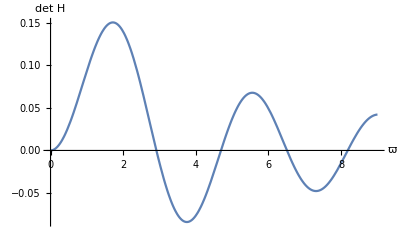

```mathematica
Plot[detΗ[ϖ, -1, 1], {ϖ, 0, 9}, AxesLabel -> {"ϖ", "det Η"}]
```

#### Useless extra function

ξD, which uses chain rule to differentiate functions of the form Function[σ, Module[{ξ = √(1 + σ^2) - 1}, ξ + 2 ξ^2]]:

```mathematica
ClearAll[ξD];
ξD[func_] := ξD[func, 1];
ξD[func_, d_] := Block[
	{
		ξsum = func[[2, 2]],
		derivative
	},
	derivative = D[Null[ξ[σ]], {σ, d}] /. {
		Null[ξ] -> ξsum, Derivative[p_][Null][ξ_] -> D[ξsum, {ξ, p}]
	} /. {
		ξ[σ] -> ξ,
		Derivative[p_][ξ][σ] -> D[√(1 + σ^2) - 1, {σ, p}]
	};
	Function[σ, Module[{ξ = √(1 + σ^2) - 1}, Null]] /. Null -> derivative
];
```

### Numerically finding the normal modes η_n

The equation (109) is practically identical to (101): we have some function det Η of ϖ whose plot looks like a wave and we want to find ϖ’s that make this function zero. Thus, we can just copy the code that finds ϖ in (101) and replace det Ψ by det Η:

```mathematica
ClearAll[findηϖ];
findηϖ[σ0_, σp_, ϖmin_, ϖmax_, dϖ_] := Block[
	{
		currϖ = ϖmin + dϖ, pastϖ, newϖ,
		currDetΗ, pastDetΗ,
		ϖlist = {}
	},
	pastϖ = currϖ - dϖ;
	pastDetΗ = detΗ[pastϖ, σ0, σp];
	
	While[currϖ ≤ ϖmax,
		currDetΗ = detΗ[currϖ, σ0, σp];
		
		If[Sign[currDetΗ] ≠ Sign[pastDetΗ],
			pastϖ = currϖ - dϖ;
			pastDetΗ = detΗ[currϖ - dϖ, σ0, σp];
			While[(Abs[currDetΗ] > 10^-9) && (currDetΗ ≠ pastDetΗ),
				newϖ = (currDetΗ pastϖ - pastDetΗ currϖ)/(currDetΗ - pastDetΗ);  (* compute newϖ *)
				
				pastϖ = currϖ;  (* update past to curr *)
				pastDetΗ = currDetΗ;
				
				currϖ = newϖ;  (* update curr to new *)
				currDetΗ = detΗ[newϖ, σ0, σp];
			];
		
			AppendTo[ϖlist, currϖ];
			
			currϖ += dϖ;
			currDetΗ = detΗ[currϖ, σ0, σp];
		];
		
		pastDetΗ = currDetΗ;
		
		currϖ += dϖ;
	];
	
	ϖlist
];
```

I’ve also changed the accuracy goal (the value of Abs[currDetΗ] at which Newton’s method stops) from  10^-12 to 10^-9.

This is how to find the approximate roots in the interval 0 ≤ ϖ ≤ 9 for σ_0 = -1, σ_p = 1 with dϖ = 0.1:

```mathematica
accurateηϖ = findηϖ[-1, 1, 0, 9, 0.1]
```

{-0.0250247,2.91421,4.68968,6.50555,8.20994}

These ϖ’s do indeed make det Η approximately zero:

```mathematica
detΗ[#, -1, 1]& /@ accurateηϖ
```

{-1.08976×10^-10,1.18224×10^-12,-3.31175×10^-11,-3.61638×10^-14}

And here is how these points look on the graph:

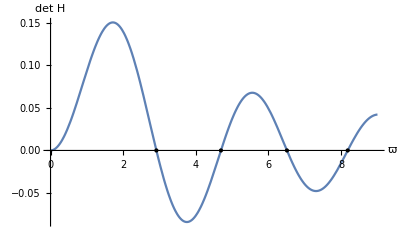

```mathematica
Show[{
Plot[detΗ[ϖ, -1, 1], {ϖ, 0, 9}, AxesLabel -> {"ϖ", "det Η"}],
Graphics[{PointSize[Large], Point[{#, 0}]}& /@ accurateηϖ]
}]
```

Having found such ϖ that det Η[ϖ, σ_0, σ_p] ≈ 0, we now need to compute C_0, C_1, C_2, C_3. If det Η[ϖ, σ_0, σ_p] was exactly zero, we could compute these constants by finding the nullspace of Η. However, since the determinant is only approximately zero, the matrix is nonsingular, and what we are looking for is not the nullspace but a “nullspace with margins”. As we saw in the previous section, the “nullspace with margins” can be computed using the function minVector, and the constants are then given by {C_0, C_1, C_2, C_3} = minVector[Η]. According to the formula (107), we have η_n[σ] = C_0 η_0[ϖ_n, σ] + C_1 η_1[ϖ_n, σ] + C_2 η_2[ϖ_n, σ] + C_3 η_3[ϖ_n, σ].

```mathematica
ClearAll[computeηNmode];
computeηNmode[ϖ_, σ0_, σp_] := Block[
	{
		range = Max[-σ0, σp],
		η0, η1, η2, η3,
		Η, C0, C1, C2, C3
	},
	{η0, η1, η2, η3} = findη0123[ϖ, "Range" -> range];
	Η = Ηmatrix[ϖ, σ0, σp, η0, η1, η2, η3];
	{C0, C1, C2, C3} = minVector[Η];
	
	If[range ≤ 1,
		Function[σ, Module[{ξ = √(1 + σ^2) - 1}, Null]] /. Null -> Expand[C0 η0[[2, 2]] + C1 η1[[2, 2]] + C2 η2[[2, 2]] + C3 η3[[2, 2]]],
		Function[σ, Null] /. Null -> C0 η0[[2]] + C1 η1[[2]] + C2 η2[[2]] + C3 η3[[2]]
	]
];
```

```mathematica
ClearAll[findηNmodes];
Options[findηNmodes] = {"ϖmin" -> 0.2, "dϖ" -> 0.1, "OutputForm" -> All};
findηNmodes[σ0_, σp_, nmodes_, OptionsPattern[]] := Block[
	{
		ϖmin = OptionValue["ϖmin"], dϖ = OptionValue["dϖ"],
		currϖ, pastϖ, newϖ,
		currdetΗ, pastdetΗ,
		output = {}, counter = 0
	},
	currϖ = ϖmin;
	
	pastϖ = currϖ - dϖ;
	pastdetΗ = detΗ[pastϖ, σ0, σp];
	
	While[counter < nmodes,
		currdetΗ = detΗ[currϖ, σ0, σp];
		
		If[Sign[currdetΗ] ≠ Sign[pastdetΗ],
			counter++;
			
			If[(SameQ[OptionValue["OutputForm"], All]) || (counter == nmodes),
				pastϖ = currϖ - dϖ;
				pastdetΗ = detΗ[currϖ - dϖ, σ0, σp];
				While[(Abs[currdetΗ] > 10^-12) && (currdetΗ ≠ pastdetΗ),
					newϖ = (currdetΗ pastϖ - pastdetΗ currϖ)/(currdetΗ - pastdetΗ);  (* compute newϖ *)
							
					pastϖ = currϖ;  (* update past to curr *)
					pastdetΗ = currdetΗ;
				
					currϖ = newϖ;  (* update curr to new *)
					currdetΗ = detΗ[newϖ, σ0, σp];
				];
				
				Switch[OptionValue["OutputForm"],
					All, AppendTo[output, {currϖ, computeηNmode[currϖ, σ0, σp]}],
					Last, output = {currϖ, computeηNmode[currϖ, σ0, σp]}; Break[]
				];
				
				currϖ += dϖ;
				currdetΗ = detΗ[currϖ, σ0, σp];
			];
		];
		
		pastdetΗ = currdetΗ;
		
		currϖ += dϖ;
	];
	
	output
];
```

Here is how we can compute the first four normal modes with σ_0 = -1, σ_p = 1:

```mathematica
findηNmodes[-1, 1, 4]
```

{{2.91391,Function[σ,Module[{ξ=√(1+σ^2)-1},-5.56437×10^-16+2.1046×10^-15 ξ-3.77942×10^-15 ξ^2+3.45579×10^-15 ξ^3-2.5882×10^-15 ξ^4+2.31216×10^-15 ξ^5-2.35429×10^-15 ξ^6+2.41135×10^-15 ξ^7-2.43427×10^-15 ξ^8+2.44091×10^-15 ξ^9-2.44274×10^-15 ξ^10+2.44329×10^-15 ξ^11-2.44348×10^-15 ξ^12+2.44355×10^-15 ξ^13-2.44358×10^-15 ξ^14+2.44359×10^-15 ξ^15-2.4436×10^-15 ξ^16+2.4436×10^-15 ξ^17-2.4436×10^-15 ξ^18+2.4436×10^-15 ξ^19-2.4436×10^-15 ξ^20+2.4436×10^-15 ξ^21-2.4436×10^-15 ξ^22+2.4436×10^-15 ξ^23-2.4436×10^-15 ξ^24+2.4436×10^-15 ξ^25-2.4436×10^-15 ξ^26+2.4436×10^-15 ξ^27-2.4436×10^-15 ξ^28+2.4436×10^-15 ξ^29-2.4436×10^-15 ξ^30+2.4436×10^-15 ξ^31-2.4436×10^-15 ξ^32+2.4436×10^-15 ξ^33-2.4436×10^-15 ξ^34+2.4436×10^-15 ξ^35-2.4436×10^-15 ξ^36+2.4436×10^-15 ξ^37-2.4436×10^-15 ξ^38+2.4436×10^-15 ξ^39-2.4436×10^-15 ξ^40+2.56545×10^-15 ξ^41-0.117597 √ξ Sign[σ]+0.469772 ξ^(3/2) Sign[σ]-0.58997 ξ^(5/2) Sign[σ]+0.442112 ξ^(7/2) Sign[σ]-0.339213 ξ^(9/2) Sign[σ]+0.32841 ξ^(11/2) Sign[σ]-0.339941 ξ^(13/2) Sign[σ]+0.346627 ξ^(15/2) Sign[σ]-0.348822 ξ^(17/2) Sign[σ]+0.349427 ξ^(19/2) Sign[σ]-0.349599 ξ^(21/2) Sign[σ]+0.349656 ξ^(23/2) Sign[σ]-0.349676 ξ^(25/2) Sign[σ]+0.349684 ξ^(27/2) Sign[σ]-0.349687 ξ^(29/2) Sign[σ]+0.349689 ξ^(31/2) Sign[σ]-0.349689 ξ^(33/2) Sign[σ]+0.34969 ξ^(35/2) Sign[σ]-0.34969 ξ^(37/2) Sign[σ]+0.34969 ξ^(39/2) Sign[σ]-0.34969 ξ^(41/2) Sign[σ]+0.34969 ξ^(43/2) Sign[σ]-0.34969 ξ^(45/2) Sign[σ]+0.34969 ξ^(47/2) Sign[σ]-0.34969 ξ^(49/2) Sign[σ]+0.34969 ξ^(51/2) Sign[σ]-0.34969 ξ^(53/2) Sign[σ]+0.34969 ξ^(55/2) Sign[σ]-0.34969 ξ^(57/2) Sign[σ]+0.34969 ξ^(59/2) Sign[σ]-0.34969 ξ^(61/2) Sign[σ]+0.34969 ξ^(63/2) Sign[σ]-0.34969 ξ^(65/2) Sign[σ]+0.34969 ξ^(67/2) Sign[σ]-0.34969 ξ^(69/2) Sign[σ]+0.34969 ξ^(71/2) Sign[σ]-0.34969 ξ^(73/2) Sign[σ]+0.34969 ξ^(75/2) Sign[σ]-0.34969 ξ^(77/2) Sign[σ]+0.34969 ξ^(79/2) Sign[σ]-0.34969 ξ^(81/2) Sign[σ]+0.368765 ξ^(83/2) Sign[σ]]]},{4.69156,Function[σ,Module[{ξ=√(1+σ^2)-1},0.0456866-0.998956 ξ+4.17822 ξ^2-6.91477 ξ^3+6.0656 ξ^4-3.73189 ξ^5+2.70899 ξ^6-2.88387 ξ^7+3.23249 ξ^8-3.39085 ξ^9+3.42453 ξ^10-3.42356 ξ^11+3.41982 ξ^12-3.418 ξ^13+3.41733 ξ^14-3.41711 ξ^15+3.41703 ξ^16-3.417 ξ^17+3.41699 ξ^18-3.41699 ξ^19+3.41699 ξ^20-3.41698 ξ^21+3.41698 ξ^22-3.41698 ξ^23+3.41698 ξ^24-3.41698 ξ^25+3.41698 ξ^26-3.41698 ξ^27+3.41698 ξ^28-3.41698 ξ^29+3.41698 ξ^30-3.41698 ξ^31+3.41698 ξ^32-3.41698 ξ^33+3.41698 ξ^34-3.41698 ξ^35+3.41698 ξ^36-3.41698 ξ^37+3.41698 ξ^38-3.41698 ξ^39+3.41698 ξ^40-3.53287 ξ^41]]},{6.50813,Function[σ,Module[{ξ=√(1+σ^2)-1},-0.0313019 √ξ Sign[σ]+0.471289 ξ^(3/2) Sign[σ]-2.12193 ξ^(5/2) Sign[σ]+4.37671 ξ^(7/2) Sign[σ]-4.89499 ξ^(9/2) Sign[σ]+3.22911 ξ^(11/2) Sign[σ]-1.51846 ξ^(13/2) Sign[σ]+1.1294 ξ^(15/2) Sign[σ]-1.54453 ξ^(17/2) Sign[σ]+1.93397 ξ^(19/2) Sign[σ]-2.07091 ξ^(21/2) Sign[σ]+2.07322 ξ^(23/2) Sign[σ]-2.05148 ξ^(25/2) Sign[σ]+2.03895 ξ^(27/2) Sign[σ]-2.0347 ξ^(29/2) Sign[σ]+2.03372 ξ^(31/2) Sign[σ]-2.03358 ξ^(33/2) Sign[σ]+2.03359 ξ^(35/2) Sign[σ]-2.0336 ξ^(37/2) Sign[σ]+2.03361 ξ^(39/2) Sign[σ]-2.03361 ξ^(41/2) Sign[σ]+2.03361 ξ^(43/2) Sign[σ]-2.03361 ξ^(45/2) Sign[σ]+2.03361 ξ^(47/2) Sign[σ]-2.03361 ξ^(49/2) Sign[σ]+2.03361 ξ^(51/2) Sign[σ]-2.03361 ξ^(53/2) Sign[σ]+2.03361 ξ^(55/2) Sign[σ]-2.03361 ξ^(57/2) Sign[σ]+2.03361 ξ^(59/2) Sign[σ]-2.03361 ξ^(61/2) Sign[σ]+2.03361 ξ^(63/2) Sign[σ]-2.03361 ξ^(65/2) Sign[σ]+2.03361 ξ^(67/2) Sign[σ]-2.03361 ξ^(69/2) Sign[σ]+2.03361 ξ^(71/2) Sign[σ]-2.03361 ξ^(73/2) Sign[σ]+2.03361 ξ^(75/2) Sign[σ]-2.03361 ξ^(77/2) Sign[σ]+2.03361 ξ^(79/2) Sign[σ]-2.03361 ξ^(81/2) Sign[σ]+2.23362 ξ^(83/2) Sign[σ]]]},{8.1811,Function[σ,Module[{ξ=√(1+σ^2)-1},0.0129861-0.999916 ξ+11.6802 ξ^2-53.3984 ξ^3+124.874 ξ^4-167.108 ξ^5+131.27 ξ^6-56.8202 ξ^7+15.5724 ξ^8-22.6942 ξ^9+45.872 ξ^10-59.6713 ξ^11+62.1699 ξ^12-60.4157 ξ^13+58.8164 ξ^14-58.1691 ξ^15+58.0375 ξ^16-58.0497 ξ^17+58.0724 ξ^18-58.0836 ξ^19+58.0876 ξ^20-58.0888 ξ^21+58.0891 ξ^22-58.0892 ξ^23+58.0893 ξ^24-58.0893 ξ^25+58.0893 ξ^26-58.0893 ξ^27+58.0893 ξ^28-58.0893 ξ^29+58.0893 ξ^30-58.0893 ξ^31+58.0893 ξ^32-58.0893 ξ^33+58.0893 ξ^34-58.0893 ξ^35+58.0893 ξ^36-58.0893 ξ^37+58.0893 ξ^38-58.0893 ξ^39+58.0893 ξ^40-58.8405 ξ^41]]}}

Compute the first normal mode with σ_0 = -1, σ_p = 1:

```mathematica
exampleηnm = findηNmodes[-1, 1, 1, OutputForm -> Last]
```

{2.91391,Function[σ,Module[{ξ=√(1+σ^2)-1},-5.56437×10^-16+2.1046×10^-15 ξ-3.77942×10^-15 ξ^2+3.45579×10^-15 ξ^3-2.5882×10^-15 ξ^4+2.31216×10^-15 ξ^5-2.35429×10^-15 ξ^6+2.41135×10^-15 ξ^7-2.43427×10^-15 ξ^8+2.44091×10^-15 ξ^9-2.44274×10^-15 ξ^10+2.44329×10^-15 ξ^11-2.44348×10^-15 ξ^12+2.44355×10^-15 ξ^13-2.44358×10^-15 ξ^14+2.44359×10^-15 ξ^15-2.4436×10^-15 ξ^16+2.4436×10^-15 ξ^17-2.4436×10^-15 ξ^18+2.4436×10^-15 ξ^19-2.4436×10^-15 ξ^20+2.4436×10^-15 ξ^21-2.4436×10^-15 ξ^22+2.4436×10^-15 ξ^23-2.4436×10^-15 ξ^24+2.4436×10^-15 ξ^25-2.4436×10^-15 ξ^26+2.4436×10^-15 ξ^27-2.4436×10^-15 ξ^28+2.4436×10^-15 ξ^29-2.4436×10^-15 ξ^30+2.4436×10^-15 ξ^31-2.4436×10^-15 ξ^32+2.4436×10^-15 ξ^33-2.4436×10^-15 ξ^34+2.4436×10^-15 ξ^35-2.4436×10^-15 ξ^36+2.4436×10^-15 ξ^37-2.4436×10^-15 ξ^38+2.4436×10^-15 ξ^39-2.4436×10^-15 ξ^40+2.56545×10^-15 ξ^41-0.117597 √ξ Sign[σ]+0.469772 ξ^(3/2) Sign[σ]-0.58997 ξ^(5/2) Sign[σ]+0.442112 ξ^(7/2) Sign[σ]-0.339213 ξ^(9/2) Sign[σ]+0.32841 ξ^(11/2) Sign[σ]-0.339941 ξ^(13/2) Sign[σ]+0.346627 ξ^(15/2) Sign[σ]-0.348822 ξ^(17/2) Sign[σ]+0.349427 ξ^(19/2) Sign[σ]-0.349599 ξ^(21/2) Sign[σ]+0.349656 ξ^(23/2) Sign[σ]-0.349676 ξ^(25/2) Sign[σ]+0.349684 ξ^(27/2) Sign[σ]-0.349687 ξ^(29/2) Sign[σ]+0.349689 ξ^(31/2) Sign[σ]-0.349689 ξ^(33/2) Sign[σ]+0.34969 ξ^(35/2) Sign[σ]-0.34969 ξ^(37/2) Sign[σ]+0.34969 ξ^(39/2) Sign[σ]-0.34969 ξ^(41/2) Sign[σ]+0.34969 ξ^(43/2) Sign[σ]-0.34969 ξ^(45/2) Sign[σ]+0.34969 ξ^(47/2) Sign[σ]-0.34969 ξ^(49/2) Sign[σ]+0.34969 ξ^(51/2) Sign[σ]-0.34969 ξ^(53/2) Sign[σ]+0.34969 ξ^(55/2) Sign[σ]-0.34969 ξ^(57/2) Sign[σ]+0.34969 ξ^(59/2) Sign[σ]-0.34969 ξ^(61/2) Sign[σ]+0.34969 ξ^(63/2) Sign[σ]-0.34969 ξ^(65/2) Sign[σ]+0.34969 ξ^(67/2) Sign[σ]-0.34969 ξ^(69/2) Sign[σ]+0.34969 ξ^(71/2) Sign[σ]-0.34969 ξ^(73/2) Sign[σ]+0.34969 ξ^(75/2) Sign[σ]-0.34969 ξ^(77/2) Sign[σ]+0.34969 ξ^(79/2) Sign[σ]-0.34969 ξ^(81/2) Sign[σ]+0.368765 ξ^(83/2) Sign[σ]]]}

To verify that this is indeed a normal mode of (90) that satisfies the boundary conditions, we can plug it in and see what happens. Ideally, the result should be zero. First, check the ODE (103):

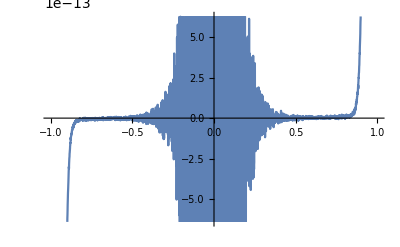

```mathematica
Block[
	{
		soln = Evaluate@exampleηnm[[2]][σ], err
	},
	err = ((1 + σ^2)^(3/2)η''''[σ] + 7 σ √(1 + σ^2)η'''[σ] + (ϖ^2(1 + σ^2) + (7 + 10 σ^2)/(√(1 + σ^2)))η''[σ] +
				(4 ϖ^2 σ - (σ (1 - 2 σ^2))/((1 + σ^2)^(3/2)))η'[σ] + (ϖ^2(1 + 2 σ^2)/(1 + σ^2) - (2 (1 - 2 σ^2))/((1 + σ^2)^(5/2)))η[σ]) /. {
			ϖ -> exampleηnm[[1]],
			η[σ] -> soln,
			Derivative[1][η][σ] -> D[soln, {σ, 1}],
			Derivative[2][η][σ] -> D[soln, {σ, 2}],
			Derivative[3][η][σ] -> D[soln, {σ, 3}],
			Derivative[4][η][σ] -> D[soln, {σ, 4}]
		} /. {Derivative[d_][Sign][x_] -> 0};
	Plot[err, {σ, -1, 1}]
]
```

And then the boundary conditions (92):

```mathematica
Block[
	{
		ϖ = exampleηnm[[1]], η = exampleηnm[[2]],
		B
	},
	B = Function[η, Function[σ, Null] /. Null -> (
			√(1 + σ^2)D[η, {σ, 3}] + (4 σ)/(√(1 + σ^2))D[η, {σ, 2}] + (ϖ^2 + (3 + 2 σ^2)/((1 + σ^2)^(3/2)))D[η, σ] /. Derivative[d_][Sign][x_] -> 0)
		];
	{
		η[-1], η[1],  (* η[Subscript[σ, 0]], η[Subscript[σ, p]] *)
		B[Evaluate@η[[2]]][-1], B[Evaluate@η[[2]]][1]  (* B^̑ η[Subscript[σ, 0]], B^̑ η[Subscript[σ, p]] *)
	}
]
```

{4.82838×10^-16,-7.70572×10^-16,2.88658×10^-15,2.63678×10^-15}

As we can see, the Frobenius’s method solution satisfies the ODE and the boundary conditions very accurately. Although a solution given by NDSolve is less accurate, it is still pretty decent:

```mathematica
exampleηnm2 = findηNmodes[-2, 2, 1, OutputForm -> Last]
```

{1.43852,Function[σ,0.+0.985242 Sign[σ] InterpolatingFunction[…][Abs[σ]]-0.171167 Sign[σ] InterpolatingFunction[…][Abs[σ]]]}

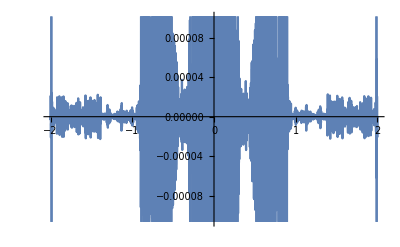

```mathematica
Block[
	{
		soln = exampleηnm2[[2]][σ], err
	},
	err = ((1 + σ^2)^(3/2)η''''[σ] + 7 σ √(1 + σ^2)η'''[σ] + (ϖ^2(1 + σ^2) + (7 + 10 σ^2)/(√(1 + σ^2)))η''[σ] +
				(4 ϖ^2 σ - (σ (1 - 2 σ^2))/((1 + σ^2)^(3/2)))η'[σ] + (ϖ^2(1 + 2 σ^2)/(1 + σ^2) - (2 (1 - 2 σ^2))/((1 + σ^2)^(5/2)))η[σ]) /. {
			ϖ -> exampleηnm2[[1]],
			η[σ] -> soln,
			Derivative[1][η][σ] -> D[soln, {σ, 1}],
			Derivative[2][η][σ] -> D[soln, {σ, 2}],
			Derivative[3][η][σ] -> D[soln, {σ, 3}],
			Derivative[4][η][σ] -> D[soln, {σ, 4}]
		} /. {
			Derivative[d_][Sign][x_] -> 0,
			Derivative[d_][Abs][x_] -> If[d == 1, Sign[x], 0]
		};
	Plot[err, {σ, -2, 2}]
]
```

```mathematica
Block[
	{
		ϖ = exampleηnm2[[1]], η = exampleηnm2[[2]],
		B
	},
	B = Function[η, Function[σ, Null] /. Null -> (
			√(1 + σ^2)D[η, {σ, 3}] + (4 σ)/(√(1 + σ^2))D[η, {σ, 2}] + (ϖ^2 + (3 + 2 σ^2)/((1 + σ^2)^(3/2)))D[η, σ] /. {
				Derivative[d_][Sign][x_] -> 0,
				Derivative[d_][Abs][x_] -> If[d == 1, Sign[x], 0]
			})
		];
	{
		η[-2], η[2],  (* η[Subscript[σ, 0]], η[Subscript[σ, p]] *)
		B[η[[2]]][-2], B[η[[2]]][2]  (* B^̑ η[Subscript[σ, 0]], B^̑ η[Subscript[σ, p]] *)
	}
]
```

{4.05231×10^-15,-4.05231×10^-15,-5.71765×10^-15,-5.71765×10^-15}

### How the boundary conditions lead to conservation of length for ϖ ≠ 0

We know that the cable’s ends are fixed, so u is zero at the boundaries, and the length of the cable is conserved. We can also show this directly using the equation (83) and the boundary conditions. By integrating (78) from 0 to L, what we get is

((((ρ∂^2/(∂t^2)[∂/(∂ζ)[R_e h]|)_0)^L - (∫^L)_0 k_e h dζ] = ∂/(∂ζ)[R_e∂/(∂ζ)[T_e(∂h)/(∂ζ)]] + (∂k_e)/(∂ζ)T_e h + 2 k_e T_e(∂h)/(∂ζ)|)_0)^L

Since h[t, 0] = h[t, L] = 0,

((((ρ∂^2/(∂t^2)[R_e(∂h)/(∂ζ)|)_0)^L - (∫^L)_0 k_e h dζ] = ∂/(∂ζ)[R_e∂/(∂ζ)[T_e(∂h)/(∂ζ)]] + 2 k_e T_e(∂h)/(∂ζ)|)_0)^L

Substituting (0 =  ∂/(∂ζ)[R_e∂/(∂ζ)[T_e(∂h)/(∂ζ)]] + 2 k_e T_e(∂h)/(∂ζ) - ρR_e∂^2/(∂t^2)(∂h)/(∂ζ)|)_(ζ = 0 || ζ = L) (86), what we get is

d^2/dt^2(∫^L)_0 k_e[ζ]h[t, ζ] dζ = 0

Now, if the cable is oscillating in a normal mode, h[t, ζ] = h_n[ζ] Cos[ω_n t], and the integral above becomes

ω_n^2(∫^L)_0 k_e[ζ]h_n[ζ] dζ = 0

For ω_n ≠ 0, this equation can only hold if the integral is zero:

(∫^L)_0 k_e[ζ]h_n[ζ] dζ = 0

This also happens to be the criterion that the cable’s length is equal to L (70):

(∫^L)_0 k_e[ζ]h[t, ζ] dζ = 0

We have shown that the boundary conditions (85) - (87) dictate that all normal modes of h with ω > 0 must conserve the cable’s length. Because the dimensionless variables τ, σ, η are obtained from t, ζ, h by rescaling and changing constants, we conclude that the normal modes of the equation for η (83) with nonzero ϖ will also conserve length.
	For ϖ = 0, the story is a bit different: the integral (∫^L)_0 k_e[ζ]h_n[ζ] dζ is no longer zero, and length is not conserved - hence the curious paradox explored below.

### The normal mode ϖ = 0 and why it’s impossible, or why integration constants matter

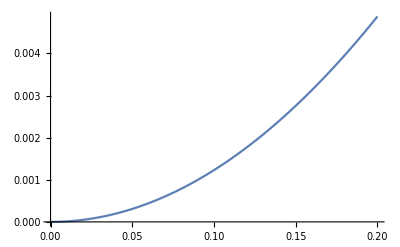

```mathematica
Plot[detΗ[ϖ, -1, 1], {ϖ, 0, 0.2}]
```

Above you can see the plot of det Η as a function of ϖ for σ_0 = -1, σ_p = 1. It can be seen that det Η is actually zero for ϖ = 0. We can re-plot the function with different parameters σ_0 and σ_p and the result will still be the same because ϖ = 0 always is one of the allowed frequencies of (109) (although the associated h violates conservation of length). Below is given a chain of arguments that allows one to determine the normal mode η_0[σ] of (90) that corresponds to ϖ = 0. The resulting function is proven to satisfy the equation (103) and the boundary conditions (92) by actually plugging it in; the derivation below, on the other hand, is not a rigorous proof but instead is based on intuition and several assumptions.

#### Derivation

To find η_0, let us remember that a normal mode with zero frequency is a stationary state, or basically an equilibrium. Thus, the zero-frequency normal mode of η would  correspond to an equilibrium configuration of the cable that is different from η = 0 everywhere. From the first glance this does not make any sense: if you play with a hanging cable for a bit you will shortly see that it only has one equilibrium configuration. The explanation for this paradox is that so far we have only imposed on η the length conservation law in its differential form, which is that the tangential speed u is zero at both ends (84) and hence the length of the cable doesn’t  change with time. But this way we can add any constant ΔL to the cable’s length and the cable will still be in equilibrium.
	The hypothesis is that the zeroth normal mode of η corresponds to adding some constant to the cable’s length. And so, the shape of a cable “oscillating” in the zeroth normal mode η[τ, σ] = η_0[σ] will be the same as that of a cable with the same x_p and z_p as the original cable but different L being at the state η[τ, σ] = 0.

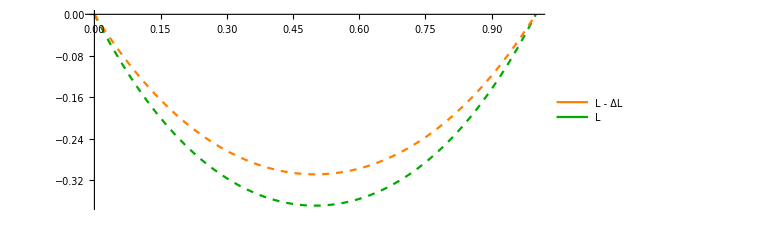

```mathematica
With[{xp = 1, zp = 0, L = 1.3, ΔL = 0.08}, Legended[
	Show[{
		drawCable[xp, zp, L, PlotStyle -> {Dashed, Darker@Green}],
		drawCable[xp, zp, L - ΔL, PlotStyle -> {Dashed, Orange}]
	}, ImageSize -> Large],
	LineLegend[{Orange, Darker@Green},{"L - ΔL", "L"}]
]]
```

The figure above shows two cables in the state h = 0, one with parameters x_p, z_p, L, and the other with parameters x_p, z_p, L - ΔL. The hypothesis is that the cable with length L - ΔL is also the state h[ζ] = C h_0[ζ] of the cable with length L. (spoiler alert: the hypothesis is true, and in fact the arrows on the figure below were calculated using this hypothesis; the slight mismatch between the arrows and the orange cable is because the arrows were computed as a first-order approximation, and since the distance between the green and orange cables is finite, there is some error due to quadratic terms)

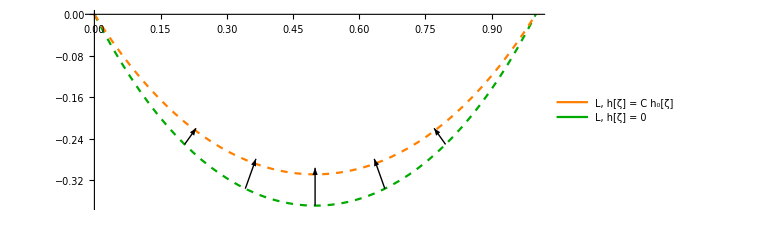

Let us compute the shape of the cable with length L + ΔL and then find such h[ζ] that would change the green cable to the orange cable (fig. above) and check whether it satisfies the equation (103) with ϖ = 0. For that, we can use the formula (14), that says that the configuration h = y = 0 of a cable can in Cartesian coordinates be described as

z[x] = Λ (Cosh[(x - x_0)/Λ] - Cosh[x_0/Λ])

where x_0 and Λ are constants determined by the conditions (22) and (23):

L = Λ (Sinh[(x_p - x_0)/Λ] + Sinh[x_0/Λ])
z_p = Λ (Cosh[(x_p - x_0)/Λ] - Cosh[x_0/Λ])

Changing L to L' = L + dL, we obtain the following formula for z'[x] - z[x] = dz as a function of x, which represents the difference between the two shapes:

dz[x]  ∝ Cosh[(x - x_0)/Λ] - Cosh[x_0/Λ] - (x - x_0)/Λ Sinh[(x - x_0)/Λ] + x_0/Λ Sinh[x_0/Λ] - α(Sinh[(x - x_0)/Λ] + Sinh[x_0/Λ])

where α ≡ (z_p/L - (1 - z_p^2/L^2)ArcTanh[z_p/L] - z_p/L^2((x_p - x_0)Cosh[(x_p -  x_0)/Λ] + x_0 Cosh[x_0/Λ])) and σ = Sinh[(x - x_0)/Λ] is given by (88). From here, h can be found graphically by examining a small section of the cable. The figure below shows the two configurations compared to each other. If we take a point with coordinate x on the green cable and a point with coordinate x on the orange cable, the distance between them would be dz[x]. And since h is measured perpendicularly to the ζ axis, which is the line y = h =0, which is also the green line drawn below, we see that h is simply the distance between the two lines.

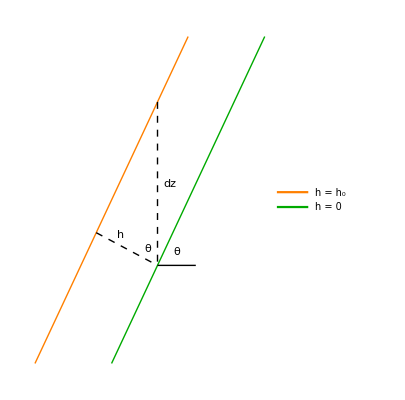

Now, if we denote θ the angle between the green line and the horizontal, it can be seen that dz/dx = Tan[θ]; and since according to (14), dz/dx = Sinh[(x - x_0)/Λ], Tan[θ] = Sinh[(x - x_0)/Λ] and Cos[θ] = 1/Cosh[(x - x_0)/Λ]. But we can also see that θ is the angle between the dashed line with length dz and the dashed line with length h. And since h is measured perpendicularly to the green line and the green line is parallel to the orange line, we have h = dz Cos[θ]. Substituting the results above and changing ζ, h to σ, η we get the formula for η_0[σ].

η_0[σ] = 1 - (√(1 + σ_0^2))/(√(1 + σ^2)) - (σ ArcSinh[σ])/(√(1 + σ^2)) + (σ_0 ArcSinh[σ_0])/(√(1 + σ^2)) - α(σ - σ_0)/(√(1 + σ^2))

#### Verifying that η_0[σ] satisfies (103) and (92)

The code below plugs in (110) into the equation (103) with ϖ = 0. You can see that the output is exactly zero, so (110) does satisfy (103) with ϖ = 0.

```mathematica
Block[{L, xp, zp, Λ, x0, σ0, η, σ}, Simplify[
	-(2 (-1+2 σ^2) η[σ])/((1+σ^2)^(5/2))+((σ-2 σ^3) η'[σ]-(1+σ^2) ((7+10 σ^2) η''[σ]+(1+σ^2) (7 σ Derivative[3][η][σ]+(1+σ^2) Derivative[4][η][σ])))/((1+σ^2)^(3/2)) /.
		η -> Function[σ, 1 - (√(1 + σ0^2))/(√(1 + σ^2)) - (σ ArcSinh[σ])/(√(1 + σ^2)) + (σ0 ArcSinh[σ0])/(√(1 + σ^2)) - 
			(zp/L - (1 - zp^2/L^2)ArcTanh[zp/L] - zp/L^2((xp - x0)Cosh[(xp- x0)/Λ] + x0 Cosh[x0/Λ]))(σ - σ0)/(√(1 + σ^2))]
]]
```

0

Furthermore, we can plug it into the boundary conditions (92), and it again passes:

```mathematica
Block[
	{
		ϖ = 0, η = Function[σ, 1 - (√(1 + σ0^2))/(√(1 + σ^2)) - (σ ArcSinh[σ])/(√(1 + σ^2)) + (σ0 ArcSinh[σ0])/(√(1 + σ^2)) - 
				(zp/L - (1 - zp^2/L^2)ArcTanh[zp/L] - zp/L^2((xp - x0)Cosh[(xp- x0)/Λ] + x0 Cosh[x0/Λ]))(σ - σ0)/(√(1 + σ^2))],
		B
	},
	B = Function[η, Function[σ, Null] /. Null -> (
			√(1 + σ^2)D[η, {σ, 3}] + (4 σ)/(√(1 + σ^2))D[η, {σ, 2}] + (ϖ^2 + (3 + 2 σ^2)/((1 + σ^2)^(3/2)))D[η, σ] /. Derivative[d_][Sign][x_] -> 0)
		];
	Simplify[
		{
			η[σ0], η[σp],  (* η[Subscript[σ, 0]], η[Subscript[σ, p]] *)
			B[η[[2]]][σ0], B[η[[2]]][σp]  (* B^̑ η[Subscript[σ, 0]], B^̑ η[Subscript[σ, p]] *)
		} /. {σ0 -> Sinh[-x0/Λ], σp -> Sinh[(xp - x0)/Λ], L -> Λ (Sinh[(xp - x0)/Λ] + Sinh[x0/Λ]), zp -> Λ (Cosh[(xp - x0)/Λ] - Cosh[x0/Λ])},
		Assumptions -> {x0 ∈ Reals, xp ∈ Reals, Λ > 0}
	]
]
```

{0,0,0,0}

But from physical intuition, a normal mode with ϖ = 0 does not make any sense - it would mean that there are many equilibrium states for a given cable. And indeed, although (110) satisfies the boundary conditions (92), it does not satisfy all the boundary conditions.

#### The forgotten condition: length is equal to L

The boundary conditions (86), and, consequently, (92) (which is the dimensionless form of (87)), ensure that that the cable’s ends are fixed, so the cable’s length does not change in time. However, they do not say anything about what the cable’s length should be; if, for some reason, the cable’s length was equal to L' ≠ L but would not change in time, this would not violate (92): the cable’s length is constant, so its ends are not moving, so everything’s fine. But we want the cable’s length to be L - that was the definition of L. In this sense, the condition (92) is too weak. To supplement it, we can directly demand that ∫dl = L; as it turns out, we have already done that in the section “Conservation of length”, and what  this gave us is

(∫^L)_0 k_e[ζ]h[t, ζ] dζ = 0

Substituting k_e = 1/Λ 1/(1 + ((ζ - l_0)/Λ)^2) and h = Λ η (88), we get

(∫^σ_p)_σ_0(η[τ, σ] dσ)/(1 + σ^2)= 0

But there is no reason to expect it to be zero for (110), and in general the integral is nonzero. An easy way to see that is that when deriving (110), we looked at what happens if we change the cable’s length slightly, so change of length is innate in (110). Thus, we see that although (110) satisfies the normal mode equation (103) and does indeed preserve the rope’s length (92), it does not satisfy a stronger boundary condition that says that the cable’s length must be equal to L. □

#### Code used to generate the figures

```mathematica
Block[{xp = 1, zp = 0, L = 1.3, ΔL = 0.08, Λ, x0, l0, σ0, h, η},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	l0 = Λ Sinh[x0/Λ];
	σ0 = -l0/Λ;
	
	η = Function[σ, 1 - (√(1 + σ0^2))/(√(1 + σ^2)) - (σ ArcSinh[σ])/(√(1 + σ^2)) + (σ0 ArcSinh[σ0])/(√(1 + σ^2)) - 
		(zp/L - (1 - zp^2/L^2)ArcTanh[zp/L] - zp/L^2((xp - x0)Cosh[(xp- x0)/Λ] + x0 Cosh[x0/Λ]))(σ - σ0)/(√(1 + σ^2))];
	h = Function[ζ, (findLambda[L - ΔL, xp, zp] - findLambda[L, xp, zp]) η[(ζ - l0)/Λ]];
	
	Legended[
	Show[Append[
		{
			drawCable[xp, zp, L, PlotStyle -> {Dashed, Darker@Green}],
			drawCable[xp, zp, L - ΔL, PlotStyle -> {Dashed, Orange}]
		},
		Graphics@Table[
			{Arrowheads[0.02], Arrow[{#, # + {-(ζ - l0)/Λ, 1}/(√(1 + (ζ - l0)^2/Λ^2)) h[ζ]}]}&@{
				x0 + Λ ArcSinh[(ζ - l0)/Λ],
				Λ (√(1 + ((ζ - l0)/Λ)^2) - √(1 + (l0/Λ)^2))
			},
			{ζ, 2/8 L, 6/8 L, L/8}
		]
	], ImageSize -> Large],
	LineLegend[{Orange, Darker@Green},{"L,    h[ζ] = C h_0[ζ]", "L,    h[ζ] = 0"}]
]]
```

```mathematica
Legended[With[{X = 1, x = 0.8, δ = 0.5, s = 2}, Graphics[{
	{Thick, Orange, Line[{{0, 0}, {X, s X}}]},
	{Thick, Darker@Green, Line[{{δ, 0}, {X + δ, s X}}]},
	{Thick, Dashed, Line[{{x, s x}, {x, s (x - δ)}}]},
	{Style[Text["dz", {x + δ/6, s (x - δ/2)}], 14]},
	{Thick, Dashed, Line[{{x, s (x - δ)} - {1, -1/s}(δ s^2)/(1 + s^2), {x, s (x - δ)}}]},
	{Style[Text["h", {x - δ/4, s (x - δ)} - 1/2{1, -1/s}(δ s^2)/(1 + s^2) + δ/6], 14]},
	{Line[{{x, s (x - δ)}, {x + δ/2, s (x - δ)}}]},
	{Style[Text["θ", {x + δ/4, s (x - δ) + δ/6}], 14]},
	{Style[Text["θ", {x - δ/8, s (x - δ) + δ/5}], 14]}
}]], LineLegend[{Orange, Darker@Green}, {"h = h_0", "h = 0"}]]
```

## Nonlocality of in-plane oscillations

The equation (35) describing in-plane oscillations reads

∂^2/(∂τ^2)[(1+2 σ^2)/(1+σ^2)η + 4 σ(∂η)/(∂σ) + (1+σ^2)(∂^2 η)/(∂σ^2)] = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

Notice that the left-hand-side does not only contain (∂^2 η)/(∂σ^2) but also contains ∂/(∂σ)(∂^2 η)/(∂τ^2) and ∂^2/(∂σ^2)(∂^2 η)/(∂σ^2). To make it more apparent, we can re-write the equation as

{(1+2 σ^2)/(1+σ^2) + 4 σ∂/(∂σ) + (1+σ^2)∂^2/(∂σ^2)}(∂^2 η)/(∂τ^2) = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

Knowing the cable’s shape η[τ_0, σ] at some instant τ_0, we can calculate the accelerations of its components at that instant ∂^2/(∂τ^2)η[τ_0, σ]. Since we are interested in knowing the cable’s acceleration in some particular instant of time τ_0, let us denote η[σ] ≡ η[τ_0, σ] and η^(··)[σ] ≡ ∂^2/(∂τ^2)η[τ_0, σ]. In terms of these functions, the equation is written as

{(1+2 σ^2)/(1+σ^2) + 4 σ d/dσ + (1+σ^2)d^2/dσ^2}η^(··) = (1+σ^2)^(3/2)(d^4 η)/dσ^4 + 7 σ √(1+σ^2)(d^3 η)/dσ^3 + (7+10 σ^2)/(√(1+σ^2))(d^2 η)/dσ^2 - (σ (1-2 σ^2))/((1+σ^2)^(3/2))dη/dσ - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

We know the cable’s shape η and want to calculate its acceleration η^(··). Since η is known, the right-hand side of the above equation is also a known function, and we effectively get an ODE that allows us to find η^(··). And here is where nonlocality comes into play. To find acceleration as a function of position η^(··)[σ], we have to solve an ODE, which includes performing integration and using the boundary conditions. To see that this really does lead to nonlocality, let us look at the above equation for

η[σ] = Piecewise[{{12/(11 b^4)F[R + σ] - 36/(11 b^4)F[2/3 R + σ] + 24/(11 b^4)F[1/3 R + σ], σ ≤ 0}, {12/(11 b^4)F[R - σ] - 36/(11 b^4)F[2/3 R - σ] + 24/(11 b^4)F[1/3 R - σ], σ > 0}}]

where R > 0 is an arbitrary parameter and F[s] = Piecewise[{{s^4/24, 0≤s<R/3}, {-R^4/1944+(R^3 s)/162-(R^2 s^2)/36+(R s^3)/18, R/3≤s}}]. This makes η[σ] zero for |σ| > R and η, η', η'', η''' continuous. Below are the plots of η, η', η'', η''' for R = 1:

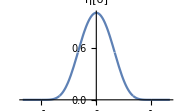
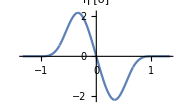
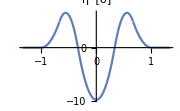
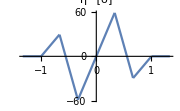

Plugging this into the equation, we can find what η^(··)[σ] is:

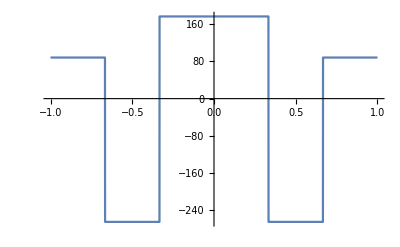

```mathematica
Plot[myf /. R -> 1, {σ, -1, 1}, PlotRange->All]
```

```mathematica
Expand[Simplify[(1944 F1[R/3-σ])/(11 R^4)-(2916 F2[(2 R)/3-σ])/(11 R^4)+(972 F3[R-σ])/(11 R^4) /. {F1 -> (0&), F2 -> (0&), F3 -> u} /. {u[s_] -> s^4/24, v[s_] -> -R^4/1944+(R^3 s)/162-(R^2 s^2)/36+(R s^3)/18}]]
```

81/22-(162 σ)/(11 R)+(243 σ^2)/(11 R^2)-(162 σ^3)/(11 R^3)+(81 σ^4)/(22 R^4)

```mathematica
Piecewise[{{1-(54 σ^2)/(11 R^2)+(81 σ^4)/(11 R^4), 0 ≤ σ < R/3}, {17/22+(30 σ)/(11 R)-(189 σ^2)/(11 R^2)+(270 σ^3)/(11 R^3)-(243 σ^4)/(22 R^4), R/3 ≤ σ < (2R)/3}, {81/22-(162 σ)/(11 R)+(243 σ^2)/(11 R^2)-(162 σ^3)/(11 R^3)+(81 σ^4)/(22 R^4), (2R)/3 ≤ σ < R}, {0, R ≤ σ}}] /. {σ -> s, R -> 1}
```

Piecewise[{{1-(54 s^2)/11+(81 s^4)/11, 0≤s<1/3}, {17/22+(30 s)/11-(189 s^2)/11+(270 s^3)/11-(243 s^4)/22, 1/3≤s<2/3}, {81/22-(162 s)/11+(243 s^2)/11-(162 s^3)/11+(81 s^4)/22, 2/3≤s<1}, {0, True}}]

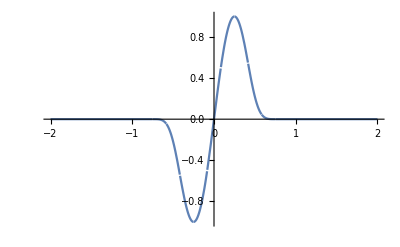

```mathematica
Block[
	{
		Bplus = Function[s, Piecewise[{{1-(54 s^2)/11+(81 s^4)/11, 0 ≤ s < 1/3}, {17/22+(30 s)/11-(189 s^2)/11+(270 s^3)/11-(243 s^4)/22, 1/3 ≤ s < 2/3}, {81/22-(162 s)/11+(243 s^2)/11-(162 s^3)/11+(81 s^4)/22, 2/3 ≤ s < 1}, {0, True}}]], B,
		R = 0.5
	},
	B = Function[s, Piecewise[{{Bplus[s], s ≥ 0}, {Bplus[-s], s < 0}}]];
	Plot[B[σ/R - 1/2] - B[σ/R + 1/2], {σ, -2, 2}, PlotRange -> All]
]
```

NDSolve::berr: The scaled boundary value residual error of 5.74203 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

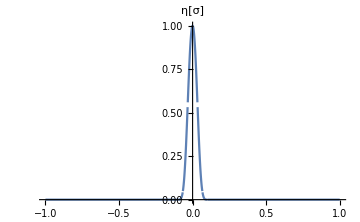
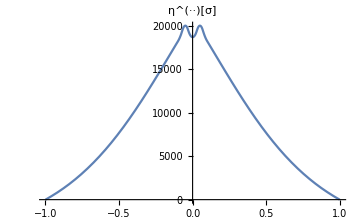

```mathematica
Block[
	{
		R = 0.1, σ0 = -1, σp = 1,
		F, η,
		RHS, intfunc, ηDDot
	},
	F = Function[s, Piecewise[{{s^4/24, 0 ≤ s < R/3}, {-R^4/1944+(R^3 s)/162-(R^2 s^2)/36+(R s^3)/18, R/3 ≤ s}, {0, True}}]];
	η = Piecewise[{{(1944 F[R/3+σ])/(11 R^4)-(2916 F[(2 R)/3+σ])/(11 R^4)+(972 F[R+σ])/(11 R^4), σ ≤ 0}, {(1944 F[R/3-σ])/(11 R^4)-(2916 F[(2 R)/3-σ])/(11 R^4)+(972 F[R-σ])/(11 R^4), σ > 0}}];
	RHS = (1+σ^2)^(3/2) D[η, {σ, 4}] + 7 σ √(1+σ^2) D[η, {σ, 3}] + (7+10 σ^2)/(√(1+σ^2)) D[η, {σ, 2}] - (σ (1-2 σ^2))/((1+σ^2)^(3/2)) D[η, σ] - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η;
	intfunc = With[{dσ = 0.01}, Interpolation[Table[{s, RHS /. σ -> s}, {s, σ0 - dσ/2, σp + dσ/2, dσ}], InterpolationOrder -> 4]];
	ηDDot = NDSolve[{(1+2 σ^2)/(1+σ^2)a[σ] + 4 σ a'[σ] + (1+σ^2)a''[σ] == intfunc[σ], a[-1] == 0, a[1] == 0}, a, {σ, σ0, σp}][[1, 1, 2]];
	{Plot[η, {σ, σ0, σp}, PlotRange -> All, ImageSize -> Medium, PlotLabel -> "η[σ]"],
	Plot[ηDDot[σ], {σ, σ0, σp}, ImageSize -> Medium, PlotLabel -> "η^(··)[σ]"]}
]
```

#### Code used to generate the figures

```mathematica
Block[{R = 1, F, η, Dη, DDη, DDDη}, F = Function[s, Piecewise[{{s^4/24, 0≤s<R/3}, {-R^4/1944+(R^3 s)/162-(R^2 s^2)/36+(R s^3)/18, R/3≤s}}]];
	η = Function[σ, Piecewise[{{(1944 F[R/3+σ])/(11 R^4)-(2916 F[(2 R)/3+σ])/(11 R^4)+(972 F[R+σ])/(11 R^4), σ≤0}, {(1944 F[R/3-σ])/(11 R^4)-(2916 F[(2 R)/3-σ])/(11 R^4)+(972 F[R-σ])/(11 R^4), σ>0}}]];
	{Dη, DDη, DDDη} = Table[D[η[σ], {σ, p}], {p, 1, 3}];
	{
		Plot[η[σ], {σ, -4/3 R, 4/3 R}, PlotLabel -> "η[σ]", ImageSize -> Small],
		Plot[Dη, {σ, -4/3 R, 4/3 R}, PlotLabel -> "η'[σ]", ImageSize -> Small],
		Plot[DDη, {σ, -4/3 R, 4/3 R}, PlotLabel -> "η''[σ]", ImageSize -> Small],
		Plot[DDDη, {σ, -4/3 R, 4/3 R}, PlotLabel -> "η'''[σ]", ImageSize -> Small]
	}
]
```

## Approximate algebraic expression for the normal frequencies and modes

The effects of the cable’s curvature on the propagation of waves are only significant if y[ζ] and h[ζ] vary on scales of the same order of magnitude as the cable’s radius of curvature. For high-frequency modes, the functions y[ζ] and h[ζ] vary on scales much smaller than the cable’s radius of curvature, and the cable can be thought of as being locally flat at each point. The waves would propagate as through a series of connected straight strings with constant tension. Let us try to use this principle to obtain an approximate solution to the equations (89) and (90).

### Normal modes ψ of (89)

For a straight wire, we know that the normal modes are precisely ψ[σ] = A Sin[κ(σ - σ_0)], where A is an arbitrary constant and κ = π/(σ_p - σ_0)n for n ∈ ℕ; for high n, κ becomes large as well. From physical intuition, we would expect to see something similar in a sagging cable. Given a normal mode of the equation (89), we can always write it in the form ψ[σ] = A[σ] Sin[ϕ[σ]]. And in fact, there are infinitely many ways to do that - take, for example, A[σ] = ψ[σ]/Sin[C], ϕ[σ] = C, where C can be any nonzero number. But let’s pick A and ϕ such that A ≈ const, dϕ/dσ ≈ const; this would be a mathematical statement of the fact that we are looking for a near-sinusoidal solution ψ[σ] ≈ C_1 Sin[C_2 σ]. The quantity dϕ/dσ will be very important in the calculations, so let us denote dϕ/dσ[σ] ≡ κ[σ]. For high-frequency modes, the phase changes very rapidly with position, so κ[σ] >> 1. Following the intuition from a tight string, high frequency normal modes correspond to the limit κ[σ] → ∞.
	Substituting ψ[σ] = A[σ] Sin[ϕ[σ]], we arrive at the following equation. Here k[σ] ≡ dϕ/dσ[σ].

(ϖ^2/κ^2 - √(1+σ^2)) κ^2 A Sin[ϕ] + (σ/(√(1+σ^2))κ A + 2 √(1+σ^2)  κ dA/dσ +√(1+σ^2)dκ/dσ A) Cos[ϕ] + (σ/(√(1+σ^2)) dA/dσ+√(1+σ^2)(d^2 A)/dσ^2)Sin[ϕ] = 0

The first term is of order κ^2, so it is much larger than the second term, which is of order κ, which is in turn much larger than the third term, which as no factors of κ in it. Since we are looking for an approximate solution for κ >> 1, we should first equate the first, potentially largest, term to zero. Doing so yields

κ ≈ ϖ/((1+σ^2)^(1/4))

Which tells us κ[σ] in terms of ϖ. Since κ[σ] ≡ dϕ/dσ[σ], integrating it with respect to σ gives back ϕ. Here the constant of integration can be determined from the fact that ψ[σ_0] = 0. There are many ways we could find A and ϕ satisfying the condition, but the natural choice would be to base the solution on the straight-wire solution, which tells us that A[σ_0] ≈ const ≠ 0. Again, this is not the only possible choice, but it’s the most intuitive. Now, since we chose A[σ_0] ≠ 0 the condition ψ[σ_0] = A[σ_0] Sin[ϕ[σ_0]] = 0 reduces to ϕ[σ_0] = 0, and ϕ[σ] then becomes

ϕ[σ] = ϖ (σ Hypergeometric2F1[1/4,1/2,3/2,-σ^2] - σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2])

The phase is done. Now, equating the O[κ] term in the previous equation to zero and substituting (100), we arrive at the ODE for A.

1/4 σ/(1+σ^2)A +dA/dσ= 0

The latter is an ODE with separable variables whose solution is A[σ] = C/((1 + σ^2)^(1/8)). The choice of C is completely arbitrary, so let us take it to be 1.

A[σ] ≈ 1/((1+σ^2)^(1/8))

Putting together (113) and (114), we obtain an approximate formula for ψ[σ].

ψ[σ] ≈ Sin[ϖ σ Hypergeometric2F1[1/4,1/2,3/2,-σ^2] - ϕ_0]/((1+σ^2)^(1/8))
ϕ_0 ≡ ϖ σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]

where ϕ_0 = ϖ σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2] is determined by the boundary condition ψ[σ_0] = 0 (91). The formula makes (115) makes (111) hold up to the O[1] terms, which have no factors of κ in them. Because (111) was obtained from (94), which is the equation for the normal modes of (89), by substituting ψ[σ] = A[σ] Sin[ϕ[σ]], the error in (94) is the same as in (111); so, the formula above (115) makes the error in (94) a fixed number that doesn’t change as we increase ϖ. On the other hand, looking at the equation √(1+σ^2)(d^2 ψ)/dσ^2 + σ/(√(1+σ^2))dψ/dσ + ϖ^2 ψ = 0, it is clear that as κ and ϖ get larger, a fixed error in ψ would result in an increasingly large error in (94). And since we know that the error in (89) when substituting (115) is fixed, we conclude that (115) approaches the exact solution to (94) as ϖ → ∞.

To see that the approximate solutions do indeed approach the exact solutions, let us compare them. We can first compute the n-th normal mode of (89) by solving (94) with Frobenius’s method; this gives us a very accurate estimate for ϖ_n and ψ_n. We then use (115) to compute the approximate solution with ϖ taken to be the value previously calculated using Frobenius’s method. After that, we subtract the two estimates for ψ_n from each other; since the function ψ_n obtained using Frobenius’s method is extremely accurate, we can neglect its error and say that the difference between (115) and ψ_n calculated using Frobenius’s method is the same as the difference between (115) and the exact solution, which is the error. Of course, before subtracting the solutions it is important to choose the normalization properly; since multiplying a normal mode by a constant still keeps it a normal mode, there is an ambiguity. To resolve it, let us normalize the functions such that they had the same (for instance, 1) value at some fixed point, say at σ = 0.1.
	In the two figures below, you can see the plot of error as a function of σ for the fourth and eighth normal modes of (89) with σ_0 = -1, σ_p = 1, with ϖ = 6.71 and ϖ = 13.41, respectively. You can see that while the error of the low-frequency normal mode peaks at around 0.04, the error of the high-frequency mode peaks at about 0.01. Clearly, the high-frequency mode is more accurate, which supports our hypothesis that the approximation (115) gets more accurate as ϖ increases. Also, look at the plot of error - quite interestingly, it looks like an x Sin[x] curve. This makes sense intuitively, as we have some error in both the amplitude A[σ] and the phase ϕ[σ].

### Normal modes η of (90)

The algorithm for finding η is practically the same. For a straight wire, we know that the normal modes are precisely η[σ] = A Sin[κ(σ - σ_0)], where A is an arbitrary constant and κ = π/(σ_p - σ_0)n for n ∈ ℕ. A and κ are constants, and for high n, κ becomes large as well. From physical intuition, we would expect to see something similar in a sagging cable. Given a normal mode of the equation (91), we can always write it in the form η[σ] = A[σ] Sin[ϕ[σ]]. Let’s pick A and ϕ such that A ≈ const, dϕ/dσ ≈ const; this would be a mathematical statement of the fact that we are looking for a near-sinusoidal solution η[σ] ≈ A Sin[κ σ]. The quantity dϕ/dσ will be very important in the calculations, so let us denote dϕ/dσ[σ] ≡ κ[σ]. For high-frequency modes, the phase changes very rapidly with position, so κ[σ] >> 1. Following the intuition from a tight string, high frequency normal modes correspond to the limit κ[σ] → ∞.
	Substituting η[σ] = A[σ] Sin[ϕ[σ]], we arrive at the following equation. Here k[σ] ≡ dϕ/dσ[σ].

(1+ σ^2)(ϖ^2/κ^2-√(1+σ^2)) κ^4  A Sin[ϕ]+
(A(-4 ϖ^2/κ^2 σ+7σ √(1+σ^2)+ √(1+σ^2) (6(1 + σ^2)-√(1+σ^2)ϖ^2/κ^2) κ'/κ)+ dA/dσ(-2 ϖ^2/κ^2(1 + σ^2) +4(1+σ^2)^(3/2)))κ^3 Cos[ϕ]+ O[κ^2] = 0

The first term is of order κ^2, so it is much larger than the second term, which is of order κ, which is in turn much larger than the third term, which as no factors of κ in it. Equating the first term to zero, we get

κ ≈ ϖ/((1+σ^2)^(1/4))

Which tells us κ[σ] in terms of ϖ. Since κ[σ] ≡ dϕ/dσ[σ], integrating it with respect to σ gives back ϕ. Here the constant of integration can be determined from the fact that η[σ_0] = 0. There are many ways we could find A and ϕ satisfying the condition, but the natural choice would be to start from the straight-wire solution, which tells us that A[σ_0] ≈ const ≠ 0. Again, this is not the only possible solution, but it’s the most intuitive; since we chose A[σ_0] ≠ 0 the condition η[σ_0] = A[σ_0] Sin[ϕ[σ_0]] = 0 reduces to ϕ[σ_0] = 0.

ϕ[σ] = ϖ (σ Hypergeometric2F1[1/4,1/2,3/2,-σ^2] - σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2])

The phase is done. Now, equating the O[κ] term in the previous equation to zero and substituting (107), we arrive at the ODE for A.

1/4 σ/(1 + σ^2)A+ dA/dσ = 0

The latter is an ODE with separable variables whose solution is A[σ] = C/((1 + σ^2)^(1/8)). The choice of C is completely arbitrary, so let us take it to be 1.

A = 1/((1 + σ^2)^(1/8))

Putting together (108) and (109), we obtain an approximate formula for ψ[σ]:

η[σ] ≈ Sin[ϖ σ Hypergeometric2F1[1/4,1/2,3/2,-σ^2] - ϕ_0]/((1+σ^2)^(1/8))
ϕ_0 ≡ ϖ σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]

#### Code used to do the calculations

```mathematica
Block[{eqn = ((σ ψ'[σ]+(1+σ^2) ψ''[σ])/(√(1+σ^2)) + ϖ^2 ψ[σ]) /. {
		ψ -> Function[σ, A[σ] Sin[ϕ[σ]]]
	} /. {
		ϕ[σ] -> ϕ,
		Derivative[p_][ϕ][σ] -> C Derivative[p - 1][κ][σ],
		A[σ] -> A,
		Derivative[n_][A][σ] -> Derivative[n][A]
	} /. {
		ϖ -> C κ[σ] c
	} /. {
		κ[σ] -> κ, κ[σ]^p_ -> κ^p,
		Derivative[n_][κ][σ] -> Derivative[n][κ],
		(Derivative[n_][κ][σ])^p_ -> (Derivative[n][κ])^p
	},
	factors = {C^2, C}, remainder, coef},
	
	remainder = eqn;
	Table[
		coef = Coefficient[remainder, factor];
		Print[(Coefficient[coef, Sin[ϕ]] Sin[ϕ] + Coefficient[coef, Cos[ϕ]] Cos[ϕ]) factor];
		remainder -= coef factor,
		{factor, factors}
	];
	Print[Expand@Simplify@remainder];
]
```

C^2 (A c^2 κ^2-(A κ^2)/(√(1+σ^2))-(A κ^2 σ^2)/(√(1+σ^2))) Sin[ϕ]

C Cos[ϕ] ((A κ σ)/(√(1+σ^2))+(2 κ A')/(√(1+σ^2))+(2 κ σ^2 A')/(√(1+σ^2))+(A κ')/(√(1+σ^2))+(A σ^2 κ')/(√(1+σ^2)))

(σ Sin[ϕ] A')/(√(1+σ^2))+(Sin[ϕ] A'')/(√(1+σ^2))+(σ^2 Sin[ϕ] A'')/(√(1+σ^2))

c ≡ ϖ/κ

```mathematica
Block[{eqn = -(2 (-1+2 σ^2) η[σ])/((1+σ^2)^(5/2))+((σ-2 σ^3) η'[σ]-(1+σ^2) ((7+10 σ^2) η''[σ]+(1+σ^2) (7 σ η'''[σ]+(1+σ^2) η''''[σ])))/((1+σ^2)^(3/2))
					-ϖ^2(((1+2 σ^2) η[σ])/(1+σ^2)+4 σ η'[σ]+(1+σ^2) η''[σ]) /. {
		η -> Function[σ, A[σ] Sin[ϕ[σ]]]
	} /. {
		ϕ[σ] -> ϕ,
		Derivative[p_][ϕ][σ] -> C Derivative[p - 1][κ][σ],
		A[σ] -> A,
		Derivative[n_][A][σ] -> Derivative[n][A]
	} /. {
		ϖ -> C κ[σ] c
	} /. {
		κ[σ] -> κ, κ[σ]^p_ -> κ^p,
		Derivative[n_][κ][σ] -> Derivative[n][κ],
		(Derivative[n_][κ][σ])^p_ -> (Derivative[n][κ])^p
	},
	factors = {C^4, C^3, C^2, C}, remainder, coef},
	
	remainder = eqn;
	Table[
		coef = Coefficient[remainder, factor];
		Print[(Coefficient[coef, Sin[ϕ]] Sin[ϕ] + Coefficient[coef, Cos[ϕ]] Cos[ϕ]) factor];
		remainder -= coef factor,
		{factor, factors}
	];
	Print[Expand@Simplify@remainder];
]
```

C^4 (A c^2 κ^4+A c^2 κ^4 σ^2-(A κ^4)/((1+σ^2)^(3/2))-(3 A κ^4 σ^2)/((1+σ^2)^(3/2))-(3 A κ^4 σ^4)/((1+σ^2)^(3/2))-(A κ^4 σ^6)/((1+σ^2)^(3/2))) Sin[ϕ]

C^3 Cos[ϕ] (-4 A c^2 κ^3 σ+(7 A κ^3 σ)/((1+σ^2)^(3/2))+(14 A κ^3 σ^3)/((1+σ^2)^(3/2))+(7 A κ^3 σ^5)/((1+σ^2)^(3/2))-2 c^2 κ^3 A'-2 c^2 κ^3 σ^2 A'+(4 κ^3 A')/((1+σ^2)^(3/2))+(12 κ^3 σ^2 A')/((1+σ^2)^(3/2))+(12 κ^3 σ^4 A')/((1+σ^2)^(3/2))+(4 κ^3 σ^6 A')/((1+σ^2)^(3/2))-A c^2 κ^2 κ'-A c^2 κ^2 σ^2 κ'+(6 A κ^2 κ')/((1+σ^2)^(3/2))+(18 A κ^2 σ^2 κ')/((1+σ^2)^(3/2))+(18 A κ^2 σ^4 κ')/((1+σ^2)^(3/2))+(6 A κ^2 σ^6 κ')/((1+σ^2)^(3/2)))

C^2 Sin[ϕ] ((7 A κ^2)/((1+σ^2)^(3/2))+(17 A κ^2 σ^2)/((1+σ^2)^(3/2))+(10 A κ^2 σ^4)/((1+σ^2)^(3/2))-(A c^2 κ^2)/(1+σ^2)-(2 A c^2 κ^2 σ^2)/(1+σ^2)-4 c^2 κ^2 σ A'+(21 κ^2 σ A')/((1+σ^2)^(3/2))+(42 κ^2 σ^3 A')/((1+σ^2)^(3/2))+(21 κ^2 σ^5 A')/((1+σ^2)^(3/2))+(21 A κ σ κ')/((1+σ^2)^(3/2))+(42 A κ σ^3 κ')/((1+σ^2)^(3/2))+(21 A κ σ^5 κ')/((1+σ^2)^(3/2))+(12 κ A' κ')/((1+σ^2)^(3/2))+(36 κ σ^2 A' κ')/((1+σ^2)^(3/2))+(36 κ σ^4 A' κ')/((1+σ^2)^(3/2))+(12 κ σ^6 A' κ')/((1+σ^2)^(3/2))+(3 A (κ')^2)/((1+σ^2)^(3/2))+(9 A σ^2 (κ')^2)/((1+σ^2)^(3/2))+(9 A σ^4 (κ')^2)/((1+σ^2)^(3/2))+(3 A σ^6 (κ')^2)/((1+σ^2)^(3/2))-c^2 κ^2 A''-c^2 κ^2 σ^2 A''+(6 κ^2 A'')/((1+σ^2)^(3/2))+(18 κ^2 σ^2 A'')/((1+σ^2)^(3/2))+(18 κ^2 σ^4 A'')/((1+σ^2)^(3/2))+(6 κ^2 σ^6 A'')/((1+σ^2)^(3/2))+(4 A κ κ'')/((1+σ^2)^(3/2))+(12 A κ σ^2 κ'')/((1+σ^2)^(3/2))+(12 A κ σ^4 κ'')/((1+σ^2)^(3/2))+(4 A κ σ^6 κ'')/((1+σ^2)^(3/2)))

C Cos[ϕ] ((A κ σ)/((1+σ^2)^(3/2))-(2 A κ σ^3)/((1+σ^2)^(3/2))-(14 κ A')/((1+σ^2)^(3/2))-(34 κ σ^2 A')/((1+σ^2)^(3/2))-(20 κ σ^4 A')/((1+σ^2)^(3/2))-(7 A κ')/((1+σ^2)^(3/2))-(17 A σ^2 κ')/((1+σ^2)^(3/2))-(10 A σ^4 κ')/((1+σ^2)^(3/2))-(21 σ A' κ')/((1+σ^2)^(3/2))-(42 σ^3 A' κ')/((1+σ^2)^(3/2))-(21 σ^5 A' κ')/((1+σ^2)^(3/2))-(21 κ σ A'')/((1+σ^2)^(3/2))-(42 κ σ^3 A'')/((1+σ^2)^(3/2))-(21 κ σ^5 A'')/((1+σ^2)^(3/2))-(6 κ' A'')/((1+σ^2)^(3/2))-(18 σ^2 κ' A'')/((1+σ^2)^(3/2))-(18 σ^4 κ' A'')/((1+σ^2)^(3/2))-(6 σ^6 κ' A'')/((1+σ^2)^(3/2))-(7 A σ κ'')/((1+σ^2)^(3/2))-(14 A σ^3 κ'')/((1+σ^2)^(3/2))-(7 A σ^5 κ'')/((1+σ^2)^(3/2))-(4 A' κ'')/((1+σ^2)^(3/2))-(12 σ^2 A' κ'')/((1+σ^2)^(3/2))-(12 σ^4 A' κ'')/((1+σ^2)^(3/2))-(4 σ^6 A' κ'')/((1+σ^2)^(3/2))-(4 κ A^(3))/((1+σ^2)^(3/2))-(12 κ σ^2 A^(3))/((1+σ^2)^(3/2))-(12 κ σ^4 A^(3))/((1+σ^2)^(3/2))-(4 κ σ^6 A^(3))/((1+σ^2)^(3/2))-(A κ^(3))/((1+σ^2)^(3/2))-(3 A σ^2 κ^(3))/((1+σ^2)^(3/2))-(3 A σ^4 κ^(3))/((1+σ^2)^(3/2))-(A σ^6 κ^(3))/((1+σ^2)^(3/2)))

(2 A Sin[ϕ])/((1+σ^2)^(5/2))-(4 A σ^2 Sin[ϕ])/((1+σ^2)^(5/2))+(σ Sin[ϕ] A')/((1+σ^2)^(5/2))-(σ^3 Sin[ϕ] A')/((1+σ^2)^(5/2))-(2 σ^5 Sin[ϕ] A')/((1+σ^2)^(5/2))-(7 Sin[ϕ] A'')/((1+σ^2)^(5/2))-(24 σ^2 Sin[ϕ] A'')/((1+σ^2)^(5/2))-(27 σ^4 Sin[ϕ] A'')/((1+σ^2)^(5/2))-(10 σ^6 Sin[ϕ] A'')/((1+σ^2)^(5/2))-(7 σ Sin[ϕ] A^(3))/((1+σ^2)^(5/2))-(21 σ^3 Sin[ϕ] A^(3))/((1+σ^2)^(5/2))-(21 σ^5 Sin[ϕ] A^(3))/((1+σ^2)^(5/2))-(7 σ^7 Sin[ϕ] A^(3))/((1+σ^2)^(5/2))-(Sin[ϕ] A^(4))/((1+σ^2)^(5/2))-(4 σ^2 Sin[ϕ] A^(4))/((1+σ^2)^(5/2))-(6 σ^4 Sin[ϕ] A^(4))/((1+σ^2)^(5/2))-(4 σ^6 Sin[ϕ] A^(4))/((1+σ^2)^(5/2))-(σ^8 Sin[ϕ] A^(4))/((1+σ^2)^(5/2))

### Estimating the normal frequencies

We saw that for high ϖ, the normal modes of both (89) and (90) can be approximated as

ψ[σ] ≈ η[σ] ≈ Sin[ϖ σ Hypergeometric2F1[1/4,1/2,3/2,-σ^2] - ϕ_0]/((1+σ^2)^(1/8))
ϕ_0 ≡ ϖ σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]

On the other hand, we know that the cable’s right end is fixed, so ψ[σ_p] = η[σ_p] = 0. To satisfy this condition, the argument of the sine function must be a multiple of π:

ϖ_n (σ_p Hypergeometric2F1[1/4,1/2,3/2,-σ_p^2] - σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2]) = n π

This gives us an estimate for the n’th natural frequency of the system for n >> 1:

ϖ_n ≈ π/(σ_p Hypergeometric2F1[1/4,1/2,3/2,-σ_p^2] - σ_0 Hypergeometric2F1[1/4,1/2,3/2,-σ_0^2])n

The expression tells us that for large n, the corresponding ϖ_n’s are evenly spaced. The figure below shows the first ϖ’s calculated directly from (89) and (90) versus the approximate formula above for σ_0 = -1, σ_p = 1. You can see that as n gets larger, relative error becomes smaller. Interestingly, while the normal frequencies of horizontal motion seem to fit well with the formula (121), the normal frequencies of in-plane motion seem to be shifted up by some constant.

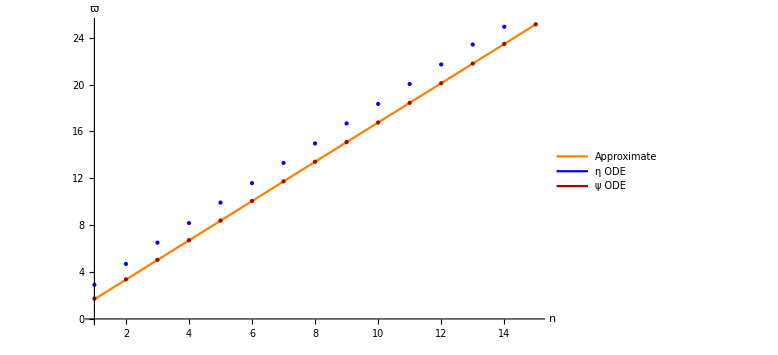

```mathematica
Block[{σ0 = -1, σp = 1, normalModeNumber = 15, ψmodes, ηmodes, k},
	ψmodes = findψNmodes[σ0, σp, normalModeNumber];
	ηmodes = findηNmodes[σ0, σp, normalModeNumber];
	k = π/(σp Hypergeometric2F1[1/4,1/2,3/2,-σp^2] - σ0 Hypergeometric2F1[1/4,1/2,3/2,-σ0^2]);
	Legended[
		Show[{
			Plot[k n, {n, 1, normalModeNumber}, PlotStyle -> {Orange, Thick}, AxesLabel -> {"n", "ϖ"}],
			ListPlot[ηmodes[[All, 1]], PlotStyle -> {Blue, PointSize[Large]}],
			ListPlot[ψmodes[[All, 1]], PlotStyle -> {Darker@Red, PointSize[Large]}]
		}, ImageSize -> Large],
		LineLegend[{Orange, Blue, Darker@Red}, {"Approximate", "η ODE", "ψ ODE"}]
	]
]
```

## Orthogonality of the normal modes of (89)

The equation (94) reads

d/dσ[√(1+σ^2)dψ_n/dσ] + ϖ^2 ψ_n = 0

In terms of a new variable χ ≡ ArcSinh[σ], it can be written as

(d^2 ψ_n)/dχ^2 + ϖ_n^2 Cosh[χ]ψ_n = 0

Now, let us look at some two normal modes ψ_n and ψ_m.

(d^2 ψ_m)/dχ^2 + ϖ_m^2 Cosh[χ]ψ_m = 0
(d^2 ψ_n)/dχ^2 + ϖ_n^2 Cosh[χ]ψ_n = 0

Multiplying the first equation by ψ_n, the second one by ψ_m, and integrating, we obtain

(∫^χ_p)_χ_0 ψ_n(d^2 ψ_m)/dχ^2 dχ + ϖ_m^2(∫^χ_p)_χ_0 Cosh[χ]ψ_n ψ_m dχ = 0
(∫^χ_p)_χ_0 ψ_m(d^2 ψ_n)/dχ^2 dχ + ϖ_n^2(∫^χ_p)_χ_0 Cosh[χ]ψ_m ψ_n dχ = 0

where χ_0 ≡ ArcSinh[σ_0], χ_p ≡ ArcSinh[σ_p] are the coordinates χ of the cable’s edges. Now, notice that the second term is the same in both equations, so we have

(ϖ_m^2 - ϖ_n^2)(∫^χ_p)_χ_0 Cosh[χ]ψ_n ψ_m dχ = (∫^χ_p)_χ_0 ψ_m(d^2 ψ_n)/dχ^2 dχ - (∫^χ_p)_χ_0 ψ_n(d^2 ψ_m)/dχ^2 dχ

We can use integration by parts to show that the right-hand-side is zero. For that, let us first notice that

(((∫^χ_p)_χ_0 ψ_m(d^2 ψ_n)/dχ^2 = ψ_m dψ_n/dχ|)_χ_0)^χ_p - (∫^χ_p)_χ_0 dψ_m/dχ dψ_n/dχ
(((∫^χ_p)_χ_0 ψ_n(d^2 ψ_m)/dχ^2 = ψ_n dψ_m/dχ|)_χ_0)^χ_p - (∫^χ_p)_χ_0 dψ_n/dχ dψ_m/dχ

Boundary conditions dictate that the cable’s edges are fixed, so ψ_m[χ_0] = ψ_m[χ_p] = ψ_n[χ_0] = ψ_n[χ_p] = 0, where χ_0 = ArcSinh[σ_0] is the coordinate χ of the cable’s left end and χ_p = ArcSinh[σ_p] is the χ coordinate of the cable’s right end. Substituting this, we have

(∫^χ_p)_χ_0 ψ_m(d^2 ψ_n)/dχ^2 = - (∫^χ_p)_χ_0 dψ_m/dχ dψ_n/dχ

(∫^χ_p)_χ_0 ψ_n(d^2 ψ_m)/dχ^2 = - (∫^χ_p)_χ_0 dψ_n/dχ dψ_m/dχ

And (ϖ_m^2 - ϖ_n^2)(∫^χ_p)_χ_0 Cosh[χ]ψ_n ψ_m dχ = (∫^χ_p)_χ_0 ψ_m(d^2 ψ_n)/dχ^2 dχ - (∫^χ_p)_χ_0 ψ_n(d^2 ψ_m)/dχ^2 dχ = 0. If we are talking about two normal modes with different ϖ’s, then the coefficient ϖ_m^2 - ϖ_n^2 is nonzero, and the only way to satisfy the equality is to make the integral itself zero:

(∫^χ_p)_χ_0 ψ_n ψ_m Cosh[χ]dχ = 0                    ϖ_n ≠ ϖ_m

Now, notice that Cosh[χ] dχ is nothing but d Sinh[χ]. Since χ is defined as χ ≡ ArcSinh[σ], we have d Sinh[ArcSinh[σ]] = dσ. Changing variable of integration back to σ again, we obtain

(∫^σ_p)_σ_0 ψ_n[σ]ψ_m[σ]dσ = 0                    ϖ_n ≠ ϖ_m

Which means that any two normal modes of (89) with different ϖ’s are orthogonal. To illustrate that, let us compute the first six normal modes of (89) with σ_0 = -1, σ_p = 1, and compute (∫^σ_p)_σ_0 ψ_n[σ]ψ_m[σ]dσ for various m and n.

```mathematica
Block[
	{
		nmodes = findψNmodes[-1, 1, 6],
		prod, int
	},
	Quiet[MatrixForm@Table[
		prod = Function[σ, Module[{ξ = √(1 + σ^2) - 1}, Null]] /. Null -> SetPrecision[
			Expand[Evaluate[nmodes[[n, 2, 2, 2]] nmodes[[m, 2, 2, 2]]]]
				/. Power[ξ, p_] -> If[p > 30, 0, Power[ξ, p]],
			20
		];
		int = NIntegrate[prod[σ], {σ, -1, 1}, WorkingPrecision -> 20];
		N@Round[int, 10^-8],
		{n, 6}, {m, 6}
	]]
]
```

(0.940764 | 0. | 0. | 0. | 0. | 0.
0. | 0.0838775 | 0. | 0. | 0. | 0.
0. | 0. | 0.935899 | 0. | 0. | 0.
0. | 0. | 0. | 0.0208911 | 0. | 0.
0. | 0. | 0. | 0. | 0.93694 | 0.
0. | 0. | 0. | 0. | 0. | 0.00927977)

As you can see, the matrix really is diagonal, exemplifying (122). Incidentally, we can re-write (122) in terms of the physical variable y, which represents the cable’s horizontal displacement from equilibrium, and arc length l. According to (56) and (68), dl = (1 - k_e h)dζ, which we can re-write using (88) as dl = Λ (1 -  η/(1 + σ^2))dσ. From here, dσ = dl/Λ + O[ε]. Substituting this back in, we get

(∫^σ_p)_σ_0 ψ_n[σ]ψ_m[σ]dl = 0                    ϖ_n ≠ ϖ_m

Now, let us change σ and ψ to σ = (ζ - l_0)/Λ and ψ[σ] = 1/Λ y[l_0 + Λσ] (88). Substituting σ_0 ≡ -l_0/Λ, σ_p ≡ (L - l_0)/Λ and ω_n = √(g/Λ)ϖ_n, we obtain

(∫^L)_0 y_n[ζ]y_m[ζ]dl = 0                    ω_n ≠ ω_m

Where y_n[ζ] represents a normal mode of horizontal oscillations given by y[t, ζ] = y_n[ζ] Cos[ω_n t]. We can see is that if two horizontal normal modes have different frequencies, the integral with respect to arc length of their product is zero.

#### A minor technical note on NIntegrate

You might have noticed that the function prod[σ], which is basically ψ_n · ψ_m, was defined not just as nmodes[[n, 2, 2, 2]] nmodes[[m, 2, 2, 2]], but instead its definition included a replacement part that set all terms containing ξ to the power larger than 30 to zero; this is because NIntegrate does not work well with high powers of ξ, as you can see below:

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

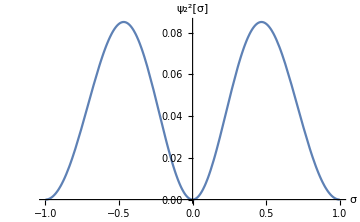
{-Graphics-,0.}

```mathematica
With[{ψ = findψNmodes[-1, 1, 2, OutputForm -> Last][[2]]},
	{
	Plot[ψ[σ]^2, {σ, -1, 1}, ImageSize -> Medium, AxesLabel -> {"σ", "ψ_2^2[σ]"}],
	NIntegrate[ψ[σ]^2, {σ, -1, 1}]
	}
]
```

We are looking at the second normal mode ψ_2[σ]  for σ_0 = -1, σ_p = 1. From the plot, the value of ψ_2^2[σ] is positive throughout most of the domain. However, if we try to integrate it, we get a warning message from NIntegrate and an output 0, which is obviously incorrect.

## Solving the initial value problem

Suppose that we know the position and velocity of each point along the cable at some moment in time, which we can without the loss of generality call t = 0. What shape will the cable take at all following instants? This question can be answered by expression the cable’s shape a superposition of the normal modes; this is convenient because the normal modes simply evolve sinusoidally and don’t interact with each other.

### Horizontal oscillations

First, let us look at horizontal oscillations, which are described by y[t, ζ]. Let us write y[t, ζ] in terms of the dimensionless variable ψ as y[t, ζ] = Λ ψ[√(g/Λ)t, (ζ - l_0)/Λ]. The function ψ can in turn be written as ψ[τ, σ] = (∑^∞)_(n=1)C_n ψ_n[σ]Cos[ϖ_n τ - ϕ_n], where ψ_n and ϖ_n are the n-th normal mode and natural frequency of (89), respectively, and C_n and ϕ_n are constants determined by the initial conditions:

(∑^∞)_(n=1)C_n ψ_n[σ]Cos[ϕ_n] = ψ_i[σ]                                σ_0 ≤ σ ≤ σ_p
(∑^∞)_(n=1)C_n ψ_n[σ]ϖ_n Sin[ϖ_n τ - ϕ_n] = -(ψ^·)_i[σ]              σ_0 ≤ σ ≤ σ_p

where ψ_i[σ] ≡ ψ[0, σ], (ψ^·)_i[σ] ≡ (∂ψ)/(∂τ)[0, σ] are just shortcuts. The initial ψ and (∂ψ)/(∂τ) can be found as ψ[0, σ] = 1/Λ y[0, l_0 + Λ σ], (∂ψ)/(∂τ)[0, σ] = 1/(√(g Λ))(∂y)/(∂t)[0, l_0 + Λ σ]. The task now is to find C_n and ϕ_n. To do that, let us multiply both equations by ψ_k and integrate from σ_0 to σ_p:

(∑^∞)_(n=1)C_n((∫^σ_p)_σ_0 ψ_k[σ]ψ_n[σ]dσ)Cos[ϕ_n] = (∫^σ_p)_σ_0 ψ_k[σ]ψ_i[σ]dσ
(∑^∞)_(n=1)C_n((∫^σ_p)_σ_0 ψ_k[σ]ψ_n[σ]dσ)ϖ_n Sin[ϕ_n] = (∫^σ_p)_σ_0 ψ_k[σ](ψ^·)_i[σ]dσ

Now, we can use the orthogonality of the normal modes (∫^σ_p)_σ_0 ψ_m[σ]ψ_n[σ]dσ = 0     m  ≠ n (122); if we choose the normalization such that (∫^σ_p)_σ_0 ψ_m[σ]ψ_n[σ]dσ = δ_mn, where δ_mn is the Kronecker delta, we get

C_k Cos[ϕ_k] = (∫^σ_p)_σ_0 ψ_k[σ]ψ_i[σ]dσ
C_k ϖ_k Sin[ϖ_n τ + ϕ_n] = (∫^σ_p)_σ_0 ψ_k[σ](ψ^·)_i[σ]dσ

From here,

C_k = √(( ψ_k, ψ_i)^2 + 1/ϖ_k^2(ψ_k, (ψ^·)_i)^2)
ϕ_k = Arg[( ψ_k, ψ_i) + I/ϖ_k(ψ_k, (ψ^·)_i)]

where I ≡ √-1 in the Arg function is the imaginary unit, ( u, v) ≡ (∫^σ_p)_σ_0 u[σ] v[σ] dσ and ψ_i[σ] ≡ ψ[0, σ], (ψ^·)_i[σ] ≡ (∂ψ)/(∂τ)[0, σ]. Finally, y[t, ζ] is given by

y[t, ζ] = Λ(∑^∞)_(n=1)C_n ψ_n[(ζ - l_0)/Λ]Cos[√(g/Λ)t + ϕ_n]

### In-plane oscillations

In-plane oscillations are described by y[t, ζ]. Let us write h[t, ζ] in terms of the dimensionless variable η as h[t, ζ] = Λ η[√(g/Λ)t, (ζ - l_0)/Λ]. The function η can in turn be written as η[τ, σ] = (∑^∞)_(n=1)C_n η_n[σ]Cos[ϖ_n τ - ϕ_n], where η_n and ϖ_n are the n-th normal mode and natural frequency of (90), respectively, and C_n and ϕ_n are constants determined by the initial conditions:

(∑^∞)_(n=1)C_n η_n[σ]Cos[ϕ_n] = η_i[σ]                                   σ_0 ≤ σ ≤ σ_p
(∑^∞)_(n=1)C_n η_n[σ]ϖ_n Sin[ϖ_n τ - ϕ_n] = -(η^·)_i[σ]              σ_0 ≤ σ ≤ σ_p

where η_i[σ] ≡ η[0, σ], (η^·)_i[σ] ≡ (∂η)/(∂τ)[0, σ] are just shortcuts. The initial η and (∂η)/(∂τ) can be found as η[0, σ] = 1/Λ h[0, l_0 + Λ σ], (∂η)/(∂τ)[0, σ] = 1/(√(g Λ))(∂h)/(∂t)[0, l_0 + Λ σ]. The task now is to find C_n and ϕ_n. To do that, let us multiply both equations by η_k and integrate from σ_0 to σ_p:

(∑^∞)_(n=1)C_n((∫^σ_p)_σ_0 η_k[σ]η_n[σ]dσ)Cos[ϕ_n] = (∫^σ_p)_σ_0 η_k[σ]η_i[σ]dσ
(∑^∞)_(n=1)C_n((∫^σ_p)_σ_0 η_k[σ]η_n[σ]dσ)ϖ_n Sin[ϕ_n] = (∫^σ_p)_σ_0 η_k[σ](η^·)_i[σ]dσ

Denoting J_kn ≡ (∫^σ_p)_σ_0 η_k[σ]η_n[σ], we can write this as

(∑^∞)_(n=1)J_kn C_n Cos[ϕ_n] = (∫^σ_p)_σ_0 η_k[σ]η_i[σ]dσ
(∑^∞)_(n=1)J_kn C_n ϖ_n Sin[ϕ_n] = (∫^σ_p)_σ_0 η_k[σ](η^·)_i[σ]dσ

Since high-frequency terms have a very large curvature, the coefficients C_n for large n are almost zero. For instance, if we were looking at a straight string whose normal modes are sine functions, the decomposition of η[σ] as a sum of the normal modes Sin[k σ] would be equivalent to a Fourier series; and for any physically sensible function η[σ], the coefficients before the high-frequency normal modes are small. So, the coefficients C_n for large n are small, and we can change the summation limit from ∞ to N, where N is some finite large number, without losing too much accuracy:

(∑^N)_(n=1)J_kn C_n Cos[ϕ_n] ≈ (∫^σ_p)_σ_0 η_k[σ]η_i[σ]dσ
(∑^N)_(n=1)J_kn C_n ϖ_n Sin[ϕ_n] ≈ (∫^σ_p)_σ_0 η_k[σ](η^·)_i[σ]dσ

Ideally, the equation above should hold for all k, but of course this is impossible since we only have N variables to satisfy an infinite number of equations. What we can do to fix this problem is to say that if we can’t solve all of the equations, let us just solve the first N of them; in the limit as N gets large, this approaches the initial problem. But then, we can treat J as an N×N matrix, and in particular, we can compute its inverse J^-1 (the matrix must be invertible because if its nullspace had dimension greater than zero, this would mean that we can arbitrarily add to the constants C some vector in the nullspace v, and the resulting constants C would still satisfy the initial conditions. But this doesn’t make any sense, as this would mean, since the normal modes are linearly independent, that the initial conditions are ambiguous). Then, we can write

C_m Cos[ϕ_m] ≈ (∑_(k=0))^N(J^-1)_mk(∫^σ_p)_σ_0 η_k[σ]η_i[σ]dσ
C_m ϖ_m Sin[ϕ_m] ≈ (∑_(k=0))^N(J^-1)_mk(∫^σ_p)_σ_0 η_k[σ](η^·)_i[σ]dσ

From here,

C_k ≈ √(( (∑_(k=0))^N(J^-1)_mk( η_k, η_i))^2 + 1/ϖ_k^2((∑_(k=0))^N(J^-1)_mk(η_k, (η^·)_i))^2)
ϕ_k ≈ Arg[(∑_(k=0))^N(J^-1)_mk(( η_k, η_i) + I/ϖ_k(η_k, (η^·)_i))]

where I ≡ √-1 in the Arg function is the imaginary unit, ( u, v) ≡ (∫^σ_p)_σ_0 u[σ] v[σ] dσ and η_i[σ] ≡ η[0, σ], (η^·)_i[σ] ≡ (∂η)/(∂τ)[0, σ]. Finally, h[t, ζ] is given by

h[t, ζ] ≈ Λ(∑^∞)_(n=1)C_n η_n[(ζ - l_0)/Λ]Cos[√(g/Λ)t + ϕ_n]

## Tight cable

The equations (89) and (90) governing the cable’s oscillations are

(∂^2 ψ)/(∂τ^2) = √(1+σ^2)(∂^2 ψ)/(∂σ^2) + σ/(√(1+σ^2))(∂ψ)/(∂σ)
∂^2/(∂τ^2)[(1+2 σ^2)/(1+σ^2)η + 4 σ(∂η)/(∂σ) + (1+σ^2)(∂^2 η)/(∂σ^2)] = (1+σ^2)^(3/2)(∂^4 η)/(∂σ^4) + 7 σ √(1+σ^2)(∂^3 η)/(∂σ^3) + (7+10 σ^2)/(√(1+σ^2))(∂^2 η)/(∂σ^2) - (σ (1-2 σ^2))/((1+σ^2)^(3/2))(∂η)/(∂σ) - (2 (1-2 σ^2))/((1+σ^2)^(5/2))η

Let’s look at the limit when the tension in the cable is much higher than its weight, T/(M g) → ∞. Physically, this can be achieved by pulling the cable’s ends as far apart as possible, so that the cable’s sag is minimal. As it can be seen from z_e[x] = Λ (Cosh[(x - x_0)/Λ] - Cosh[x_0/Λ]) (14), this corresponds to the limit Λ → ∞. This can also be seen from the formula Λ = ((T_e)_x)/(ρ g), that says that as Λ increases, so does (T_e)_x. Now, if Λ is large, then the bounds for σ are small, since by definition, σ ≡ (ζ - l_0)/Λ, and making Λ much higher than L means that σ_p - σ_0 = L/Λ << 1. Whatever the functions ψ[σ] and η[σ] are, they are confined to a very small domain of σ. And since they must be zero at σ = σ_0 and at σ = σ_p, this implies that they have to transition from being zero to some nonzero value and back to zero again in a very short length of σ, so (∂ψ)/(∂σ) ~  Λ/Lψ >> ψ, (∂η)/(∂σ) ~ Λ/L >> η, where A ~ B means that A is of the same order of magnitude as B. For higher derivatives, we similarly have (∂^(d+1) ψ)/(∂σ^(d+1)) >> (∂^d ψ)/(∂σ^d), (∂^(d+1) η)/(∂σ^(d+1)) >> (∂^d η)/(∂σ^d). Also, because σ_0 ≤ σ ≤ σ_p and σ_p - σ_0 << 1, we can say that the difference between σ and σ_0 is always small: |σ - σ_0| << 1. Substituting this into the equations (89) and (90) and neglecting the O[L/Λ] terms, we obtain

(∂^2 ψ)/(∂τ^2) = √(1+σ_0^2)(∂^2 ψ)/(∂σ^2)
∂^2/(∂τ^2)(∂^2 η)/(∂σ^2) = √(1+σ_0^2)(∂^4 η)/(∂σ^4)

The equation for η can be integrated twice with respect to σ to give ∂^2/(∂τ^2)η = √(1+σ_0^2)(∂^2 η)/(∂σ^2) + C_1 + C_2 σ. The equation must hold in equilibrium, when η = 0, so C_1 = C_2 = 0. Thus, the equation becomes

(∂^2 η)/(∂τ^2) = √(1+σ_0^2)(∂^2 η)/(∂σ^2)

We can write the two equations describing the cable’s oscillations as

(∂^2 ψ)/(∂τ^2) = C(∂^2 ψ)/(∂σ^2)              (∂^2 η)/(∂τ^2) = C(∂^2 η)/(∂σ^2)

where C ≡ √(1 + σ_0^2) is a constant (since σ_0 the σ coordinate of the cable’s left end, which is constant). We see that the PDEs describing in-plane and horizontal oscillations both reduce to the wave equation in this limit. What this means is that as the cable gets infinitely tight, its curvature becomes negligible and its motion becomes similar to that of a “textbook” string. This also agrees with the formulas (115) and (120), which say that as the cable becomes tighter, the normal modes approach those of a tight strings, namely sine functions.

## Lax cable

Let’s say we take our cable and hang it from two points that are very close to each other. Intuitively, we would expect that as we bring the cable’s ends closer together, it would become more and more similar to a vertical line. In the figures below, you can see how a cable of length 1 would look like when hung from two points located at the horizontal distance of 0.4, 0.2, 0.1 from each other, respectively; you can see that the cable’s equilibrium shape indeed approaches a vertical line.

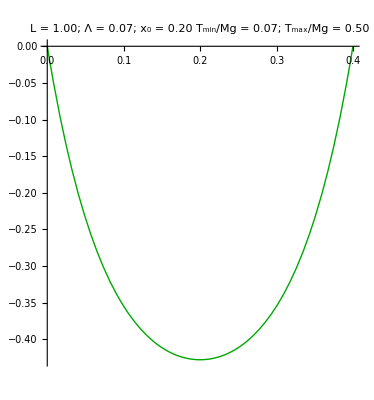
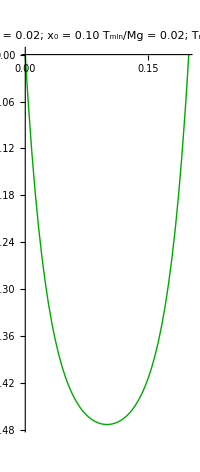
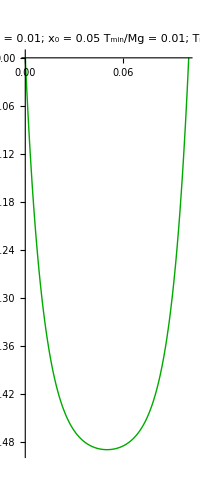

```mathematica
(* Subscript[x, p], Subscript[z, p], L *)
drawCable[#, 0, 1, ImageSize -> {Automatic, 400}]& /@ {0.4, 0.2, 0.1}
```

Intuitively, if in equilibrium a cable hangs almost vertically, then it’s also going to oscillate like a cable that, well, is hung vertically, as in this 2018 UCONN paper. Let us try to quantify this hypothesis.

### Why an infinitely lax cable corresponds to small Λ and large limits for σ

As the distance between the cable’s attachment points increases, so does the tension in the cable. Let us explore another limit when the attachment points are brought close together, and the tension is as low as it can be for a cable of a cable with a given mass. The cable’s shape is described by the constants Λ and x_0, which are determined by (25) and (26):

√(L^2 - z_p^2) = 2Λ Sinh[x_p/(2 Λ)]
x_0 = x_p/2 - Λ ArcTanh[z_p/L]

Here x_p is the horizontal distance between the attachment points and z_p is the vertical distance. Let us set z_p to zero, meaning that the cable’s attachment points are on the same height.

L = 2Λ Sinh[x_p/(2 Λ)]
x_0 = x_p/2

The second equation now tells us explicitly that x_0 = x_p/2, meaning that the cable’s lowest point is right in-between the attachment points; this is what we would expect from mirror reflection symmetry. Now, let’s take the limit as the horizontal distance x_p approaches zero. The second equation can be written as

1 =1/(L/2Λ)Sinh[x_p/L(L/2Λ)]

It relates the dimensionless parameter L/2Λ to x_p/L here L is the cable’s length, which is fixed. If we make x_p very small, the Sinh would become very small as well, as Sinh[k x]  always decreases with x. To counteract this, we would need to increase L/(2Λ), since the ratio Sinh[k x]/x always increases with x. As we make x_p/L arbitrarily small, we would need to make L/2Λ increasingly large, which would mean making Λ small. Thus, in the limit when x_p approaches zero, Λ approaches zero as well. Also, from (14) we can see that as Λ gets smaller, z_e[x] starts rising faster with x, which corresponds to the cable transitioning to a steeper, more vertical, shape.
	And as we saw from the derivation of (14), small Λ also corresponds to (T_e)_x, or the horizontal component of the tension in equilibrium configuration, being small. On the interactive illustration below, you can see that small Λ really does correspond to the cable’s attachment points being close to each other.

```mathematica
hangingCableToy[]
```

In terms of ζ, σ is given as σ ≡ (ζ - l_0)/Λ (88). When we bring the cable’s attachment points closer while keeping length fixed, we make Λ small while keeping L constant. ζ goes from 0 to L, which means that σ ≡ (ζ - l_0)/Λ goes from -l_0/Λ to (L - l_0)/Λ; as L/Λ increases, so does the distance between the limits -l_0/Λ and (L - l_0)/Λ. Either from mirror reflection symmetry of the problem or directly from the definition of l_0 ≡ Λ Sinh[x_0/Λ], formula L = Λ(Sinh[(x_p - x_0)/Λ] + Sinh[x_0/Λ]), and x_0 = x_p/2 (which is only true if z_p = 0, as here), we can see that l_0 = L/2, and σ then goes from -L/(2Λ) to +L/(2Λ). Thus, as we bring the cable’s ends closer together, the limits for σ get larger.

### Approximating the equations

The equations (94) and (103) determining the cable’s normal modes are written as

√(1+σ^2)(d^2 ψ)/dσ^2 + σ/(√(1+σ^2))dψ/dσ + ϖ^2 ψ = 0
(1+σ^2)^(3/2)(d^4 η)/dσ^4 + 7 σ √(1+σ^2)(d^3 η)/dσ^3 + (ϖ^2(1+σ^2) + (7+10 σ^2)/(√(1+σ^2)))(d^2 η)/dσ^2+ (4 ϖ^2 σ - (σ (1-2 σ^2))/((1+σ^2)^(3/2)))dη/dσ + (ϖ^2(1+2 σ^2)/(1+σ^2) - (2 (1-2 σ^2))/((1+σ^2)^(5/2)))η = 0

Here σ goes from -S to S, where S ≡ L/2Λ. Let us introduce a new variable ϛ ≡ σ/S, such that σ = S ϛ; this is convenient because now we have -1 ≤ ϛ ≤ 1. For derivatives, we have d/dσ = 1/S d/dϛ. By plugging in σ ≡ (ζ - l_0)/Λ (88) into the definition of ϛ, we can see that ϛ ≡ σ/S =  (ζ - l_0)/Λ/L/(2Λ), which is (ζ - l_0)/(L/2). So, ϛ is basically like ζ, except for a constant factor. The two equations can be written in terms of ϛ as

1/S^2 √(1+S^2 ϛ^2)(d^2 ψ)/dϛ^2 + ϛ/(√(1+S^2 ϛ^2))dψ/dϛ + ϖ^2 ψ = 0
(1+S^2 ϛ^2)^(3/2)1/S^4(d^4 η)/dϛ^4 + 7 ϛ √(1+S^2 ϛ^2)1/S^2(d^3 η)/dϛ^3 + (ϖ^2(1+S^2 ϛ^2) + (7+10 S^2 ϛ^2)/(√(1+S^2 ϛ^2)))1/S^2(d^2 η)/dϛ^2+ (4 ϖ^2 S ϛ - (S ϛ (1-2 S^2 ϛ^2))/((1+S^2 ϛ^2)^(3/2)))1/S dη/dϛ + (ϖ^2(1+2 S^2 ϛ^2)/(1+S^2 ϛ^2) - (2 (1-2 S^2 ϛ^2))/((1+S^2 ϛ^2)^(5/2)))η = 0

or

√(1/S^2+ϛ^2)(d^2 ψ)/dϛ^2 + ϛ/(√(1/S^2+ϛ^2))dψ/dϛ + γ^2 ψ = 0
(1/S^2+ϛ^2)^(3/2)(d^4 η)/dϛ^4 + 7 ϛ √(1/S^2+ϛ^2)(d^3 η)/dϛ^3 + (γ^2(1/S^2+ϛ^2) + (7/S^2+10 ϛ^2)/(√(1/S^2+ϛ^2)))(d^2 η)/dϛ^2+ (4 γ^2 ϛ - (ϛ (1/S^2-2 ϛ^2))/((1/S^2+ϛ^2)^(3/2)))dη/dϛ + (γ^2(1/S^2+2 ϛ^2)/(1/S^2+ϛ^2) - (2 (1/S^2-2 ϛ^2))/(S^2(1/S^2+ϛ^2)^(5/2)))η = 0

where γ^2 ≡ S ϖ^2. For ϛ >> 1 / S, we have

ϛ(d^2 ψ)/dϛ^2 + dψ/dϛ + γ^2 ψ = 0
ϛ^3(d^4 η)/dϛ^4 + 7 ϛ^2(d^3 η)/dϛ^3 + (γ^2 ϛ^2 + 10 ϛ)(d^2 η)/dϛ^2+ (4 γ^2 ϛ + 2)dη/dϛ + 2 γ^2 η = 0

Since 1 / S is very small, the equations above are applicable almost on the entirety of the cable’s length. Now, by guessing, we can see that the second equation can be written as

d^2/dϛ^2[ϛ^2(ϛ(d^2 η)/dϛ^2 + dη/dϛ + γ^2 ψ)] = 0

Integrating this twice, we get

ϛ^2(ϛ(d^2 η)/dϛ^2 + dη/dϛ + γ^2 η) = C_0 + C_1 ϛ

Thus, for an infinitely lax cable the normal modes of both horizontal and in-plane motion are described by basically the same equation:

ϛ(d^2 ψ)/dϛ^2 + dψ/dϛ + γ^2 ψ = 0
ϛ(d^2 η)/dϛ^2 + dη/dϛ + γ^2 η = C_0/ϛ^2 + C_1/ϛ

This is a relatively simple equation that can be solved in terms of Bessel functions:

```mathematica
DSolve[ϛ ψ''[ϛ] + ψ'[ϛ] + γ^2 ψ[ϛ] == 0, ψ, ϛ]
```

{{ψ→Function[{ϛ},BesselJ[0,2 γ √ϛ] C[1]+2 BesselY[0,2 γ √ϛ] C[2]]}}

Which is the same equation as  the equation (16) in the article "Oscillations of a hanging chain" (UCONN, 2018), which looked at the oscillations of a vertically hanging cable. Intuitively this makes sense: if we bring the cable’s ends closer together, then it starts hanging almost vertically, and since it hangs almost vertically, then it also oscillates almost like a vertically hanging cable - sounds even somewhat obvious when phrased like this.

## Visualizing the normal modes of ψ and η

Draw the first normalModeNumber normal modes of the equation (89) with some given σ_0 and σ_p:

```mathematica
ClearAll[drawψNmodes];
drawψNmodes[σ0_, σp_, normalModeNumber_] := drawψNmodes[σ0, σp, 1, normalModeNumber];
drawψNmodes[σ0_, σp_, from_, to_] := Block[{ψ, ϖ, modes},
	modes = findψNmodes[σ0, σp, to];
	
	Column@Table[
		{ϖ, ψ} = modes[[n]];
		
		Plot[
			ψ[σ],
			{σ, σ0, σp},
			AxesLabel -> {"σ", "ψ"},
			PlotLabel -> "The " <> IntegerName[n, "Ordinal"] <> " normal mode of ψ      ϖ = " <> ToString@NumberForm[ϖ],
			ImageSize -> Medium
		],
		
		{n, from, to}
	]
];
```

For example, here are the first three normal modes for σ_0 = -1, σ_p = 1.

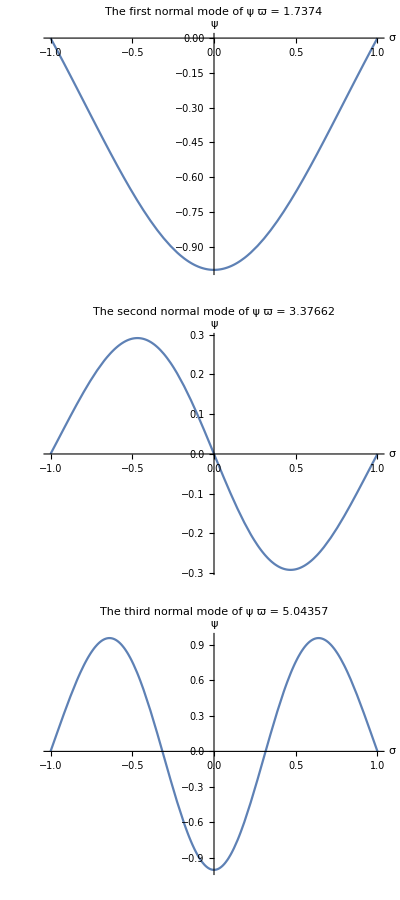

```mathematica
drawψNmodes[-1, 1, 3]
```

Draw the first normalModeNumber normal modes of the equation (90) with some given σ_0 and σ_p:

```mathematica
ClearAll[drawηNmodes];
drawηNmodes[σ0_, σp_, normalModeNumber_] := drawηNmodes[σ0, σp, 1, normalModeNumber];
drawηNmodes[σ0_, σp_, from_, to_] := Block[{η, ϖ, modes},
	modes = findηNmodes[σ0, σp, to];
	
	Column@Table[
		{ϖ, η} = modes[[n]];
		
		Plot[
			η[σ],
			{σ, σ0, σp},
			AxesLabel -> {"σ", "η"},
			PlotLabel -> "The " <> IntegerName[n, "Ordinal"] <> " normal mode of η      ϖ = " <> ToString@NumberForm[ϖ],
			ImageSize -> Medium
		],
		
		{n, from, to}
	]
];
```

For example, here are the first three normal modes for σ_0 = -1, σ_p = 1.

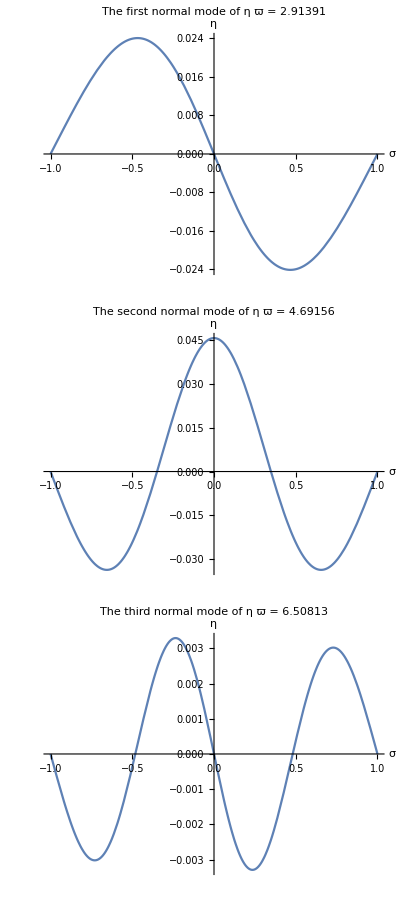

```mathematica
drawηNmodes[-1, 1, 3]
```

## Dispersion and “continuous reflection”

A short qualitative note to finalize the discussion of normal modes. As we saw from the chapter, the normal frequencies are not equidistant, and there is no reason to expect they would be rational multiples of each other. What this means is that if we set the cable oscillating at some moment in time, it will not return to its original configuration in any finite time. This in turn means that a pulse once launched in the cable does not just bounce back and forth but instead changes shape - this is what we usually call dispersion.
	And as we know from the propagation of waves in homogenous media with a nonlinear dispersion relation, dispersion generally causes pulses to not only “deform” but to also start “radiating backwards”. There is no reason we would expect dispersion in our system to be special in this sense, so the pulses most likely do “reflect backwards” as they travel.
	We can empirically check these two conclusions using numerical methods. From the section “Solving the initial value problem”, we borrow the formula that allows us to simulate horizontal pulses propagating through the cable. For the sake of example, let us look at the horizontal oscillations with the initial conditions ψ[0, σ] = ψ_0[σ], ∂/(∂τ)ψ[0, σ]  = 0 - this is what happens if we displace the cable from equilibrium and hold it in this position, and then release.

```mathematica
ClearAll[solveψIVP];
solveψIVP[σ0_, σp_, ψ0_, normalModeNumber_] := Block[
	{
		ϖlist, ψlist, C
	},
	{ϖlist, ψlist} = Transpose@findψNmodes[σ0, σp, normalModeNumber];
	
	C = Table[
		myNIntegrate[ψlist[[n]][#]ψ0[#]&, {σ0, σp}]/myNIntegrate[(ψlist[[n]][#])^2&, {σ0, σp}],
		{n, normalModeNumber}
	];
	
	Function[{τ, σ}, Null] /. Null -> Sum[
			C[[n]] ψlist[[n]][σ] Cos[ϖlist[[n]] τ],
			{n, normalModeNumber}
		]
];
```

Since there were some problems with NIntegrate, the function uses a custom function myNIntegrate instead.

```mathematica
ClearAll[myNIntegrate];
myNIntegrate[f_, {a_, b_}] := With[{dx = (b - a)/1000}, dx Sum[N@f[x], {x, a + dx/2, b, dx}]];
```

```mathematica
myNIntegrate[Cos[#]^2&, {0, 2π}] - π
```

0.

Here is how we can compute an approximate solution to our problem with σ_0 = -1, σ_p = 1 for ψ[0, σ] = Exp[-40 σ^2] using the first 32 normal modes and dropping the higher modes:

```mathematica
ivpψ = solveψIVP[-1, 1, Exp[-40#^2]&, 32];
```

Animate how the cable oscillates as a function of time:

```mathematica
Animate[Plot[ivpψ[τ, σ], {σ, -1, 1}, PlotRange ->  {-1, 1}, AxesLabel -> {"σ", Row[{"ψ[",  ToString[Round[τ]],", σ]"}]}], {τ, 0, 10}, AnimationRate -> 1]
```

Notice that at first, the pulse just “bounces” back and forth as it would do in a tight string. However, after some time, it’s evident that its shape starts to change. After a few bounces, we see that the pulse leaves after itself not a region where ψ = 0, as for a tight string, but a region with some dissipated ψ:

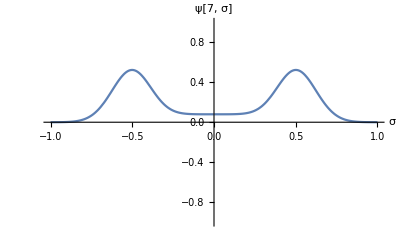

```mathematica
Plot[ivpψ[7, σ], {σ, -1, 1}, PlotRange ->  {-1, 1}, AxesLabel -> {"σ", Row[{"ψ[7, σ]"}]}]
```

As time goes on, the cable’s shape deforms even more. Here is how the cable oscillates from τ = 100 to τ = 110:

```mathematica
Animate[Plot[ivpψ[τ, σ], {σ, -1, 1}, PlotRange ->  {-1, 1}, AxesLabel -> {"σ", Row[{"ψ[",  ToString[Round[τ]],", σ]"}]}], {τ, 100, 110}, AnimationRate -> 1]
```

Just look at these wild shapes:

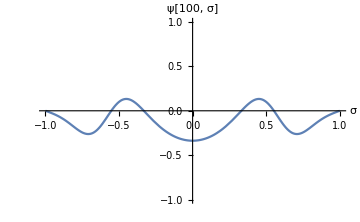
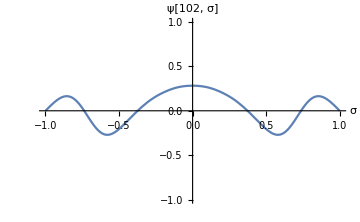
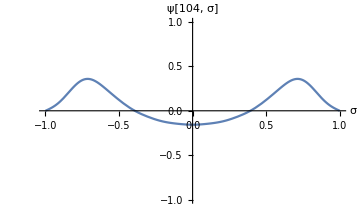
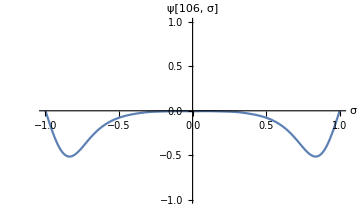
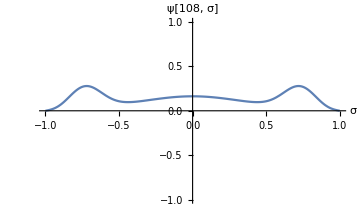
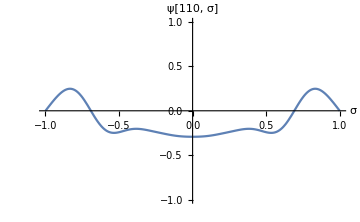

```mathematica
Table[Plot[ivpψ[τ, σ], {σ, -1, 1}, PlotRange ->  {-1, 1}, AxesLabel -> {"σ", Row[{"ψ[",  ToString[Round[τ]],", σ]"}]}, ImageSize -> Medium], {τ, 100, 110, 2}]
```

It is evident that the shape has changed a lot - so, we confirm the initial hypothesis that dispersion is present. In addition, we saw that even after a few bounces, the pulse leaves a “tail” - this illustrates the hypothesis about “continuous reflection”, which is due to the tension in the cable changing with position. We can break the cable into many infinitesimal tight strings with different tension, and in the interface of any two strings, there should be some reflection when a pulse passes - and this is indeed what we see. So far this is only numerical inexact argument, however, so the results should be taken with a grain of salt. There can be some numerical error due to the omission of high normal modes. The phenomenon is a very interesting thing to explore in further work.

## Oscillations of a discrete chain

It is interesting to compare the oscillations of a continuous cable to those of a discrete chain; the hypothesis is that a chain with a very large number of members behaves exactly like a cable. This chapter uses Newton’s second law, boundary conditions, and the incompressibility condition to derive the equations of motion for the chain. The resulting equations are written in vector form as x^(··) = -A x, where x is a vector and A is a square matrix.

## Kinematics of the chain

Imagine a system (later called chain) consisting of N+1 rigid massless rods each of length λ connected by frictionless joints to N+2 equal point masses m (later called balls), so that each rod is attached with joints to two balls without friction. Let us hold the two outmost balls - for example, attach them to a wall. How will the chain move under the influence of gravity?

### Numbering the balls

First, let’s number the balls. Pick the two outmost balls and number them as 0 and N + 1, respectively. Now, number all the remaining balls such that they come in order. Below is an example of such numbering for N=12.

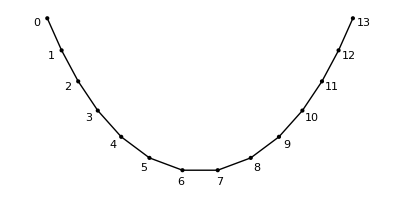

```mathematica
drawChain[1, 0, 1.5, 12, Connect -> True, Number -> True]
```

Here, the balls number 0 and N + 1 are held at some fixed points. Let us now choose a Cartesian coordinate system such that the zeroth ball is at the origin, the z axis is the up direction (e.g. against the direction of gravity), the x axis is chosen so that in equilibrium, the chain lies in the xz plane, and the y axis is chosen to be perpendicular to x and z. In other words, just take the coordinate system we’ve used to study a continuous cable.
	Finally, take the position of the ball N + 1 and call it the point P. Since the ball N + 1 is held in place, P is fixed; it’s the same P as in the continuous cable case.

### Position of the k-th ball

We know that the distance between two neighboring balls is always the same. Mathematically,

|(r^–)_k - (r^–)_(k-1)| = λ

where (r^–)_k is the position vector of the k-th ball and λ is some constant. Here the zeroth ball is the origin, so (r^–)_0 = 0. We can find λ from the condition that the length of the chain must be equal to L. If we stretch the chain as far as possible, the balls would form a straight line. Since there are N + 1 rods in this chain and each has length λ, the total length will be L = (N + 1)λ.

λ = L/(N + 1)

Now, (r^–)_k - (r^–)_(k-1) is a vector with three components that has to satisfy the constraint of having length λ; in other words, it must lie on the surface of a sphere with radius λ. Thus, we can parametrize it using two angles:

(r^–)_k - (r^–)_(k-1) = λ(Sin[ϕ_k] Cos[θ_k]
Sin[ϕ_k]Sin[θ_k]
-Cos[ϕ_k])

The choice of parametrization is arbitrary, however, for convenience, I chose an analog of spherical coordinates. By taking the norm of the above expression you can verify that its length is identically λ. The figure below illustrates how the angles θ and ϕ can be used to express ((r^–)_k - (r^–)_(k-1))/λ.

-Graphics-

By summing the equation from 0 to k, we arrive at the formula for the position of the k-th ball.

(r^–)_k = (∑^k)_(n = 1)λ (Sin[ϕ_n] Cos[θ_n]
Sin[ϕ_n]Sin[θ_n]
-Cos[ϕ_n])

The two figures below show the angles θ and ϕ can be used to describe the configuration of the chain.

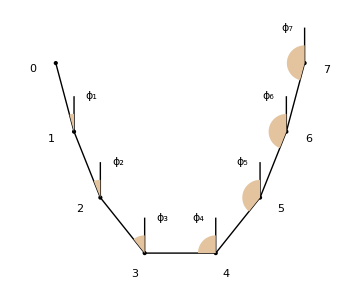
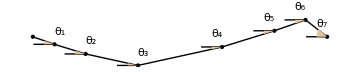
-Graphics-Sight from the +y direction
-Graphics-Sight from above

#### Code used to generate the figures

```mathematica
Table[
	With[{ϕ = 0.9, θ = 0.8}, Rasterize[
		Graphics3D[{
			Arrow[{{0, 0, 0}, {1, 0, 0}}], Text[Style["X", 21], {1.1, 0, 0}],
			Arrow[{{0, 0, 0}, {0, 1, 0}}], Text[Style["Y", 21], {0, 1.1, 0}],
			Arrow[{{0, 0, 0}, {0, 0, 1}}], Text[Style["Z", 21], {0, 0, 1.1}],
			{Thick, Blue, Arrow[{{0, 0, 0}, {Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], -Cos[ϕ]}}]},
			{Opacity[0.3], Sphere[{0, 0, 0}]},
			Polygon[Append[Table[{Cos[θ] Sin[α], Sin[θ] Sin[α], -Cos[α]}, {α, 0, ϕ, ϕ/20}], {0, 0, 0}]],
			Polygon[Append[Table[{Sin[ϕ]Cos[α], Sin[ϕ]Sin[α], -Cos[ϕ]}, {α, 0, θ, θ/20}], {0, 0, -Cos[ϕ]}]],
			{FaceForm[], Polygon[({{Cos[θ], 0, -Sin[θ]}, {Sin[θ], 0, Cos[θ]}, {0, -1, 0}}).Append[#, 0] & /@ CirclePoints[50]]},
			{Dashed, Line[{{Sin[ϕ], 0, 0}, {Sin[ϕ], 0, -Cos[ϕ]}}]},
			Text[Style["θ", 16], {0.8Sin[ϕ] Cos[θ/2], 0.8Sin[ϕ] Sin[θ/2], -Cos[ϕ]}],
			Text[Style["ϕ", 16], 0.2{Sin[ϕ] Cos[θ], Sin[ϕ] Sin[θ], -1-Cos[ϕ]}]
		},
		ViewPoint -> viewpoint, Boxed -> False],
		ImageSize -> {600, 600}
	]],
	{viewpoint, {{1.2, 0.4, 0.4}, {0.2, 2.8, 1.4}}}
] // ImageCollage
```

```mathematica
illustrateϕ[xp_, zp_, L_, Nballs_] := Module[
	{
		λ = L / (Nballs + 1),
		plist = { {0, 0} }, glist,
		currx = 0, currz = 0,
		Svals, Cvals
	},
	{Svals, Cvals} = findSC[xp, zp, L, Nballs];
	
	Table[
		currx += λ Svals[[n]];
		currz -= λ Cvals[[n]];
		
		AppendTo[plist, {currx, currz}],
		{n, Length[Svals]}
	];
	
	glist = Point /@ plist;
	
	glist = Join[glist,
		Table[Line[{#[[n]], #[[n + 1]]}], {n, Length[#] - 1}] &@ plist
	];
	
	glist = Join[glist,
		Table[
			Text[
				ToString[n - 1],
				plist[[n]] - λ/3 Normalize[{(Cvals[[#]] + Cvals[[Max[# - 1, 1]]])/2, (Svals[[#]] + Svals[[Max[# - 1, 1]]])/2}]&@ Min[n, Nballs + 1]
			],
			{n, Nballs + 2}
		]
	];
	
	glist = Join[glist,
		Line[{#, # + {0, λ/2}}]& /@ plist[[2;;]],
		Table[
			{RGBColor[0.89, 0.77, 0.62], Polygon[Append[
				Table[plist[[n]] + λ/4{-Sin[a], Cos[a]}, {a, 0, #, # / 20}]&@ If[Svals[[n - 1]]/Cvals[[n - 1]] ≥ 0, ArcTan[Svals[[n - 1]]/Cvals[[n - 1]]], π - ArcTan[-Svals[[n - 1]]/Cvals[[n - 1]]]],
				plist[[n]]
			]]},
			{n, 2, Length[plist]}
		],
		Table[
			Text[
				Subscript["ϕ", n - 1],
				plist[[n]] + λ/2 If[n > Length[plist]/2, {-1/2, 1}, {1/2, 1}]
			],
			{n, 2, Length[plist]}
		]
	];
	
	Labeled[Graphics[glist, ImageSize -> Medium], "Sight from the +y direction"]
]
```

```mathematica
illustrateθ[xp_, zp_, L_, Nballs_] := Module[
	{
		λ = L / (Nballs + 1),
		plist = { {0, 0} }, glist,
		currx = 0, curry = 0,
		Svals, Cvals,
		θlist
	},
	{Svals, Cvals} = findSC[xp, zp, L, Nballs];
	
	θlist = Array[0.3 CubeRoot[Cos[π/(Nballs + 1) #]]&, Nballs];
	AppendTo[θlist, -(θlist.Svals[[;;-2]])/Svals[[-1]]];
	
	Table[
		currx += λ Svals[[n]];
		curry -= λ Svals[[n]] θlist[[n]];
		
		AppendTo[plist, {currx, curry}],
		{n, Length[Svals]}
	];
	
	glist = Point /@ plist;
	
	glist = Join[glist,
		Table[Line[{#[[n]], #[[n + 1]]}], {n, Length[#] - 1}] &@ plist
	];
	
	glist = Join[glist,
		Line[{#, # - {λ/4, 0}}]& /@ plist[[2;;]],
		Table[
			{RGBColor[0.89, 0.77, 0.62], Polygon[Append[
				Table[plist[[n]] + λ/8{-Cos[a], Sin[a]}, {a, 0, θlist[[n - 1]], θlist[[n - 1]] / 20}],
				plist[[n]]
			]]},
			{n, 2, Length[plist]}
		],
		Table[
			Text[
				Subscript["θ", n - 1],
				plist[[n]] + λ/8 If[n > Length[plist]/2, {-1/2, 1}, {1/2, 1}]
			],
			{n, 2, Length[plist]}
		]
	];
	
	Labeled[Graphics[glist, ImageSize -> Medium], "Sight from above"]
]
```

```mathematica
Column[{illustrateϕ[1, 0, 2, 6], illustrateθ[1, 0, 2, 6]}]
```

### Linear approximation

In this problem, we are only interested in small oscillations near equilibrium. Let us then express the angle ϕ in (133) as a sum of its equilibrium value and a small perturbation.

ϕ_k[t] = F_k + φ_k[t]

Here F_k is the value of ϕ_k at equilibrium and φ_k is the small displacement from the equilibrium position. Let us assume that in equilibrium, θ is zero, so that the chain lies in the xz plane. This is later proven in this chapter formula (155). Substituting (134) into (133) and taking the first-order approximation, we arrive at the following formula for (r^–)_k.

(r^–)_k = (∑^k)_(n = 1)λ (S_n + C_n φ_n
S_n θ_n
-C_n + S_n φ_n)

where

S_n ≡ Sin[F_n]
C_n ≡ Cos[F_n]

### Boundary conditions

We know that the ball number N + 1 is held at the point P and hence has its xyz coordinates equal to <x_p, 0, z_p>. Using the formula (135), we get

(∑^(N+1))_(n = 1) (S_n
0
-C_n) + (C_n φ_n
S_n θ_n
S_n φ_n) = (x_p/λ
0
z_p/λ)

Since φ_n = θ_n = 0 is one of the solutions to the equation,

(∑^(N+1))_(n = 1) S_n = x_p/λ
(∑^(N+1))_(n = 1) C_n = -z_p/λ

Substituting this back, we get that

((∑^(N+1))_(n = 1))_n C_n φ_n = 0
(∑^(N+1))_(n = 1)S_n θ_n = 0
(∑^(N+1))_(n = 1)S_n φ_n = 0

From here,

φ_N = 1/(C_N S_(N+1) - S_N C_(N+1))(∑^(N-1))_(n = 1)(C_(N+1)S_n - S_(N+1)C_n)φ_n
φ_(N+1) = 1/(S_N C_(N+1) - C_N S_(N+1))(∑^(N-1))_(n = 1)(C_N S_n - S_N C_n)φ_n

θ_(N+1) = -1/(S_(N+1))(∑^N)_(n = 1)S_n θ_n

## Writing the Newton’s second law

### Equations of motion

Newton’s second law for the k-th ball reads

m (d^2(r^–)_k)/dt^2 = (T^–)_(k, k) + (T^–)_(k+1, k) + m g^–

Here (T^–)_(k, k) and (T^–)_(k+1,  k) is the force with which the rods k and k+1 act upon the ball k, respectively. Let us denote T_k the tension in the k-th rod and (l^–)_k the unit vector pointing along the k-th rod. Since the tension forces act along the rods, we can write the above equation as follows. (a proof why tension acts along the rods is given below)

m (d^2(r^–)_k)/dt^2 = T_(k+1)(l^–)_(k+1) - T_k(l^–)_k + m g^–

Using the formulas (5), (133), and (136), we can write this

mλ (∑^k)_(n = 1) (C_n(φ^(··))_n
S_n(θ^(··))_n
S_n(φ^(··))_n) = T_(k+1)(S_(k+1) + C_(k+1)φ_(k+1)
S_(k+1)θ_(k+1)
-C_(k+1) + S_(k+1)φ_(k+1)) - T_k(S_k + C_k φ_k
S_k θ_k
-C_k + S_k φ_k) + m g (0
0
-1)

Or, by components,

mλ (∑^k)_(n = 1) C_n(φ^(··))_n = T_(k+1)(S_(k+1) + C_(k+1)φ_(k+1)) - T_k(S_k + C_k φ_k)

mλ (∑^k)_(n = 1) S_n(θ^(··))_n = T_(k+1)S_(k+1)θ_(k+1) - T_k S_k θ_k

mλ (∑^k)_(n = 1) S_n(φ^(··))_n = T_(k+1)(-C_(k+1) + S_(k+1)φ_(k+1)) - T_k(-C_k + S_k φ_k) - m g

#### Why tensions act along the rods

Let’s look at the rod number k. Since it has no mass, the Newton’s second law says that the total force acting on it must be zero. According to Newton’s third law, the force with which the k-th ball acts upon the k-th rod is minus the force with which the rod acts upon the ball, and the same applies for the ball k-1.

(T^–)_(k, k) + (T^–)_(k, k-1) = 0

Now, because the rod is massless, it also has no moment of inertia, so the total torque acting on it is also zero. Since (T^–)_(k, k) is applied at the position of the ball k and (T^–)_(k,  k-1) is applied at the position of the ball k-1, we can write the zero-torque condition as (T^–)_(k, k) × (r^–)_k + (T^–)_(k, k-1) × (r^–)_(k-1) = 0. Substituting the equation (T^–)_(k, k) + (T^–)_(k, k-1) = 0, we can write this as

(T^–)_(k, k) × ((r^–)_k - (r^–)_(k-1)) = 0

Which, because (T^–)_(k, k) and (r^–)_k - (r^–)_(k-1) are nonzero, means that these two vector quantities are collinear.

(T^–)_(k, k) ∥ ((r^–)_k - (r^–)_(k-1))

Because of this relation, we can express (T^–)_(k, k)  as

(T^–)_(k, k) = -T_k (l^–)_k

where T_k is the tension in the k-th rod and (l^–)_k ≡ ((r^–)_(k-1) - (r^–)_k)/(|(r^–)_k - (r^–)_(k-1)|) is the unit vector from ball k-1 to k. According to the equation (144), this means that

(T^–)_(k, k-1) = T_k(l^–)_k

Or

(T^–)_(k+1, k) = T_(k+1)(l^–)_(k+1)

### Finding T_k

The equation (142) reads

mλ (∑^k)_(n = 1) C_n(φ^(··))_n = T_(k+1)(S_(k+1) + C_(k+1)φ_(k+1)) - T_k(S_k + C_k φ_k)

Summing this from 1 to k, we get

mλ (∑_(n = 1))^k(∑^n)_(s = 1) C_s(φ^(··))_s = T_(k+1)(S_(k+1) + C_(k+1)φ_(k+1)) - T_1(S_1 + C_1 φ_1)

Because (∑^k)_(n = 1)(∑^n)_(s = 1) x_s = (∑^k)_(n = 1)(k + 1 - n)x_n,

mλ (∑_(n = 1))^k(k + 1 - n)C_n(φ^(··))_n = T_(k+1)(S_(k+1) + C_(k+1)φ_(k+1)) - T_1(S_1 + C_1 φ_1)

Thus,

T_k = 1/(S_k + C_k φ_k)(mλ (∑_(n = 1))^(k-1)(k - n)C_n(φ^(··))_n + T_1 S_1 + T_1 C_1 φ_1)

We know that 1/(S_k + C_k φ_k) = 1/S_k - C_k/(S_(k^2))φ_k + O[φ_k^2]. Linearizing the above expression, we obtain

T_k = T_1 S_1/S_k + T_(1(e))C_1/S_k φ_1 - T_(1(e))S_1 C_k/(S_(k^2))φ_k + mλ 1/S_k(∑_(n = 1))^(k-1)(k - n)C_n(φ^(··))_n

In particular, in equilibrium, when φ_k = (φ^(··))_k = 0 for all k, we find

T_(k(e))S_k = T_(1(e))S_1

### Finding S_k and C_k

#### General formula

The equation (144) reads

mλ (∑^k)_(n = 1) S_n(φ^(··))_n = T_(k+1)(-C_(k+1) + S_(k+1)φ_(k+1)) - T_k(-C_k + S_k φ_k) - m g

One of its solutions is the equilibrium configuration, when φ_k = (φ^(··))_k = 0 for all k.

mg = T_(k(e))C_k - T_(k+1(e))C_(k+1)

Substituting (150), we get

C_k/S_k - (C_(k+1))/(S_(k+1)) = mg/(T_(1(e))S_1)

From here,

C_k/S_k = -μ k/N + ν

where μ ≡ mgN/(T_(1(e))S_1) and ν is some constant determined by the boundary conditions. Using the fundamental identity of trigonometry Sin[F_k]^2 + Cos[F_k]^2 = 1, we get

C_k = (-μ k/N + ν)/(√(1+(-μ k/N + ν)^2))
S_k = 1/(√(1+(-μ k/N + ν)^2))

#### Fitting the constants

Constants μ and ν in (153) are determined by the boundary conditions:

(∑^(N+1))_(n = 1) S_n = x_p/λ
(∑^(N+1))_(n = 1) C_n = -z_p/λ

Substituting (153), we get

(∑^(N+1))_(n = 1) 1/(√(1+(-μ n/N + ν)^2)) = x_p/λ
(∑^(N+1))_(n = 1) (-μ n/N + ν)/(√(1+(-μ n/N + ν)^2)) = -z_p/λ

This is a system of equations that can be solved numerically given some initial rough estimates of μ and ν; we can find them using the continuous cable model. Let us compare the formulas (153) and the derivative dz_e/dx (14).

dz_e/dx = l_e/Λ - l_0/Λ
C_k/S_k = -μ k/N + ν

We know that in equilibrium (r^–)_k - (r^–)_(k-1) = λ (Sin[F_k]
Sin[F_k]
-Cos[F_k]) (formula (132)). For sufficiently small λ, we can draw a smooth spline curve connecting the balls and treat it as a continuous function, and (d r^–)/dx · z^̑ = dz/dx becomes (((r^–)_k - (r^–)_(k-1))_z)/(((r^–)_k - (r^–)_(k-1))_x) = -S_k/C_k. Demanding the equations dz_e/dx = l_e/Λ - l_0/Λ and -dz_e/dx = -μ k/N + ν to be compatible and using the fact that l = k λ, we get

μ ≈ Nλ/Λ ≈ L/Λ
ν ≈ l_0/Λ

#### Numerically finding μ, ν and S, C

Numerically find μ and ν using gradient descent with variable step starting from the approximate formulas (154):

```mathematica
ClearAll[findμν];
findμν[xp_, zp_, L_, Nballs_] := Module[
	{
		Λ = findLambda[L, xp, zp], x0,
		μ, ν,
		Ex, Ez,
		DEx, DEz,
		grad,
		k = 10, Err, oldE = ∞
	},
	x0 = findX0[L, xp, zp, Λ];
	
	μ = L / Λ;
	ν = Sinh[x0 / Λ];
	
	Ex = Function[{newμ, newν}, N[xp/L - 1/(Nballs + 1)Sum[(1 + (newμ n/Nballs - newν)^2)^(-1/2), {n, Nballs + 1}]]];
	Ez = Function[{newμ, newν}, N[zp/L - 1/(Nballs + 1)Sum[(newμ n/Nballs - newν)(1 + (newμ n/Nballs - newν)^2)^(-1/2), {n, Nballs + 1}]]];
	DEx = Function[{newμ, newν}, {
		N[1/(Nballs(Nballs + 1))Sum[(n ((n newμ)/Nballs - newν))/((1 + ((n newμ)/Nballs - newν)^2)^(3/2)), {n, Nballs + 1}]],
		N[-1/(Nballs + 1)Sum[((n newμ)/Nballs - newν)/((1 + ((n newμ)/Nballs - newν)^2)^(3/2)), {n, Nballs + 1}]]
	}];
	DEz = Function[{newμ, newν}, {
		N[-1/(Nballs(Nballs + 1))Sum[n/((1 + ((n newμ)/Nballs - newν)^2)^(3/2)), {n, Nballs + 1}]],
		N[1/(Nballs + 1)Sum[1/((1 + ((n newμ)/Nballs - newν)^2)^(3/2)), {n, Nballs + 1}]]
	}];
	
	Quiet@TimeConstrained[While[True,
		grad = Ex[μ, ν] DEx[μ, ν] + Ez[μ, ν] DEz[μ, ν];
		
		{μ, ν} -= k grad;
		
		Err = Sqrt[Ex[μ, ν]^2 + Ez[μ, ν]^2];
		If[Err < 10^-8, Break[]];
		
		If[Err ≥ oldE,
			{μ, ν} += k grad; (* undo step *)
			k /= 2; (* lower k *)
		];
		
		oldE = Err;
	], 1];
	
	{μ, ν}
];
```

Find S, C given μ, ν using the formula (153):

```mathematica
ClearAll[findSC];
findSC[μ_, ν_, Nballs_] := Module[{cotlist},
	cotlist = Table[-μ k/Nballs + ν, {k, Nballs + 1}];
	
	{N[1/Sqrt[1 + #^2], MachinePrecision]& /@ cotlist, N[#/Sqrt[1 + #^2], MachinePrecision]& /@ cotlist}
];
findSC[xp_, zp_, L_, Nballs_] := Block[{μ, ν}, {μ, ν} = findμν[xp, zp, L, Nballs]; findSC[μ, ν, Nballs]];
```

#### Bonus: simplifying (139)

The equation (139) can be written as

φ_N = 1/S_N 1/(C_N/S_N - C_(N+1)/S_(N+1))(∑^(N-1))_(n = 1)((C_(N+1))/(S_(N+1)) - C_n/S_n)S_n φ_n
φ_(N+1) = 1/(S_(N+1))1/(C_(N+1)/S_(N+1) - C_N/S_N)(∑^(N-1))_(n = 1)(C_N/S_N - C_n/S_n)S_n φ_n

Using (152), this can be simplified to

φ_N = -1/S_N(∑^(N-1))_(n = 1)(N + 1 - n)S_n φ_n
φ_(N+1) = 1/(S_(N+1))(∑^(N-1))_(n = 1)(N - n)S_n φ_n

### Why θ = 0 in equilibrium

This argument is similar to how y_e was shown to be zero for a continuous cable (10).

For the chain to be in equilibrium, the accelerations of all its members must be zero. The equilibrium value of ϕ_k is by definition F_k (134). The equilibrium value of θ_k (to be shown equal to zero) can be denoted as θ_(k(e)). Substituting this into (141) and taking the y component of the resulting expression, we get

0 = Sin[F_(k+1)]Sin[θ_(k+1(e))]T_(k+1) - Sin[F_k]Sin[θ_(k(e))]T_k

From here,

T_k Sin[F_k] Sin[θ_(k(e))] = const

According to (150), this means that

Sin[θ_(k(e))] = D

where D is some constant. From here,

θ_(k(e)) = π/2 ± ArcCos[D] + 2 π n

where n is some integer. Because θ and θ + 2 π n are physically the same thing, effectively what we are left with is θ_(k(e)) = ArcSin[D] or θ_(k(e)) = π - ArcSin[D]. Although the two cases might seem different, they are actually mirror images of one another: if the case when θ_(k(e)) = ArcSin[D] is when the chain goes from left to right, then if θ_(k(e)) = π - ArcSin[D] the chain simply goes from right to left. This is because Cos[π - ArcSin[D]] = -Cos[ArcSin[D]], which, according to (77), basically means that the chain is flipped in the x direction. Thus, we get that

θ_(k(e)) = ArcSin[D]

for all k. The y coordinate of the ball number N + 1 is zero. Because of the formula (135), this demands

ArcSin[D] = 0

Thus, the statement is proven.

θ_(k(e)) = 0

## Deriving the equation for horizontal oscillations

The equation (143) only features T multiplied by θ. Thus, when taking the first-order approximation of that equation, we only need the zeroth order term in the Taylor expansion. Substituting the formula (150), we get

mλ(∑^k)_(n = 1)S_n(θ^(··))_n = T_(1(e))S_1(θ_(k+1) - θ_k)

We can subtract the value of this equation at k - 1 from its value at k.

mλ(∑^k)_(n = 1)S_n(θ^(··))_n - mλ(∑^(k - 1))_(n = 1)S_n(θ^(··))_n = mλ S_k(θ^(··))_k = T_(1(e))S_1(θ_(k+1) - 2 θ_k + θ_(k-1))

Thus, for N > 1, we have

(θ^(··))_k = (T_(1(e))S_1)/mλ 1/S_k Piecewise[{{θ_2 - θ_1, k=1}, {θ_(k+1) - 2 θ_k + θ_(k-1), 1 < k ≤ N}}]

And for N = 1,

(θ^(··))_1 = -(T_(1(e)))/mλ(S_1/S_2 + 1)θ_1

Here θ_(N+1) can be found by the formula (140). We can write the above equation in matrix form as

(θ^(··))_k = -ω_0^2(∑^N)_(n = 1)Y_kn θ_n

where

ω_0 ≡ √((μ T_(1(e))S_1)/(m λ N(N+1))) = √((μ T_(1(e))S_1)/(m N L))

Y_kn ≡ (N(N+1))/(μ S_k)Piecewise[{{δ_n1 - δ_n2, k = 1}, {2 δ_nk - δ_(n, k+1) - δ_(n, k-1), 1 < k < N}, {2 δ_nN + S_n/(S_(N+1)) - δ_(n, N-1), k = N}}]                N > 1
Y_11 = 2/μ(1/S_1 + 1/S_2)                                                                                   N = 1

```mathematica
ClearAll[findY];
findY[Svals_, μ_] := Block[
	{
		Nballs = Length[Svals] - 1,
		δ = KroneckerDelta
	},
	
	If[Nballs == 1, {{2/μ(1/Svals[[1]] + 1/Svals[[2]])}},
		Table[
			(Nballs (Nballs + 1))/(μ Svals[[k]])Which[
				k == 1,          δ[n, 1] - δ[n, 2],
				1 < k < Nballs, 2 δ[n, k] - δ[n, k+1] - δ[n, k-1],
				k == Nballs,     2 δ[n, Nballs] + Svals[[n]]/Svals[[Nballs + 1]] - δ[n, Nballs-1]
			],
			{k, Nballs}, {n, Nballs}
		]
	]
];
findY[xp_, zp_, L_, Nballs_] := Block[
	{
		μ, ν, Svals, Cvals
	}, 
	{μ, ν} = findμν[xp, zp, L, Nballs];
	{Svals, Cvals} = findSC[μ, ν, Nballs];
	
	findY[Svals, μ]
];
```

#### An alternative expression for ω_0

By definition,

μ = mgN/(T_(1(e))S_1)

From here, we have

ω_0 = √(g/L)

Notice that this parameter only depends on the cable’s length and not on where its’ edges are attached. It stays constant for a given cable no matter how the cable is hung, and this is what makes it a very natural candidate for a characteristic frequency.

## Deriving the equation for in-plane oscillations

### Setup

The equation (144) reads

mλ (∑^k)_(n = 1) S_n(φ^(··))_n = -C_(k+1)T_(k+1) + S_(k+1)T_(k+1)φ_(k+1) + C_k T_k - T_k S_k φ_k - mg

Substituting (149), we get

mλ(∑^k)_(n = 1) (S_n - (C_k/S_k - (C_(k+1))/(S_(k+1)))(k - n)C_n + (C_(k+1))/(S_(k+1))C_n)(φ^(··))_n = T_1 S_1(C_k/S_k - (C_(k+1))/(S_(k+1))) + T_(1(e))C_1(C_k/S_k - (C_(k+1))/(S_(k+1)))φ_1 - T_(1(e))S_1 1/S_k^2 φ_k + T_(1(e))S_1 1/(S_(k+1))^2 φ_(k+1) - mg

Using the equation (151), we can write this as

mλ(∑^k)_(n = 1) (S_n - μ/N(k - n)C_n + (C_(k+1))/(S_(k+1))C_n)(φ^(··))_n = μ/N T_1 S_1 + μ/N T_(1(e))C_1 φ_1 - mg - T_(1(e))S_1 1/S_k^2 φ_k + T_(1(e))S_1 1/(S_(k+1))^2 φ_(k+1)

### Determining the constants from boundary conditions

For k = N, the equation (161) becomes

mλ(∑^N)_(n = 1) (S_n - μ/N(N - n)C_n + (C_(N+1))/(S_(N+1))C_n)(φ^(··))_n = μ/N T_1 S_1 + μ/N T_(1(e))C_1 φ_1 - mg - T_(1(e))S_1 1/S_N^2 φ_N + T_(1(e))S_1 1/(S_(N+1))^2 φ_(N+1)

After substituting the boundary conditions (155), the equation takes the form

mλ(∑^(N-1))_(n = 1) (S_n - μ/N(N - n)C_n + (C_(N+1))/(S_(N+1))C_n - (1 + C_N/S_N(C_(N+1))/(S_(N+1)))(N + 1 - n)S_n)(φ^(··))_n = μ/N T_1 S_1 + μ/N T_(1(e))C_1 φ_1 - mg + T_(1(e))S_1(∑^(N-1))_(n = 1)(1/S_N^3(N + 1 - n) + 1/(S_(N+1))^3(N - n))S_n φ_n

Substituting this back into (161) gives

mλ(∑^k)_(n = 1) (S_n - μ/N(k - n)C_n + (C_(k+1))/(S_(k+1))C_n)(φ^(··))_n - mλ(∑^(N-1))_(n = 1) (S_n - μ/N(N - n)C_n + (C_(N+1))/(S_(N+1))C_n - (1 + C_N/S_N(C_(N+1))/(S_(N+1)))(N + 1 - n)S_n)(φ^(··))_n=  - T_(1(e))S_1(∑^(N-1))_(n = 1)(1/S_N^3(N + 1 - n) + 1/(S_(N+1))^3(N - n))S_n φ_n - T_(1(e))S_1 1/S_k^2 φ_k + T_(1(e))S_1 1/(S_(k+1))^2 φ_(k+1)

### Substituting back in

#### Special case k = N-1

For k = N-1, the equation (162) reads

(∑^(N-1))_(n = 1) ( 2 μ/N C_n + (1 + C_N/S_N(C_(N+1))/(S_(N+1)))(N + 1 - n)S_n)(φ^(··))_n=  - (T_(1(e))S_1)/mλ(∑^(N-1))_(n = 1)(2/S_N^3(N + 1 - n) + 1/(S_(N+1))^3(N - n) + 1/S_n^3 δ_(n, N-1))S_n φ_n

#### k < N-1

For k < N-1, the equation (162) becomes

(∑^(N-1))_(n = 1) (u_nk(S_n - μ/N(k - n)C_n + (C_(k+1))/(S_(k+1))C_n) -  S_n + μ/N(N - n)C_n - (C_(N+1))/(S_(N+1))C_n + (1 + C_N/S_N(C_(N+1))/(S_(N+1)))(N + 1 - n)S_n)(φ^(··))_n=  - (T_(1(e))S_1)/mλ(∑^(N-1))_(n = 1)(1/S_N^3(N + 1 - n) + 1/(S_(N+1))^3(N - n) + 1/S_n^3(δ_nk - δ_(n, k+1)))S_n φ_n

where

u_nk = Piecewise[{{1, n ≤ k}, {0, n > k}}]

### Writing the equation in matrix form

We can introduce new matrices M and K, defined as

M_kn ≡ u_nk(S_n - μ/N(k - n)C_n + (C_(k+1))/(S_(k+1))C_n) -  S_n + μ/N(N - n)C_n - (C_(N+1))/(S_(N+1))C_n + (1 + C_N/S_N(C_(N+1))/(S_(N+1)))(N + 1 - n)S_n
G_kn ≡ Piecewise[{{(2/S_N^3(N + 1 - n) + 1/(S_(N+1))^3(N - n) + 1/S_n^3 δ_(n, N-1))S_n, k = N-1}, {(1/S_N^3(N + 1 - n) + 1/(S_(N+1))^3(N - n) + 1/S_n^3(δ_nk - δ_(n, k+1)))S_n, k < N-1}}]

Then, the equations (163) and (164) can be written as

(∑^(N-1))_(n = 1)M_kn(φ^(··))_n = -(T_(1(e))S_1)/mλ(∑^(N-1))_(n = 1)G_kn φ_n

From here,

(φ^(··))_k = -ω_0^2(∑^(N-1))_(n = 1)K_kn φ_n

where

K_kn = (N(N+1))/μ(∑^(N-1))_(s = 1)(M^-1)_ks G_sn

and ω_0^2 = g/L is defined by (160). Notice that summation in (167) goes to N - 1 and not to N, as in (157). This is because while in the case of horizontal oscillations there was just one boundary condition (140), for in-plane oscillations there are two (139).

```mathematica
ClearAll[findK];
findK[Svals_, Cvals_, μ_] := Block[
	{
		Nballs = Length[Svals] - 1, μbyN = μ / (Length[Svals] - 1),
		Minv, G,
		u = Function[{n, k}, If[n ≤ k, 1, 0]],
		δ = KroneckerDelta
	},
	
	Minv = Inverse@Table[
		u[n, k] (Svals[[n]] - μbyN(k - n)Cvals[[n]] + Cvals[[k+1]]/Svals[[k+1]] Cvals[[n]])
		-Svals[[n]] + μbyN(Nballs - n)Cvals[[n]] - Cvals[[Nballs+1]]/Svals[[Nballs+1]] Cvals[[n]]
		+(1 + Cvals[[Nballs]]/Svals[[Nballs]] Cvals[[Nballs+1]]/Svals[[Nballs+1]])(Nballs + 1 - n)Svals[[n]],
		{k, Nballs - 1}, {n, Nballs - 1}
	];
	
	
	G = Table[
		If[k == Nballs - 1,
			(2/Svals[[Nballs]]^3(Nballs + 1 - n) + 1/Svals[[Nballs+1]]^3(Nballs - n) + 1/Svals[[n]]^3 δ[n, Nballs-1])Svals[[n]],
			(1/Svals[[Nballs]]^3(Nballs + 1 - n) + 1/Svals[[Nballs+1]]^3(Nballs - n) + 1/Svals[[n]]^3(δ[n, k] - δ[n, k+1]))Svals[[n]]
		],
		{k, Nballs - 1}, {n, Nballs - 1}
	];
	
	
	(Nballs (Nballs + 1))/μ Table[
		Sum[Minv[[k, s]] G[[s, n]], {s, Nballs - 1}],
		{k, Nballs - 1}, {n, Nballs - 1}
	]
];
findK[xp_, zp_, L_, Nballs_] := Block[
	{
		μ, ν, Svals, Cvals
	},
	{μ, ν} = findμν[xp, zp, L, Nballs];
	{Svals, Cvals} = findSC[μ, ν, Nballs];
	
	findK[Svals, Cvals, μ]
];
```

## Solving the equations

Since (157) and (167) are linear ODEs with constant coefficients, they can be solved explicitly. For the sake of example, let’s solve (157); the equation (167) can be solved in exactly the same way. To solve (157), we can use the fact that all of the equation’s normal modes all have the form θ = θ_0 Cos[ω t], where ω is a constant number and θ_0 is a constant vector with N entries that represents the amplitudes of θ’s. (a formal proof why that works can be found here) Substituting θ = θ_0 Cos[ω t] into the equation (157), we get ω^2 θ_0 =ω_0^2 Y θ_0, or

(Y - I ω^2/ω_0^2)θ_0 = 0

This equation holds if ω^2/ω_0^2 is an eigenvalue of Y and θ_0 is the corresponding eigenvector. Thus, the general solution to the equation (157) has the form

θ = ∑_i c_i v_i Cos[ω_0 √λ_i t + Φ_i]

where c_i and Φ_i are some constants, v_i is the i-th eigenvector of Y, and λ_i is the i-th eigenvalue of Y, and ω_0 is given by (160). The procedure given above can be repeated to find the solution to (167) with the only difference that since there are N - 1 independent variables ϕ, the vector ϕ will have N - 1 entries and not N.

## From small N to large; comparing to a continuous cable

### Equilibrium configuration

Let us compare the equilibrium shape of a discrete chain to that of a continuous cable. For that, we are going to need a function to actually draw a chain; this function is drawChain, whose code is given at the bottom of this subsection. Here is how we can draw a chain of 10 elements with x_p = 1, z_p = 0, L = 1.5:

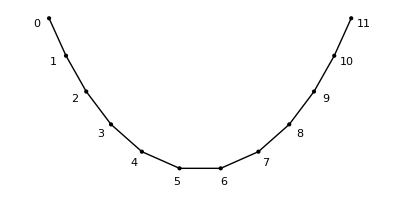

```mathematica
drawChain[1, 0, 1.5, 10, Connect->True, Number->True]
```

We can now move on to the actual comparison. The function below shows together a discrete chain with N elements and a continuous cable, with their parameters x_p, z_p, L being equal.

```mathematica
ClearAll[compareEquilibrium];
compareEquilibrium[xp_, zp_, L_, Nballs_] := Show[{drawCable[xp, zp, L, Label -> False], drawChain[xp, zp, L, Nballs, Connect -> True]}]
```

Below are given some outputs of this function for various values of N. You can see that although initially the chain, whose members are drawn as black circles, is rather far from the green line representing the cable, as N increases, the chain becomes closer and closer to the cable.

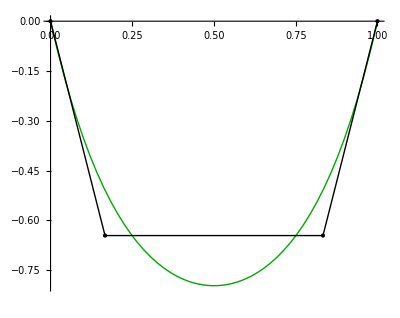
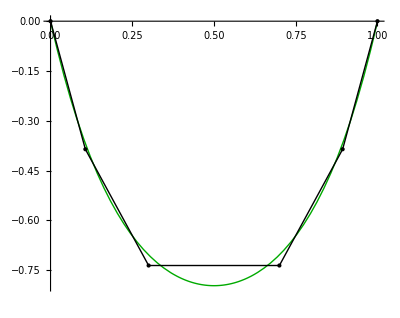
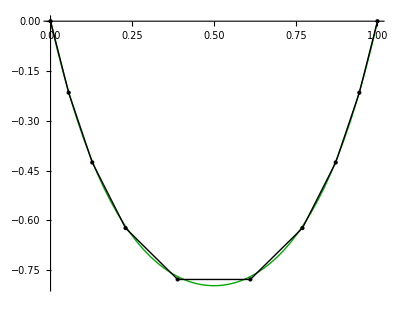
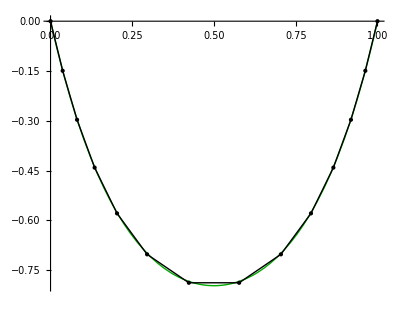

```mathematica
compareEquilibrium[1, 0, 2, #]& /@ {2, 4, 8, 12}
```

For large N, the cable and the chain have, as hypothesized, virtually the same shape.

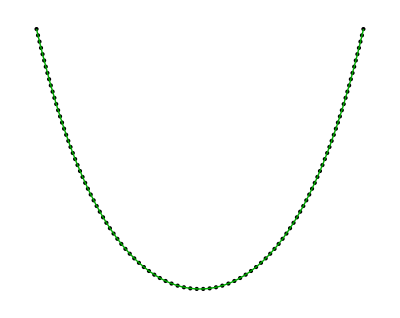

```mathematica
compareEquilibrium[1, 0, 2, 100]
```

There is a very intuitive explanation for that. The potential energy of the chain in the gravitational field is given by U = (∑^N)_(k = 1)m g z_k, where z_k is the z coordinate of the k-th ball. For large N, this sum can be approximated as an integral, and so the potential energy of a hanging chain becomes the same as that of a continuous cable. Next, using the principle of minimum potential energy, we can show that this means that the shape of a chain with a large number of elements is the same as that of a cable.

#### drawChain code

```mathematica
ClearAll[drawChain];
Options[drawChain] = {"Connect" -> False, "Number" -> False, "NumberBounds" -> True, "PlotRange" -> All, "PointSize" -> Medium};
drawChain[Svals_, Cvals_, λ_, OptionsPattern[]] := Module[
	{
		plist = { {0, 0} }, glist,
		currx = 0, currz = 0,
		Nballs = Length[Svals] - 1
	},
	Table[
		currx += λ Svals[[n]];
		currz -= λ Cvals[[n]];
		
		AppendTo[plist, {currx, currz}],
		{n, Length[Svals]}
	];
	
	glist = {PointSize[OptionValue["PointSize"]], Point[#]}& /@ plist;
	
	If[OptionValue["Connect"],
		glist = Join[glist,
			Table[Line[{#[[n]], #[[n + 1]]}], {n, Length[#] - 1}] &@ plist
		];
	];
	
	If[OptionValue["Number"],
		glist = Join[glist,
			Table[
				Text[
					ToString[n - 1],
					plist[[n]] - λ/3 Normalize[{(Cvals[[#]] + Cvals[[Max[# - 1, 1]]])/2, (Svals[[#]] + Svals[[Max[# - 1, 1]]])/2}]&@ Min[n, Nballs + 1]
				],
				{n, If[OptionValue["NumberBounds"], 1, 2], If[OptionValue["NumberBounds"], Nballs + 2, Nballs + 1]}
			]
		];
	];
	
	Graphics[glist, PlotRange -> OptionValue["PlotRange"]]
];
drawChain[xp_, zp_, L_, Nballs_Integer, OptionsPattern[]] := Module[
	{
		λ = L / (Nballs + 1),
		Svals, Cvals
	},
	{Svals, Cvals} = findSC[xp, zp, L, Nballs];
	
	drawChain[Svals, Cvals, λ,
		"Connect" -> OptionValue["Connect"],
		"Number" -> OptionValue["Number"],
		"NumberBounds" -> OptionValue["NumberBounds"],
		"PlotRange" -> OptionValue["PlotRange"],
		"PointSize" -> OptionValue["PointSize"]
	]
]
```

### Eigenvalues of Y and K and normal frequencies

The chain’s configuration can be described using angles θ and φ, as shown on the figure below - the angles θ describe horizontal oscillations, while the angles φ describe in-plane oscillations.

-Graphics-Sight from the +y direction
-Graphics-Sight from above

Second derivatives of these angles are related to the angles themselves by the two equations below.

(θ^(··))_k = -ω_0^2(∑^N)_(n = 1)Y_kn θ_n
(φ^(··))_k = -ω_0^2(∑^(N-1))_(n = 1)K_kn φ_n

The frequencies of the normal modes of horizontal oscillations are given by ω_n = ω_0 √λ_n, where λ_n is the n-th eigenvalue of the Y matrix, and the same applies to in-plane oscillations. No, we hypothesize that a chain with a  large number of elements would behave in exactly the same way as a continuous cable, so the frequencies of the normal modes must match, too. While the frequency of the first normal mode of a chain with two free elements will be quite different from that of a continuous cable, the frequency of the first normal mode of a chain with one hundred elements should be very close. As N gets larger, the frequencies of the normal modes approach a certain limit, which is the frequency of oscillations of a continuous cable. And because ω_n = ω_0 √λ_n, this also means that the eigenvalues λ_n of the matrices Y and K must approach some fixed values as N → ∞. Let’s see if that’s the case.

The explanations below are given for the matrix Y; they can be repeated for K as well. Now, the matrix Y characterizes horizontal oscillations of a chain with N free balls. Because the chain is different for every N, the matrix Y would be different as well (for instance, it will have different dimensions), so we can treat it as a function of N: Y = Y[N]. For a given value of N, we can compute the eigenvalues of Y[N] and mark them on the vertical axis, as shown below for N = 9, x_p = 1, z_p = 0, L = 2.

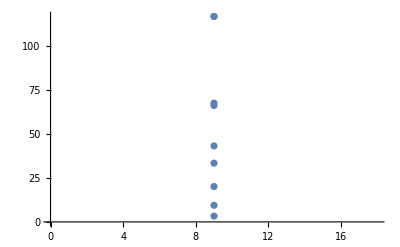

```mathematica
With[{Nballs = 9}, ListPlot@Transpose[{Array[Nballs&, Nballs], Eigenvalues[findY[1, 0, 2, Nballs]]}]]
```

Now, we can insert multiple values of N into this plot; for example, let N run from 9 to 11.

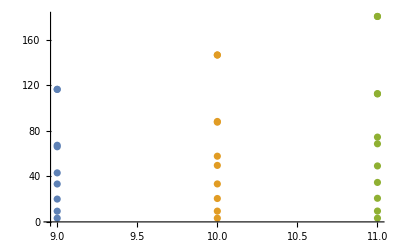

```mathematica
ListPlot@Join[Table[Transpose[{Array[Nballs&, Nballs], Eigenvalues[findY[1, 0, 2, Nballs]]}], {Nballs, 9, 11}]]
```

Since the number of eigenvalues rises with N (because it’s actually equal to N), it’s better to not plot all the eigenvalues but only the lowest four, for example.

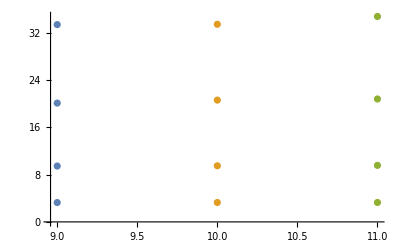

```mathematica
ListPlot@Join[Table[Transpose[{Array[Nballs&, 4], Eigenvalues[findY[1, 0, 2, Nballs]][[-4;;]]}], {Nballs, 9, 11}]]
```

And now, instead of N going from 9 to 11, we can iterate through a wider range, for instance from 4 to 50. (these are the last four eigenvalues, as Eigenvalues by default returns the eigenvalues of a matrix from greater to smaller)

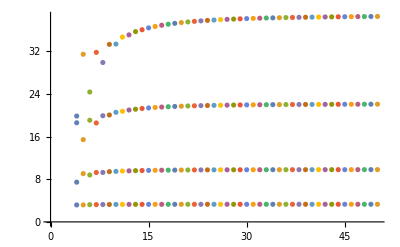

```mathematica
ListPlot@Join[Table[Transpose[{Array[Nballs&, 4], Eigenvalues[findY[1, 0, 2, Nballs]][[-4;;]]}], {Nballs, 4, 50}]]
```

You can see that the eigenvalues λ_n of the matrix Y converge to some definite values. We can see this more clearly in the following ListLinePlot, that is the same as the previous figure except that now, the points are connected into lines:

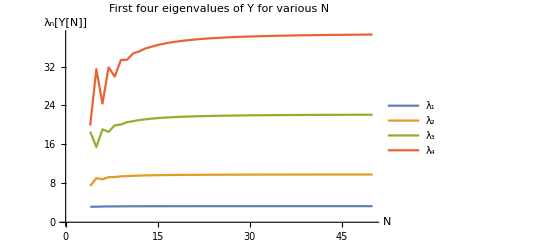

Although the eigenvalues for N= 4 are drastically different from eigenvalues for N = 5, we can see that the difference quickly reduces with N, and for N = 50, the eigenvalues seem to have practically reached some fixed limit. The same thing happens for the K matrix:

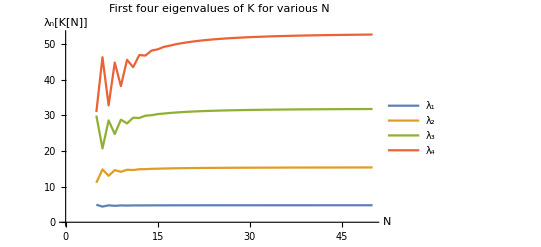

This leads us to the conclusion that indeed, the frequencies of the first four normal modes of a discrete chain approach some definite values as N → ∞. What might this value be? A logical guess would be to say that the eigenvalues become such that the normal frequencies are equal to those of a continuous cable:

ω_((d)n) → ω_((cont)n)                           as N → ∞

Here by ω_((cont)n) we mean that the n-th normal mode of either in-plane or horizontal (just one of them, not both) oscillations of a continuous cable is described either as y[t, ζ] = y[ζ] Cos[ω_((cont)n) t + ϕ] (for horizontal oscillations) or as h[t, ζ] = h[ζ] Cos[ω_((cont)n)t + ϕ] (for in-plane oscillations). We know that the normal modes can also be written in terms of ψ, η, and τ as y[t, ζ] = Λ ψ[(ζ - l_0)/Λ] Cos[ϖ τ + ϕ'], h[t, ζ] = Λ η[(ζ - l_0)/Λ] Cos[ϖ τ + ϕ']. By definition (88), τ ≡ √(g/Λ)t. Comparing the arguments of the cosine functions, we have ω_((cont)n) = √(g/Λ)ϖ_n.
	By ω_((d)n) we mean that a normal mode of horizontal oscillations is given by θ[t] = θ_0 Cos[ω_(d)t + ϕ], while an in-plane mode is given by φ[t] = φ_0 Cos[ω_(d)t + ϕ]. According to (169), ω_((d)n) = √λ_n ω_0; also, ω_0 = √(g/L)(160), so for ω_((d)n) we have ω_((d)n) = √(g/L λ_n).

√(g/L λ_n) → √(g/Λ)ϖ_n                          as N → ∞

From here,

λ_n → L/Λ ϖ_n^2                          as N → ∞

We can check this conclusion empirically by adding to the two previous plots horizontal lines representing the supposed asymptotes:

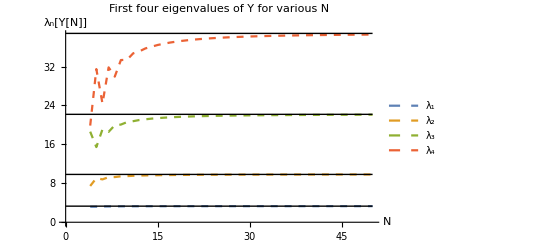

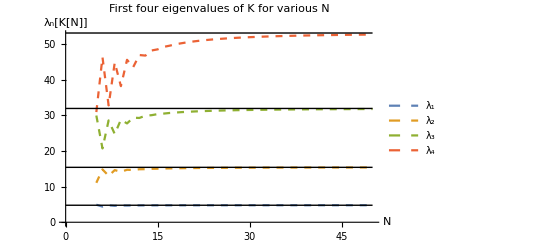

As we can see, the eigenvalues do really asymptote to certain values, and the values are such that the normal frequencies of a discrete chain with a large number of elements are equal to those of a continuous cable. An interesting observation is that the eigenvalues of the K matrix are slightly higher than those of Y, meaning that in-plane oscillations typically have a higher frequency than horizontal oscillations.

#### Code used to generate the figures

```mathematica
Block[
	{
		lines = {{}, {}, {}, {}},
		eigvals
	},
	
	Table[
		eigvals = Reverse@Eigenvalues[findY[1, 0, 2, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[4, 50]}
	];
	
	ListLinePlot[lines, PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"}, AxesLabel -> {"N", "λ_n[Y[N]]"}, PlotLabel -> "First four eigenvalues of Y for various N"]
]
```

```mathematica
Block[
	{
		lines = {{}, {}, {}, {}},
		eigvals
	},
	
	Table[
		eigvals = Reverse@Eigenvalues[findK[1, 0, 2, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[5, 50]}
	];
	
	ListLinePlot[lines, PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"}, AxesLabel -> {"N", "λ_n[K[N]]"}, PlotLabel -> "First four eigenvalues of K for various N"]
]
```

```mathematica
Block[
	{
		xp = 1, zp = 0, L = 2,
		lines = {{}, {}, {}, {}},
		eigvals,
		asymptotes,
		Λ, x0, σ0, σp, ϖ
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	σ0 = Sinh[-x0/Λ]; σp = Sinh[(xp - x0)/Λ];
	ϖ = findψNmodes[σ0, σp, 4][[All, 1]];
	asymptotes = L/Λ ϖ^2;
	
	Table[
		eigvals = Reverse@Eigenvalues[findY[xp, zp, L, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[4, 50]}
	];
	
	Show[{
		ListLinePlot[lines,
			PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"},
			AxesLabel -> {"N", "λ_n[Y[N]]"}, 
			PlotLabel -> "First four eigenvalues of Y for various N",
			PlotStyle -> {{Thick, Dashed}}
		],
		Graphics[{Thin, Black, Line[{{0, #}, {50, #}}]}& /@ asymptotes]
	}]
]
```

```mathematica
Block[
	{
		xp = 1, zp = 0, L = 2,
		lines = {{}, {}, {}, {}},
		eigvals,
		asymptotes,
		Λ, x0, σ0, σp, ϖ
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	σ0 = Sinh[-x0/Λ]; σp = Sinh[(xp - x0)/Λ];
	ϖ = findηNmodes[σ0, σp, 4][[All, 1]];
	asymptotes = L/Λ ϖ^2;
	
	Table[
		eigvals = Reverse@Eigenvalues[findK[xp, zp, L, Nballs]][[-4;;]];
		Table[
			lines[[l]] = Append[lines[[l]], {Nballs, eigvals[[l]]}],
			{l, 4}
		],
		{Nballs, Range[5, 50]}
	];
	
	Show[{
		ListLinePlot[lines,
			PlotLegends -> {"λ_1", "λ_2", "λ_3", "λ_4"},
			AxesLabel -> {"N", "λ_n[K[N]]"}, 
			PlotLabel -> "First four eigenvalues of K for various N",
			PlotStyle -> {{Thick, Dashed}}
		],
		Graphics[{Thin, Black, Line[{{0, #}, {50, #}}]}& /@ asymptotes]
	}]
]
```

## Comparing the normal modes as N → ∞

### Hypothesis

The hypothesis is that a chain with a large number of elements oscillates exactly like a continuous cable. Below is given a mathematical principle that can be used to test it.
	For the sake of example, it is written only for out-of-plane motion, however, the calculations below can easily be repeated for in-plane motion as well. The equation (77) reads

ρ(∂^2 y)/(∂t^2) = ∂/(∂ζ)[T_e(∂y)/(∂ζ)]

According to (69), l = ∫f_r dζ. Because f_r ≡ f[ζ, h[ζ]] = f[ζ, 0] + (∂f)/(∂h)h = f_e[ζ] + O[ε] and f_e = 1 (40), we know that l = ζ + O[ε], and consequently, ∂/(∂ζ) = ∂/(∂l) + O[ε]. Since y is of order ε, we get that (∂y)/(∂ζ) = (∂y)/(∂l) + O[y ε] = (∂y)/(∂l) + O[ε^2], and so the equation (77) can be written in terms of arc length l as

ρ(∂^2 y)/(∂t^2) = ∂/(∂l)[T_e(∂y)/(∂l)]

According t our hypothesis, a chain with a large number of elements oscillates like a continuous cable. If we draw a spline curve through the chain’s members, then we expect this curve to oscillate like a continuous cable and hence satisfies the PDE (77):

ρ(∂^2 y_(d))/(∂t^2) = ∂/(∂l)[T_e(∂y_(d))/(∂l)]

where y_(d) describes the spline curve through the discrete chain’s members:

y_k[t] = y_(d)[t, λ k]

where y_k is the y coordinate of the k-th ball as a function of time. The equation above tells us the value of y_(d) at some specific points corresponding to the discrete chain’s members; we can interpolate these values to find y_(d) everywhere else on the spline curve. The basic criterion is that we want y_(d)[t, ζ] and its first three spacial derivatives ∂/(∂ζ)y_(d)[t, ζ], ∂^2/(∂ζ^2)y_(d)[t, ζ], ∂^3/(∂ζ^3)y_(d)[t, ζ] to be continuous.

Let’s now say that we are looking at a normal mode, so that y_(d)[t, l] = y_(d)[l] Cos[ω t]. Substituting this into the previous equation, we get

-ω^2ρ y_(d) = d/dl[T_e (d y_(d))/dl]

According to (169), ω^2 = λ ω_0^2, where λ is the eigenvalue of Y corresponding to the eigenvector y, which we used to construct y_(d) (170).

-λω_0^2ρ y_(d) = d/dl[T_e (d y_(d))/dl]

And similarly, for in-plane oscillations we have

-ρω^2(d^2/dζ^2[R_e h_(d)] - k_e h_(d)) = d^2/dζ^2[R_e d/dζ[T_e(dh_(d))/dζ]] + d/dζ[dk_e/dζ T_e h_(d) + 2 k_e T_e(dh_(d))/dζ]

The equations (171) and (172) are a direct consequence of the hypothesis we are testing. So, if empirically we see that (171) and (172) do not hold, we can say right away that the hypothesis is wrong. The equations (171) and (172) are easily falsifiable and very unlikely to be true by accident - since they are numerical equations, any error would immediately become visible, and since they should be true on a continuous domain, it is extremely unlikely that something would just accidentally “match”. Thus, we can say that if (171) and (172) hold, then the hypothesis is most likely correct. So, we see that we can use (171) and (172) to test if our hypothesis is correct.

### Converting θ, φ to ζ, y, h

To find the y coordinates of the balls in (170), we need to somehow translate the information about normal modes from θ to y; in other words, currently we know what the normal modes are in terms of θ, but what are they in terms of θ? To find out, let us use the fact that the position of the k-th ball can be expressed either through coordinates ζ, y, h or θ, φ - the two representations are equivalent:

(r^–)_k = r^–(ζ_k, y_k, h_k) = r^–(θ, φ)

where θ is the collection of all θ’s and φ is the collection of all φ’s. We can now use first-order Taylor approximation:

r^–(ζ_(k(e)), y_(k(e)), h_(k(e))) + (∂r^–)/(∂ζ)(ζ_k - ζ_(k(e))) + (∂r^–)/(∂y)(y_k - y_(k(e))) + (∂r^–)/(∂h)(h_k - h_(k(e)))=
	=λ(∑^k)_(n = 1) (S_n
0
-C_n) + (C_n φ_n
S_n θ_n
S_n φ_n)

This must be true in equilibrium, when θ_n = φ_n = 0, so the constant terms must cancel. By the definition of ζ^̑, y^̑, h^̑ (36),

ζ^̑(ζ_k - ζ_(k(e))) + y^̑(y_k - y_(k(e))) + h^̑(h_k - h_(k(e)))=λ(∑^k)_(n = 1) (C_n φ_n
S_n θ_n
S_n φ_n)

Taking the dot product of this expression with ζ^̑, y^̑, h^̑ keeping in mind formulas (38) through (43), we obtain

ζ_k - ζ_(k(e)) = λ/f^2(∑^k)_(n = 1) (C_n φ_n
S_n θ_n
S_n φ_n) · ζ^̑
y_k - y_(k(e)) = λ(∑^k)_(n = 1) (C_n φ_n
S_n θ_n
S_n φ_n) · y^̑
h_k - h_(k(e)) = λ(∑^k)_(n = 1) (C_n φ_n
S_n θ_n
S_n φ_n) . h^̑

Here ζ^̑, y^̑, h^̑, f are evaluated at the point ζ = ζ_(k(e)), y = y_(k(e)), h = h_(k(e)). As N → ∞, we can assume that ζ_(k(e)) ≈ λ k, y_(k(e)) ≈ 0, h_(k(e)) ≈ 0. Thus, for large N,

ζ_k = λk +λ(∑^k)_(n = 1) (C_n φ_n
S_n θ_n
S_n φ_n) · (ζ^̑)_e[k λ]
y_k = λ(∑^k)_(n = 1) (C_n φ_n
S_n θ_n
S_n φ_n) · (y^̑)_e[k λ]
h_k = λ(∑^k)_(n = 1) (C_n φ_n
S_n θ_n
S_n φ_n) . (h^̑)_e[k λ]

We know that (y^̑)_e = <0, 0, 1> . Also, (h^̑)_e[k λ] ≈ <C_k, 0, S_k>. Thus,

y_k = λ(∑^k)_(n = 1) S_n θ_n
h_k = λ(∑^k)_(n = 1) (C_n C_k + S_n S_k)φ_n

Here are the two functions to automate this:

```mathematica
ClearAll[θtoy, φtoh];
θtoy[θlist_, L_, Nballs_, Svals_] := Block[{y = 0}, Table[y = y + L/(Nballs + 1) Svals[[n]] θlist[[n]], {n, Nballs}]];
φtoh[φlist_, L_, Nballs_, Svals_, Cvals_] := Table[L/(Nballs + 1) Sum[(Cvals[[n]] Cvals[[k]] + Svals[[n]] Svals[[k]]) φlist[[n]], {n, k}], {k, Nballs - 1}];
```

### A chain with some particular parameters

The next step is to compute the normal modes θ and φ. To avoid performing the same numerical computations multiple times, let us take some example parameters x_p, z_p, L, N, perform the computations, and store the result in global variables.

```mathematica
exampleL = 2;
examplexp = 1;
examplezp = 0;
exampleg = 1;
exampleN = 200;

exampleρ = 1;  (* this parameter doesn't actually matter as it eventually cancels *)

exampleΛ = findLambda[exampleL, examplexp, examplezp];
examplex0 = findX0[exampleL, examplexp, examplezp, exampleΛ];
examplel0 = exampleΛ Sinh[examplex0 / exampleΛ];
exampleTe[l_] := exampleρ exampleg exampleΛ Sqrt[1 + ((l - examplel0)/exampleΛ)^2];
exampleRe[l_] := exampleΛ (1 + ((l - examplel0)/exampleΛ)^2);
exampleke[l_] := 1/exampleΛ 1/(1 + ((l - examplel0)/exampleΛ)^2);

{exampleμ, exampleν} = findμν[examplexp, examplezp, exampleL, exampleN];
{exampleS, exampleC} = findSC[exampleμ, exampleν, exampleN];

exampleY = findY[exampleS, exampleμ];
exampleK = findK[exampleS, exampleC, exampleμ];

exampleYeigSyst = Eigensystem[exampleY];
exampleHeigSyst = Eigensystem[exampleK];
```

Here is what the chain looks like. It has 200 elements, which means that its shape is very similar to that of a continuous cable.

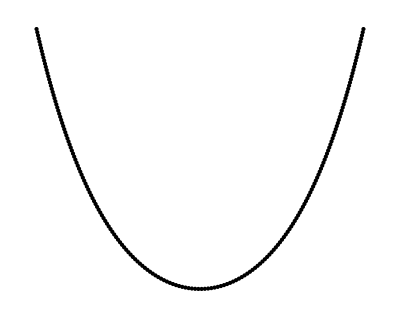

```mathematica
drawChain[examplexp, examplezp, exampleL, exampleN]
```

### Checking (171)

Here is a WL function that applies the principle explained above. It calculates the n-th normal mode for out-of-plane oscillations of a discrete chain and checks whether it’s also a normal mode of a continuous cable with equal x_p, z_p, L. It first calculates θ as an eigenvector of the Y matrix and from there computes y_(d) using (170). After that, it plugs in this function into (171) and plots the left-hand-side and the right-hand-side of the equation.

```mathematica
ClearAll[compareYnormalModes];
compareYnormalModes[normalModeNumber_] := compareYnormalModes[
	exampleL,
	exampleN,
	exampleρ,
	exampleg,
	exampleΛ,
	examplel0,
	exampleS,
	exampleYeigSyst,
	normalModeNumber
];
compareYnormalModes[L_, Nballs_, ρ_, g_, Λ_, l0_, Svals_, eigsystem_, normalModeNumber_] := plugInYfunc[
		√(g/L), L, ρ,
		findYfunc[
			L, Nballs, Svals,
			eigsystem[[2, -normalModeNumber]]
		],
		Function[l, ρ g Λ Sqrt[1 + ((l - l0)/Λ)^2]],
		eigsystem[[1, -normalModeNumber]],
		normalModeNumber
	];
	
ClearAll[findYfunc];
findYfunc[L_, Nballs_, Svals_, θlist_] := Interpolation[
	Transpose[{
			Prepend[L/(Nballs + 1)Range[Nballs], 0],
			Prepend[θtoy[θlist, L, Nballs, Svals], 0]
	}]
];

ClearAll[plugInYfunc];
plugInYfunc[ω0_, L_, ρ_, yfunc_, Te_, eigvalue_, normalModeNumber_] := Quiet[Plot[
		{
			-ρ ω0^2 eigvalue yfunc[l],
			D[Te[l1] D[yfunc[l1], l1], l1] /. l1 -> l
		},
		{l, 0, L},
		PlotRange -> All,
		PlotStyle -> {Cyan, {Thick, Dashed, Brown}},
		PlotLegends -> {"-ω^2 y", "∂/(∂ζ)[T_e(∂y)/(∂ζ)]"},
		PlotLabel -> Capitalize@IntegerName[normalModeNumber, "Ordinal"] <> " normal mode of out-of-plane oscillations"
	]];
```

Here is what the function outputs for the sixth normal mode:

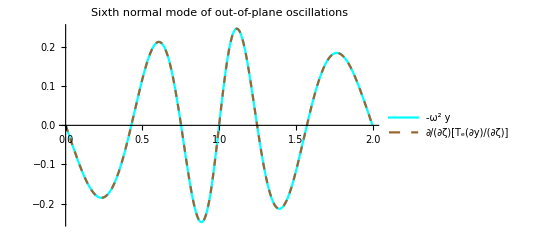

```mathematica
compareYnormalModes[6]
```

You can see that the left-hand-side and right-hand-side of (171) are, at least to a very good accuracy, equal. If you try this with other normal modes, the equality would still be true as long as the index of the normal mode is much less than N = 200 - which makes sense, since we only expect (171) to hold if the distance between two neighboring balls is much less than the characteristic scale for the variation of y_(d). Thus, we conclude that the horizontal oscillations of a chain with a large number of elements N are the same as those of a continuous cable with equal parameters x_p, z_p, L.

### Checking (172)

For (172), we follow very similar procedures as last time - calculate the n-th normal mode for in-plane oscillations of a discrete chain and check whether it’s also a normal mode of a continuous cable with equal x_p, z_p, L. The function below first calculates φ as an eigenvector of the K matrix and from there computes h_(d) using an analog of  (170). After that, it plugs in this function into (172) and plots the left-hand-side and the right-hand-side of the equation.

```mathematica
ClearAll[compareHnormalModes];
compareHnormalModes[normalModeNumber_] := compareHnormalModes[
	exampleL,
	exampleN,
	exampleρ,
	exampleg,
	exampleΛ,
	examplel0,
	exampleS,
	exampleC,
	exampleHeigSyst,
	normalModeNumber
];
compareHnormalModes[L_, Nballs_, ρ_, g_, Λ_, l0_, Svals_, Cvals_, eigsystem_, normalModeNumber_] := plugInHfunc[
		√(g/L), L, ρ,
		findHfunc[
			L, Nballs, Svals, Cvals,
			eigsystem[[2, -normalModeNumber]]
		],
		Function[l, Λ (1 + ((l - l0)/Λ)^2)],
		Function[l, 1/Λ 1/(1 + ((l - l0)/Λ)^2)],
		Function[l, ρ g Λ Sqrt[1 + ((l - l0)/Λ)^2]],
		eigsystem[[1, -normalModeNumber]],
		normalModeNumber
	];
	
ClearAll[findHfunc];
findHfunc[L_, Nballs_, Svals_, Cvals_, φlist_] := Interpolation[
	Transpose[{
		Prepend[L/(Nballs + 1)Range[Nballs - 1], 0],
		Prepend[φtoh[φlist, L, Nballs, Svals, Cvals], 0]
	}],
	InterpolationOrder -> 9
];

ClearAll[plugInHfunc];
plugInHfunc[ω0_, L_, ρ_, hfunc_, Re_, ke_, Te_, eigvalue_, normalModeNumber_] := Quiet[Plot[
		{
			-ρ ω0^2 eigvalue(
				D[Re[l1] hfunc[l1], {l1, 2}] - ke[l1] hfunc[l1]
			) /. l1 -> l,
			
			(* ρ∂^2/(∂t^2)[∂^2/(∂ζ^2)[Subscript[R, e] h] - Subscript[k, e] h] = ∂^2/(∂ζ^2)[Subscript[R, e]∂/(∂ζ)[Subscript[T, e](∂h)/(∂ζ)]] + ∂/(∂ζ)[(∂Subscript[k, e])/(∂ζ)Subscript[T, e] h + 2 Subscript[k, e] Subscript[T, e](∂h)/(∂ζ)] *)
			
			D[
				Re[l1] D[
					Te[l1] D[hfunc[l1], l1],
					l1
				],
				{l1, 2}
			] +
			D[
				D[ke[l1], l1] Te[l1] hfunc[l1] +
				2 ke[l1] Te[l1] D[hfunc[l1], l1],
				l1
			] /. l1 -> l
		},
		{l, 0, L},
		PlotRange -> All,
		PlotLegends -> {"-ω^2 (∂^2/(∂SuperscriptBox[ζ, 2])[R_eh] - k_eh)", "∂^2/(∂SuperscriptBox[ζ, 2])[R_e ∂/(∂ζ)[T_e(∂h)/(∂ζ)]] + ∂/(∂ζ)[(∂SubscriptBox[k, e])/(∂ζ)T_eh + 2 k_eT_e(∂h)/(∂ζ)]"},
		PlotStyle -> {Cyan, {Thick, Dashed, Brown}},
		PlotLabel -> "The " <> IntegerName[normalModeNumber, "Ordinal"] <> " normal mode of in-plane oscillations"
	]];
```

Here is what the function outputs for the fourth normal mode:

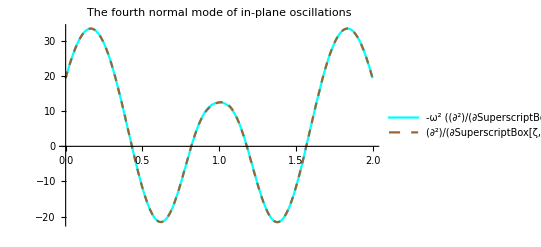

```mathematica
compareHnormalModes[4]
```

You can see that the left-hand-side and right-hand-side of (172) are, at least to a very good accuracy, equal. If you try this with other normal modes, the equality would still be true as long as the index of the normal mode is much less than N = 200 - which makes sense, since we only expect (172) to hold if the distance between two neighboring balls is much less than the characteristic scale for the variation of h_(d). Thus, we conclude that the horizontal oscillations of a chain with a large number of elements N are the same as those of a continuous cable with equal parameters x_p, z_p, L.

### Hypothesis confirmed

We just saw that the equations (171) and (172) are both true. And since they are both direct consequences of the hypothesis and at the same time are falsifiable and unlikely to be true by accident, we conclude that the hypothesis is most likely true - a discrete chain with a large number of elements oscillates like a continuous cable with equal parameters x_p, z_p, L.

## A hanging chain toy; visualizing the chain’s oscillations

### A hanging chain toy

```mathematica
ClearAll[hangingChainToy];
hangingChainToy[] := With[
	{
		P0 = {1/3, 1/6},
		N0 = 4, Nmin = 1, Nmax = 16,
		L0 = 1, Lmin = 0.5, Lmax = 2,
		disp = Function[x, StringPadRight[ToString@NumberForm[x, 3] <> If[IntegerQ[x], ".", ""], 4, "0"]]
	}, Module[
	{
		L = L0, Nballs = N0, P,
		Λ, x0,
		cable, chain = drawChain[P0[[1]], P0[[2]], L0, N0, PlotRange -> {{-0.2, 2}, {-1, 1}}, Connect -> True, PointSize -> Large]
	},
	Row[{
		Column[{
			Grid[{
				{Rotate[Manipulator[Dynamic[L], {Lmin, Lmax}], π/2], Rotate[Manipulator[Dynamic[Nballs], {Nmin, Nmax, 1}], π/2]},
				{Dynamic["L = " <> disp@L], Dynamic["N = " <> ToString@Nballs]}
			}],
			Button[
				"Draw chain",
				P[[1]] = Max[P[[1]], 1.2 * L/(Nballs + 1)];
				Λ = findLambda[L, P[[1]], P[[2]]];
				x0 = findX0[L, P[[1]], P[[2]], Λ];
				If[L^2 > P[[1]]^2 + P[[2]]^2,
					chain = drawChain[P[[1]], P[[2]], L, Nballs, PlotRange -> {{-0.2, 2}, {-1, 1}}, Connect -> True, PointSize -> Large]
				];
				Show[{cable, chain}]
			]
		}],
		Dynamic@Manipulate[
			P = P1;
			cable = hangingCableToyHelper[P, L];
			Column[{
				"Length of the chain: " <> disp@L,
				"Number of members:   " <> ToString@Nballs,
				Show[{cable, chain}, ImageSize -> 360]
			}],
			{{P1, P0}, {1.2 * L/(Nballs + 1), -1}, {2, 1}},
			ControlType -> Locator
		]
	}, "        ", Frame -> True, FrameStyle -> {Gray, Thick}, RoundingRadius -> 5, FrameMargins -> Large]
]];
```

An interactive toy that allows to explore the chain’s equilibrium:

```mathematica
hangingChainToy[]
```

| 
 | 
Draw chain

Show::gcomb: Could not combine the graphics objects in Show[{,chain$20779},ImageSize→360].

### Visualizing the normal modes

#### Draw horizontal oscillations

Find θ_(N+1) given θ_1, θ_2, ... θ_N using the formula (140):

```mathematica
ClearAll[horizontalBConds];
horizontalBConds[shortθlist_, S_] := Block[{Nballs = Length[S] - 1},
	Append[
		shortθlist,
		-1/S[[Nballs + 1]] Sum[S[[n]] shortθlist[[n]], {n, Nballs}]
	]
];
```

Draw a normal mode given by θ (called eigvect in the function), where the normal mode is normalized such that the maximum value of|y_k| equals amplitude:

```mathematica
ClearAll[drawChainHorizontalNMhelper];
drawChainHorizontalNMhelper[Svals_, eigvect_, amplitude_, l_, "HorizontalAxis" -> "x"] := Module[
	{
		Nballs = Length[Svals] - 1,
		currx, curry,
		plist,
		coef,
		θlist = horizontalBConds[eigvect, Svals]
	},
	coef = amplitude / Max[Abs /@ FoldList[Plus, 0, l Svals θlist]];  (* find such coef that Max[|y|] = amplitude *)
	
	plist = { {0, 0} };
	currx = 0; curry = 0;
	
	Table[
		currx += l Svals[[n]];
		curry += l coef Svals[[n]] θlist[[n]];
		
		AppendTo[plist, {currx, curry}],
		
		{n, Nballs}
	];
	
	Graphics[
		Point /@ plist,
		ImageSize -> Large
	]
];
drawChainHorizontalNMhelper[Svals_, eigvect_, amplitude_, l_, "HorizontalAxis" -> "n"] := Module[
	{
		Nballs = Length[Svals] - 1,
		curry, plist = { {0, 0} },
		coef,
		θlist = horizontalBConds[eigvect, Svals]
	},
	coef = amplitude / Max[Abs /@ FoldList[Plus, 0, l Svals θlist]];  (* find such coef that Max[|y|] = amplitude *)

	curry = 0;
	
	Table[
		curry += l coef Svals[[n]] θlist[[n]];
		
		AppendTo[plist, {l n, curry}],
		
		{n, Nballs}
	];
	
	Graphics[
		Point /@ plist,
		ImageSize -> Large
	]
];
```

Draw the n-th normal mode or normal modes from n-th to m-th for a chain with given parameters x_p, z_p, L, N:

```mathematica
ClearAll[drawChainHorizontalNM];
drawChainHorizontalNM[xp_, zp_, L_, Nballs_, n_] := drawChainHorizontalNM[xp, zp, L, Nballs, {n, n}, xp/9][[1]];
drawChainHorizontalNM[xp_, zp_, L_, Nballs_, n_, amplitude_] := drawChainHorizontalNM[xp, zp, L, Nballs, {n, n}, amplitude][[1]];
drawChainHorizontalNM[xp_, zp_, L_, Nballs_, {n_, m_}] := drawChainHorizontalNM[xp, zp, L, Nballs, {n, m}, xp/9];
drawChainHorizontalNM[xp_, zp_, L_, Nballs_, {n_, m_}, amplitude_] := Block[
	{
		μ, ν, Svals, Cvals, Ymatrix, eigvect
	},
	{μ, ν} = findμν[xp, zp, L, Nballs];
	{Svals, Cvals} = findSC[μ, ν, Nballs];
	
	Ymatrix = findY[Svals, μ];
	
	Table[
		eigvect = Eigenvectors[Ymatrix][[-normalModeNumber]];
		
		drawChainHorizontalNMhelper[Svals, eigvect, amplitude, L/(Nballs + 1), "HorizontalAxis" -> "n"],
		
		{normalModeNumber, n, m}
	]
]
```

Example: draw the third normal mode for x_p = 1, z_p = 0, L = 2, N = 20:

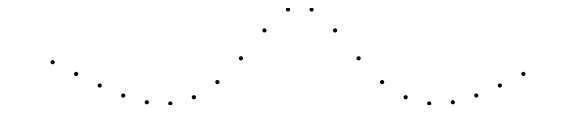

```mathematica
drawChainHorizontalNM[1, 0, 2, 20, 3]
```

Example: draw the second to fifth normal modes of the same chain:

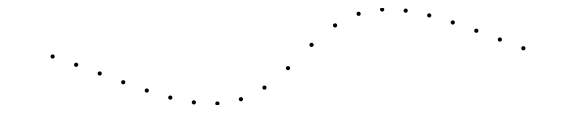
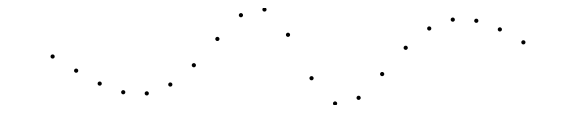
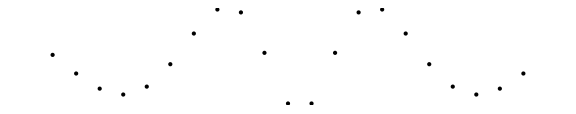
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
drawChainHorizontalNM[1, 0, 2, 20, {2, 5}]
```

The function plots y as a function of n.

#### Animate horizontal normal modes

Animate a normal mode given by θ (called eigvect in the function):

```mathematica
ClearAll[animateChainHorizontalNMhelper];
animateChainHorizontalNMhelper[Svals_, eigvect_, amplitude_] := Module[
	{
		Nballs = Length[Svals] - 1,
		currx, curry,
		plist,
		xlim, ylim,
		θlist = horizontalBConds[eigvect, Svals]
	},
	xlim = Total[Svals];
	ylim = amplitude Max[Abs /@ FoldList[Plus, 0, Svals θlist]];
	
	Animate[
		plist = { {0, 0} };
		currx = 0; curry = 0;
		
		Table[
			currx += Svals[[n]];
			curry += Cos[α] amplitude Svals[[n]] θlist[[n]];
		
			AppendTo[plist, {currx, curry}],
			
			{n, Nballs}
		];
	
		Graphics[
			Point /@ plist,
			PlotRange -> {{-1, xlim + 1}, {-ylim - 1, ylim + 1}},
			ImageSize -> Large
		],
		{α, 0, 2π}
	]
];
```

Animate the n-th normal mode for a chain with given parameters x_p, z_p, L, N:

```mathematica
ClearAll[animateChainHorizontalNM];
animateChainHorizontalNM[xp_, zp_, L_, Nballs_, normalModeNumber_] := animateChainHorizontalNM[xp, zp, L, Nballs, normalModeNumber, normalModeNumber / 2];
animateChainHorizontalNM[xp_, zp_, L_, Nballs_, normalModeNumber_, amplitude_] := Block[
	{
		μ, ν, Svals, Cvals, Ymatrix, eigvect
	},
	{μ, ν} = findμν[xp, zp, L, Nballs];
	{Svals, Cvals} = findSC[μ, ν, Nballs];
	
	Ymatrix = findY[Svals, μ];
	eigvect = Eigenvectors[Ymatrix][[-normalModeNumber]];
	
	animateChainHorizontalNMhelper[Svals, eigvect, amplitude]
]
```

Example: animate the 31st for a chain of 80 elements with x_p = 1, z_p = 0, L = 2:

```mathematica
animateChainHorizontalNM[1, 0, 2, 80, 31]
```

The function outputs what you would see if you looked at the chain from above.

#### Draw in-plane normal modes

Find φ_N and φ_(N+1) given φ_1, φ_2, ... φ_(N-1) using the formula (155):

```mathematica
verticalBConds[shortφlist_, Svals_] := Block[{Nballs = Length[Svals] - 1}, Join[
	shortφlist,
	{
		-1/Svals[[Nballs]] Sum[(Nballs + 1 - n)Svals[[n]]shortφlist[[n]], {n, Nballs - 1}],
		1/Svals[[Nballs + 1]] Sum[(Nballs - n)Svals[[n]]shortφlist[[n]], {n, Nballs - 1}]
	}
]];
```

Animate a normal mode given by φ (called eigvect in the function),:

```mathematica
Options[animateChainInPlaneNMhelper] = {"OutputForm" -> Full, "Period" -> 2};
animateChainInPlaneNMhelper[Svals_, Cvals_, eigvect_, amplitude_, OptionsPattern[]] := Module[
	{
		Nballs = Length[Svals] - 1,
		currx, currz,
		plist,
		xlim, zlim,
		φlist = verticalBConds[eigvect, Svals]
	},
	xlim = Total[Svals];
	zlim = Max@FoldList[Plus, 0, Cvals] + amplitude Max[Abs /@ FoldList[Plus, 0, Svals φlist]];
	
	Switch[OptionValue["OutputForm"],
		Full, #,
		Animate, # /. HoldPattern[AppearanceElements -> _] -> (AppearanceElements -> None)
	]& @ Animate[
		plist = { {0, 0} };
		currx = 0; currz = 0;
		
		Table[
			currx += Svals[[n]] + Cos[α] amplitude Cvals[[n]] φlist[[n]];
			currz += -Cvals[[n]] + Cos[α] amplitude Svals[[n]] φlist[[n]];
		
			AppendTo[plist, {currx, currz}],
			
			{n, Nballs + 1}
		];
	
		Graphics[
			Point /@ plist,
			PlotRange -> {{-1, xlim + 1}, {-zlim - 1, 1}}
		],
		{α, 0, 2π, AnimationRate -> 1/OptionValue["Period"]},
		AnimationRepetitions -> Infinity
	]
]
```

Animate the n-th normal mode for a chain with given parameters x_p, z_p, L, N:

```mathematica
ClearAll[animateChainInPlaneNM];
animateChainInPlaneNM[xp_, zp_, L_, Nballs_, normalModeNumber_] := animateChainInPlaneNM[xp, zp, L, Nballs, normalModeNumber, normalModeNumber / 2];
animateChainInPlaneNM[xp_, zp_, L_, Nballs_, normalModeNumber_, amplitude_] := Block[
	{
		μ, ν, Svals, Cvals, Kmatrix, eigvect
	},
	{μ, ν} = findμν[xp, zp, L, Nballs];
	{Svals, Cvals} = findSC[μ, ν, Nballs];
	
	Kmatrix = findK[Svals, Cvals, μ];
	eigvect = Eigenvectors[Kmatrix][[-normalModeNumber]];
	
	animateChainInPlaneNMhelper[Svals, Cvals, eigvect, amplitude]
]
```

Example: animate the 9nth for a chain of 80 elements with x_p = 1, z_p = 0, L = 2:

```mathematica
animateChainInPlaneNM[1, 0, 2, 80, 9]
```

The function outputs what you would see if you looked at the chain from above.

## Conclusion

## Comparing the numerical results to another article’s

### Normal frequencies of horizontal oscillations

The problem discussed in this work has been explored by John Gregg Gale in his 1976 master's thesis. The methods he used in his work are very different from those used here, however, he also happened to use the same definition of ϖ’s, which he called “natural frequency ratios”. At the end of the article, he provides a series of tables containing the results he obtained for various natural frequencies. We can use this as a reference to confirm the correctness of the present work.
	To make the comparison, let us use the first table for horizontal oscillations:

Here his h is the equivalent of my z_p and for z_p = 0, his b is the same as my x_p. For each value of x_p, we want to compare the ϖ’s he got to those that I got; for that, we first need to compute σ_0 and σ_p for each of the rows:

```mathematica
ClearAll[findσ0σp];
findσ0σp[xp_] := Block[
	{
		L = 1, zp = 0,
		Λ, x0
	},
	Λ = findLambda[L, xp, zp];
	x0 = findX0[L, xp, zp, Λ];
	
	{Sinh[-x0/Λ], Sinh[(xp - x0)/Λ]}
];
```

Now, having written the function to compute σ_0 and σ_p, we can find the ϖ’s using a new function findψϖlist, which is basically a shortcut for findψNmodes:

```mathematica
findψϖlist[xp_, normalModeNumber_] := Block[
	{σ0, σp},
	{σ0, σp} = findσ0σp[xp];
	
	findψNmodes[σ0, σp, normalModeNumber][[All, 1]]
];
```

And here is what the function yields:

```mathematica
Table[NumberForm[N[Round[#, 10^-2]], {∞, 2}]& /@ findψϖlist[1, xp, 0, 6], {xp, Reverse@{0.5, 0.6, 0.7, 0.75, 0.8, 0.85, 0.90, 0.95, 0.97}}] // MatrixForm
```

(3.64 | 7.23 | 10.84 | 14.44 | 18.05 | 21.65
2.79 | 5.51 | 8.25 | 11.00 | 13.74 | 16.48
1.91 | 3.74 | 5.59 | 7.44 | 9.29 | 11.15
1.51 | 2.92 | 4.36 | 5.80 | 7.24 | 8.69
1.27 | 2.41 | 3.60 | 4.78 | 5.97 | 7.17
1.09 | 2.05 | 3.06 | 4.07 | 5.08 | 6.09
0.96 | 1.78 | 2.65 | 3.52 | 4.39 | 5.26
0.76 | 1.37 | 2.04 | 2.71 | 3.38 | 4.05
0.62 | 1.06 | 1.60 | 2.11 | 2.63 | 3.16)

This table is generated by calculating the first six normal frequencies ϖ_n for x_p = 0.5, 0.6, 0.7, 0.75, 0.8, 0.85, 0.90, 0.95, 0.97, as in John Gregg Gale’s article. The format is chosen so that ideally, the table would be exactly as that of Gale’s. Here is what Gale’s table looks like:

You can see that the two tables are practically identical. Although some entries do vary by around 0.01, the results to match very closely. The values of ϖ predicted by this work are equal to those of John Gregg Gale.

### Normal frequencies of vertical oscillations

Let us repeat the above procedure for in-plane normal modes. We first define findηϖlist:

```mathematica
ClearAll[findηϖlist];
findηϖlist["xp" -> xp_, nmodes_] := Block[
	{σ0, σp},
	{σ0, σp} = findσ0σp[xp];
	
	findηNmodes[σ0, σp, nmodes][[All, 1]]
];
findηϖlist["ξ" -> ξ_, nmodes_] := Block[
	{σ0, σp},
	σp = √((1 + ξ)^2 - 1);
	σ0 = -σp;
	
	findηNmodes[σ0, σp, nmodes][[All, 1]]
];
```

Here, I’m defining the function two times because Gale’s paper sometimes takes the sag parameter to be convenient, sometimes ξ. Now, proceed to John Gregg Gale’s article, find the first table giving in-plane normal mode frequencies, and compute a table giving what the approximate values of ϖ’s are for the same parameters:

```mathematica
Table[NumberForm[N@Round[#, 10^-2], {∞, 2}]& /@ findηϖlist[param, 6], {param,
Reverse@{"xp" -> 0.5, "xp" -> 0.6, "xp" -> 0.7, "xp" -> 0.8, "ξ" -> 0.7, "ξ" -> 0.6, "xp" -> 0.8500, "ξ" -> 0.5,
"ξ" -> 0.4, "ξ" -> 0.3, "ξ" -> 0.2, "ξ" -> 0.1}}] // MatrixForm
```

(6.67 | 9.91 | 13.80 | 17.11 | 20.81 | 24.17
4.52 | 6.92 | 9.61 | 11.99 | 14.56 | 16.95
3.55 | 5.58 | 7.75 | 9.70 | 11.78 | 13.73
2.98 | 4.78 | 6.63 | 8.33 | 10.11 | 11.81
2.59 | 4.23 | 5.87 | 7.40 | 8.97 | 10.49
2.45 | 4.02 | 5.59 | 7.05 | 8.55 | 9.99
2.30 | 3.82 | 5.31 | 6.70 | 8.13 | 9.51
2.09 | 3.50 | 4.87 | 6.16 | 7.48 | 8.75
1.94 | 3.28 | 4.57 | 5.79 | 7.02 | 8.23
1.34 | 2.35 | 3.31 | 4.22 | 5.12 | 6.02
0.98 | 1.76 | 2.50 | 3.21 | 3.91 | 4.60
0.74 | 1.33 | 1.92 | 2.47 | 3.02 | 3.56)

Here is the original table:

You can see that again, the two tables are practically identical. The difference between this essay’s and John Gregg Gale’s ϖ’s is largest for the sixth normal frequency for the middle rows, when the values of σ_0 and σ_p are just too large for Frobenius’s method, and the functions η_0, η_1, η_2, η_3 (106) are computed using NDSolve. The numerical error of NDSolve is larger for high ϖ’s - that’s why we see high errors there. The place that we should really be worried about is the lowest row, for which σ_0 and σ_p are largest and the cable sags the most. The purpose of (83) was to model the oscillations of a sagging cable, and we see that indeed, for a cable with a large sag it does give the correct result. As we increase ϖ, the error increases, too, but just due to NDSolve’s numerical error - as soon as σ_0 and σ_p get sufficiently small, Frobenius’s method replaces NDSolve, and error immediately vanishes, showing that the equation (83) is also correct for high ϖ’s. Thus, we conclude that the values of ϖ predicted by the current work are, up to a numerical error, equal to those predicted by John Gregg Gale. Since the predictions are extremely unlikely to match by accident, we may conclude that the results presented in this work are correct.

## Novelty and relevance of the work

### Novel things presented in the work

A big advantage of the present essays over past works is that it features interactive visualizations. The reader can experiment with the cable’s or chain’s parameters and see, visually, the system’s equilibrium and modes of oscillation. This makes the content much more intuitive and easy to understand, in addition of course to being entertaining. The demonstrations can be used in classes to illustrate the notion of a normal mode on a system more realistic than a slowly vibrating tight string (in real life, tight strings, such as guitar stings, are in fact so tight that their oscillations are too fast to see) and less complicated than a circular drum. A heavy rope hung on two poles is a very cheap and reliable demonstration and is also thus more practical than many other demonstrations.
	The current work also studies the oscillations of a discrete chain and compares them to those of a continuous cable - something I haven’t seen in other articles. It is interesting to see how a discrete chain approaches a continuous cable as the number of members increases because this touches a very relevant question of how discrete systems with a large number of elements behave. Water, which is made of lots of small molecules, at human scale behaves as if it were continuous. A quantum harmonic oscillator, which has discrete energy levels, does not however have the same thermal energy as its classical analog. A chain with a large number of elements oscillates like a continuous cable. But the emission of thermal radiation happens very differently for atoms with continuous and discrete energy spectra - the “ultraviolet catastrophe”. Sometimes the behavior of discrete systems does approach some limits, sometimes it doesn’t - there probably is not a general principle yet. Maybe, by looking at many examples of how discrete systems do or do not approach some limit we can deduce a general rule?

### Intersections with (and differences from) past works

The problem of an oscillating cable (or a chain, as it’s sometimes called) has been studied in a number of past articles. Perhaps one of the most comprehensive ones available for free is John Gregg  Gale’s master's thesis, written in 1976 in Oregon State University. The author uses methods that are quite different from those used in this work: while the current work describes the cable’s shape through h and y only, Gale’s thesis also makes use of variables representing the cable’s longitudinal displacement and angles. As a result, Gale’s derivation of the equations of motion depends on visual intuition more than the derivation given here, and the equations of motion are written not as two PDEs with one PDE corresponding to one variable but as multiple PDEs of lower order involving not only the cable’s normal displacement but also other variables such as its longitudinal displacement and angles. Each of the resulting equations is shorter and thus may be easier to analyse than (77) and (83). The equations (77) and (83), however, might be more transparent in that since they only contain y and h, it can be easier to see how the system oscillates - for instance, it’s probably much easier to see how the cable would oscillate if plucked from the equation (88) than from a collection of connected PDEs.
	In Gale’s article, the normal modes of in-plane motion are found in terms the cable’s longitudinal displacement, while in the current work they are found in terms of the cable’s tangential displacement. The approach used in this work has the advantage of being easily visualizable: having found the function h[ζ], we can directly use it to draw the normal mode; having found the tangential displacement as a function of position, however, we have to perform some mathematical manipulations with the result to be able to draw the normal mode.
	Gale coordinatizes the cable through arc length; the work, on the other hand, introduces a curvilinear coordinate system fitted to the cable’s equilibrium. This difference in coordinates is another difference between the current work and Gale’s thesis.
	In his 1953 paper, David Saxon and A. S. Cahn “Modes of vibration of a suspended chain” described an approximate algorithm for finding the normal frequencies of in-plane oscillations. The current article also gives a method for estimating the normal frequencies, namely the formula (121). The formula presented in this work is derived in a comparatively simple way, namely by assuming ψ[σ] and η[σ] to be approximately sinusoidal at a given small interval; the derivation of the formula given by Saxon and Cahn’s article, on the other hand, is quite complicated and involves several pages. It does not, however, contain hypergeometric function as (121) does, so it’s too, in some sense, simpler.
	It is interesting to mention articles on phenomena like conductor galloping, which is when a long electric cable oscillates due to wind, and oscillations of stay bridges. Although the phenomena are in many ways different to the idealized problem discussed in this work, one similarity is that they, too, involve fourth-order partial differential equations. One possible explanation is that maybe, in a cable-type system where both tension and tangential velocity vary, to obtain equations of motion written in terms of tangential displacement only we have to use some conditions, and using them involves differentiation; since we have to take care of two fields, tension and tangential velocity, we differentiate twice and thus end up turning a second-order wave-type equation into a fourth-order PDE. This question would be interesting to explore in future articles.

## Qualitative patterns in the cable’s normal modes

### Greater curvature and amplitude at the lowest point

Here is how the first 12 normal modes of the cable’s horizontal oscillations look at σ_0 = -8, σ_p = 8:

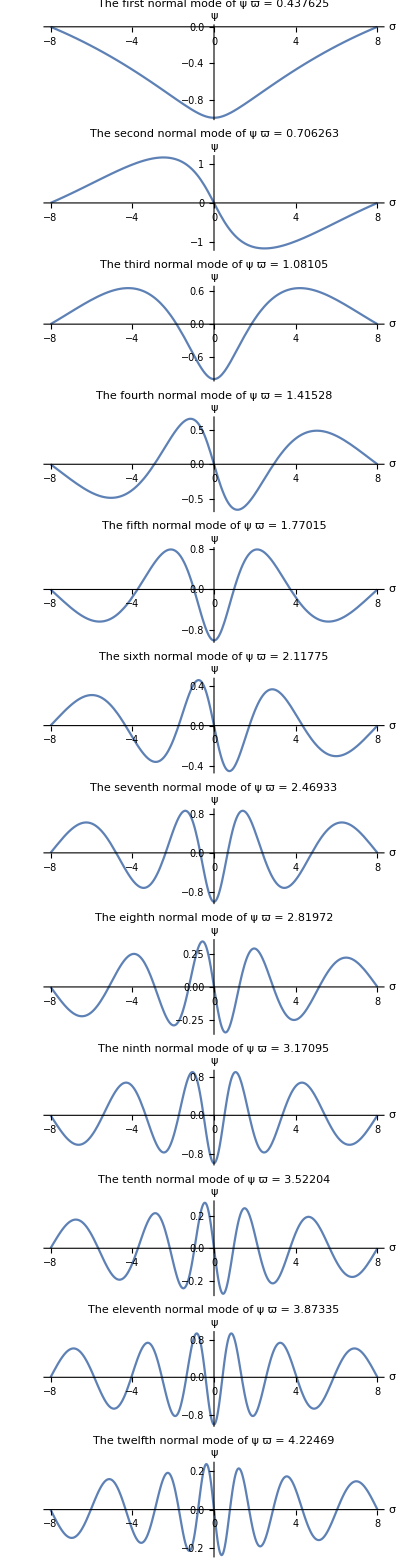

```mathematica
drawψNmodes[-8, 8, 12]
```

Notice an interesting pattern here: the normal modes oscillate much faster near σ = 0 than at the edges, and the amplitude of the oscillations is also larger at the middle. Here is another example, with σ_0 = -4, σ_p = 9:

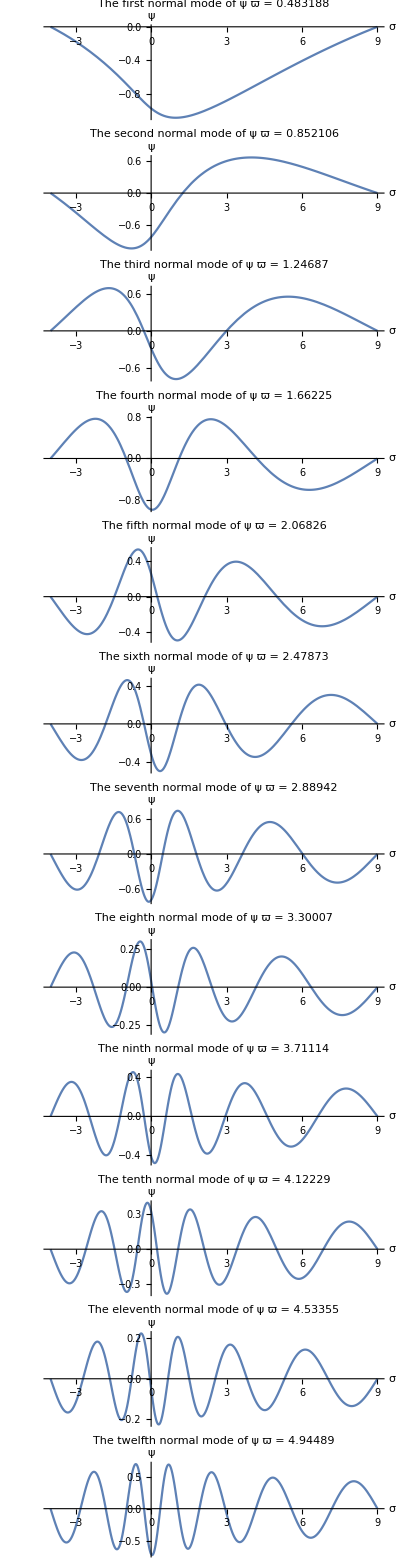

```mathematica
drawψNmodes[-4, 9, 12]
```

This is also true for in-plane oscillations. Here are the first twelve modes for σ_0 = -5, σ_p = 4:

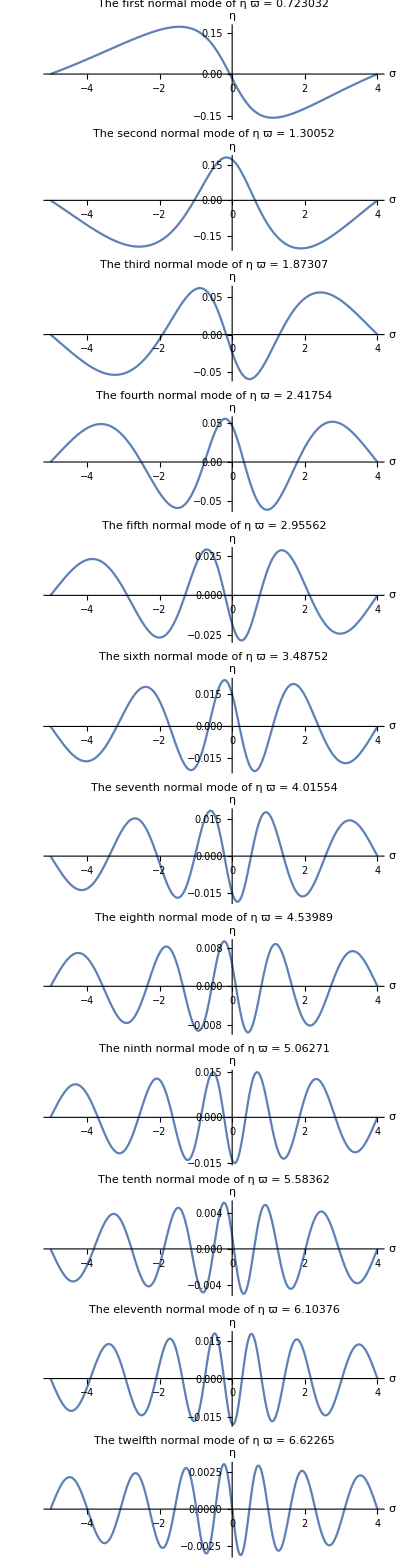

```mathematica
drawηNmodes[-5, 4, 12]
```

We again see the same thing happening. But why is that? An intuitive explanation goes as follows. Tension in the cable is smallest at the cable’s lowest point, which happens to be the point σ = 0. In a normal mode, the cable oscillates such that at any moment, the acceleration of a piece of cable is proportional to its displacement - we can see it from the formula y[t, ζ] = y[ζ] Cos[ω t], which implies (∂^2 y)/(∂t^2) = -ω^2y. But from Newton’s second law we also know that the acceleration would be a function of the cable’s curvature and tension - more precisely, the acceleration would increase with tension and the difference between the current curvature and equilibrium curvature. Combining the two conclusions, we see that since tension is lowest in the middle, the curvature of the cable must be really high to compensate for that - and this is what we observe in the plots above. The explanation for why the normal modes’ amplitude is greater at the middle is that intuitively, we know that it’s more difficult to get a tight string to oscillate than a string with a small tension. Or, for equal force, a string with a smaller tension would oscillate more than a string with a higher tension.  This is a somewhat hand-wavy argument though, and an alternative explanation is given in the section "Approximate algebraic expression for high-frequency modes".

### Parity

Here is what the first four normal modes of in-plane oscillations looks like for σ_0 = -2, σ_p = 2 (on the left) and σ_0 = -9, σ_p = 9 (on the right):

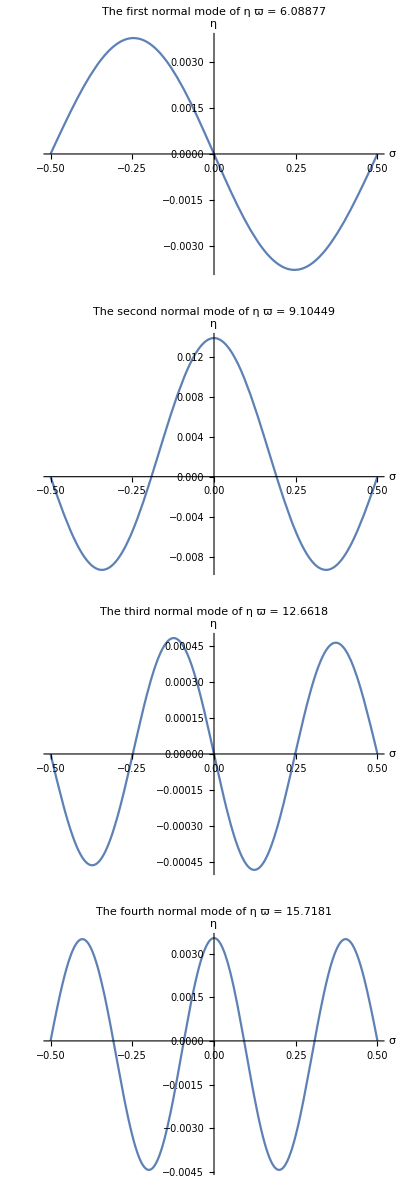
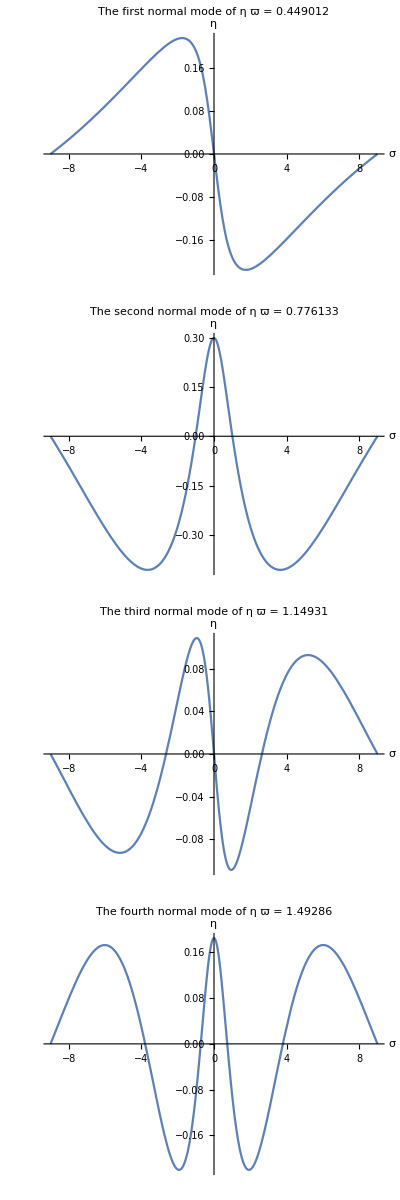

```mathematica
{drawηNmodes[-1/2, 1/2, 4], drawηNmodes[-9, 9, 4]}
```

The plots are in many ways different, however, one common characteristic that we can see is that they are either even or odd. And in fact, this is not a coincidence - as long as σ_0 = -σ_p, the normal modes of both horizontal and in-plane oscillations have this property. Intuitively this makes sense: the equations (89) and (90) are symmetric with respect to σ = 0, and as long as boundary conditions do not introduce asymmetry, it makes sense that the normal modes must respect parity.

## Qualitative patterns in the chain’s normal modes

### Properties shared with cable’s normal modes

In the sections “From small N to large; comparing to a continuous cable” and “Comparing the normal modes as N → ∞, we saw that a chain with a large number of elements oscillates very much like a continuous cable. And indeed, the normal modes tend to have greater “curvature” at the lowest point, and they too have the parity property if the chain is hung in a certain way, as you can see in the two illustrations below.

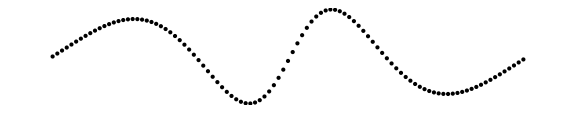
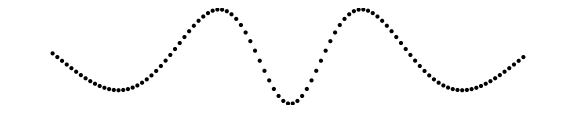
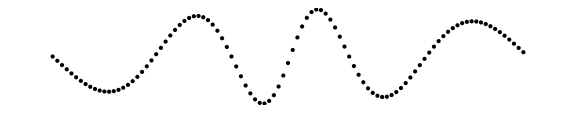

```mathematica
drawChainHorizontalNM[1, 0, 2, 100, {4, 6}]
```

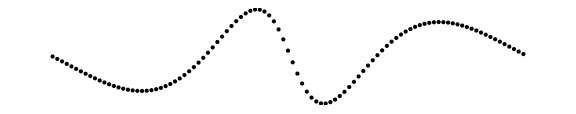
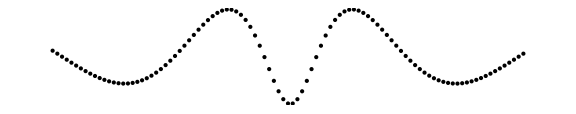
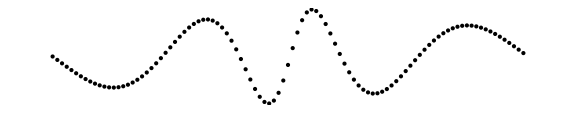

```mathematica
drawChainHorizontalNM[1, 0, 3, 100, {4, 6}]
```

The normal modes are either even or odd due to symmetry, and they, too, are more “curvy” at the middle. For z_p ≠ 0, you see that they are actually not symmetric:

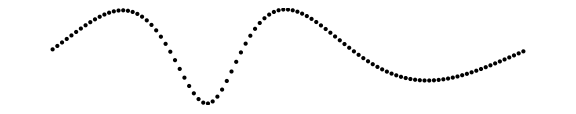
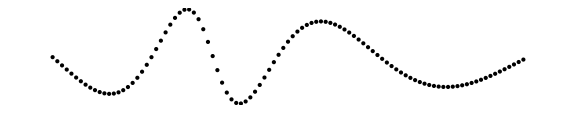
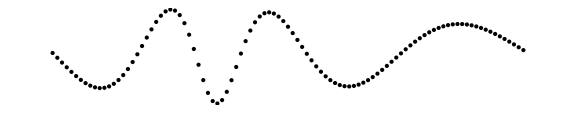

```mathematica
drawChainHorizontalNM[1, 1, 3, 100, {4, 6}]
```

### Violation of parity

If the index n of the normal mode is much larger than the number of members N, the chain behaves practically as a continuous cable. If, however, n is comparable, than we see some interesting things happening. Here is the 29-th normal mode of a chain of 30 elements, with x_p = 1, z_p = 0, L = 3:

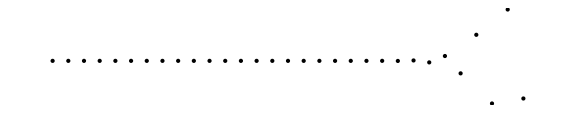

```mathematica
drawChainHorizontalNM[1, 0, 3, 30, 29]
```

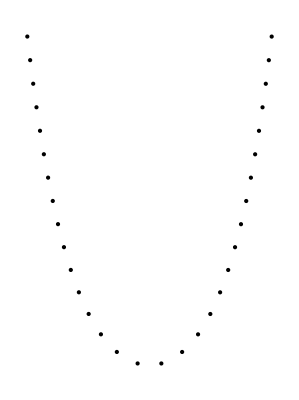

```mathematica
drawChain[1, 0, 3, 30]
```

You can see that there is virtually no displacement at the left end and a large displacement at the right end. But how can this make sense? We would expect the normal modes to have a  parity property. For example, this is what the 29-th normal mode of a “flat” chain looks like: (David Morin)

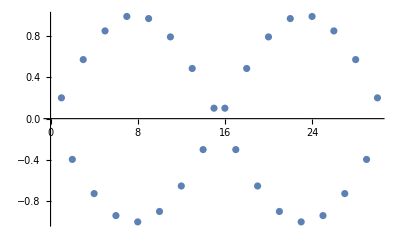

```mathematica
With[{m = 29, Nballs = 30}, ListPlot[Table[Sin[(n m π)/(Nballs + 1)], {n, Nballs}]]]
```

Why are the normal modes so different? The sagging chain was hung symmetrically, with z_p = 0, so why would we expect violations of parity? Is it a numerical error? Probably not. The explanation is that parity really is actually violated for a sagging chain; if we make the chain flatter by making L close to x_p, we see that the normal modes start resembling those of a “flat” chain:

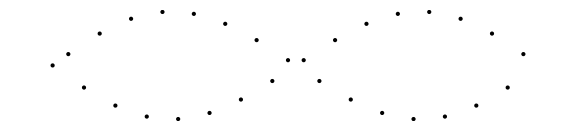

```mathematica
drawChainHorizontalNM[1, 0, 1.001, 30, 29]
```

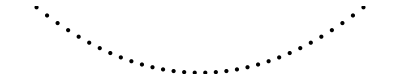

```mathematica
drawChain[1, 0, 1.001, 30]
```

You see that for x_p = 1, L = 1.001, the 29-th normal mode really does look like that of a “flat” chain. Let us explain this phenomenon.

#### Explanation

The following is a rather “hand-wavy” argument that is neither precise nor particularly convincing; however, it might give some intuition or be improved later. In the section "Approximate algebraic expressions for high-frequency normal modes", we saw that for a continuous cable with a low sag, the functions y[ζ] and h[ζ] describing the shape of a normal mode are approximately sinusoidal. If the cable is really tight, the “wavenumber” (it’s in quotation marks because it’s not constant throughout the cable’s length) is also very similar to what it would have been for a tight string: κ ≈ ϖ/((1+σ^2)^(1/4)) ≈ ϖ(1 - σ^2/4). For a tight cable, σ only goes in a small domain (see section "Tight cable"), and κ is approximately constant; and because boundary conditions demand y and h to be zero at the boundaries, we conclude that the κ’s must be approximately equal to those of a tight string.
	Now, let us to translate it to a discrete chain. For a discrete “flat-hanging” chain, the displacement of the n-th ball in the m-th normal mode is given by Sin[(n m π)/(Nballs + 1)] (David Morin), which is basically plugging in discrete values of x into the continuous formula. For a sagging chain, we would not expect to see that exact same thing of course, but some sort of correspondence might still be there. Now, here is the point. In the case of a discrete “flat-hanging” chain, the wavenumber matches the distance between the neighboring balls so that the normal modes look symmetric; but if we change the wavenumber by just a tiny bit, what would happen? The phase lag between the “flat-hanging” and sagging chain would increase by a tiny bit from one ball to another, and accumulating over time, it would make some displacement zero - and this is why parity is violated.

## Open questions

The formula (122) tells us that the normal modes of horizontal oscillations are orthogonal. We also know that the normal modes of a tight string are orthogonal, as well. Is there a general principle or an intuitive explanation for this?
	The equations (89) and (90) take a particularly simple form when written in terms of χ ≡ ArcSinh[σ] and ξ ≡ √(1 + σ^2) - 1: when written in terms of χ, (89) simplifies to (d^2 ψ_n)/dχ^2 + ϖ_n^2 Cosh[χ]ψ_n = 0, and in (90), the coefficient before η becomes zero, effectively reducing it to a third-order equation; when written in terms of ξ, both (89) and (90) have polynomial coefficients. Incidentally, the coordinates χ and ξ also happen to be, up to a linear transformation, Cartesian coordinates. By definition (88), σ ≡ Sinh[(x - x_0)/Λ], so ξ = (x - x_0)/Λ, which is the horizontal displacement from the cable’s lowest point divided by Λ. By substituting σ = Sinh[(x - x_0)/Λ] into ξ = √(1 + σ^2) - 1, we get ξ = Cosh[(x - x_0)/Λ] - 1. But the formula for z_e[x], which describes the cable’s equilibrium shape, is z_e[x] = Λ Cosh[(x - x_0)/Λ] -Λ Cosh[x_0/Λ]; thus, ξ = (z_e + Λ Cosh[x_0/Λ])/Λ - 1. In other words, ξ is the vertical displacement from the cable’s lowest point. How did it happen that the equation of motion are most simply written in terms of these coordinates? Maybe every system has some “natural coordinates” that can be guessed from physical intuition in which the equations of motion are written in a most simple form?
	Empirically one can observe that the natural frequencies of in-plane motion are, for a given cable, larger than those of horizontal motion. Why is that? Is there a simple explanation?

## References

The University of Utah, “Systems of differential equations”, http://www.math.utah.edu/~gustafso/2250systems-de.pdf
John Gregg Gale, Oregon State University, master’s thesis, 1976, https://ir.library.oregonstate.edu/downloads/6395w964x
UCONN, 2018, https://www.phys.uconn.edu/~rozman/Courses/m3410_18s/downloads/hanging-chain.pdf
Kaldybayev Rauan, 2020, https://community.wolfram.com/groups/-/m/t/2140007?p_p_auth=Jae8g07P
Titanic image from section “Introduction/Assumptions” taken from https://www.planetminecraft.com/project/rms-titanic-sinking-at-218-am-breaking-in-half/

## Bibliography

John Gregg Gale, Oregon State University, master’s thesis, 1976, https://ir.library.oregonstate.edu/downloads/6395w964x
UCONN, “Oscillations of a hanging chain”, 2018, https://www.phys.uconn.edu/~rozman/Courses/m3410_18s/downloads/hanging-chain.pdf
Saxon and Cahn, “Vibrations of a suspended chain”, 1953, The Quarterly Journal of Mechanics and Applied Mathematics, Oxford Academic